## Function Definitions

## working with individual scan files

### defining constants

```mathematica
(* rescaling recorded LTP data (in radians) by the inverse of this, will yield the pixel position of the centroid *)
ltpConversionToSlopeFactorOld=-2.88395*10^(-6);
ltpConversionToSlopeFactorForNewCamera=-2.8698108481409797*10^(-6);
ltpConversionToSlopeFactorQ=-2.86465*10^(-6)
ltpConversionToSlopeFactor=-2.88797*10^(-6)


radToMicroRad=1000000;
degToRad=Pi/180;
detrendOrder=1;
fontSize = 12;

degF=Table[{(n-32)*5/9,n},{n,-10,120}];
plankConsteVs=4.135667516*10^-15; (* eV s *)
speedOfLight=2.99792458*10^8;(* m/s *) 


swapInstrumetnsBetweenLTPandDLTP=If[
LTP==True&&DLTP==False,
LTP=False;
DLTP=True;
OSMSmap=False,
If[DLTP==True&&LTP==False,
LTP=True;
DLTP=False;
OSMSmap=False]
];
swapToOSMS:={OSMS=True, DLTP=False,LTP=False,OSMSmap=False};
swapToDLTP:={OSMS=False, DLTP=True,LTP=False,OSMSmap=False};
swapToLTP:={OSMS=False, DLTP=False,LTP=True,OSMSmap=False};
swapToOSMSmap:={OSMS=False, DLTP=False,LTP=False,OSMSmap=True};
swapToBL801:={OSMS=False, DLTP=False,LTP=False,OSMSmap=False,BL801m=True};

leftDw=True;
(* this is just the number of string characters after standard file_names.dat *)
dotExtlength=4
quadFittingThreshold=.5
```

-2.86465×10^-6

-2.88797×10^-6

4

0.5

### Optimal Scanning Sequence coordination

```mathematica
maxNumScans = 16; (* F-B-B-F-B-F-F-B *)
maxNumTraces=maxNumScans;

(* vectors of which scans are forward and which are backward, for either a 4 scan run or an 8 scan run *)
fScans16={1,4,6,7,10,11,13,16};
bScans16={2,3,5,8,9,12,14,15};  (*
fScans16={1,4,6,7,9,12,14,15};
bScans16={2,3,5,8,10,11,13,16};   *)
fScans8 = fScans16[[1;;4]]; (* {1,4,6,7}; *)
bScans8 = bScans16[[1;;4]];(* {2,3,5,8}; *)
fScans4 = fScans16[[1;;2]];
bScans4 = bScans16[[1;;2]];
fScans2 = {fScans16[[1]]};
bScans2 = {bScans16[[1]]};

fScanSequence[numScans_]:=Which[
numScans==1,{1},
numScans == 2, fScans2,
numScans == 4, fScans4,
numScans == 8, fScans8,
numScans == 16, fScans16
];
bScanSequence[numScans_]:= Which[
numScans==1,0,
numScans == 2, bScans2,
numScans == 4, bScans4,
numScans == 8, bScans8,
numScans==16,bScans16
];


flippedAfter4EffectiveDirections={"Forward   ","Backward","Backward","Forward   ","Forward   ","Backward","Backward","Forward   "};
```

### here is where the individual scan file names are systematically parsed

```mathematica
(* initializaton *)
(* some conversion of input paramaters to strings for file names *)
(* 
direction[numTrace_] :=
If[numTrace ==1||numTrace==4||numTrace==6||numTrace==7,
"F",
"R"
];
*)
direction[numScan_] :=
If[MemberQ[fScans16,numScan],
"F",
"R"
];


scnNumToString[scnNum_]:=If[scnNum<10,
"0"<>ToString[scnNum],
ToString[scnNum]];

instrumentSelectedQ=If[
LTP,"LTP",
If[DLTP,"DLTP",
If[OSMS,"OSMS"]
]
]

(* format of the data files generated by each respective instrument *)
dltpFormat[dir_,scanNum_]:= "DLTP\\AutoColl "<>ToString[dir]<>"\\AC_AI"<>direction[scanNum]<>ToString[dir]<>"-"<>ToString[scanNum];

oldltpFormat[dir_,scanNum_] := "LTP\\LTPScan"<>ToString[dir]<>"\\LTPAnalysis"<>direction[scanNum]<>"-"<>scnNumToString[scanNum];

ltpFormat[dir_,scanNum_] := "LTP\\LTPScan"<>ToString[dir]<>"\\LTPAnalysis-"<>scnNumToString[scanNum]<>direction[scanNum];

osmsFormat[dir_,scanNum_]:= "OSMS\\AutoColl "<>ToString[dir]<>"\\AC_AI"<>direction[scanNum]<>ToString[dir]<>"-"<>ToString[scanNum];

osms2DmapFormat[scanNum_]:="OSMS\\MotScan"<>ToString[scanNum];

bl801format[scanNum_,runNum_]:="BL801\\SigScan"<>ToString[scanNum];


(* This returns the file name format *)
instrumentFormat[dir_,scanNum_]:=Which[
DLTP,dltpFormat[dir,scanNum],
LTP,ltpFormat[dir,scanNum],
OSMS,osmsFormat[dir,scanNum]
]

instrumentFormatFileName[dir_,scanNum_]:=instrumentFormat[dir,scanNum]<>".dat"

instrumentSelected=Which[
DLTP,"DLTP",
LTP,"LTP",
OSMS,"OSMS"
]
```

If[LTP,LTP,If[DLTP,DLTP,If[OSMS,OSMS]]]

Which[DLTP,DLTP,LTP,LTP,OSMS,OSMS]

```mathematica
(* This takes the KolyaParameters file output from Wayne's Adjust Ellipse program *)
kolyaParametersFromFile[fileName_]:=Drop[Import[ToString[fileName],"Data"],38];

idealSlopeFromKolyaFile[fileName_]:=Take[kolyaParametersFromFile[fileName],All,{1,2}];
idealHeightFromKolyaFile[fileName_]:=Drop[kolyaParametersFromFile[fileName],None,{2,2}];

(* Below is meant to work with the datafiles from the PTB calibration of the autocollimators *)
ptbCalibrationDataImportWithApertureSelection[serialNumber_,aperture2k5or25_,XorY_, dist300or500_,range10or1000_]:=Drop[
Import[
"E3000_SN"<>ToString[serialNumber]<>"_50823PTB12_ApS"<>ToString[aperture2k5or25]<>"mm_Dist"<>ToString[dist300or500]<>"mm_"<>ToString[XorY]<>ToString[range10or1000]<>".dat","TSV"
],
1];

ptbCalibrationDataImport[serialNumber_,XorY_, dist300or500_,range10or1000_]:=ptbCalibrationDataImportWithApertureSelection[serialNumber,"2k5",XorY, dist300or500,range10or1000]


commaToDecimalDeliminator[dataVector_]:=Table[ToExpression[StringReplace[dataVector[[index]],","->"."]],{index,1,Length[dataVector]}];


ptbCalibrationDataMicroRadiansWithApertureSelection[serialNumber_,aperture_,XorY_, dist300or500_,range10or1000_]:=Block[
{sn=serialNumber,
ap=aperture,
xy=XorY,
dist=dist300or500,
range=range10or1000
},

asImported=ptbCalibrationDataImportWithApertureSelection[sn,ap,xy,dist,range];

PTBcalibrationMicroRadians=Thread[{
commaToDecimalDeliminator[
independentVectorOfFunction[asImported]
],
commaToDecimalDeliminator[
dependentVectorOfFunction[asImported]
]
}]*radToMicroRad*Pi/(60*60*180);

Return[
PTBcalibrationMicroRadians
]
]

ptbCalibrationDataMicroRadians[serialNumber_,XorY_, dist300or500_,range10or1000_]:=ptbCalibrationDataMicroRadiansWithApertureSelection[serialNumber,"2k5",XorY, dist300or500,range10or1000]
```

### convert *.txt to *.dat

#### This provides a means to check that the intended directory is selected And ensures that the original *.txt files are not corrupted, as all future processing read/write commands only work with the *.dat copies

```mathematica
(* the fllowing changes the extension of the .txt files to .dat *)
(* creating an effective copy of the file, with only the extension changed *)

txtFile[dir_,scanNum_]:=
If[DLTP,
dltpFormat[dir,scanNum]<>".txt",
If[LTP,
ltpFormat[dir,scanNum]<>".txt",
If[OSMS,
osmsFormat[dir,scanNum]<>".txt",
If[OSMSmap,
osms2DmapFormat[dir]<>".txt",
If[BL801m,
bl801format[dir,scanNum]<>".txt",
If[OTHER,
otherFileFormat<>".txt"
]]]]]];

convertToDat[dir_,scanNum_]:=
If[DLTP,
dltpFormat[dir,scanNum]<>".dat",
If[LTP,
ltpFormat[dir,scanNum]<>".dat",
If[OSMS,
osmsFormat[dir,scanNum]<>".dat",
If[OSMSmap,
osms2DmapFormat[dir]<>".dat",
If[BL801m,
bl801format[dir,scanNum]<>".dat",
If[OTHER,
otherFileFormat<>".dat"
]]]]]];

(* Mathematica plays better with *.dat files than with *.txt files with respect to formatting columns *)
toDat[dir_,scanNum_]:=CopyFile[txtFile[dir,scanNum],convertToDat[dir,scanNum]]

copyWithRenaming[dir_]:=
For[i=1,i≤maxNumTraces,i++,
toDat[ToString[dir],i]
];
```

### Pulls useful information from the header

```mathematica
(* This removes the dead lines at the end of Reverse direction LTP data sets *)
trimEndOfFile[file_]:=Module[
{importedFile=file},
num=0;
fileLength=Length[importedFile];
(* iterates throught and checks for dead lines at the end *)
While[
ToString[importedFile[[fileLength-num]]]=="{}",
num++
];
Drop[importedFile,-num]
];

(* determines the number of points in the scan file *)
dataLength[dirNum_, scanNum_]:= Module[
{dir=dirNum,
scn=scanNum},

fileWithHeader=trimEndOfFile[
If[DLTP,
Import[dltpFormat[dir,scn]<>".dat","Data"],
If[LTP,
Import[ltpFormat[dir,scn]<>".dat","Data"],
If[OSMS,
Import[osmsFormat[dir,scn]<>".dat","Data"],
If[OSMSmap,
Import[osms2DmapFormat[dir]<>".dat","Data"],
If[BL801m,
Import[bl801format[dir]<>".dat","Data"]
]
]
]
]
]
];

Length[
Flatten[
Take[
Drop[
fileWithHeader,
numberOfHeaderRows[fileWithHeader]
]
All,1]
]
]
];

(* This determines the number of header rows of a file where the first column is a colon delineated time sequence *)
numberOfHeaderRows[importedFile_]:=Module[
{rawFile=importedFile},

eofCorrection=trimEndOfFile[rawFile];
column=1;

numDataRows=0;
fileLength=Length[eofCorrection];
(* iterates throught and checks for data lines *)
While[
Length[StringSplit[
eofCorrection[[fileLength-numDataRows,column]],":"]
]==3,
numDataRows++
];

Return[
fileLength-numDataRows
]
];

rawHeaderRows[dir_]:=numberOfHeaderRows[trimEndOfFile[
If[DLTP,
Import[dltpFormat[dir,scn=1]<>".dat", "TSV"],
If[LTP,
Import[ltpFormat[dir,scn=1]<>".dat","TSV"],
If[OSMS,
Import[osmsFormat[dir,scn = 1]<>".dat","TSV"],
If[OSMSmap,
Import[osms2DmapFormat[dir],"TSV"<>".dat","TSV"],
If[BL801m,
Import[bl801format[dir]<>".dat","TSV"]
]
]
]
]
]
]
];

(* pulls the ideal increment of LTP carriage position step size (say 5 mm or 1 mm) *)
stepSize[dir_,scanNum_]:=Last[ Flatten[
If[DLTP,Take[
Import[dltpFormat[dir,scanNum]<>".dat", "Data"],
{5,5}],
If[LTP,Take[
Import[ltpFormat[dir,scanNum]<>".dat","Data"],
{6,6}],
If[OSMS,
Import[osmsFormat[dir,scanNum]<>".dat","Data"],
{11,11} (* test this reference value *)]
]
]
]];

scanEnd[dir_]:= Flatten[Take[
If[DLTP,
Import[ToString[instrumentSelectedQ]<>"\\AutoColl "<>ToString[dir]<>"\\AC_Raw_X"<>ToString[dir]<>"-avg.dat", "Data"],
If[LTP,
Import[ToString[instrumentSelectedQ]<>"\\LTPScan"<>ToString[dir]<>"\\Avg X Slope.dat","Data"],
If[OSMS,
Import[ToString[instrumentSelectedQ]<>"\\AutoColl "<>ToString[dir]<>"\\AC_Raw_X"<>ToString[dir]<>"-avg.dat","Data"]]
]
],
{4,4}
]];

endDate[dir_]:= ToString[First[scanEnd[dir]]];
endTime[dir_]:=ToString[Last[scanEnd[dir]] ];

dataRowNumberWithScanNumber[directoryNum_]:=Module[{},

For[
rowNum=1,
rowNum≤rawHeaderRows[directoryNum],
rowNum++,
If[
ToString[
Flatten[
Take[
Import[instrumentFormatFileName[directoryNum,1(* only checks the first scan file *)],"Data"],
{rowNum,rowNum}
]][[2]]
]=="Number:"||ToString[
Flatten[
Take[
Import[instrumentFormatFileName[directoryNum,1(* only checks the first scan file *)],"Data"],
{rowNum,rowNum}
]][[2]]
]=="#:",
Break[]
]
];
rowNum
]
(* dataRowNumberWithScanNumber[directoryNum_]:=Module[{},
For[
rowNum=1,
rowNum≤rawHeaderRows[directoryNum],
rowNum++,
If[
ToString[
Flatten[
Take[
Import[instrumentFormatFileName[directoryNum,1(* only checks the first scan file *)],"Data"],
{rowNum,rowNum}
]][[2]]
]=="Number:",
Break[]
]
];
rowNum
]  *)
(* a seemingly self evident function that is used by another function to determine how many scans there are for a run within a directory *)
scanNumber[dirNum_,scanNumber_]:=Module[
{dir=dirNum,
scanNum=scanNumber},
relevantDataRow=dataRowNumberWithScanNumber[dir];
 Last[ 
Flatten[
Take[
Import[instrumentFormatFileName[dir,scanNum], "Data"],
{relevantDataRow,relevantDataRow}]
]
]
];

(* scanNumber[dir_,scanNum_]:= Last[ Flatten[
If[DLTP,Take[
Import[dltpFormat[dir,scanNum]<>".dat", "Data"],
{8,8}],
If[LTP,Take[
Import[ltpFormat[dir,scanNum]<>".dat","Data"],
{12,12}],
If[
OSMS,Take[
Import[osmsFormat[dir,scanNum]<>".dat","Data"],
If[First[Flatten[Take[Import[osmsFormat[dir,scanNum]<>".dat","Data"],{12,12}(*{8,8}*)]]]=="Scan",
{12,12},
{8,8}]
]
]
]]
]];  *)


scanNumberDirTrc[dir_,scnNum_]:=
 Last[ 
Flatten[
Take[dirTraceLookup[dir,scnNum][[1]]]
]
];


(* this pulls the column labels from the labView recorded text file, assuming a *.tsv format *)
columnLabelsTSV[dirNum_,scanNum_]:=Module[
{dir=dirNum,
scn=scanNum},

fileWithHeader=If[DLTP,
Import[dltpFormat[dir,scn]<>".dat", "TSV"],
If[LTP,
Import[ltpFormat[dir,scn]<>".dat","TSV"],
If[OSMS,
Import[osmsFormat[dir,scn]<>".dat","TSV"],
If[OSMSmap,
Import[osms2DmapFormat[dir]<>".dat","TSV"],
If[BL801m,
Import[bl801format[dir]<>".dat","TSV"]
]]]]];
lastHeaderRow=numberOfHeaderRows[fileWithHeader];

Return[
Flatten[Take[
fileWithHeader,
{lastHeaderRow,lastHeaderRow}]]
]
];


dirScanLookup[directory_,scanNum_]:=Module[
{dir=directory,
scn=scanNum},
directoryIndex=First[Flatten[Position[scanFileDirectories,dir]]];
initDataSet[[directoryIndex]][[scn]]
]
dirTraceLookup[directory_,scanNum_]:=dirScanLookup[directory,scanNum]

(*  drops the descriptive header and the scan # and trace # *)
dirTraceDataset[dir_,trc_]:=Drop[dirTraceLookup[dir,trc],2];

columnLabelsDirTrc[dir_,trc_]:=Flatten[Take[dirTraceLookup[dir,trc],{2,2}]];
(* ****************************************************************** *)
(* here is an attempt to view the data column labels for a DLTP file *)

dataColumnsAndDesc[dir_,scn_]:=
Grid[
Prepend[
Thread[{
Table[n,{n,1,Length[columnLabelsTSV[dir,scn]]}],
columnLabelsTSV[dir,scn]
}],
{ToString[dir],SpanFromLeft}],
Frame->All,
Spacings->{2,1},
Alignment->{{Center,Left},Center},
Background->{None,{Lighter[Yellow,.8],{White,Lighter[Blend[{Blue,Green}],.9]}}}
]

dataColumnDescriptions[runNum_]:=dataColumnsAndDesc[runNum,1]

(* here the data will attempt to be imported automatically.  The condition will check if a trace exists *)
aScanExists[scanDir_,scanNum_]:=
Module[{dir=scanDir,
num=scanNum,
scanQ=True},

Quiet[If[Check[scanNumber[dir,num]==num,False]≠False,
scanQ,
scanQ=False];
Return[scanQ]
]]
(* aScanExists[scanDir_,scanNum_]:=
Module[{dir=scanDir,
num=scanNum,
scanQ=True},

Quiet[If[Check[scanNumber[dir,num]==num,False]≠False,
scanQ,
scanQ=False];
Return[scanQ]
]] *)
aTraceExists[scanDir_,scnNum_]:=aScanExists[scanDir,scnNum]

(* here the data will attempt to be imported automatically.  The condition will check if a trace exists *)
aTraceExistsDirTrc[scanDir_,traceNum_]:=
Module[{dir=scanDir,num=traceNum,traceQ=True},
Quiet[If[Check[scanNumberDirTrc[dir,num]==num,False]≠False,
traceQ,
traceQ=False];
Return[traceQ]
]]


(* This is for importing the DMI test data *)
sigScanHeaderRows=14;

sigScan[scanNum_]:=Drop[
Import["Sig"<>ToString[scanNum]<>".txt","TSV"],
sigScanHeaderRows]

sigScanHeaderLabels[scanNum_]:=Flatten[
Take[
sigScan[scanNum],
{1,1}
]
]

sigScanDescriptions[scanNum_]:=Grid[
Prepend[
Thread[{
Table[n,{n,1,Length[sigScanHeaderLabels[scanNum]]}],
sigScanHeaderLabels[scanNum]
}],
{ToString[scanNum],SpanFromLeft}],
Frame->All,
Spacings-> {2,1},
Alignment->{{Center,Left},Center},
Background->{None,{Lighter[Yellow,.8],{White,Lighter[Blend[{Blue,Green}],.9]}}}
]



sigScanDataMatrix[scanNum_]:=Drop[sigScan[scanNum],1]

sigScanDataFromColumn[scanNum_,dataCol_]:=Flatten[
Take[
sigScanDataMatrix[scanNum],
All,
{dataCol,dataCol}
]
]

sigScanXvsDMI[ScanNum_]:=Thread[{sigScanDataFromColumn[ScanNum,3],
sigScanDataFromColumn[ScanNum,5]
}]


sigScanTranslationVsDMI[ScanNum_]:=Thread[{sigScanDataFromColumn[ScanNum,3],
sigScanDataFromColumn[ScanNum,4]
}]

dmiFitOfSigScan[scanNum_]:=First[Last[
Fit[sigScanXvsDMI[scanNum],{1,x},x]
]]

sigScanNums={Scan0007,Scan0008,Scan0009,Scan0010};


(* This works with BL7.3.1.1 single motor scan data *)
(* It runs through all the SigScanXXXX-00XX.txt datasets, and joins a single data column as a function of time *)
sigScanRunInTime[sigScanNum_,dataColNum_]:=Module[
{},

files=FileNames["SigScan"<>ToString[sigScanNum]<>"-0*.txt"];

dataMatrix=Table[
Drop[
Import[files[[k]],"TSV"],
sigScanHeaderRows+1(* This also removes the data column labels *)],
{k,1,Length[files]}];

timeCoords=Flatten[
Table[
Flatten[
Take[
dataMatrix[[k]],
All,
{1,1}
]
],
{k,1,Length[files]}]
];

dataPoints=Flatten[
Table[
Flatten[
Take[
dataMatrix[[k]],
All,
{dataColNum,dataColNum}
]
],
{k,1,Length[files]}]
];

timeFunct=timeFunctHours[
timeDataFunctSecondsFromHMS[
Thread[{
timeCoords,
dataPoints
}]
]
];

Return[
timeFunct
]
]
```

```mathematica
sigScanRunInTimeTimeCoords[sigScanNum_]:=Module[
{},

files=FileNames["SigScan"<>ToString[sigScanNum]<>"-0*.txt"];

dataMatrix=Table[
Drop[
Import[files[[k]],"TSV"],
sigScanHeaderRows+1(* This also removes the data column labels *)],
{k,1,Length[files]}];

timeCoords=Table[
Flatten[
Take[
dataMatrix[[k]],
All,
{1,1}
]
],
{k,1,Length[files]}];

Return[
timeCoords
]
]
```

```mathematica
sigScanRunsFunctOfMotor[sigScanNum_,dataColNum_]:=Module[
{},

files=FileNames["SigScan"<>ToString[sigScanNum]<>"-0*.txt"];

dataMatrix=Table[
Drop[
Import[files[[k]],"TSV"],
sigScanHeaderRows+1(* This also removes the data column labels *)],
{k,1,Length[files]}];

dataColumnOfMotorcoords=3;
motorCoordsFunctions=Table[
Thread[{
Flatten[
Take[
dataMatrix[[k]],
All,
{dataColumnOfMotorcoords,dataColumnOfMotorcoords}
]
],
Flatten[
Take[
dataMatrix[[k]],
All,
{dataColNum,dataColNum}
]
]
}],
{k,1,Length[files]}];


Return[
motorCoordsFunctions
]
]
```

### Imports the data as a matrix

#### For Slope Profilers

```mathematica
(* This imports the entire trace information file for a single trace*)
dataMatrix[dirNum_,scanNum_]:=Module[
{dir=dirNum,
scn=scanNum},

fileWithHeader=trimEndOfFile[
If[DLTP,
Import[dltpFormat[dir,scn]<>".dat", "TSV"],
If[LTP,
Import[ltpFormat[dir,scn]<>".dat","TSV"],
If[OSMS,
Import[osmsFormat[dir,scn]<>".dat","TSV"],
If[OSMSmap,
Import[osms2DmapFormat[dir]<>".dat","TSV"],
If[BL801m,
Import[bl801format[dir]<>".dat","TSV"]
]]]]]
];

Drop[
fileWithHeader,
numberOfHeaderRows[fileWithHeader]
]
];
(*  dataMatrix[dir_,traceNum_]:=
trimEndOfFile[
Drop[
If[DLTP,
Import[dltpFormat[dir,traceNum]<>".dat", "Data"],
If[LTP,
Import[ltpFormat[dir,traceNum]<>".dat","Data"]
]],
rawHeaderRows[dir]]
];  *)

(* this determines the total number of traces within a scan run directory *)


numScansInRun[runDir_]:=Module[
{dir=runDir,
scanNum=1},

While[
aScanExists[dir,scanNum],scanNum;scanNum++
];
If[scanNum>1,
scanNum-1 ,
1
] 
]
numTracesInRun[runDir_]:=numScansInRun[runDir]

traceNumber=1;
numTracesInRunDirTrc[runDir_]:=Module[{dir=runDir,traceNum=traceNumber},
While[
aTraceExistsDirTrc[dir,traceNum],traceNum;traceNum++
];
If[traceNum>1,
traceNum-1 ,
1
] 
]

(* this imports all of the trace files within a scan run *)
importRun[directory_]:=Module[
{dir=directory},
Table[dataMatrix[dir,trace],{trace,1,numScansInRun[dir]}]
]

(* loads all the traces for analysis *)
initializeData[directoryRange_]:=Table[importRun[dir],{dir,directoryRange}];

(* ******************************************************************************************  *)
(* Below is an attempt to pre-import all relevent scan files into RAM befroe analysis begins. *)
(*  Though less flexible,                                                                      *) 
(*  it may prove a timesaver compared with all the otherwise required read commands           *)
(* ******************************************************************************************  *)

(* This will take a dataset from the Newer LTP scans, and re-order it *)
reorderDataMatrixToPositionForBscans[dataMatWithDesc_,scnNum_]:=Module[
{dataMatrx=dataMatWithDesc},
desc=Take[dataMatrx,1];
data=trimEndOfFile[Drop[dataMatrx,1]];

orderedData=If[direction[scnNum]=="R"&&LTPrecordedInTimeOrder,
Reverse[data],
data
];
Join[desc,orderedData]
];

(* This imports the entire trace information file for a single trace *)
dataMatrixWithDesc[directoryNum_,traceNum_]:=Module[
{dir=directoryNum,
trc=traceNum},

fileWithHeader=trimEndOfFile[
If[DLTP,
Import[dltpFormat[dir,trc]<>".dat", "TSV"],
If[LTP,
Import[ltpFormat[dir,trc]<>".dat","TSV"],
If[OSMS,
Import[osmsFormat[dir,trc]<>".dat","TSV"],
If[BL801m,
Import[bl801format[dir,trc]<>".dat","TSV"]
]]]]
];

Drop[
fileWithHeader,
numberOfHeaderRows[fileWithHeader]-1
]
];

dataMatrixWithDescAndHeaderAttributes[dir_,scnNum_]:=
Join[
{{dir,scnNum}},
reorderDataMatrixToPositionForBscans[
trimEndOfFile[dataMatrixWithDesc[dir,scnNum]],
scnNum]
];

importRunWithDescAndHeaderAttributes[dir_]:=Table[
trimEndOfFile[
dataMatrixWithDescAndHeaderAttributes[dir,trc]],
{trc,1,numTracesInRun[dir]}];(* the numTracesInRun is not used, as this function is called before the main dirTrc function is initialized *)

initDataWithDesc[directoryRange_]:=Table[importRunWithDescAndHeaderAttributes[dir],{dir,directoryRange}];
(*
initDataWithDesc[directoryRange_]:=Table[importRunWithDescAndHeaderAttributes[dir],{dir,directoryRange}];
*)(* initDataSet=initDataWithDesc[directoryRange];  *)
```

#### Exporting data to a file like the avg files

```mathematica
ltpSlopeFromMainRefReversed[runNum_]:=differenceOverCommonRange[
averageOfTracesFunctPosition[runNum,8](* data column changed from 16; April 2017 *),
detrendDatasetAndScale[
averageOfTracesFunctPosition[runNum,16](* data column changed from 8; April 2017 *),
0,1]
]

slopeValsToExport[twoColumns_]:=Table[
Join[
twoColumns[[k]],
{"g"}
],
{k,1,Length[twoColumns]}
]

(*
saveItForIDL[twoDarray_,fileNameString_]:=Export[
"s"<>ToString[fileNameString]<>".dat",
Join[
avgFileHeader10mmStep,
slopeValsToExport[
twoDarray]
]
]
*)

(* below are functions to take a two-column dataset and prepare for exporting, a file that looks like what IDL is expecting *)
middleExampleHeader={{"X unit: mm"},{"Z unit: rad"},{"Piston:2"},{"Tilt:",0.00906394755102215},{"Curvature:",0.},{},{},{},{"Focal","length:",1250.},{"Optical","mult:",1.01103},{"Wavelength:",0.00067},{"Temperatures:","Not","available"},{"Scan","type:","MEAS"},{"X","resolution:",0.00004},{"Margin,speed","or","margin:","10.000000,2.000000"},{"Camera","type:","Cronin","dual","opposed","array,","EPP"},{},{},{},{},{},{},{},{},{},{},{}};


headerForIDLWithDescriptionFromData[desc_,twoColumnDataSet_]:=Module[{data=twoColumnDataSet},

Join[{{"dummy header"}},{{"Surface data"}},{{"FilePath"}},{{"TimeStamp"}},{{ToString[desc]}},{{"Number of data: "<>ToString[Length[data]]}},
{{"Analysis: Autocollimator"}},{{"date time"}},{{"History:"}},{{"Data Type: SLOPE"}},{{"Step size: "<>ToString[
Abs[Round[
10*avgStepSize[data]
]/10//N]
]}},
middleExampleHeader,
{{"*Data starts."}}
]
]

(* this takes the two columns, and adds a 'g' column, as IDL is expecting *)
dataFormattedWithG[data_]:=Table[
Join[
data[[k]],
{"g"}],
{k,1,Length[data]}]

footerForIDL={""}

twoColumnDataForIDLprocessing[data_]:=Join[
headerForIDLWithDescriptionFromData["description",data],
dataFormattedWithG[data],
footerForIDL
]
```

{}

```mathematica
twoColumnsFromIDLandLTPwFormattedFiles[idlFile_]:=Take[
Drop[
idlFile,39
],
All,2
]
```

#### For Facilities MetaSys data

```mathematica
(* file header with column descriptions *)
jciHeaderRows=1;

(* pulls the entire file *)
roomDataFile[fileName_]:=Import[
ToString[fileName]<>".dat","TSV"
]

(* removes the header leaving a pure data file *)
roomData[fileName_]:=Drop[
roomDataFile[fileName],jciHeaderRows
]

(* the following functions deal with the time coordinates of the JCI data file for a single trend... from a comma separated data file *)
AMorPM[fileName_]:=
Flatten[
Take[roomData[fileName],All,{3,3}]
];
roomTimeData[fileName_]:=Flatten[Take[roomData[fileName],All,{2,2}]];
roomTimeDataAMPM[fileName_]:=Thread[{roomTimeData[fileName],AMorPM[fileName]}];
(* this converts the jci recorded time into decimal 24hr time *)
timeInFractionalHoursFrom12Hr[AMPMtimeCoordArray_]:=
Module[
{timeCoords12hr=Flatten[Take[AMPMtimeCoordArray,All,1]],
AMPMvalues=Flatten[Take[AMPMtimeCoordArray,All,-1]]},
timeInHours=Table[timeDecimalFromHMS[timeCoord]/3600,{timeCoord,timeCoords12hr}];
twentyFourHourTime=
Table[
Replace[timeInHours[[n]],
If[AMPMvalues[[n]]=="AM"&&hour[timeCoords12hr[[n]]]==12,
timeInHours[[n]]->timeInHours[[n]]-12,
If[AMPMvalues[[n]]=="PM"&&hour[timeCoords12hr[[n]]]!=12,
timeInHours[[n]]->timeInHours[[n]]+12,
timeInHours[[n]]->timeInHours[[n]]]
]],
{n,1,Length[timeInHours]}]
];

(* for a single trend, this pulls the variable function *)
jciData[fileName_]:=Flatten[Take[roomData[fileName],All,-1]];
(* and joins it to the time to make a two colume data file *)
jciDataOverTime[fileName_]:=Thread[{
timeInFractionalHoursFrom12Hr[roomTimeDataAMPM[fileName]],
jciData[fileName]}
];
(* here we deal with the trend data for multiple datasets *)
(* This makes a list of the number of data columns in filename *)
sequenceOfData[fileName_]:=Module[
{dataSet=roomData[fileName]},
Table[Length[dataSet[[k]]],{k,1,Length[dataSet]}]
];
(* This finds the maximum number of data columns *)
maxDataBandwidth[fileName_]:=Max[sequenceOfData[fileName]];

fullBandwidthDataTable[fileName_]:=Module[
{completeDataSet=roomData[fileName],
bandwidthRange=maxDataBandwidth[fileName],
bandwidthSequence=sequenceOfData[fileName]},
(* populate the first line of the data array *)
n=1;
While[
bandwidthSequence[[n]]≠bandwidthRange,
If[bandwidthSequence[[n]]=bandwidthRange,Break[]];
n++
];
fullRoomDataArray={completeDataSet[[n]]};
(* appends further good data array lines to the first to construct a complete data array *)
For[
k=n+1,(* because we already used n for the firsl line of the array *)
k≤Length[completeDataSet],
k++,
If[
bandwidthSequence[[k]]==bandwidthRange,
AppendTo[fullRoomDataArray,completeDataSet[[k]]]
]
];
fullRoomDataArray
] ;

(* the following functions deal with the time coordinates of the JCI data file *)
timeArrayTSV[fileName_]:= StringSplit[Flatten[
Take[fullBandwidthDataTable[fileName],All,{1,1}]
]];
AMorPMtime[fileName_]:=
Flatten[
Take[timeArrayTSV[fileName],All,{3,3}]
];
roomTimeDataFromTable[fileName_]:=Flatten[Take[timeArrayTSV[fileName],All,{2,2}]];
(* This section works only if the dataset is imported as a *.dat csv file *)
(* AMorPMtime[fileName_]:=
Flatten[
Take[fullBandwidthDataTable[fileName],All,{3,3}]
];
roomTimeDataFromTable[fileName_]:=Flatten[Take[fullBandwidthDataTable[fileName],All,{2,2}]]; *)
roomTimeDataAMPMfromTable[fileName_]:=Thread[{roomTimeDataFromTable[fileName],AMorPMtime[fileName]}];
(* this converts the jci recorded time into decimal 24hr time *)
timeInDecimalHoursFrom12Hr[AMPMtimeCoordArray_]:=
Module[
{timeCoords12hr=Flatten[Take[AMPMtimeCoordArray,All,1]],
AMPMvalues=Flatten[Take[AMPMtimeCoordArray,All,-1]]},
timeInHours=Table[timeDecimalFromHMS[timeCoord]/3600,{timeCoord,timeCoords12hr}];
twentyFourHourTime=
Table[
Replace[timeInHours[[n]],
If[AMPMvalues[[n]]=="AM"&&hour[timeCoords12hr[[n]]]==12,
timeInHours[[n]]->timeInHours[[n]]-12,
If[AMPMvalues[[n]]=="PM"&&hour[timeCoords12hr[[n]]]!=12,
timeInHours[[n]]->timeInHours[[n]]+12,
timeInHours[[n]]->timeInHours[[n]]]
]],
{n,1,Length[timeInHours]}]//N
];

(*  timeInDecimalHoursFrom12Hr[AMPMtimeCoordArray_]:=
Module[
{timeCoords12hr=Flatten[Take[AMPMtimeCoordArray,All,1]],
AMPMvalues=Flatten[Take[AMPMtimeCoordArray,All,-1]]},
timeInHours=Table[timeDecimalFromHMS[timeCoord]/3600,{timeCoord,timeCoords12hr}];
twentyFourHourTime=
Table[
Replace[timeInHours[[n]],
If[AMPMvalues[[n]]=="AM"&&hour[timeCoords12hr[[n]]]==12,
timeInHours[[n]]->timeInHours[[n]]-12,
If[AMPMvalues[[n]]=="PM"&&hour[timeCoords12hr[[n]]]!=12,
timeInHours[[n]]->timeInHours[[n]]+12,
timeInHours[[n]]->timeInHours[[n]]]
]],
{n,1,Length[timeInHours]}];
];  *)

(* this is the dataset from a particular column *)
dataFromColumnJCI[fileName_,column_]:=Flatten[Take[fullBandwidthDataTable[fileName],All,{1+column,1+column}]];

(* This section pulls the column labes from shich the datasets can have meaning *)
header[fileName_]:=Flatten[Take[roomDataFile[fileName],1]];
dataColumnLabels[fileName_]:=Drop[Take[header[fileName],maxDataBandwidth[fileName]-1],1];

columnLabelsForGrid[fileName_]:=StringSplit[dataColumnLabels[fileName]];
dataLabelsFromHeader[fileName_]:=Flatten[Take[columnLabelsForGrid[fileName],All,{2,2}]]

dataColumn[fileName_]:=
Grid[
Prepend[
Thread[{Table[n,{n,1,Length[dataLabelsFromHeader[fileName]]}],dataLabelsFromHeader[fileName]}],
{ToString[fileName],SpanFromLeft}],
Frame->All,
Spacings->{2,1},
Alignment->{{Center,Left},Center},
Background->{None,{Lighter[Yellow,.8],{White,Lighter[Blend[{Blue,Green}],.9]}}}
]


(* ************************************** *)(* ************************************** *)
(*               This below is the meat of the JCI data processing                   *)
(* ************************************** *)(* ************************************** *)
jciCleanRoomDataFunctTime[fileName_,column_]:=
Thread[{
timeInDecimalHoursFrom12Hr[roomTimeDataAMPMfromTable[fileName]],
dataFromColumnJCI[fileName,column]}
];
timeDataColumnWithoutHoles[timeDepDataset_]:=Module[
{dataFunctTime=timeDepDataset},
timeOfDataWithHoles=independentVectorOfFunction[dataFunctTime];
dataWithHoles=dependentVectorOfFunction[dataFunctTime];
(* populate the first line of the data array *)
n=1;
While[
dataWithHoles[[n]]== "",
If[dataWithHoles[[n]]≠ "",Break[]];
n++
];
timeVect={timeOfDataWithHoles[[n]]};
dataVect={dataWithHoles[[n]]};
(* appends further good data array lines to the first to construct a complete data array *)
For[
k=n+1,(* because we already used n for the firsl line of the array *)
k≤Length[dataFunctTime],
k++,
If[
dataWithHoles[[k]]≠ "",
AppendTo[timeVect,timeOfDataWithHoles[[k]] ];
AppendTo[dataVect,dataWithHoles[[k]]];
]
];
dataArray=Thread[{Flatten[timeVect],Flatten[dataVect]}]
] ;

(* Threads a single time dependent data set from a single column of the array *)
jciDataTrend[fileName_,column_]:=timeDataColumnWithoutHoles[jciCleanRoomDataFunctTime[fileName,column]];

(* if needed, converts a dataset in Deg F to deg C *)
fahrenheitDataToCentigradeData[dataset_]:=Thread[{
Flatten[Take[dataset,All,1]],
(Flatten[Take[dataset,All,-1]]-32)*5/9
}];

(* This functino takes the door state dataset and adds the prioir state for each state change recorded, allowing for box function style plotting *)
doorStateUseful[doorStateDataset_]:=Module[
{state=doorStateDataset},
stateVector=dependentVectorOfFunction[state];
timeVector=independentVectorOfFunction[state];
(* longer coordinate set adding a 5s opposite value *)
newTimeCoords=Flatten[
Table[
{timeVector[[n]]-1/3600,timeVector[[n]]},
{n,1,Length[state]}]
];
(* adds the door state *)
newStateCoords=Flatten[
Table[If[EvenQ[k],{"Open","Closed"},{"Closed","Open"}],{k,1,Length[state]}]
];

Thread[{newTimeCoords,newStateCoords}]
]

(* this takes the "Open" or "Closed" values and assigns them a numerical value *)
doorStateToBinary[doorStateDataset_]:=Module[
{stateDataSet=doorStateDataset},
timeCoords=independentVectorOfFunction[stateDataSet];
stateDataDescriptive=dependentVectorOfFunction[stateDataSet];
stateDataBinary=Table[
If[
ToString[stateDataDescriptive[[k]]]=="Open",
-1,
0
],
{k,1,Length[stateDataDescriptive]}];
Thread[{timeCoords,stateDataBinary}]
]


plotJCIdataFunctTimeUnitsAndDisplayColorWithRangesVertScale[indicator_,dataColumnNum_,units_,color_,psdRange_,vertPlotRange_]:=plotTimeDataWithColorAndDescWithRangesVertScale[
timeDataColumnWithoutHoles[
jciCleanRoomDataFunctTime[ToString[indicator],dataColumnNum]
],
ToString[units],
color,
ToString[dataLabelsFromHeader[indicator][[dataColumnNum]]],
psdRange,
vertPlotRange
]
(* plotJCIdataFunctTimeUnitsAndDisplayColor[indicator_,dataColumnNum_,units_,color_]:=plotTimeDataWithColorAndDesc[
timeDataColumnWithoutHoles[
jciCleanRoomDataFunctTime[ToString[indicator],dataColumnNum]
],
ToString[units],
color,
ToString[dataLabelsFromHeader[indicator][[dataColumnNum]]]
]  *)
plotJCIdataFunctTimeUnitsAndDisplayColor[indicator_,dataColumnNum_,units_,color_]:=
plotJCIdataFunctTimeUnitsAndDisplayColorWithRangesVertScale[indicator,dataColumnNum,units,color,Full,Automatic]
plotJCIdataFunctTime[indicator_,dataColumnNum_]:=plotJCIdataFunctTimeUnitsAndDisplayColor[indicator,dataColumnNum,"units",Darker[Darker[Green]]]
```

#### Here data vectors and functions are defined

```mathematica
(* This createsa  vector of values form a data column *)
dataFromColumnFunctTime[directory_,scnNum_, column_]:=Flatten[
Take[
dataMatrix[directory,scnNum],
All,
{column,column}]
]

dataFromColumnFunctTimeDirTrc[directory_,scnNum_, column_]:=Flatten[Take[dirTraceDataset[directory,scnNum],All,{column,column}]]


(* This vector is flipped if the scan directory is for a flipped substrate measurement *)
dataFromColumnFunctPosition[directory_,scnNum_, column_]:=Module[
{dir=directory,
scn=scnNum,
col=column},

Flatten[
Take[
dataMatrix[dir,scn],
All,
{col,col}]
]

]
(* dataFromColumnFunctPosition[directory_,trace_, column_]:=Module[
{dir=directory,
trc=trace,
col=column},
If[flippedQ[dir],
Reverse[-1*Flatten[Take[dataMatrix[dir,trc],All,{col,col}]]],
Flatten[Take[dataMatrix[dir,trc],All,{col,col}]]
]
]  *)

dataFromColumnFunctPositionDirTrc[directory_,scnNum_, column_]:=Module[
{dir=directory,
scn=scnNum,
col=column},

Flatten[
Take[
dirTraceDataset[dir,scn],
All,
{col,col}
]
]

]
(* dataFromColumnFunctPositionDirTrc[directory_,trace_, column_]:=Module[
{dir=directory,
trc=trace,
col=column},
If[flippedQ[dir],
Reverse[-1*Flatten[Take[dirTraceDataset[dir,trc],All,{col,col}]]],
Flatten[Take[dirTraceDataset[dir,trc],All,{col,col}]]
]
]*)

coordinateColumn=3;

(* this goes into the  DLTPscan file and pulls out the x coordinates of the carriage *)
tanScanCoord[scanDir_,scnNum_]:=Flatten[
Take[dataMatrix[scanDir,scnNum],
All,
{coordinateColumn,coordinateColumn}
]
];

tanScanCoordDirTrc[scanDir_,scnNum_]:=Flatten[
Take[dirTraceDataset[scanDir,scnNum],
All,{coordinateColumn,coordinateColumn}
]
];

(* &&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&& *)
scanCoord2D[scanDir_,scnNum_]:=
Take[dataMatrix[scanDir,scnNum],
All,
{xCoordCol=3,yCoordCol=4}]


functionOf2Dgantry[directory_,scanNumber_,dataColumn_]:=Block[
{dir=directory,
scnNum=scanNumber,
dataCol=dataColumn},

coords2D=scanCoord2D[dir,scnNum];
values=dataFromColumnFunctPosition[dir,scnNum,dataCol];

dataLen=Length[values];

coordValueArray=Table[
Join[
coords2D[[k]],{values[[k]]}
],
{k,1,dataLen}
];
Return[coordValueArray]
]

averageOf2DscansFunctPosition[directory_,dataColumn_]:=Module[
{dir=directory,
dataCol=dataColumn},

numTracesToAverage=numTracesInRun[dir];
importedStyle=Sort[
functionOf2Dgantry[dir,1,dataCol]
];
xCoords=xCoordVector[importedStyle];
yCoords=yCoordVector[importedStyle];

functionVals=Table[
zValVector[
Sort[
functionOf2Dgantry[dir,tr,dataCol]
]
],
{tr,1,numTracesToAverage}
];

meanFunction=Mean[functionVals];

avgdArray=Thread[{xCoordVector[importedStyle],yCoordVector[importedStyle],meanFunction}];
Return[
avgdArray
]
]
(* &&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&& *)


(* in cas the scan was not centered about the center of the SUT *)
(* tanScanCoordCentered[scanDir_, traceNum_]:=tanScanCoord[scanDir,traceNum]-surfaceCenterLtpUnits[scanDir]; *)

tanScanCoordCentered[scanDir_, scnNum_]:=Module[
{dir=scanDir,
scn=scnNum},

scanCenterCoord=Mean[tanScanCoordDirTrc[dir,scn]];

If[flippedQ[dir],
-Reverse[tanScanCoord[scanDir,scn]]+scanCenterCoord,
tanScanCoord[scanDir,scn]-scanCenterCoord
]
];

tanScanCoordCenteredDirTrc[scanDir_, scnNum_]:=Module[
{dir=scanDir,
scn=scnNum},

scanCenterCoord=Mean[tanScanCoordDirTrc[dir,scn](*{scanStartCoord,scanEndCoord}*)];

If[flippedQ[dir],
-Reverse[tanScanCoordDirTrc[scanDir,scn]]+scanCenterCoord,
tanScanCoordDirTrc[scanDir,scn]-scanCenterCoord
]
];
(* Original functions here *)
(* tanScanCoordCentered[scanDir_, traceNum_]:=Module[
{dir=scanDir,
trc=traceNum},
If[flippedQ[dir],
-Reverse[tanScanCoord[scanDir,traceNum]]+surfaceCenterLtpUnits[scanDir],
tanScanCoord[scanDir,traceNum]-surfaceCenterLtpUnits[scanDir]
]
];

tanScanCoordCenteredDirTrc[scanDir_, traceNum_]:=Module[
{dir=scanDir,trc=traceNum},
If[flippedQ[dir],
-Reverse[tanScanCoordDirTrc[scanDir,traceNum]]+surfaceCenterLtpUnits[scanDir],
tanScanCoordDirTrc[scanDir,traceNum]-surfaceCenterLtpUnits[scanDir]
]
]; *)

(* centers the first coord about zero *)
firstTanCoord[scanDir_,scnNum_] :=
If[
EvenQ[dataLength[scanDir,scnNum]],
(-dataLength[scanDir,scnNum]+1)*stp[scanDir]/2,
 -(dataLength[scanDir,scnNum]-1)*stp[scanDir]/2
];
lastTanCoord[scanDir_,traceNum_]:=-firstTanCoord[scanDir,traceNum];

firstTanCoordGeneral[scanDir_,scnNum_] :=
If[flippedQ[scanDir],-1,1]*
Last[Flatten[
If[DLTP,Round[10*First[tanScanCoordCentered[scanDir,scnNum]]]/10,
If[LTP,Take[
Import[ltpFormat[scanDir,scnNum]<>".dat","Data"],
If[flippedQ[scanDir],{5,5},{4,4}]]
]]
]];


tanCoordSettingGeneral[scanDirectory_,scnNum_] := Module[
{scanDir=scanDirectory,
scn=scnNum},
step=stp[scanDir];

firstCoordGeneral=firstTanCoordGeneral[scanDir,scn];
coordSetting=Table[firstCoordGeneral+n*step,{n,0,dataLength[scanDir,scn]-1}];
If[MemberQ[LTPtiemRecDirs,scanDir](*LTPrecordedInTimeOrder*)&&MemberQ[bScans16,scn], 
-1*coordSetting,
coordSetting
]
]

(* creats a vector of the set, ideal  coordinates for the LTP carriage - centered about zero *)
tanCoordSetting[scanDirectory_,scnNum_] := Module[
{scanDir=scanDirectory,
scn=scnNum},
step=stp[scanDir];

firstCoord=firstTanCoord[scanDir,scn];
coordSetting=Table[firstCoord+n*step,{n,0,dataLength[scanDir,scn]-1}];
If[MemberQ[LTPtiemRecDirs,scanDir](*LTPrecordedInTimeOrder*)&&MemberQ[bScans16,scn], 
-1*coordSetting,
coordSetting
]
]

functionOfCarriagePosition[dir_,scnNum_,dataCol_]:=Thread[{
tanScanCoord[dir,scnNum],
dataFromColumnFunctPosition[dir,scnNum,dataCol]
}];
functionOfCarriagePositionDirTrc[dir_,scnNum_,dataCol_]:=Thread[{
tanScanCoordDirTrc[dir,scnNum],
dataFromColumnFunctPositionDirTrc[dir,scnNum,dataCol]
}];

(* ====================================================================== *)
(* This works with only the forward or back scans, as defined by the FScan sequence *)
fwdScansOfRunNumDataColumn[runNum_,dataColNum_]:=Table[
functionOfCarriagePosition[runNum,scn,dataColNum],
{scn,fScans8}
]

bckScansOfRunNumDataColumn[runNum_,dataColNum_]:=Table[
functionOfCarriagePosition[runNum,scn,dataColNum],
{scn,bScans8}
]


averageOfFwdScansFunctPosition[directory_,dataColumn_]:=Module[
{},
averageOfDatasets[
fwdScansOfRunNumDataColumn[directory,dataColumn]
]
]

averageOfBckScansFunctPosition[directory_,dataColumn_]:=Module[
{},
averageOfDatasets[
bckScansOfRunNumDataColumn[directory,dataColumn]
]
]


(* these are legacy functions that assume a particular data column, 8 *)
fwdScansOfRun[runNum_]:=Table[
functionOfCarriagePosition[runNum,scn,8],
{scn,fScans8}
]

bckScansOfRun[runNum_]:=Table[
functionOfCarriagePosition[runNum,scn,8],
{scn,bScans8}
]


fwdScansOfRunAvg[runNum_]:=averageOfDatasets[
fwdScansOfRun[runNum]
]

bckScansOfRunAvg[runNum_]:=averageOfDatasets[
bckScansOfRun[runNum]
]

(* ====================================================================== *)

(* This returns the amount the carriage moved between points  *)
(* designed for use with Accumulate[] with respect to the integrating slope data to obtain height data *)
stepsOfData[dataset_]:=Block[
{data=dataset},

step=avgStepSize[data];

indepVect=independentVectorOfFunction[data];
numSteps=Length[indepVect]-1;

Join[{step},
Table[
indepVect[[k+1]]-indepVect[[k]],
{k,1,numSteps}]]
]


(*  =-===========================================-= *)
scansThroughTime[directory_,columnNumber_]:=Module[
{dir = directory,
colNum=columnNumber},

numScans=numTracesInRun[dir];
If[numScans>1,
lastScan=numScans;
knownFullScan=numScans-1];(*  This logic needsw editiong, see the *DirTrc[] function below *)
lastScanLength=Length[timeFunctOfDataColumn[dir,lastScan,colNum]];
knownFullScanLength=Length[timeFunctOfDataColumn[dir,knownFullScan,colNum]];


scansInTime=Table[
If[
MemberQ[fScanSequence[numScans],scn](* the OR is in case of an incomplete recording of a scan where LabVIEW does not reverse the order *)||lastScanLength≠knownFullScanLength,
timeFunctOfDataColumn[dir,scn,colNum],
If[
MemberQ[bScanSequence[numScans],scn],
  Reverse[timeFunctOfDataColumn[dir,scn,colNum]]
]
],
{scn,1,numScans}];

Return[scansInTime]

]
(*  =-===========================================-= *)


(* here is a module that joins multiple traces into a single dataset *)
joinMultipleTracesInTime[scanDir_,dataColumn_]:=Module[
{dir=scanDir,
colNum=dataColumn},
numScans=numTracesInRun[dir];
If[numScans>1,
lastScan=numScans;
knownFullScan=numScans-1];(*  This logic needsw editiong, see the *DirTrc[] function below *)
lastScanLength=Length[timeFunctOfDataColumn[dir,lastScan,colNum]];
knownFullScanLength=Length[timeFunctOfDataColumn[dir,knownFullScan,colNum]];

joinedTraces=
Flatten[
Table[
If[
MemberQ[fScanSequence[numScans],scn](* the OR is in case of an incomplete recording of a scan where LabVIEW does not reverse the order *)||lastScanLength≠knownFullScanLength,
timeFunctOfDataColumn[dir,scn,colNum],
If[
MemberQ[bScanSequence[numScans],scn],
  Reverse[timeFunctOfDataColumn[dir,scn,colNum]]
]
],
{scn,1,numScans}],
1(* flatten only one level to maintain two column functional form,  *)
];
joinedTraces
]

(* here is a module that joins multiple traces into a single dataset *)
joinMultipleTracesInTimeDirTrc[scanDir_,dataColumn_]:=Module[
{dir=scanDir,
colNum=dataColumn},
numTraces=numTracesInRunDirTrc[dir];
lastTrace=numTraces;
If[numTraces>1,
knownFullTrace=numTraces-1,
knownFullTrace=1];
lastTraceLength=Length[timeFunctOfDataColumnDirTrc[dir,lastTrace,colNum]];
knownFullTraceLength=Length[timeFunctOfDataColumnDirTrc[dir,knownFullTrace,colNum]];

joinedTraces=
Flatten[
Table[
If[LTP,
timeFunctOfDataColumnDirTrc[dir,trc,colNum],
If[
MemberQ[fScanSequence[numTraces],trc]||lastTraceLength≠knownFullTraceLength  ,(* the OR is in case of an incomplete recording of a scan where LabVIEW does not reverse the order *)
timeFunctOfDataColumnDirTrc[dir,trc,colNum],
If[
MemberQ[bScanSequence[numTraces],trc](*&&LTPrecordedInTimeOrder*),
  Reverse[timeFunctOfDataColumnDirTrc[dir,trc,colNum]],
timeFunctOfDataColumnDirTrc[dir,trc,colNum]
]
]
],
{trc,1,numTraces}],
1(* flatten only one level to maintain two column functional form,  *)
];
joinedTraces
];

(* here is a module that joins multiple traces into a single dataset *)
joinMultipleScansInTime[scanDir_,dataColumn_]:=Module[
{dir=scanDir,
colNum=dataColumn},
numTraces=numTracesInRun[dir];
lastTrace=numTraces;
If[numTraces>1,
knownFullTrace=numTraces-1,
knownFullTrace=1];
lastTraceLength=Length[timeFunctOfDataColumn[dir,lastTrace,colNum]];
knownFullTraceLength=Length[timeFunctOfDataColumn[dir,knownFullTrace,colNum]];

joinedTraces=
Flatten[
Table[
If[
MemberQ[fScanSequence[16(*numTraces*)],trc],(* the OR is in case of an incomplete recording of a scan where LabVIEW does not reverse the order *)
timeFunctOfDataColumn[dir,trc,colNum],
If[lastTraceLength≠knownFullTraceLength&&trc==lastTrace,
timeFunctOfDataColumn[dir,trc,colNum],
If[
MemberQ[bScanSequence[16(*numTraces*)],trc](*&&LTPrecordedInTimeOrder*),
  Reverse[timeFunctOfDataColumn[dir,trc,colNum]],
timeFunctOfDataColumn[dir,trc,colNum]
]
]
],
{trc,1,numTraces}],
1(* flatten only one level to maintain two column functional form,  *)
];
joinedTraces
]
(* here is a module that joins multiple traces into a single dataset *)
joinMultipleScansInTimeDirTrc[scanDir_,dataColumn_]:=Module[
{dir=scanDir,
colNum=dataColumn},
numTraces=numTracesInRunDirTrc[dir];
lastTrace=numTraces;
If[numTraces>1,
knownFullTrace=numTraces-1,
knownFullTrace=1];
lastTraceLength=Length[timeFunctOfDataColumnDirTrc[dir,lastTrace,colNum]];
knownFullTraceLength=Length[timeFunctOfDataColumnDirTrc[dir,knownFullTrace,colNum]];

joinedTraces=
Flatten[
Table[
If[
MemberQ[fScanSequence[numTraces],trc]||lastTraceLength≠knownFullTraceLength  ,(* the OR is in case of an incomplete recording of a scan where LabVIEW does not reverse the order *)
timeFunctOfDataColumnDirTrc[dir,trc,colNum],
If[
MemberQ[bScanSequence[numTraces],trc](*&&LTPrecordedInTimeOrder*),
  Reverse[timeFunctOfDataColumnDirTrc[dir,trc,colNum]],
timeFunctOfDataColumnDirTrc[dir,trc,colNum]
]
],
{trc,1,numTraces}],
1(* flatten only one level to maintain two column functional form,  *)
];
joinedTraces
]


(* here is a module that joins multiple traces into a single dataset *)
joinMultipleScanResidsInTime[scanDir_,dataColumn_]:=Module[
{dir=scanDir,
colNum=dataColumn},
numTraces=numTracesInRun[dir];
lastTrace=numTraces;

If[numTraces>1,
knownFullTrace=numTraces-1,
knownFullTrace=1];
lastTraceLength=Length[timeFunctOfDataColumn[dir,lastTrace,colNum]];
knownFullTraceLength=Length[timeFunctOfDataColumn[dir,knownFullTrace,colNum]];

linearFitOfAvgData=polynomialFit[averageOfTracesFunctPosition[dir,colNum],1];
(* This simply creates a two column dataset for use with the difference[dataA,dataB] function *)
linearFitFunctionOfAvgData=Thread[{linearFitOfAvgData,linearFitOfAvgData}];

joinedTraces=
Flatten[
Table[
If[
MemberQ[fScanSequence[numTraces],trc]||lastTraceLength≠knownFullTraceLength  ,(* the OR is in case of an incomplete recording of a scan where LabVIEW does not reverse the order *)
difference[
timeFunctOfDataColumn[dir,trc,colNum],
linearFitFunctionOfAvgData
],
If[
MemberQ[bScanSequence[numTraces],trc](*&&LTPrecordedInTimeOrder*),
  Reverse[difference[
timeFunctOfDataColumn[dir,trc,colNum],
linearFitFunctionOfAvgData]
],
difference[
timeFunctOfDataColumn[dir,trc,colNum],
linearFitFunctionOfAvgData]
]
],
{trc,1,numTraces}],
1(* flatten only one level to maintain two column functional form,  *)
];
Return[

joinedTraces

]
]

containsNaNQ[vector_]:=MemberQ[vector,"NaN"]
(* This carries out the averaging with using the above functions as steps in the process *)
averageOfScansFunctPosition[directory_,dataColumn_]:=averageOfTracesFunctPosition[directory,dataColumn];

(* 888   update in process of this function 888 *)
(*
averageOfTracesFunctPosition[directory_,dataColumn_]:=Module[
{dir=directory,
dataCol=dataColumn},
numTracesToAverage=numTracesInRun[dir];

positionVals=Table[tanScanCoord[dir,tr],{tr,1,numTracesToAverage}];
(* positionVals=Table[tanScanCoordCentered[dir,tr],{tr,1,numTracesToAverage}]; *)
functionVals=Table[dataFromColumnFunctPosition[dir,tr,dataCol],{tr,1,numTracesToAverage}];

conditionalTst=If[MemberQ[functionVals,"NaN"],"LaLa  La"];

Return[
If[
containsNaNQ[Flatten[functionVals]],
"NaN points recorded",
Thread[{Mean[positionVals],Mean[functionVals]}];
]

]
]
*)


averageOfTracesFunctPosition[directory_,dataColumn_]:=Module[
{dir=directory,
dataCol=dataColumn},
numTracesToAverage=numTracesInRun[dir];

positionVals=Table[tanScanCoord[dir,tr],{tr,1,numTracesToAverage}];
(* positionVals=Table[tanScanCoordCentered[dir,tr],{tr,1,numTracesToAverage}]; *)
functionVals=Table[dataFromColumnFunctPosition[dir,tr,dataCol],{tr,1,numTracesToAverage}];

meanPosition=Mean[positionVals];
meanFunction=Mean[functionVals];

Thread[{meanPosition,meanFunction}]
]

averageOfTracesFunctPositionDirTrc[directory_,dataColumn_]:=Module[
{dir=directory,
dataCol=dataColumn},
numTracesToAverage=numTracesInRunDirTrc[dir];

positionVals=Table[tanScanCoordDirTrc[dir,tr],{tr,1,numTracesToAverage}];
(* positionVals=Table[tanScanCoordCenteredDirTrc[dir,tr],{tr,1,numTracesToAverage}]; *)
functionVals=Table[dataFromColumnFunctPositionDirTrc[dir,tr,dataCol],{tr,1,numTracesToAverage}];

meanPosition=Mean[positionVals];
meanFunction=Mean[functionVals];

Thread[{meanPosition,meanFunction}]
];

averageOfTracesFunctPositionSmoothed[directory_,dataColumn_,sigmaOfOutliers_]:=Module[
{dir=directory,
dataCol=dataColumn,
sigma=sigmaOfOutliers},

numTracesToAverage=numTracesInRun[dir];

rawTraces=Table[
Thread[{
tanScanCoord[dir,tr],
dataFromColumnFunctPosition[dir,tr,dataCol]
}],
{tr,1,numTracesToAverage}
];

sigmaOfResid=StandardDeviation[dependentVectorOfFunction[averageOfTracesFunctPosition[dir,dataCol]]];


smoothedTraces=Table[
smoothDatasetWithinRange[rawTraces[[tr]],sigma*sigmaOfResid],
{tr,1,numTracesToAverage}];


Return[
averageOfDatasets[
smoothedTraces
]
]
]

averageOfTracesFunctPositionSmoothedOutliers[directory_,dataColumn_,sigmaOfOutliers_]:=Module[
{dir=directory,
dataCol=dataColumn,
sigma=sigmaOfOutliers},

numTracesToAverage=numTracesInRun[dir];

rawTraces=Table[
Thread[{
tanScanCoord[dir,tr],
dataFromColumnFunctPosition[dir,tr,dataCol]
}],
{tr,1,numTracesToAverage}
];

sigmaOfResid=StandardDeviation[dependentVectorOfFunction[averageOfTracesFunctPosition[dir,dataCol]]];


smoothedTraces=Table[
smoothDatasetWithinRange[rawTraces[[tr]],sigma*sigmaOfResid],
{tr,1,numTracesToAverage}];


Return[
averageOfDatasets[
smoothedTraces
]
]
]

(* This does not yet work... *)
averageOfScansFunctPositionNaNremoved[directory_,dataColumn_]:=Module[
{dir=directory,
dataCol=dataColumn},

numScansToAverage=numTracesInRun[dir];

rawScans=Table[
Thread[{
tanScanCoord[dir,tr],
dataFromColumnFunctPosition[dir,tr,dataCol]
}],
{tr,1,numScansToAverage}
];


NaNremovedFromScans=Table[
removeNaNpoints[rawScans[[tr]]],
{tr,1,numScansToAverage}];


Return[
averageOfDatasets[
NaNremovedFromScans
]
]
]

 


averageOfTracesPrsedToDomain[measRunNum_,lowD_,highD_]:=averageOfDatasets[
Table[
parseDatasetToDomain[
functionOfCarriagePosition[measRunNum,scnNum,8],
lowD,highD],
{scnNum,1,numScansInRun[measRunNum]}
]
];

averageOfTracesParsedToDomain[measRunNum_,dataColumnNum_,lowD_,highD_]:=Mean[
Table[
parseDataToDomain[
functionOfCarriagePosition[measRunNum,scnNum,dataColumnNum],
lowD,highD],
{scnNum,1,numScansInRun[measRunNum]}
]
];

dataDomain[directory_]:={First[First[joinMultipleTracesInTime[directory,4]]],First[Last[joinMultipleTracesInTime[directory,4]]]};


elapsedTime[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{2,2}]];
elapsedTimeDirTrc[scanDir_,traceNum_]:=Flatten[
Take[
dirTraceDataset[scanDir,traceNum],
All,{2,2}]];

(* this goes into the  DLTPscan file and pulls out the RAW AC X values from the scan *)
(* as well as many other data columns, though it is not true for all datasets,       *)
(* as LabVIEW is changing from time to time, wrt the data column order(s)            *)
rawACx[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{10,10}]]*1000;

rawACy[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{11,11}]]*1000;

timeOfDay[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{1,1}]];


temp1[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{4,4}]];

temp2[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{5,5}]];

temp1Legacy[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{-3,-3}]];

temp2Legacy[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{-2,-2}]];

vertStage[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{3,3}]];

dmi[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{8,8}]]; 

(* for the angular measuremnts the *.txt file is in a different format *) 
temp1angle[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{8,8}]];

temp2angle[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],

All,{9,9}]];

rawACxAngle[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{6,6}]]*1000;

rawACyAngle[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{7,7}]]*1000;

rawACxXROL[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{8,8}]]*1000;

rawACyXROL[scanDir_,traceNum_]:=Flatten[
Take[
dataMatrix[scanDir,traceNum],
All,{9,9}]]*1000;


(* the following only owrks if the data columns are correct, 8 & 16 *)
ltpSlope[dir_]:=difference[
averageOfTracesFunctPosition[dir,8](* this should be the "Main Tang. slope" column *),
detrendDatasetAndScale[
averageOfTracesFunctPosition[dir,16](* this should be the "Ref Tang. slope" column *),
0,1](* detrended by a zero order, because we don't care what pixel this is cnetered at, just the variation of the over the course of the run *)
]
ltpSlopeDirTrc[dir_]:=difference[
averageOfTracesFunctPositionDirTrc[dir,8],
detrendDatasetAndScale[
averageOfTracesFunctPositionDirTrc[dir,16],
0,1]
]

(* the following only owrks if the data columns are correct, 8 & 16 *)
ltpSlopeAddRef[dir_]:=difference[
averageOfTracesFunctPosition[dir,8](* this should be the "Main Tang. slope" column *),
detrendDatasetAndScale[
averageOfTracesFunctPosition[dir,16](* this should be the "Ref Tang. slope" column *),
0,-1](* detrended by a zero order, because we don't care what pixel this is cnetered at, just the variation of the over the course of the run *)
]

ltpSlopeCorrectingForGantryAndPointingWith2references[scanNumber_]:=Module[
{scanNum=scanNumber},

mainSlope=averageOfTracesFunctPosition[scanNum,8];
refSlope=averageOfTracesFunctPosition[scanNum,16];
ref2Slope=averageOfTracesFunctPosition[scanNum,27];

(* accounts gantry wobble with no dove prism *)
refAddedToMain=sumOverCommonRange[
mainSlope,
refSlope
];

twiceRef2=detrendDatasetAndScale[
ref2Slope,
0(* zero order detrending *),2(*  multiplied by 2 *)
];


residRefSubtractedFromLTPslope=differenceOverCommonRange[
refAddedToMain,
twiceRef2
];

Return[
residRefSubtractedFromLTPslope
]

]

ltpSlopeCorrectingForGantryAndPointingWith2referencesFunctionOfTime[scanNumber_]:=Module[
{scanNum=scanNumber},

mainSlope=joinMultipleScansInTime[scanNum,8];
refSlope=joinMultipleScansInTime[scanNum,16];
ref2Slope=joinMultipleScansInTime[scanNum,27];

(* accounts gantry wobble with no dove prism *)
refAddedToMain=sumOverCommonRange[
mainSlope,
refSlope
];

twiceRef2=detrendDatasetAndScale[
ref2Slope,
0(* zero order detrending *),2(*  multiplied by 2 *)
];


residRefSubtractedFromLTPslope=differenceOverCommonRange[
refAddedToMain,
twiceRef2
];

Return[
residRefSubtractedFromLTPslope
]
]
ltpSlopeCorrectingForGantryAndPointingWith2referencesFunctionOfTimeResids[scanNumber_]:=Module[
{scanNum=scanNumber},

mainSlope=joinMultipleScanResidsInTime[scanNum,8];
refSlope=joinMultipleScanResidsInTime[scanNum,16];
ref2Slope=joinMultipleScanResidsInTime[scanNum,27];

(* accounts gantry wobble with no dove prism *)
refAddedToMain=sumOverCommonRange[
mainSlope,
refSlope
];

twiceRef2=detrendDatasetAndScale[
ref2Slope,
0(* zero order detrending *),2(*  multiplied by 2 *)
];


residRefSubtractedFromLTPslope=differenceOverCommonRange[
refAddedToMain,
twiceRef2
];

Return[
residRefSubtractedFromLTPslope
]
]

ltpSlopeCorrectingForGantryAndPointing[scanNumber_]:=Module[
{scanNum=scanNumber},

mainSlope=averageOfTracesFunctPosition[scanNum,8];
refSlope=averageOfTracesFunctPosition[scanNum,16];

(* accounts gantry wobble with no dove prism *)
refAddedToMain=sumOverCommonRange[
mainSlope,
refSlope
];

twiceResidRef=detrendDatasetAndScale[
refSlope,
2(* second order *),2(*  multiplied by 2 *)
];


residRefSubtractedFromLTPslope=differenceOverCommonRange[
refAddedToMain,
twiceResidRef
];

Return[
residRefSubtractedFromLTPslope
]

]
 
ltpSlopeCorrectingForGantryAndPointingFromCentroid[scanNumber_]:=Module[
{scanNum=scanNumber},

mainSlope=rescaleDataset[
averageOfTracesFunctPosition[scanNum,6],
ltpConversionToSlopeFactor];
refSlope=rescaleDataset[
averageOfTracesFunctPosition[scanNum,14],
ltpConversionToSlopeFactor];

(* accounts gantry wobble with no dove prism *)
refAddedToMain=sumOverCommonRange[
mainSlope,
refSlope
];

twiceResidRef=detrendDatasetAndScale[
refSlope,
2(* second order *),2(*  multiplied by 2 *)
];


residRefSubtractedFromLTPslope=differenceOverCommonRange[
refAddedToMain,
twiceResidRef
];

Return[
residRefSubtractedFromLTPslope
]

]


ltpSlopeCorrectingForGantryAndPointingForManyScans[scanNumbers_]:=Module[
{scanNums=scanNumbers},

mainSlopes=Table[
averageOfTracesFunctPosition[scanNum,8],
{scanNum,scanNums}];
refSlopes=Table[
averageOfTracesFunctPosition[scanNum,16],
{scanNum,scanNums}];

mainSlope=Mean[mainSlopes];
refSlope=Mean[refSlopes];

(* accounts gantry wobble with no dove prism *)
refAddedToMain=sumOverCommonRange[
mainSlope,
refSlope
];

twiceResidRef=detrendDatasetAndScale[
refSlope,
2(* second order *),2(*  multiplied by 2 *)
];


residRefSubtractedFromLTPslope=differenceOverCommonRange[
refAddedToMain,
twiceResidRef
];

Return[
residRefSubtractedFromLTPslope
]

]


ltpSlopeCorrectingForGantryAndPointingForManyScansFromCentroid[scanNumbers_]:=Module[
{scanNums=scanNumbers},

mainSlopes=Table[
averageOfTracesFunctPosition[scanNum,6],
{scanNum,scanNums}];
refSlopes=Table[
averageOfTracesFunctPosition[scanNum,14],
{scanNum,scanNums}];

mainSlope=rescaleDataset[
Mean[mainSlopes],
ltpConversionToSlopeFactor];
refSlope=rescaleDataset[
Mean[refSlopes],
ltpConversionToSlopeFactor];

(* accounts gantry wobble with no dove prism *)
refAddedToMain=sumOverCommonRange[
mainSlope,
refSlope
];

twiceResidRef=detrendDatasetAndScale[
refSlope,
2(* second order *),2(*  multiplied by 2 *)
];


residRefSubtractedFromLTPslope=differenceOverCommonRange[
refAddedToMain,
twiceResidRef
];

Return[
residRefSubtractedFromLTPslope
]
]
(* ========================================================= *)
(* these functions work with the analysis of the LTP pointing instability / fitting step jumps *)
plotOfTextFileDataColumn[measRunNum_,dataColumnNum_]:=plotOfTextFileDataColumnOfScanNum[measRunNum,dataColumnNum,1]

plotOfTextFileDataColumnOfScanNum[measRunNum_,dataColumnNum_,scanNum_]:=Show[{ListLinePlot[
functionOfCarriagePosition[measRunNum,scanNum,dataColumnNum],
Frame->True,
Axes->False,
GridLines->Automatic,
FrameLabel->{
{ToString[columnLabelsTSV[measRunNum,1][[dataColumnNum]]],None},{ToString[columnLabelsTSV[measRunNum,1][[3]]]<>" coord","data column "<>ToString[dataColumnNum]}
},
LabelStyle->Directive[Black, 16 ,FontFamily->"helvetica"],
ImageSize->500
],
ListPlot[
functionOfCarriagePosition[measRunNum,scanNum,dataColumnNum],
PlotStyle->PointSize[Medium]
]
}]

firstThreeScans[runNum_,dataCol_]:=Mean[
Table[
functionOfCarriagePosition[runNum,scnNum,dataCol],
{scnNum,1,3}
]
]
(* ========================================================= *)


firstThreeScansLTPslope[runNum_]:=differenceOverCommonRange[
firstThreeScans[runNum,8],
detrendDatasetAndScale[firstThreeScans[runNum,16],0,-1]
]
(* *********************************************************************** *)

ltpScanDataDirTrc[dir_,colNum_]:=Table[functionOfCarriagePosition[dir,trc,colNum],{trc,1,numTracesInRunDirTrc[dir]}];

avgOfScanDirDataCol[dir_,col_,smoothSigma_]:=avgOfFuncts[smoothedScans[ltpScanDataDirTrc[dir,col],smoothSigma]];
```

```mathematica
timeSeriesInspectionOfRunNum[runNum_]:={
timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,8,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),radToMicroRad,{Right,Bottom},"μrad"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,16,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),radToMicroRad,{Right,Bottom},"μrad"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,27,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),radToMicroRad,{Right,Bottom},"μrad"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,44,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Center,Top},"%"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,45,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Left,Bottom},"hPa"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,46,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Left,Bottom},"n"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,47,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Right,Top},"nm"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,51,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Left,Bottom},"deg"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,48,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Right,Bottom},"deg"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,52,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Right,Bottom}," "],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,58,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Right,Bottom},"deg C"],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,59,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Center,Top}," "],

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[runNum,61,
{{halfHourPSDLowRange,halfHourPSDHighRange},Full},
Automatic,
Full(* low domain of data *),Full(* high domain of data *),1,{Left,Bottom},"mBar"]

}
```

#### LTP 4-Peak Mode functions

```mathematica
(* *********************************************************************** *)
(* The functions here are good for 4 peak mode *)
ltpAvgLeftXmain[runNum_]:=averageOfTracesFunctPosition[runNum,45];

ltpAvgLeftXref[runNum_]:=averageOfTracesFunctPosition[runNum,49];

ltpAvgLeftXslope[runNum_]:=detrendDatasetAndScale[
differenceOverCommonRange[
ltpAvgLeftXmain[runNum],
ltpAvgLeftXref[runNum]
],
0,1];


ltpAvgLeftXslopeAddRef[runNum_]:=detrendDatasetAndScale[
differenceOverCommonRange[
ltpAvgLeftXmain[runNum],
rescaleDataset[
ltpAvgLeftXref[runNum],
-1]
],
0,1];


ltpAvgRightXmain[runNum_]:=averageOfTracesFunctPosition[runNum,47];

ltpAvgRightXref[runNum_]:=averageOfTracesFunctPosition[runNum,51];

ltpAvgRightXslope[runNum_]:=detrendDatasetAndScale[
differenceOverCommonRange[
ltpAvgRightXmain[runNum],
ltpAvgRightXref[runNum]
],
0,1];

ltpAvgRightXslopeAddRef[runNum_]:=detrendDatasetAndScale[
differenceOverCommonRange[
ltpAvgRightXmain[runNum],
rescaleDataset[
ltpAvgRightXref[runNum],
-1]
],
0,1];

ltpAvrResAvgLeftRightXslope[runNum_]:=detrendDatasetAndScale[
averageOfTwoOverCommonCoords[
ltpAvgLeftXslope[runNum],
ltpAvgRightXslope[runNum]],
1,1];

ltpDiffAvrResAvgLeftRightXslopeMinusCentral[runNum_]:=differenceOverCommonRange[
ltpAvrResAvgLeftRightXslope[runNum],
detrendDatasetAndScale[
ltpSlope[runNum],
1,1]];


ltp4peakLRavgSlopeAddRef[runNum_]:=averageOfDatasets[{
ltpAvgRightXslopeAddRef[runNum],
ltpAvgLeftXslopeAddRef[runNum]
}]
(* =========================================================== *)
(* =========================================================== *)
(* below, we have functions that pull from the averaged files that LabView spits out once the run is complete *)
fourPeakAvgFileName[runNum_,avgFileDesc_]:="LTPScan"<>ToString[runNum]<>"\\"<>ToString[avgFileDesc]<>".dat";

fourPeakAvgFile[runNum_,avgFileDesc_]:=Import[fourPeakAvgFileName[runNum, avgFileDesc]]

(* defining the text name format for each of the files available *)
(* ----------------------------------------------------------------------------------------- *)
leftXmain="Avg Left X Main";
leftXref = "Avg Left X Ref";
leftXslope = "Avg Left X Slope";
rightXmain = "Avg Right X Main";
rightXref = "Avg Right X Ref";
rightXslope = "Avg Right X Slope";

avrResidAvgLeftRightXslope = "AVR Res Avg Left Right X Slope";
diffAvrResAvgLeftRightXslopeMinusCentral = "Diff AVR Res Avg Left Right X Slope minus Central";
(* ----------------------------------------------------------------------------------------- *)

(* just a list of the names, so that they may be called by index *)
listOfFourPeakAverageFileNames = {leftXmain,leftXref,leftXslope,rightXmain,rightXref,rightXslope,avrResidAvgLeftRightXslope,diffAvrResAvgLeftRightXslopeMinusCentral};

(* determinning the header rows to strip *)
numberOfHeaderRowsOfAvgFiles[avgFile_]:=Block[
{rawFile = avgFile},

numDataRows=0;

fileLength=Length[rawFile];
(* iterates throught and checks for data lines *)
While[
NumberQ[First[
rawFile[[fileLength-numDataRows]]
]],
numDataRows++
];

Return[
fileLength-numDataRows
]
]

(* This is the meat of the method, this returns the avg file as a two column dataset *)
(* ========================================================================== *)
fourPeakAvg[runNum_,desc_]:=Block[
{measRun=runNum,
avgFile=desc},

rawFile = fourPeakAvgFile[measRun,avgFile];
numHeaderRows = numberOfHeaderRowsOfAvgFiles[rawFile];

(* removes the header *)
headerStripped=Drop[
rawFile,
numHeaderRows];

(* removes the third column, "g" *)
Take[headerStripped,All,2]
]
(* ========================================================================== *)

(* This was created to check the mathematica functions against the LabView functions *)
compareDatasets[datasetA_,datasetB_]:={
ListLinePlot[{
datasetA,
datasetB
},
Frame->True,
Axes->False,
ImageSize->400,
PlotStyle->{Directive[Thick,Blue],Directive[Thick, Dashed,Red]}
],
ListLinePlot[
differenceOverCommonRange[
datasetA,
datasetB
],
Frame->True,
Axes->False,
ImageSize->400,
PlotStyle->Directive[Thick,Black]
]
}
```

#### This section takes hour : minute : second time values and converts them to seconds

```mathematica
startTime[scanDir_,traceNum_] := First[Flatten[
Take[
dataMatrix[scanDir,traceNum],
If[direction[traceNum]=="R",
{Length[dataMatrix[scanDir,traceNum]],Length[dataMatrix[scanDir,traceNum]]},
{1,1}  ] (* conditional because backward scans are recorded in backward time order *) ,
1 (* first column *)
]]];
startTimeDirTrc[scanDir_,traceNum_] :=Module[
{dir=scanDir,
trc=traceNum},
startOfReverseDataset=Length[dirTraceDataset[dir,trc]];
First[Flatten[
Take[
dirTraceDataset[dir,trc],
If[direction[trc]=="R",
{startOfReverseDataset,startOfReverseDataset},
{1,1}  ] (* conditional because backward scans are recorded in backward time order *) ,
1 (* first column *)
]]]
];

firstTimeIncrementOfTrace[scanDir_,traceNum_]:=
First[Flatten[
Take[
dataMatrix[scanDir,traceNum],
If[direction[traceNum]=="R",
{Length[dataMatrix[scanDir,traceNum]],Length[dataMatrix[scanDir,traceNum]]},
{1,1}  ] (* conditional because backward scans are recorded in backward time order *) ,
{2,2} (* second column *)
]]];
firstTimeIncrementOfTraceDirTrc[scanDir_,traceNum_]:=Module[
{dir=scanDir,
trc=traceNum},
startOfReverseDataset=Length[dirTraceDataset[dir,trc]];
First[Flatten[
Take[
dirTraceDataset[dir,trc],
If[direction[traceNum]=="R",
{startOfReverseDataset,startOfReverseDataset},
{1,1}  ] (* conditional because backward scans are recorded in backward time order *) ,
{2,2} (* second column *)
]]]
];

(* this function removes the first increment of the elapsed time, so that when the elapsed times are added to the start time, there is correspondence *)
startTimeOfScan[scanDir_]:=timeDecimalFromHMS[startTime[scanDir,1]] -firstTimeIncrementOfTrace[scanDir,1] ;
startTimeOfScanDirTrc[scanDir_]:=timeDecimalFromHMS[startTimeDirTrc[scanDir,1]] -firstTimeIncrementOfTraceDirTrc[scanDir,1] ;
(* assumes that the first trace is 1 *)

scanTimeHours[dir_,trc_]:=(startTimeOfScan[dir]+elapsedTime[dir,trc])/3600;
scanTimeHoursDirTrc[dir_,trc_]:=(startTimeOfScanDirTrc[dir]+elapsedTimeDirTrc[dir,trc])/3600;


timeFunctSecondsFromHours[data_]:=Thread[{
independentVectorOfFunction[data]*3600,
dependentVectorOfFunction[data]
}];
```

```mathematica
(* converts this start time to a time of day in seconds *)
timeToString[hmsTimeValue_]:=StringSplit[hmsTimeValue,":"];

hour[hmsTimeValue_] :=ToExpression[First[timeToString[hmsTimeValue]] ];
minute[hmsTimeValue_]:=ToExpression[First[Take[timeToString[hmsTimeValue],{2,2}]]];

second[hmsTimeValue_]:=ToExpression[Last[timeToString[hmsTimeValue]]];

minToSecond[hmsTimeValue_] := minute[hmsTimeValue]*60;
hourToSecond[hmsTimeValue_]:= hour[hmsTimeValue]*3600;

timeDecimalFromHMS[hmsTimeValue_]:= hourToSecond[hmsTimeValue]+minToSecond[hmsTimeValue]+second[hmsTimeValue];

(* Takes a vector of hour:minute:second, and converts it to a vector of elapsed seconds since midnight on the first day of the scan
Works over multiple days *)
elapsedSecondsFromHMS[hmsVector_]:=Module[
{hmsVect=hmsVector},

daysElapsed=0; (* Initializing the counting of a multi-day scan *)
(* determines the number of seconds elapsed for the inputted HR:MN:SC time vector *)
tSecondsIteration=Table[
(* Iterates through the  *)
{If[k>1 ,
 If[(* automatically adds a day if the hour count is lower (1:23 AM is after 11:45 PM) *)
hourToSecond[hmsVect[[k]]]<hourToSecond[hmsVect[[k-1]]],
daysElapsed++]
],
hourToSecond[hmsVect[[k]]]+3600*24*daysElapsed
(* Adds the min:sec to the hour coord determined above  *)
+minToSecond[hmsVect[[k]]]
+second[hmsVect[[k]]]
},
{k,1,Length[hmsVect]}
];

Return[
dependentVectorOfFunction[
tSecondsIteration
]
]
];

timeDataFunctSecondsFromHMS[hmsDataset_]:=Thread[{
elapsedSecondsFromHMS[independentVectorOfFunction[hmsDataset]],
dependentVectorOfFunction[hmsDataset]
}];

(* this takes a functional dataset array and converts the time units from seconds to hours (for plotting and presentation) *)
timeFunctHours[timeFunctSeconds_]:=Thread[{
 Flatten[Take[timeFunctSeconds,All,1] /3600],
Flatten[Take[timeFunctSeconds,All,-1]]
}]


(* when used with dataColumnsAndDesc[dir,trc], this creates an array of time function for any data column *)
timeFunctOfDataColumn[directory_,trace_,column_]:=
Thread[{
scanTimeHours[directory,trace],
dataFromColumnFunctTime[directory,trace,column]
}];
timeFunctOfDataColumnDirTrc[directory_,trace_,column_]:=
Thread[{
scanTimeHoursDirTrc[directory,trace],
dataFromColumnFunctTimeDirTrc[directory,trace,column]
}];

(* these two functions run continuously, over many days *)
temp1FunctTimeContinuous[dir_,trc_]:=Thread[{timeCoordsHours[dir,trc],temp1[dir,trc]}];
temp2FunctTimeContinuous[dir_,trc_]:=Thread[{timeCoordsHours[dir,trc],temp2[dir,trc]}];

(* This function was initially created to subtract integer multiples of 24 hours from a long dataset, so that phenomena can be graphed against the time of day *)
shiftTimeDatasetByHours[timeDataset_,hoursToShift_]:=Module[
{dataset=timeDataset},
shiftedTime=independentVectorOfFunction[dataset]-hoursToShift;
shiftedDataset=Thread[{shiftedTime,dependentVectorOfFunction[dataset]}]
]

addOffsetForPlotting[function_,offsetBy_]:=Module[
{funct=function,
offset=offsetBy},
Thread[{independentVectorOfFunction[funct],dependentVectorOfFunction[function]+offset}]
];

(* outputs a vector of the time of day in seconds for each recorded scan value *)
(*  good for temp values over multiple scans, but does not track multiple day scans *)
timeCoordsHMS[dir_,trc_]:=Table[
timeDecimalFromHMS[hmsValue],{hmsValue,timeOfDay[dir,trc]}
]

timeCoordsFromHMS[hmsTimeFunction_]:=Table[
timeDecimalFromHMS[hmsValue],{hmsValue,hmsTimeFunction}
]

(* these two functions wrap around over the same 12 hour period *)
temp1FunctTimeOfDay[dir_,trc_]:=Thread[{timeCoordsFromHMS[timeOfDay[dir,trc]],temp1[dir,trc]}];
temp2FunctTimeOfDay[dir_,trc_]:=Thread[{timeCoordsFromHMS[timeOfDay[dir,trc]],temp2[dir,trc]}];



timeIn24HoursFrom12HrHMS[AMPMtimeCoordArray_]:=
Module[
{timeCoords12hr=Flatten[Take[AMPMtimeCoordArray,All,1]],
AMPMvalues=Flatten[Take[AMPMtimeCoordArray,All,-1]]},

toTwentyFourHourTime=
Table[
ReplacePart[timeCoords12hr[[k]],
If[AMPMvalues[[k]]=="AM"&&hour[timeCoords12hr[[k]]]==12,
timeCoords12hr[[k]]->StringReplacePart[ToString[timeCoords12hr[[k]] ],"00",{1,2}],
If[AMPMvalues[[k]]=="PM"&&hour[timeCoords12hr[[k]]]!=12,
timeCoords12hr[[k]]->StringReplacePart[ToString[timeCoords12hr[[k]] ],ToString[ToExpression[hour[timeCoords12hr[[k]]]]+12],{1,2}],
timeCoords12hr[[k]]->timeCoords12hr[[k]]
]
]],
{k,1,Length[timeCoords12hr]}];

Return[
toTwentyFourHourTime
]
];
```

#### Functions to detrend a polynomial of desired degree and to detrend a supplied polynomial

```mathematica
(* These three functions work with the scan delat determination *)
(* by fitting a sine wave to the data *)
sinFitOfScan[scanData_]:=FindFit[scanData,amp * Sin[freq*t - phase],{amp,freq,phase},t]

(* determining the frequency *)
fittedFreqOf[scanData_]:=Last[sinFitOfScan[scanData][[2]]]

(* and determining the phase *)
fittedPhaseOf[scanData_]:=Last[sinFitOfScan[scanData][[3]]]


(* This attempts to find the fit within a range about a target input period *)
sinFitOfScanNearPeriod[inputData_,approxPeriod_]:=Block[
{scanData=inputData,
periodGuess=approxPeriod},

freqGuess=2*Pi/periodGuess;

FindFit[
scan1Fseconds,
{a  Sin[ω t-ϕ],
{0<a,.8*freqGuess<ω<1.2*freqGuess,0<ϕ}
},
{a,ω,ϕ},
t]
(*
FindFit[
scanData,
amp * Sin[freq*t - phase],
{amp,.7*(2*Pi/periodGuess)<freq<1.3*(2*Pi/periodGuess),phase},
t
] *)
]

(* determining the frequency *)
fittedFreqNearPeriod[scanData_,approxPeriod_]:=Last[sinFitOfScanNearPeriod[scanData, approxPeriod][[2]]]

fittedPeriodNearPeriod[scanData_,approxPeriod_]:=2*Pi/fittedFreqNearPeriod[scanData,approxPeriod]

(* and determining the phase *)
fittedPhaseNearPeriod[scanData_,approxPeriod_]:=Last[sinFitOfScanNearPeriod[scanData,approxPeriod][[3]]]

(*  This returns the polynomial expression to the supplied order that fits the data *)
polynomialFitOfData[dataToFit_,degree_]:=Fit[dataToFit,Table[x^n,{n,0,degree}],x]

(* This detremins a parabolic fit of the input data *)
quadFitOf[data_]:=Fit[data,{1,x,x^2}, x]

(*  subPixelFitOfMin[data_,lowD_,highD_]:=Last[Last[
FindRoot[
D[
quadFitOf[
parseDataToDomain[
data,
lowD,highD]
],
x],
{x,(lowD+highD)/2}
]
]]*)
subPixelFitOfMin[data_,lowD_,highD_]:=Block[
{},
dataWithinDomainToConsider=parseDataToDomain[
data,
lowD,highD];

endCoords=coordCheck[dataWithinDomainToConsider];

Last[Last[
FindRoot[
D[
quadFitOf[dataWithinDomainToConsider],
x],
{x,(First[endCoords]+Last[endCoords])/2}
]
]]
]
subPixelFitOfQuad[data_,lowD_,highD_]:=Quiet[
subPixelFitOfMin[data,lowD,highD]
]

(* this is in progress, needs testing *)
subPixelFitUsingGaussian[data_]:=Block[
{},

 model[x_]=ampl Evaluate[PDF[NormalDistribution[xNaught,sigma],x]];

fitTestQ=Quiet[
FindFit[
data,
model[x],{ampl,xNaught,sigma},x]
];

Return[
Last[
fitTestQ[[2]]
]
]
]
(* subPixelFitUsingGaussian[data_,lowD_,highD_]:=Block[
{},
dataWithinDomainToConsider=parseDataToDomain[
data,
lowD,highD];

model[x_]=ampl Evaluate[PDF[NormalDistribution[xNaught,sigma],x]];

fitTestQ=Quiet[
FindFit[
dataWithinDomainToConsider,
model[x],{ampl,xNaught,sigma},x]
];

Return[
Last[
fitTestQ[[2]]
]
]
]   *)

(* finds the best fit polynomial of degree_ and returns a vector of the values *)
(* The case structure is to avoid the degree 0 reducing the vector to a single point *)
polynomialFit[dataToDtrnd_,degree_]:=
If[degree ==0,
(* creates a vector of the mean value *)
Table[Mean[Flatten[Drop[dataToDtrnd,None,1]] ],{Length[dataToDtrnd]}],
(* fits the data and populates a vector with fitted values at each tangential coordinate *)
Flatten[
Table[
Evaluate[
Fit[dataToDtrnd,Table[x^n,{n,0,degree}],x]
],
{x,
{Flatten[
Drop[dataToDtrnd,None,-1]
]}
}
]
]
]

(* this function is the identity: it has one parameter and returns the same function *)
detrendedDataset[dataSet_]:= (
(* parses the 2D dataset array into x, and y vectors of values *) 
xCoords=Flatten[Drop[dataSet,None,-1]];
yValues = Flatten[Drop[dataSet,None,1]];
(* carries out the detrending *)
scaledResid:= (yValues);
(* threads the detrended values back into the x coordinates to make an array for plotting *)
Thread[{xCoords,scaledResid}]
)

(* this function takes 2 parameters: the function to plot and the degree to which the functino should be detrended *)
detrendedDataset[dataSet_,detrendPlyOrder_]:= (
(* parses the 2D dataset array into x, and y vectors of values *) 
xCoords=Flatten[Drop[dataSet,None,-1]];
yValues = Flatten[Drop[dataSet,None,1]];
(* carries out the detrending *)
scaledResid:= (yValues-polynomialFit[dataSet,detrendPlyOrder]);
(* threads the detrended values back into the x coordinates to make an array for plotting *)
Thread[{xCoords,scaledResid}]
)


(*  improved version below 
detrendDatasetWithFunction[dataSet_,detrendFunction_]:=Module[
{data=dataSet,
fitFunct=detrendFunction},

coords=independentVectorOfFunction[data];
initVals=dependentVectorOfFunction[data];

vectorToDetrend=Flatten[
Table[
Evaluate[
fitFunct
],
{x,coords}
]
];

Return[
Thread[{
coords,
initVals-vectorToDetrend
}]
]
]
*)
fitDatasetToFunction[dataSet_,fitFunction_]:=Module[
{data=dataSet,
fitFunct=fitFunction},

coords=independentVectorOfFunction[data];
initVals=dependentVectorOfFunction[data];

vectorOfFitAtCoords=Flatten[
Table[
Evaluate[
fitFunct
],
{x,coords}
]
];

Return[
Thread[{
coords,
vectorOfFitAtCoords
}]
]
]

detrendDatasetWithFunction[dataSet_,detrendFunction_]:=Module[
{data=dataSet,
fitFunct=detrendFunction},

differenceOverCommonRange[
data,
fitDatasetToFunction[data,fitFunct]
]
]




(* ******************************************************************* *)(* ******************************************************************* *)

(* this function takes 3 parameters: the function to plot and the degree to which the functino should be detrended and the scale factor of the dataset *)
detrendDatasetAndScale[dataset_,detrendPolyOrder_,scaleFactor_]:=
If[ToString[detrendPolyOrder]=="None",
rescaleDataset[dataset,scaleFactor],
detrendedDatasetScaled[dataset,detrendPolyOrder,scaleFactor]
]

detrendedDatasetScaled[dataSet_,detrendPlyOrder_,scaleFactor_]:= (
(* parses the 2D dataset array into x, and y vectors of values *) 
xCoords=Flatten[Drop[dataSet,None,-1]];
yValues = Flatten[Drop[dataSet,None,1]];
(* carries out the detrending *)
scaledResid:= (yValues-polynomialFit[dataSet,detrendPlyOrder])*scaleFactor;
(* threads the detrended values back into the x coordinates to make an array for plotting *)
Thread[{xCoords,scaledResid}]
)
(*
detrendedDatasetScaled[data_,dtrndOrder_,scale_]:= 
Module[
{dataSet=data,
detrendPlyOrder=dtrndOrder,
scaleFactor=scale},
(* parses the 2D dataset array into x, and y vectors of values *) 
xCoords=Flatten[Drop[dataSet,None,-1]];
yValues = Flatten[Drop[dataSet,None,1]];
(* carries out the detrending *)
scaledResid:= (yValues-polynomialFit[dataSet,detrendPlyOrder])*scaleFactor;
(* threads the detrended values back into the x coordinates to make an array for plotting *)
Thread[{xCoords,scaledResid}]

]
*)
(* ******************************************************************* *)(* ******************************************************************* *)
(* the same as above but scaled by 10^6 to convertt he recorded value in radians to microradians *)

(* this function is the identity: it has one parameter and returns the same function scaled by 10^6 *)
detrendedDatasetMegaScaled[dataSet_]:= (
(* parses the 2D dataset array into x, and y vectors of values *) 
xCoords=Flatten[Drop[dataSet,None,-1]];
yValues = Flatten[Drop[dataSet,None,1]];
(* carries out the detrending *)
scaledResid:= (yValues)*10^6;
(* threads the detrended values back into the x coordinates to make an array for plotting *)
Thread[{xCoords,scaledResid}]
)

(* this function takes 2 parameters: the function to plot and the degree to which the functino should be detrended *)
detrendedDatasetMegaScaled[dataSet_,detrendPlyOrder_]:= (
(* parses the 2D dataset array into x, and y vectors of values *) 
xCoords=Flatten[Drop[dataSet,None,-1]];
yValues = Flatten[Drop[dataSet,None,1]];
(* carries out the detrending *)
scaledResid:= (yValues-polynomialFit[dataSet,detrendPlyOrder])*10^6;
(* threads the detrended values back into the x coordinates to make an array for plotting *)
Thread[{xCoords,scaledResid}]
)

(* this function takes 3 parameters: the function, the ideal ellipse,
a polynomial fit of "Order" to detrend from each (generally zero) *)
detrendedDatasetMegaScaled[dataSet_,detrndFnctn_,detrendPlyOrder_]:= (
(* parses the 2D dataset array into x, and y vectors of values *) 
(* tangential coordinates *)
xCoords=Flatten[Drop[dataSet,None,-1]];
(* measured data values at each coordinate *)
yValues = Flatten[Drop[dataSet,None,1]];
(* ideal values to remove from measurement  *)
dtrndValues= Flatten[Drop[detrndFnctn,None,1]];
(* carries out the detrending *)
scaledResid:= (yValues-dtrndValues-polynomialFit[detrndFnctn,detrendPlyOrder])*10^6;
(* threads the detrended values with xCoords into an array for plotting *)
Thread[{xCoords,scaledResid}]
)

(* ******************************************************************* *)(* ******************************************************************* *)
```

#### This function takes a given data-set and determines the cubic spline of the values at the ideal, set tangential positions

```mathematica
(* 
cubicSpline[dataToSpline_, coordinateVector_]:= (
(* takes the 2D data array and parses the function values from the coordinates *)
dataValues = Flatten[Drop[dataToSpline,None,1]];
firstVal= Flatten[Take[dataValues,1]];
lastVal = Flatten[Take[dataValues,-1]];
(* perfomes the splining *)
splineFunct = Interpolation[dataToSpline,InterpolationOrder->3];
(* populates a vector with the spline values *)
splineVals = Table[splineFunct[i],{i,coordinateVector}];
(* threads the vector of spline values ito an array using the ideal coordinates *)
Thread[{coordinateVector,splineVals}]
)
*)
cubicSpline[data_, splineCoords_]:= Module[
{dataToSpline=data,
coordinateVector=splineCoords},
(* takes the 2D data array and parses the function values from the coordinates *)
dataValues = dependentVectorOfFunction[dataToSpline];

If[
ToString[coordinateVector]=="Null",
output=dataToSpline,
(* perfomes the splining *)
splineFunct = Interpolation[dataToSpline,InterpolationOrder->3];
(* populates a vector with the spline values *)
splineVals = Table[splineFunct[i],{i,coordinateVector}];
(* threads the vector of spline values ito an array using the ideal coordinates *)
output=Thread[{coordinateVector,splineVals}]
];
Return[
output
]
];

(* splineWithinDomain[function_,splineCoords_]:=Module[
{funct=function,
coords=splineCoords},

pad=avgStepSizeOfVector[coords]/2;(* to include the edge points without going over *)

lowDomain=First[independentVectorOfFunction[funct]];
highDomain=Last[independentVectorOfFunction[funct]];

splinedFunct=Quiet[cubicSpline[funct,coords]];

Return[
parseDataToDomainLowHighOrHighLow[splinedFunct,lowDomain-pad,highDomain+pad]
]
];  *)
splineWithinDomain[function_,splineCoords_]:=Module[
{funct=function,
coords=splineCoords},

pad=avgStepSizeOfVector[coords]/2;(* to include the edge points without going over *)

lowDomain=First[independentVectorOfFunction[funct]];
highDomain=Last[independentVectorOfFunction[funct]];

If[lowDomain>highDomain,
low=highDomain;
high=lowDomain,
low=lowDomain;
high=highDomain];

splinedFunct=Quiet[cubicSpline[funct,coords]];

Return[
parseDataToDomainLowHighOrHighLow[splinedFunct,low-pad,high+pad]
]
];



(* cubicSplineWithoutExtrapolation[function_,splineCoords_]:=Module[
{funct=function,
coords=splineCoords},

pad=avgStepSizeOfVector[coords]/2;(* to include the edge points without going over *)

indepVect=independentVectorOfFunction[funct];

lowDomain=First[indepVect];
highDomain=Last[indepVect];

numPointsToDrop=parsedNumPointsDroppedLowHighOrHighLow[coords,lowDomain,highDomain];
extraBeginningPoints=First[numPointsToDrop];
extraEndingPoints=Last[numPointsToDrop];

splineCoordsWithinDomain=Drop[Drop[coords,extraBeginningPoints],-extraEndingPoints];

splinedData=cubicSpline[
funct,splineCoordsWithinDomain];

Return[
splinedData
]
]; *)

cubicSplineWithoutExtrapolation[function_,splineCoords_]:=Module[
{funct=function,
coords=splineCoords},

pad=avgStepSizeOfVector[coords]/2;(* to include the edge points without going over *)

indepVect=independentVectorOfFunction[funct];

lowDomain=First[indepVect];
highDomain=Last[indepVect];

If[lowDomain>highDomain,
from=highDomain;
to=lowDomain,
from=lowDomain;
to=highDomain];

numPointsToDrop=parsedNumPointsDroppedLowHighOrHighLow[coords,from,to];
extraBeginningPoints=First[numPointsToDrop];
extraEndingPoints=Last[numPointsToDrop];

splineCoordsWithinDomain=Drop[Drop[coords,extraBeginningPoints],-extraEndingPoints];

splinedData=cubicSpline[
funct,
splineCoordsWithinDomain
];

Return[
splinedData
]
];


interpolateInterferometerTrace[data_,subPixels_]:=Block[
{traceData=data,
divisionFactor=subPixels},

span=coordCheck[traceData];
coordsToInterpolateOver=Table[k/subPixels,{k,First[span]*subPixels,Last[span]*subPixels}];

Return[
cubicSpline[traceData,coordsToInterpolateOver]
]
]
```

#### smoothing data / dealing with outlier points

```mathematica
(* This one is a big shotgun regarding the splining *)
avgMassagedValsOfColumnForTracesWithFlippedConsideration[scanDir_,dataColumn_,traceRange_]:=Module[
{dir=scanDir,
dataCol=dataColumn,
traces=traceRange
},
avgSlopeVals=Mean[
Table[
dependentVectorOfFunction[
cubicSpline[
functionOfCarriagePositionDirTrc[dir,trc,dataCol],
tanCoordSettingGeneral[dir,1]]],
{trc,traces}
]];

Thread[{
tanCoordSettingGeneral[dir,1](* takes the set coordinate from the first trace *),
avgSlopeVals
}]
]; 

saveAvgExcludingTraces[scanDir_,dataCol_,exclude_]:=Module[
{dir=scanDir,
col=dataCol,
drop=exclude,
description=desc},
includeTraces=Drop[Table[n,{n,1,numTracesInRunDirTrc[dir]}],drop];
numExcluded=If[ToString[drop]≠"None",Last[drop]-First[drop]+1,0];
numAveraged=numTracesInRunDirTrc[dir]-numExcluded;
header=ToString[desc]<>"Avg of "<>ToString[numAveraged]<>" scans: "<>ToString[includeTraces];

dataFileToSave=Prepend[
Prepend[
avgMassagedValsOfColumnForTracesWithFlippedConsideration[dir,col,includeTraces],
{"Carriage",ToString[columnLabelsDirTrc[dir,1][[dataCol]]]}],
header];

Export["LTPrun"<>ToString[dir]<>".dat",dataFileToSave]
];


plotAndSaveAvg[dir_,dataColumn_]:={saveAvgExcludingTraces[dir,dataColumn,None]
ListLinePlot[detrendDatasetAndScale[
avgMassagedValsOfColumnForTracesWithFlippedConsideration[dir,dataColumn,Table[t,{t,1,numTracesInRun[dir]}]],
detrendOrder,radToMicroRad]]}

(*  the two functions following take a dataset and interpolates (cubically splines) points that fall outside of 2 sigma from the mean  *)
replacePoint[function_,point_]:=Module[
{funct=function,
i=point},
cubicSpline[Drop[funct,{i,i}],independentVectorOfFunction[funct]]
];

removeNaNpoints[dataset_]:=Module[
{data=dataset},

totalNumPoints=Length[data];

coordVect=independentVectorOfFunction[data];
valueVect=dependentVectorOfFunction[data];

smoothedDataVals=Table[
Replace[
valueVect[[pointNum]],
valueVect[[pointNum]]-> 
If[
ToString[valueVect[[pointNum]]]=="NaN",
Last[replacePoint[data,pointNum][[pointNum]]],
valueVect[[pointNum]]
]],
{pointNum,1,totalNumPoints}
];

Thread[{coordVect,smoothedDataVals}]
]

smoothDataset[dataset_,numSigmaForOutlierPoints_]:=Module[
{data=dataset,
numSigma=numSigmaForOutlierPoints},
totalNumPoints=Length[data];

residData=detrendedDataset[data,1];

coordVect=independentVectorOfFunction[data];
valueVect=dependentVectorOfFunction[data];
residValueVect=dependentVectorOfFunction[residData];
meanResid=Mean[residValueVect];
sigmaResid=StandardDeviation[residValueVect];

smoothedDataVals=If[ToString[numSigma]=="None",
valueVect,(*  case of no smooting  *)
Table[
Replace[
valueVect[[pointNum]],
valueVect[[pointNum]]-> 
If[
Abs[residValueVect[[pointNum]]]>numSigma*sigmaResid,
Last[replacePoint[data,pointNum][[pointNum]]],
valueVect[[pointNum]]
]],
{pointNum,1,totalNumPoints}]
];
Thread[{coordVect,smoothedDataVals}]
]

smoothDatasetRun[datasets_,numSigmaForOutlierPoints_]:=Module[
{dataSets=datasets,
numSigma=numSigmaForOutlierPoints},

numDatasets=Length[dataSets];
numPointsInDataset=Length[dataSets[[1]]];

avgOfDatasets=avgOfFuncts[dataSets];
datasetVariations=Table[
detrendDatasetAndScale[
difference[avgOfDatsets,dataSets[[n]]],
1,1],(* linear detrending takes away the false positive of drift, and the scale factor is 1 *)
{n,1,numDatasets}];

valueVects=Table[dependentVectorOfFunction[dataSets[[n]]],{n,1,numDatasets}];
residValueVects=Table[dependentVectorOfFunction[datasetVatiations[[n]]],{n,1,numDatasets}];

meanResids=Mean[residValueVects];
sigmaResids=StandardDeviation[residValueVects];

smoothedDataVals=Table[
If[ToString[numSigma]=="None",
valueVects[[n]],(*  case of no smooting  *)
Table[
Replace[
valueVect[[n]][[pointNum]],
valueVect[[n]][[pointNum]]-> 
If[
Abs[residValueVects[[n]][[pointNum]]]>numSigma*sigmaResids,
Last[replacePoint[dataSets[[n]],pointNum][[pointNum]]],
valueVects[[n]][[pointNum]]
]],
{pointNum,1,numPointsInDataset}]
],
{n,1,numDatasets}];

coordVect=independentVectorOfFunction[avgOfDatasets];

Thread[{coordVect,smoothedDataVals}]
]

(* *********************************************************************** *)

expandMeasRunByTraceSmooth[smoothQ_,sigma_,runDir_,scnNum_,dataCol_,dtrndOrder_,scale_,color_]:=
First[plotModuleUsingDataTableAdjImgSizeWithDataSmoothingOption[
runDir,scnNum,dataCol,
"none","position",
2,-40.5,40.5,-41,41,-12,12,1,
scale,dtrndOrder,smoothQ,sigma,{Right,Top},{Thick,Darker[color]},False,265,10,False
]]

expandMeasRunByTraceDataSmooth[smoothQ_,sigma_,runDir_,scnNum_,dataCol_,dtrndOrder_,scale_,color_]:=
Last[plotModuleUsingDataTableAdjImgSizeWithDataSmoothingOption[
runDir,scnNum,dataCol,
"none","position",
2,-40.5,40.5,-41,41,-12,12,0,
scale,dtrndOrder,smoothQ,sigma,{Right,Top},{Thick,Darker[color]},False,265,10,False
]]

expandMeasAngleRunByTraceSmooth[smoothQ_,sigma_,runDir_,scnNum_,dataCol_,dtrndOrder_,scale_,color_]:=
First[plotModuleUsingDataTableAdjImgSizeWithDataSmoothingOption[
runDir,scnNum,dataCol,
"angle","position",
2,-40.5,40.5,-41,41,-12,12,0,
scale,dtrndOrder,smoothQ,sigma,{Right,Top},{Thick,Darker[color]},False,265,10,False
]]

showAllDataSmooth[smoothQ_,smoothSigma_,dir_,dataCol_,dtrndOrder_,scale_,color_]:=Table[expandMeasRunByTraceSmooth[smoothSigma,dir,trc,dataCol,dtrndOrder,scale,color],{trc,1,numTracesInRun[dir]}]

showAllAngleDataSmooth[smoothQ_,smoothSigma_,dir_,dataCol_,dtrndOrder_,scale_,color_]:=Table[expandMeasAngleRunByTraceSmooth[smoothQ,smoothSigma,dir,trc,dataCol,dtrndOrder,scale,color],{trc,1,numTracesInRun[dir]}]

grabAllDataSmooth[smoothQ_,smoothSigma_,dir_,dataCol_,dtrndOrder_,scale_]:=Table[expandMeasRunByTraceDataSmooth[smoothQ,smoothSigma,dir,trc,dataCol,dtrndOrder,scale,Black],{trc,1,numTracesInRunDirTrc[dir]}]

smoothedScans[scans_,sigmaFactor_]:=Table[smoothDataset[scans[[t]],sigmaFactor],{t,1,Length[scans]}];



gaussianFilterDependentVectorOfTwoColumnDataset[dataset_,filterRadius_]:=Module[
{dataIn=dataset,
radius=filterRadius},

indepVect=independentVectorOfFunction[dataIn];
depVect=dependentVectorOfFunction[dataIn];

Return[
Thread[{
indepVect,
GaussianFilter[depVect,radius]
}]
]
];
gaussianFilterdependentVectorOfTwoColumnDataset[dataset_,filterRadius_]:=gaussianFilterDependentVectorOfTwoColumnDataset[dataset,filterRadius];


meanFilterDependentVectorOfTwoColumnDataset[dataset_,filterRadius_]:=Module[
{dataIn=dataset,
radius=filterRadius},

indepVect=independentVectorOfFunction[dataIn];
depVect=dependentVectorOfFunction[dataIn];

Return[
Thread[{
indepVect,
MeanFilter[depVect,radius]
}]
]
];

highPassFilter[twoColumnDataSet_]:=Thread[{
independentVectorOfFunction[twoColumnDataSet],
HighpassFilter[
dependentVectorOfFunction[twoColumnDataSet],
.1]
}]
```

#### Functions that are put together from the above data vectors

```mathematica
(* parses the first column vector of values from a functional array *)
(* if a vector is passed, the same vector is returned *)
independentVectorOfFunction[function_]:= If[
Depth[function]>2,
Flatten[Take[function,All,1]],
function];

(* parses the last colum vector of values from a functional array *)
dependentVectorOfFunction[function_]:= Flatten[Take[function,All,-1]];


(* some correlation analysis function here *)
corrOfRun[run_]:=Table[
corr[run,n,4,9],
{n,1,numTracesInRun[run]}
]
corrOfRunDataCols[run_,colA_,colB_]:=Table[
corr[run,n,colA,colB],
{n,1,numTracesInRun[run]}
]

sigFig=3;

outputCorrOfRun[runNum_, dataColA_,dataColB_]:=Module[
{run=runNum,
colA=dataColA,
colB=dataColB},
correlationsOfTraces=corrOfRunDataCols[run,colA,colB];
Print[
"Run "<>ToString[run]<>", ("<>ToString[columnLabelsTSV[run,1][[colA]]]<>" & "<>ToString[columnLabelsTSV[run,1][[colB]]]<>") correlation: "<>ToString[NumberForm[Mean[correlationsOfTraces],sigFig]]<>" ± "<>ToString[NumberForm[StandardDeviation[correlationsOfTraces],sigFig]]
]
];
(*
tanCoordSettingCentered[scanDir_,traceNum_]:= tanScanCoord[scanDir,traceNum]-surfaceCenterLtpUnits;
*)

(* This takes a dataset and drops points above and below the specified domain *)
parsedNumPointsDropped[dataset_,from_,to_]:=Module[
{indepVector=independentVectorOfFunction[dataset],
low=from,
high=to},
initNumPoints=Length[indepVector];
n=0;

While[indepVector[[initNumPoints-n]]≥high,
If[indepVector[[initNumPoints-n]]≤high,Break[]]
n++
];

indepEndDropped=Drop[indepVector,-n];

k=1;
While[
indepEndDropped[[k]]≤low,
If[
indepVector[[k]]> low,
Break[]
];
k++
];
Return[{k-1,n}]
];

(* Determines if the vector is trending up or down *)
increasingVectQ[vector_]:=Module[
{vect=vector},

trueQ=If[First[vect]<Last[vect],True,False];

Return[
trueQ
]
];

(* Determines if the function is trending up or down *)
increasingFunctQ[function_]:=Module[
{funct=function},

indepVector=independentVectorOfFunction[funct];
depVector=dependentVectorOfFunction[funct];

(* a truth table to run through cases where a function may be increasing but listed in reverse order *)
result=If[
increasingVectQ[indepVector],
increasingVectQ[depVector],
Not[
increasingVectQ[depVector]
]
];
Return[
result
]
];


parsedNumPointsDroppedLowHighOrHighLow[vector_,from_,to_]:=Module[
{vect=vector,
lowRange=from,
highRange=to},


initNumPoints=Length[vect];

n=0;
k=1;

(* configures logic for a range bounded by from and to *)
If[lowRange>highRange,
low=highRange;
high=lowRange,
low=lowRange;
high=highRange];

(* Determines if the function is trending up or down *)
increasingQ=increasingVectQ[vect];

If[increasingQ,
While[vect[[initNumPoints-n]]≥high,
If[vect[[initNumPoints-n]]≤high,Break[]]
n++
],
While[Reverse[vect][[initNumPoints-n]]≥high,
If[Reverse[vect][[initNumPoints-n]]≤high,Break[]]
n++
]];

indepEndDropped=Drop[vect,If[increasingQ,-n,n]];

If[increasingQ,
While[
indepEndDropped[[k]]≤low,
If[
vect[[k]]> low,
Break[]
];
k++
],
While[
Reverse[indepEndDropped][[k]]≤low,
If[
Reverse[vect][[k]]> low,
Break[]
];
k++
]
];

Return[
If[
increasingQ,
{k-1,n},
{n,k-1}]
]

];


(* This works similarly to above, but uses the functional dynamic range to determine the cutoff.  Note that it assumes a monotonically increasing function *)
parsedNumPointsDroppedDepVect[dataset_,from_,to_]:=Module[
{depVector=dependentVectorOfFunction[dataset],
low=from,
high=to},
initNumPoints=Length[depVector];
n=0;

While[depVector[[initNumPoints-n]]≥high,
If[depVector[[initNumPoints-n]]≤high,Break[]]
n++
];

depEndDropped=Drop[depVector,-n];

k=1;
While[
depEndDropped[[k]]≤low,
If[
depVector[[k]]> low,
Break[]
];
k++
];
Return[{k-1,n}]
];

parseDataToDomain[dataset_,from_,to_]:=
If[ToString[from]=="Full"||ToString[from]=="full",
dataset,
parseDatasetToDomain[dataset,from,to]
]
parseDatasetToDomain[dataset_,from_,to_]:=Module[
{data=dataset,
low=from,
high=to},
coordVect=independentVectorOfFunction[data];
incrementStep=avgStepSizeOfVector[coordVect];

Return[
(* This effectively acts as a re-naming of the LowHihgOrHighLow function *)
parseDatasetToDomainLowHighOrHighLow[dataset,from-incrementStep/5(*10*),to+incrementStep/5(*10*)]
]
]

parseDataToDomainLowHighOrHighLow[dataset_,from_,to_]:=
If[ToString[from]=="Full"||ToString[from]=="full",
dataset,
parseDatasetToDomainLowHighOrHighLow[dataset,from,to]
]
parseDataToRangeLowHighOrHighLow[dataset_,from_,to_]:=
If[ToString[from]=="Full"||ToString[from]=="full",
dataset,
parseDatasetToRangeLowHighOrHighLow[dataset,from,to]
]
parseDatasetToDomainLowHighOrHighLow[dataset_,from_,to_]:=Module[
{data=dataset,
low=from,
high=to},

pointsToDropFromEnds=parsedNumPointsDroppedLowHighOrHighLow[independentVectorOfFunction[data],from,to];
leftPointsToDrop=First[pointsToDropFromEnds];
rightPointsToDrop=Last[pointsToDropFromEnds];

parsedData=
Drop[
Drop[
data,
-rightPointsToDrop],
leftPointsToDrop];

Return[parsedData]
]

parseDatasetToRangeLowHighOrHighLow[dataset_,from_,to_]:=Module[
{data=dataset,
low=from,
high=to},

pointsToDropFromEnds=parsedNumPointsDroppedLowHighOrHighLow[dependentVectorOfFunction[data],from,to];
leftPointsToDrop=First[pointsToDropFromEnds];
rightPointsToDrop=Last[pointsToDropFromEnds];

parsedData=
Drop[
Drop[
data,
-rightPointsToDrop],
leftPointsToDrop];

Return[parsedData]
]

(* picks out all data points that are above a threshold level *)
parseDataAboveThreshold[data_,threshold_]:=Select[
data,#[[2]]>threshold&
]

(* This is kind of a hack
It takes the output above, and drops the first and last points,
assuming a bell curve dataset with noise *)
parseDataAboveThresholdPadded[data_,threshold_]:=Take[
parseDataAboveThreshold[data,threshold],
{3,-3}
]



(* the following three functions are in terms of time of day, not simply scan start time *)
temp1FnctTime[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],temp1[dir,trc]}];
temp2FnctTime[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],temp2[dir,trc]}];

temp1FnctTimeAngle[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],temp1angle[dir,trc]}];
temp2FnctTimeAngle[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],temp2angle[dir,trc]}];

dmiFnctTimeVert[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],dmi[dir,trc]}];
dmiFnctTimeLateral[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],dmi[dir,trc]/2}]; (* scaled by half due to the mirror *)

dmiFnctTimeVertMicrons[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],dmi[dir,trc]*1000}];
dmiFnctTimeLateralMicrons[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],dmi[dir,trc]*1000/2}]; (* scaled by half due to the mirror *)

angleXFunctTime[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],rawACxAngle[dir,trc]}];
angleYFunctTime[dir_,trc_] := Thread[{timeCoordsHMS[dir,trc],rawACyAngle[dir,trc]}];

vertStageMM[dir_,trc_]:= vertStage[dir,trc]/1000;

lateralDMImicrons[scanDir_,traceNum_]:= dmi[scanDir,traceNum]*1000/2;



(* the lateral motion of the vertical stage  *)
lateralDependenceMicrons[runNum_,traceNum_]:= Thread[{vertStageMM[runNum,traceNum],dmi[runNum,traceNum]1000/2}]; (* 10^3 converts mm to microns; the division by two accounts for the reflection of the DMI signal for lateral measurements. *)

(* vertical stage deviation from set position *)
vertDeviationMicrons[runNum_, scnNum_] := Thread[{vertStageMM[runNum,scnNum],(-dmi[runNum,scnNum]*1000-vertStage[runNum,scnNum])}]; 
(* scales the difference to microns *)

(* here we work with the angular measurements *)
angleXFunctHeight[runNum_,traceNum_] := Thread[{vertStageMM[runNum,traceNum],rawACxAngle[runNum,traceNum]}];

angleYFunctHeight[runNum_,traceNum_] := Thread[{vertStageMM[runNum,traceNum],rawACyAngle[runNum,traceNum]}];

angleFunctHeight3Draw[runNum_,traceNum_] := Thread[{vertStageMM[runNum,traceNum],rawACxAngle[runNum,traceNum],rawACyAngle[runNum,traceNum]}];

angleDetrendedFunctHeight3D[runNum_,scnNum_]:=Thread[{
vertStageMM[runNum,scnNum],
dependentVectorOfFunction[detrendedDataset[angleXFunctHeight[runNum,scnNum],1]],
dependentVectorOfFunction[detrendedDataset[angleYFunctHeight[runNum,scnNum],1]]
}];

secondsToMicroRad[sec_]:= N[sec*(1/60)*(1/60)*(Pi/180)*10^6];

plotScrew[dir_,scnNum_]:=
ListPointPlot3D[angleDetrendedFunctHeight3D[dir,scnNum],
PlotStyle->PointSize[ Medium],
BoxRatios->{1,.5,.5}
];

plotScrews[data_]:=
ListPointPlot3D[
data,
PlotStyle->PointSize[ Medium],
BoxRatios->{1,.5,.5}
];

plotScrewC[dir_,scnNum_]:=
ListSurfacePlot3D[
angleDetrendedFunctHeight3D[dir,scnNum],
BoxRatios->{1,1,1}
];

plotScrewD[dir_,scnNum_]:=ListSurfacePlot3D[angleDetrendedFunctHeight3D[dir,scnNum]];

(* displays a list of the RMS for each trace within a run *)
vertScanStdDevs[runNum_,numTraces_]:=
Table[
ToString[direction[n]]<>" σ = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[detrendedDataset[vertDeviationMicrons[runNum,n],1]]],4]],{n,1,numTraces}];
(* RMS organized by upward scans *)
upVertScanStdDevs[runNum_,numTraces_]:=
Table[
"up σ = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[detrendedDataset[vertDeviationMicrons[runNum,n],1]]],4]],{n,fScans8}];
(*  RMS organized by downward scans *)
downVertScanStdDevs[runNum_,numTraces_]:=
Table[
"down σ = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[detrendedDataset[vertDeviationMicrons[runNum,n],1]]],4]],{n,bScans8}];

(* outputs the RMS for a single trace of a run *)
vertStdDev[runNum_,scnNum_]:=NumberForm[StandardDeviation[dependentVectorOfFunction[detrendedDataset[vertDeviationMicrons[runNum,scnNum],1]]],4];
```

```mathematica
parseDataAboutMaxValueWithWidth[data_,halfDomain_]:=Module[
{},
coordOfMaxVal=coordinateOfMax[data];

Return[
parseDataToDomain[
data,
coordOfMaxVal-halfDomain,coordOfMaxVal+halfDomain
]
]
]


translateDatasetToPeakAtZero[dataIn_]:=Module[
{},

coordOfMaxVal=coordinateOfMax[dataIn];

Return[{
(* translates the data so the maximum is at zero *)
translateData[
dataIn,
-coordOfMaxVal]
,
(* returns the amout of translation, to maintain information about the absolute coordinates *)
coordOfMaxVal
}]

]
```

```mathematica
findMomentNearPeak[dataset_,pointRadius_]:=Module[
{},
pointStepSize=avgStepSize[dataset];

dataWithCoordOfMax=translateDatasetToPeakAtZero[
parseDataAboutMaxValueWithWidth[
dataset,
pointRadius*pointStepSize
]
];

workingData=dataWithCoordOfMax[[1]];
coordOfMax=dataWithCoordOfMax[[2]];

totalProduct=Total[(* sums all the coordinate value products *)
Table[
(* multiplys the coordinate times the value for each datapoint *)
First[workingData[[kk]]]*Last[workingData[[kk]]],
{kk,1,Length[workingData]}
]
];

totalIntensity=Total[dependentVectorOfFunction[workingData]];

moment=totalProduct/totalIntensity;

Return[{
coordOfMax,
moment
}]
]
```

```mathematica
randomDatasetOfDimensions[dataset_,randomScaleFact_]:=Module[
{data=dataset},

numPoints=Length[data];
step=avgStepSize[data];
amplitude=peakToValleyOf[dataset]/2;

Thread[{RandomReal[(randomScaleFact/10)*step,numPoints],2*RandomReal[randomScaleFact*amplitude,numPoints]}]

]

randomizedModelData[dataModelToRandomize_]:=dataModelToRandomize+randomDatasetOfDimensions[
dataModelToRandomize,
.025(* nominal scale factor to apply to randomization *)]
```

```mathematica
endPointsOfData[data_]:={First[data],Last[data]};

coordCheck[data_]:={First[independentVectorOfFunction[data]],Last[independentVectorOfFunction[data]]}

dataDuration[data_]:=Last[coordCheck[data]]-First[coordCheck[data]]

rangeEnds[data_]:={First[dependentVectorOfFunction[data]],Last[dependentVectorOfFunction[data]]}
rangeEndSpan[data_]:=Last[rangeEnds[data]]-First[rangeEnds[data]];

minMaxOf[data_]:={Min[dependentVectorOfFunction[data]],Max[dependentVectorOfFunction[data]]};

peakToValleyOf[dataset_]:=Module[
{data=dataset},
minMax=minMaxOf[data];
Return[
Last[minMax]-First[minMax]
]
]

simplePlotWithEndPointsNoted[data_]:={
ListLinePlot[
data,
Frame->True,
Axes->False,
ImageSize->Medium
],
coordCheckLengthEtcOf[
data
]
}

centerData[dataset_]:=Module[
{dataAsRecorded=dataset},

dataCenter=Mean[independentVectorOfFunction[dataAsRecorded]];
(* dataCenter=Mean[coordCheck[dataAsRecorded]]; *)

translateData[dataAsRecorded,-dataCenter]
]

coordCheckLengthEtcOf[data_]:={
Print["coordinate ends: "<>ToString[coordCheck[data]]],
Print["value ends: "<>ToString[rangeEnds[data]]],
Print["number of data points: "<>ToString[Length[data]]],
Print["domain of data: "<>ToString[dataDuration[data]]],
Print["range of data: "<>ToString[rangeEndSpan[data]]],
Print["avg step size: "<>ToString[avgStepSize[data]//N]]
}
(* 
coordCheckLengthEtcOf[data_]:={
Print["coordinate ends: "<>ToString[coordCheck[data]]],
Print["number of data points: "<>ToString[Length[data]]],
Print["domain of data: "<>ToString[dataDuration[data]]],
Print["avg step size: "<>ToString[avgStepSize[data]//N]]
}
*)

firstFewAndLastFewOfData[data_]:= {data[[;;4]],data[[-4;;]]}

datasetIntoThirds[dataset_]:=Block[
{data=dataset},

thirdLengthOfData=Floor[dataDuration[data]/3];

startPoint=First[coordCheck[data]];
endPoint=Last[coordCheck[data]];

endPointLeft=startPoint+thirdLengthOfData;

startPointCenter=endPointLeft+1;
endPointCenter=startPointCenter+thirdLengthOfData;

startPointRight=endPointCenter+1;


Return[{
parseDataToDomain[data,startPoint,endPointLeft],
parseDataToDomain[data,startPointCenter,endPointCenter],
parseDataToDomain[data,startPointRight,endPoint]
}]
]

(* This is a bit of a hack, in that it does not fully account for a dataset recorded from high to low *)
(* except that parseDataToDomain[] has been updated *)
considerCentralHalfOfRegion[dataFile_]:=Block[
{data=dataFile},
centralHalf=dataDuration[data]/2;
pad=avgStepSize[data]/10;
centerRegion=parseDataToDomain[centerData[data],-centralHalf/2-pad,centralHalf/2+pad];
Return[
centerRegion
]
];


rescaleIndependentVector[intFunctRad_,scaleFactor_]:=Thread[{
independentVectorOfFunction[intFunctRad]*scaleFactor(* rescales to radians *)//N,
dependentVectorOfFunction[intFunctRad]
}];


centerOldData[data_]:=translateData[data,-Mean[coordCheck[data]]]

calibratedMeasRun[runNum_,dataCol_,calib_]:=Table[
calibrateSlopeData[
functionOfCarriagePosition[runNum,s,dataCol],
calib],
{s,1,numTracesInRun[runNum]}
]
calibratedMeasRunAvg[runNum_,dataCol_,calib_]:=averageOfDatasets[calibratedMeasRun[runNum,dataCol,calib]]


measRun[runNum_,dataCol_]:=Table[
functionOfCarriagePositionDirTrc[runNum,s,dataCol],
{s,1,numTracesInRunDirTrc[runNum]}
]
measRunAvg[runNUm_,dataCol_]:=averageOfDatasets[measRun[runNUm,dataCol]]


fittedSlope[funct_]:=
First[
Last[
Fit[funct,{1,x},x]
]
];

radiusTesting[funct_]:=1/fittedSlope[funct];

(* attempting to make a fit of *)
detrendedVertDeviationMicrons[runNum_,scnNum_]:=detrendedScansToPlotVert[runNum,8][[scnNum]]; (* assumes a datarun of 8 scans *)
vertDeviations[runNum_,scnNum_]:=dependentVectorOfFunction[detrendedVertDeviationMicrons[runNum,scnNum]];

avgStepSize[dataset_]:=(Last[independentVectorOfFunction[dataset]]-First[independentVectorOfFunction[dataset]])/(Length[dataset]-1);

avgStepSizeOfVector[vector_]:=(Last[vector]-First[vector])/(Length[vector]-1);



(* ==================================================================== *)
(* This function breaks a long dataset into an number of equally spaced regions *)
breakFunctIntoRegions[function_,numberOfRegions_]:=Block[
{funct=function,
numRegions=numberOfRegions},

lengthOfRegion=dataDuration[funct]/numRegions;
firstPoint=First[coordCheck[funct]];

parsedFuncts=Table[
parseDataToDomain[funct,firstPoint+(n-1)*lengthOfRegion,firstPoint+n*lengthOfRegion],
{n,1,numRegions}
];

Return[parsedFuncts]
]

colorList={Blue,Red, Darker[Green],Purple,Orange,Magenta,Yellow,Darker[Gray]};
colorListLong=Flatten[Table[colorList,{k,1,6}]];


plotFunctsWithSpatialFreqPSD[functs_]:={
ListLinePlot[
functs,
Frame->True,
FrameLabel->{{"Slope Variation, μrad",None},{"Tangential Coordinate, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
FrameTicks->{{Automatic,None},{Table[100*h,{h,-10,10}],None}},
GridLines->{Table[50*h,{h,-10,10}],Automatic  }  ,
GridLinesStyle->Directive[Thin,Gray],
PlotStyle->colorList,
ImageSize->800,
AspectRatio->.2
],
ListLogLinearPlot[
psdOfFunct[functs[[1]]],
Joined->True,
PlotRange->{{1/110,1/3},{-.01,.5}},
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial Period, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
PlotStyle->colorList[[1]],
ImageSize->220,
AspectRatio->.7
],
If[Length[functs]>1,
Flatten[
Table[
ListLogLinearPlot[
psdOfFunct[functs[[f]]],
Joined->True,
PlotRange->{{1/110,1/3},{-.01,.5}},
Frame->True,
FrameLabel->{{None,None},{"Spatial Period, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
FrameTicks->{{None,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
PlotStyle->colorList[[f]],
ImageSize->180,
AspectRatio->.7
],
{f,2,Length[functs]}]
]]
}
(* plotFunctsWithSpatialFreqPSD[functs_]:={
ListLinePlot[
functs,
Frame->True,
FrameLabel->{{"Slope Variation, μrad",None},{"Tangential Coordinate, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
FrameTicks->{{Automatic,None},{Table[100*h,{h,-10,10}],None}},
GridLines->{Table[50*h,{h,-10,10}],Automatic  }  ,
GridLinesStyle->Directive[Thin,Gray],
PlotStyle->colorList,
ImageSize->1000,
AspectRatio->.2
],
Flatten[
Table[
ListLogLinearPlot[
psdOfFunct[functs[[f]]],
Joined->True,
PlotRange->{{1/450,1/3},{-.01,.5}},
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial Period, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
PlotStyle->colorList[[f]],
ImageSize->230,
AspectRatio->.6
],
{f,1,Length[functs]}]
]
} *)
(* ==================================================================== *)
```

#### processing functions

```mathematica
addRandomNoiseToDataset[dataset_,randomScaleFactor_]:=Module[
{},
depVect=dependentVectorOfFunction[dataset];

depVectPlusRandom=Table[
depVectFunct[[k]]+Random[]*randomScaleFactor,
{k,1,Length[depVect]}];


randomValVect=Table[
Random[]*randomScaleFactor,
{k,1,Length[depVect]}];

Thread[{independentVectorOfFunction[dataset],depVect+randomValVect}]

]

valueAtZeroOf[dataset_]:=Last[Last[
parseDataToDomain[
dataset,-.1,.1(* the hack here is that we assume mm coordinates, and that +- 0.1 mm will encompass one and only one point *)
]
]]

dataAdjustedToZeroAtLowPoint[dataset_]:=Module[
{},
addOffsetForPlotting[
dataset,
-valueAtZeroOf[dataset]
]
]

datasetRasiedToPositiveVals[inputTwoColumns_]:=Module[
{},
minVal=Min[dependentVectorOfFunction[inputTwoColumns]];

offsetAdded=addOffsetForPlotting[
inputTwoColumns,
-minVal
];

Return[offsetAdded]
]


datasetScaledToLog[dataset_]:=Module[
{},

indepVect=independentVectorOfFunction[dataset];
depVect=dependentVectorOfFunction[dataset];

depVectScaledToLog=Re[(* takes the Real part *)
Log[
depVect
]
];

Thread[{
indepVect,
depVectScaledToLog
}]
]


slopeDatasetToMMcoordsWithZeroOffsetAterFiltering[dataset_]:=Module[
{},

datasetAtMMcoords=cubicSplineWithoutExtrapolation[
gaussianFilterDependentVectorOfTwoColumnDataset[
dataset,
5],
mmIncrSteps
];

zeroVal=valueAtZeroOf[datasetAtMMcoords];

Return[
addOffsetForPlotting[
datasetAtMMcoords,
-zeroVal
]
]
]

slopeDatasetToMMcoordsWithZeroOffset[dataset_]:=Module[
{},

datasetAtMMcoords=cubicSplineWithoutExtrapolation[
dataset,
mmIncrSteps
];

zeroVal=valueAtZeroOf[datasetAtMMcoords];

Return[
addOffsetForPlotting[
datasetAtMMcoords,
-zeroVal
]
]
]

rescaleDataset[function_,scaleFactor_]:= 
Thread[{
independentVectorOfFunction[function],
dependentVectorOfFunction[function]*scaleFactor
}];

difference[dataset1_,dataset2_]:= 
Thread[{
independentVectorOfFunction[dataset1](* assumes the coordinate system of the first dataset *),
dependentVectorOfFunction[dataset1]-dependentVectorOfFunction[dataset2]
}];

sumOfDatasets[dataset1_,dataset2_]:= 
Thread[{
independentVectorOfFunction[dataset1](* assumes the coordinate system of the first dataset *),
dependentVectorOfFunction[dataset1]+dependentVectorOfFunction[dataset2]
}];

averageOfTwo[dataset1_,dataset2_]:=
Thread[{
Mean[{independentVectorOfFunction[dataset1],independentVectorOfFunction[dataset2]}],
Mean[{dependentVectorOfFunction[dataset1],dependentVectorOfFunction[dataset2]}]
}];

averageOfTwoOverCommonCoords[dataset1_,dataset2_]:=
Thread[{
independentVectorOfFunction[dataset1],
Mean[{dependentVectorOfFunction[dataset1],dependentVectorOfFunction[dataset2]}]
}];

averageOfFour[dataset1_,dataset2_,dataset3_,dataset4_]:=
Thread[{
Mean[{independentVectorOfFunction[dataset1],independentVectorOfFunction[dataset2],independentVectorOfFunction[dataset3],independentVectorOfFunction[dataset4]}],
Mean[{dependentVectorOfFunction[dataset1],dependentVectorOfFunction[dataset2],dependentVectorOfFunction[dataset3],dependentVectorOfFunction[dataset4]}]
}];

averageOfDatasets[datasets_]:=Module[
{dataSets=datasets},
numDatasets=Length[dataSets];

indepVects=Table[independentVectorOfFunction[dataSets[[n]]],{n,1,numDatasets}];
depVects=Table[dependentVectorOfFunction[dataSets[[n]]],{n,1,numDatasets}];

Thread[{
Mean[indepVects],
Mean[depVects]
}]
];

avgOfFuncts[functs_]:=Module[
{functions=functs},
numToAvg=Length[functions];

indepVects=Table[independentVectorOfFunction[functions[[i]]],{i,1,numToAvg}];
depVects=Table[dependentVectorOfFunction[functions[[i]]],{i,1,numToAvg}];

Thread[{
Mean[indepVects],
Mean[depVects]
}]
];

avgOfFuncts[functs_]:=Module[
{functions=functs},
numToAvg=Length[functions];

indepVects=Table[independentVectorOfFunction[functions[[i]]],{i,1,numToAvg}];
depVects=Table[dependentVectorOfFunction[functions[[i]]],{i,1,numToAvg}];

Thread[{
Mean[indepVects],
Mean[depVects]
}]
];


commonDomainOfFuncts[datasetA_,datasetB_]:=Module[
{dataA=datasetA,
dataB=datasetB},

firstA=First[independentVectorOfFunction[dataA]];
lastA=Last[independentVectorOfFunction[dataA]];
ascendingA=Sort[{firstA,lastA}];

firstB=First[independentVectorOfFunction[dataB]];
lastB=Last[independentVectorOfFunction[dataB]];
ascendingB=Sort[{firstB,lastB}];

lowA=First[ascendingA];
highA=Last[ascendingA];

lowB=First[ascendingB];
highB=Last[ascendingB];

commonLowRange=Max[{lowA,lowB}];

commonHighRange=Min[{highA,highB}];

Return[
{commonLowRange,commonHighRange}
]
];
(* commonDomainOfFuncts[datasetA_,datasetB_]:=Module[
{dataA=datasetA,
dataB=datasetB},

firstA=First[independentVectorOfFunction[dataA]];
lastA=Last[independentVectorOfFunction[dataA]];
firstB=First[independentVectorOfFunction[dataB]];
lastB=Last[independentVectorOfFunction[dataB]];

lowA=First[Sort[{firstA,lastA}]];
highA=Last[Sort[{firstA,lastA}]];
lowB=First[Sort[{firstB,lastB}]];
highB=Last[Sort[{firstB,lastB}]];

commonLowRange=Max[{lowA,lowB}];

commonHighRange=Min[{highA,highB}];

Return[
{commonLowRange,commonHighRange}
]
];  *)



domainSpan[funct_]:=Module[
{function=funct},

dom=Flatten[domainsOfFuncts[{function}]];
span=Last[dom]-First[dom];

Return[span]
];

averageOverCommonRange[dataA_,dataB_]:=Module[
{datasetA=dataA,
datasetB=dataB},

dataStepIncr=Mean[{
avgStepSize[dataA],
avgStepSize[dataB]
}];
pad=dataStepIncr/5;

commDomain=commonDomainOfFuncts[dataA,dataB];

lowD=First[commDomain];
highD=Last[commDomain];

commonDataA=parseDataToDomainLowHighOrHighLow[datasetA,lowD-pad,highD+pad];
commonDataB=parseDataToDomainLowHighOrHighLow[datasetB,lowD-pad,highD+pad];

avg=averageOfDatasets[{
commonDataA,
commonDataB
}];

Return[
avg(*{commonDomain,lowD,pad,lowD-pad} *)
]
];

differenceOverCommonRange[dataA_,dataB_]:=Module[
{datasetA=dataA,
datasetB=dataB},

dataStepIncr=Mean[{
avgStepSize[dataA],
avgStepSize[dataB]
}];
pad=dataStepIncr/3 (* 20% margin for positioning to still include the point *);

commDomain=commonDomainOfFuncts[dataA,dataB];

lowD=First[commDomain];
highD=Last[commDomain];

commonDataA=parseDataToDomainLowHighOrHighLow[datasetA,lowD-pad,highD+pad];
commonDataB=parseDataToDomainLowHighOrHighLow[datasetB,lowD-pad,highD+pad];

diff=difference[
commonDataA,
commonDataB
];

Return[
diff
(*{commDomain,lowD,highD,pad,lowD-pad,highD+pad} *)
]
];

sumOverCommonRange[dataA_,dataB_]:=Module[
{datasetA=dataA,
datasetB=dataB},

dataStepIncr=Mean[{
avgStepSize[dataA],
avgStepSize[dataB]
}];
pad=dataStepIncr/5;

commDomain=commonDomainOfFuncts[dataA,dataB];

lowD=First[commDomain];
highD=Last[commDomain];

commonDataA=parseDataToDomainLowHighOrHighLow[datasetA,lowD-pad,highD+pad];
commonDataB=parseDataToDomainLowHighOrHighLow[datasetB,lowD-pad,highD+pad];

sum=difference[
commonDataA,
-commonDataB
];

Return[
sum(*{commonDomain,lowD,pad,lowD-pad} *)
]
];

ratioOverCommonRange[dataA_,dataB_]:=Module[
{datasetA=dataA,
datasetB=dataB},

dataStepIncr=Mean[{
avgStepSize[dataA],
avgStepSize[dataB]
}];
pad=dataStepIncr/3 (* 20% margin for positioning to still include the point *);

commDomain=commonDomainOfFuncts[dataA,dataB];

lowD=First[commDomain];
highD=Last[commDomain];

commonDataA=parseDataToDomainLowHighOrHighLow[datasetA,lowD-pad,highD+pad];
commonDataB=parseDataToDomainLowHighOrHighLow[datasetB,lowD-pad,highD+pad];


ratio=dependentVectorOfFunction[commonDataA]/dependentVectorOfFunction[commonDataB];

Return[
Thread[{
Mean[{independentVectorOfFunction[commonDataA],independentVectorOfFunction[commonDataB]}],
ratio
}]
]
];



functionToIntegers[funct_]:=Module[
{function=funct},

coordVect=independentVectorOfFunction[function];
valVect=dependentVectorOfFunction[function];

Return[
Thread[{coordVect,Round[valVect]}]
]
];

fwhmGaussian[vector_]:=Sqrt[8*Log[2]]*StandardDeviation[vector];

(* This routine inputs a dataset, and returns that dataset joined to its mirror reflection about the zero of the independent vector axis *)
includeNegativeAngles[dataSet_]:=Module[
{data=dataSet},
initCoords=independentVectorOfFunction[data];
initVals=dependentVectorOfFunction[data];

negCoords=Reverse[-1*Drop[initCoords,1]];
negVals=Reverse[Drop[initVals,1]];
Thread[{
Join[negCoords,initCoords],
Join[negVals,initVals]
}]
];

rocFit[data_]:=Last[Fit[data,{1,x},x]];

(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)
datasetToResidDataFunctData[dataset_,residRescale_]:=Module[
{data=dataset,
scale=residRescale},
Thread[{
dependentVectorOfFunction[rescaleDataset[data,scale]],
dependentVectorOfFunction[
detrendDatasetAndScale[data,1,scale]
]
}]
];

residualAsFunctFitOfData[data_]:=Thread[{
 polynomialFit[data,1 (*  detrend order *)],
dependentVectorOfFunction[
datasetToResidDataFunctData[data,1 (* scale factor *)]
]
}];
(* The following are renamed versions of the above functions *)
(* in order to maintain backward compatibility with older analysis notebooks *)
residualAngleFunctFitOfData[data_]:=residualAsFunctFitOfData[data]
residAngFunctFitDataset[data_]:=residualAsFunctFitOfData[data]

datasetToResidDataFunctAngle[dataset_,residRescale_]:=datasetToResidDataFunctData[dataset,residRescale]

(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)
(* The following two functions produce a similar output as the function above *)
(* keeping them for legacy purposes so that previously run notbooks will function with this toolkit *)
residCoordsOverCalibAngleDataset[slopeDataFunctCoord_]:=
dependentVectorOfFunction[
datasetToResidDataFunctAngle[
slopeDataFunctCoord,
1(* scale factor of 1 *)]
];
(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)
residAsFunctFitOfDatasets[datasets_]:=
Table[
rescaleDataset[
residAngFunctFitDataset[
datasets[[n]]
],
radToMicroRad],
{n,1,Length[datasets]}
];
(* __________________________________________________ *)(* __________________________________________________ *)
(* __________________________________________________ *)(* __________________________________________________ *)
(* here is a question:
What if we perform the fit over only the central range? *)
residAngFunctFit[seq_,DirFlp_]:=Thread[{
polynomialFit[(*validAngleRangeForFittingTrial[seq,DirFlp]*)  validAngleRange[seq,DirFlp]   ,1],
residCoordsOverCalibAngle[seq,DirFlp]
}]

(* __________________________________________________ *)(* __________________________________________________ *)
(* __________________________________________________ *)(* __________________________________________________ *)

commaToDecimalDeliminator[dataVector_]:=Table[
ToExpression[
StringReplace[dataVector[[index]],","->"."]
],
{index,1,Length[dataVector]}
]
```

```mathematica
logMarkers=Sort[Flatten[Table[
k*10^p,
{k,1,9},{p,-7,7}
]
]];

imgageSz=400;
aspectRat=.5;
fiveMicroRadCoords=Table[n,{n,-5000,5000,5}];
fiveMicroRadCoords/radToMicroRad//N;
angFreqAndPeriodList=Table[{p,1000/p//N},{p,{1/.3,10,1/.07,20,1/.04,1/.03,1/.025,1/.0075,100,200,300}}];
tickTestDetail=Flatten[Table[{1/(n*10^f),n*10^f},{n,{1,2,3,4,5,6,7,8,9}},{f,0,100}],1];
tickTestDetailSpatial=Flatten[Table[{(n*10^-f),n*10^f},{n,{1,2,3,4,5,6,7,8,9}},{f,0,100}],1];

tickTest=Flatten[Table[{1/(n*10^f),n*10^f},{n,{1,2,5}},{f,0,10}],1];

tickTestRev=Flatten[Table[{1/(n*10^f),n*10^f},{n,{1,3}},{f,0,10}],1];

(*This is a specific application of a general function, with hard-coded data columns specifoc to the 15 m substrate in hte XROL *)
convexQ= True ;
concaveConvex=+1;
dataColumnForCalibration=8;

sequenceRange={ToString[I],II,III,IV,V,VI,VII,VIII,IX};
sequenceRangeOfPairedRuns={ToString[I],II,III,IV,V,VI,VII,VIII};
sequenceRangeByPosition={VIII,VII,VI,V,ToString[I],IX,II,III,IV};
sequenceRangeByPositionForPairedRuns={VIII,VII,VI,V,ToString[I],II,III,IV};

directoryAndOrientation[sequenceNum_,flipQ_]:=Which[
ToString[sequenceNum]=="I"&&ToString[flipQ]=="Dir",{1450,1452},
ToString[sequenceNum]=="II"&&ToString[flipQ]=="Dir",{1454,1456},
ToString[sequenceNum]=="III"&&ToString[flipQ]=="Dir",{1458,1460},
ToString[sequenceNum]=="IV"&&ToString[flipQ]=="Dir",{1463,1464},
ToString[sequenceNum]=="V"&&ToString[flipQ]=="Dir",{1466,1467},
ToString[sequenceNum]=="VI"&&ToString[flipQ]=="Dir",{1468,1469},
ToString[sequenceNum]=="VII"&&ToString[flipQ]=="Dir",{1471,1472},
ToString[sequenceNum]=="VIII"&&ToString[flipQ]=="Dir",{1473,1474},
ToString[sequenceNum]=="IX"&&ToString[flipQ]=="Dir",{1475,1475},
ToString[sequenceNum]=="X"&&ToString[flipQ]=="Dir",{1477,1478},
ToString[sequenceNum]=="XI"&&ToString[flipQ]=="Dir",{1479,1480},

ToString[sequenceNum]=="I"&&ToString[flipQ]=="Flp",{1488,1489},
ToString[sequenceNum]=="II"&&ToString[flipQ]=="Flp",{1490,1491},
ToString[sequenceNum]=="III"&&ToString[flipQ]=="Flp",{1492,1493},
ToString[sequenceNum]=="IV"&&ToString[flipQ]=="Flp",{1494,1495},
ToString[sequenceNum]=="V"&&ToString[flipQ]=="Flp",{1496,1497},
ToString[sequenceNum]=="VI"&&ToString[flipQ]=="Flp",{1498,1499},
ToString[sequenceNum]=="VII"&&ToString[flipQ]=="Flp",{1500,1501},
ToString[sequenceNum]=="VIII"&&ToString[flipQ]=="Flp",{1502,1503},
ToString[sequenceNum]=="IX"&&ToString[flipQ]=="Flp",{1504,1505}
];

(*  This determines the coordinate range symmetrically about the zero slope reading for each regional trace *) 
(*  this one takes into account the flipped substrate and maintains substrate coordiantes *)
rangeDirectionSequence[sequenceNum_,flipQ_]:=Which[
ToString[sequenceNum]=="I"&&ToString[flipQ]=="Dir",{-20.1,20.1},
ToString[sequenceNum]=="II"&&ToString[flipQ]=="Dir",{-.1,40.1},
ToString[sequenceNum]=="III"&&ToString[flipQ]=="Dir",{19.9,60.1},
ToString[sequenceNum]=="IV"&&ToString[flipQ]=="Dir",{29.9,70.1},
ToString[sequenceNum]=="V"&&ToString[flipQ]=="Dir",{-20.1,20.1},
ToString[sequenceNum]=="VI"&&ToString[flipQ]=="Dir",{-40.1,0.1},
ToString[sequenceNum]=="VII"&&ToString[flipQ]=="Dir",{-60.1,-19.9},
ToString[sequenceNum]=="VIII"&&ToString[flipQ]=="Dir",{-70.1,-29.9},
ToString[sequenceNum]=="IX"&&ToString[flipQ]=="Dir",{-20.1,20.1},
ToString[sequenceNum]=="X"&&ToString[flipQ]=="Dir",{-20.1,20.1},
ToString[sequenceNum]=="XI"&&ToString[flipQ]=="Dir",{-20.1,20.1},
(* For the purpose of systematic error, only the Dir ranges above should be used, as they correrpond to the measurements and apparatus and are not transformed to sufrace coordiantes, as is the case below *)
ToString[sequenceNum]=="I"&&ToString[flipQ]=="Flp",{-20.1,20.1},
ToString[sequenceNum]=="II"&&ToString[flipQ]=="Flp",{-40.1,0.1},
ToString[sequenceNum]=="III"&&ToString[flipQ]=="Flp",{-60.1,-19.9},
ToString[sequenceNum]=="IV"&&ToString[flipQ]=="Flp",{-70.1,-29.9},
ToString[sequenceNum]=="V"&&ToString[flipQ]=="Flp",{-20.1,20.1},
ToString[sequenceNum]=="VI"&&ToString[flipQ]=="Flp",{-0.1,40.1},
ToString[sequenceNum]=="VII"&&ToString[flipQ]=="Flp",{19.9,60.1},
ToString[sequenceNum]=="VIII"&&ToString[flipQ]=="Flp",{29.9,70.1},
ToString[sequenceNum]=="IX"&&ToString[flipQ]=="Flp",{-20.1,20.1}
];

(* Similar to as above but over a range of -+ 15 mm, as beyond this the systematics begin to play a role. *)
narrowRangeDirectionSequence[sequenceNum_,FlipQ_]:={First[rangeDirectionSequence[sequenceNum,FlipQ]]+5,Last[rangeDirectionSequence[sequenceNum,FlipQ]]-5}

(* This determines the range of coordinates for which the autocollimator readings are within the calibrated range *)
validCoordRange[seqNum_,DirFlp_]:=Module[
{seq=seqNum,
DF=DirFlp},
lowEndOfCenter=First[rangeDirectionSequence[seq,DF]];
highEndOfCenter=Last[rangeDirectionSequence[seq,DF]];

additionalWorkingRange=55;
substrateLength=140.2;

minimumRange=If[lowEndOfCenter-additionalWorkingRange<-substrateLength/2,
-substrateLength/2,
lowEndOfCenter-additionalWorkingRange];

maximumRange=If[highEndOfCenter+additionalWorkingRange>substrateLength/2,
substrateLength/2,
highEndOfCenter+additionalWorkingRange];

Return[{minimumRange,maximumRange}];
];

(* for each regional trace, this returns a range of coordintes within the calibration range of the autocollimator where the range is the same length for all traces *)
acCoordRange[seqNum_,DirFlp_]:=Module[
{seq=seqNum,
DF=DirFlp},
lowEndOfCenter=First[rangeDirectionSequence[seq,DF]];
highEndOfCenter=Last[rangeDirectionSequence[seq,DF]];

additionalWorkingRange=27;
substrateLength=140.2;

calibrationRange=If[lowEndOfCenter-additionalWorkingRange<-substrateLength/2,
{-substrateLength/2,24.1},
If[highEndOfCenter+additionalWorkingRange>substrateLength/2,
{-24.1,substrateLength/2},
{lowEndOfCenter-additionalWorkingRange,highEndOfCenter+additionalWorkingRange}]];

Return[calibrationRange];
];

(* This pulls the slope readings for a single measurement run *)
avgFunctPos[dir_]:=rescaleDataset[averageOfTracesFunctPositionDirTrc[dir,dataColumnForCalibration],concaveConvex];

(*  This averages the two slope readings, with a 140 urad tilt between them, that comprise the measurements for a regional trace *)
avgOfSequencePosition[seqNum_,DirFLp_]:=averageOfTwo[
avgFunctPos[First[directoryAndOrientation[seqNum,DirFLp]]],
avgFunctPos[Last[directoryAndOrientation[seqNum,DirFLp]]]
];

avgDiffOfSequencePosition[seqNum_,DirFLp_]:=rescaleDataset[
difference[
avgFunctPos[First[directoryAndOrientation[seqNum,DirFLp]]],
avgFunctPos[Last[directoryAndOrientation[seqNum,DirFLp]]]
],
0.5];

sequenceOverCalibratedRange[seqNum_,DirFlpOrientation_]:=Module[
{seq=seqNum,
DirFlp=DirFlpOrientation},

lowRange=First[acCoordRange[seq,Dir]];
highRange=Last[acCoordRange[seq,Dir]];

parseDatasetToDomain[
avgOfSequencePosition[seq,Dir],
lowRange,highRange]
];

sequenceAvgDiffOverCalibratedRange[seqNum_,DirFlpOrientation_]:=Module[
{seq=seqNum,
DirFlp=DirFlpOrientation},

lowRange=First[acCoordRange[seq,Dir]];
highRange=Last[acCoordRange[seq,Dir]];

parseDatasetToDomain[
avgDiffOfSequencePosition[seq,Dir],
lowRange,highRange]
];


(* __________________________________________________ *)(* __________________________________________________ *)

(* This returns a function of coordiante position over the full,calibrated angle range of -4.5 to 4.5 mrad *)
validAngleRange[seqNum_,DirFlp_]:=Module[
{seq=seqNum,
DF=DirFlp},
coordPadding=15;  (* drops 3 mm from the end of the datasets *)
conservativeCalibRange=.0045 ;

lowAngRange=-conservativeCalibRange;(* If[concaveConvex==-1,-conservativeCalibRange,+conservativeCalibRange]; *)
highAngRange=conservativeCalibRange ;(*If[concaveConvex==-1,+conservativeCalibRange,-conservativeCalibRange]; *)

pointsToDropFromEnds=
parsedNumPointsDroppedLowHighOrHighLow[
dependentVectorOfFunction[
avgOfSequencePosition[seq,DF]],
lowAngRange,
highAngRange
];

Drop[
Drop[
avgOfSequencePosition[seq,DF],
-(Last[pointsToDropFromEnds]+coordPadding)],
(First[pointsToDropFromEnds]+coordPadding)]
];

residCoordsOverCalibAngle[seq_,DirFlp_]:=
dependentVectorOfFunction[
datasetToResidDataFunctAngle[
validAngleRange[seq,DirFlp],
1(* scale factor of 1 *)]
];

validAngleRangeForFittingTrial[seqNum_,DirFlp_]:=Module[
{seq=seqNum,
DF=DirFlp},
coordPadding=15;  (* drops 3 mm from the end of the datasets *)
conservativeCalRange=.001 ;

lowAngRange=-conservativeCalibRange;(* If[concaveConvex==-1,-conservativeCalibRange,+conservativeCalibRange]; *)
highAngRange=conservativeCalibRange ;(*If[concaveConvex==-1,+conservativeCalibRange,-conservativeCalibRange]; *)

pointsToDropFromEnds=
parsedNumPointsDroppedLowHighOrHighLow[
dependentVectorOfFunction[
avgOfSequencePosition[seq,DF]],
lowAngRange,
highAngRange
];

Drop[
Drop[
avgOfSequencePosition[seq,DF],
-(Last[pointsToDropFromEnds]+coordPadding)],
(First[pointsToDropFromEnds]+coordPadding)]
];

residCoordsOverCalibAngle[seq_,DirFlp_]:=
dependentVectorOfFunction[
datasetToResidDataFunctAngle[
validAngleRange[seq,DirFlp],
1(* scale factor of 1 *)]
];

sequenceAvgFunctAngle[seq_,DirFlp_]:=
Thread[{
dependentVectorOfFunction[sequenceOverCalibratedRange[seq,DirFlp]]*scaleFunctAngle,

dependentVectorOfFunction[
detrendDatasetAndScale[
sequenceOverCalibratedRange[seq,DirFlp],
1,scaleResidVals]
]
}];

sequenceAvgDiffFunctAngle[seq_,DirFlp_]:=
Thread[{
dependentVectorOfFunction[sequenceOverCalibratedRange[seq,DirFlp]]*scaleFunctAngle,

dependentVectorOfFunction[
detrendDatasetAndScale[
sequenceAvgDiffOverCalibratedRange[seq,DirFlp],
1,scaleResidVals]
]
}];
(* __________________________________________________ *)
(* __________________________________________________ *)

(* This is the scan over the entire working range of the autocollimator *)
traceOverValidRange[seq_,Dir_]:=
parseDatasetToDomain[
avgOfSequencePosition[seq,Dir],
First[validCoordRange[seq,Dir]],
Last[validCoordRange[seq,Dir]]
];

(* This is the scan parsed to the central angular region , {-20,+20 from the zero tilt coordinate} *)
traceOverReliableRange[seq_,Dir_]:=
parseDatasetToDomain[
avgOfSequencePosition[seq,Dir],
First[rangeDirectionSequence[seq,Dir]],
Last[rangeDirectionSequence[seq,Dir]]
];

(* This determines the average autocollimator readings over the specified range *)
meanRotationAngle[seqNum_,DirFlp_,range_]:=Module[
{seq=seqNum,
DF=DirFlp,
domain=range},
low=First[domain];
high=Last[domain];

slope=Mean[
dependentVectorOfFunction[
parseDataToDomain[
traceOverValidRange[seq,DirFlp],
low,high]
]
];
angle=ArcTan[slope]
];

(* returns the mean slope over the specified range *)
meanRotationOfDataset[dataset_,range_]:=Module[
{data=dataset,
domain=range},

low=First[domain];
high=Last[domain];

slope=Mean[
dependentVectorOfFunction[
parseDataToDomain[
dataset,
low,high]
]
];
angle=ArcTan[slope]
];



(* returns the mean slope over the specified range *)
meanSlopeOfDataset[dataset_,range_]:=Module[
{data=dataset,
domain=range},

low=First[domain];
high=Last[domain];

slope=Mean[
dependentVectorOfFunction[
parseDataToDomain[
dataset,
low,high]
]
];
slope
];

centralPointAndValueOf[dir_]:=rescaleDataset[parseDatasetToDomain[avgFunctPos[dir],-.1,.1],radToMicroRad];

meanTiltOfMirrorInSequence[seqNum_,DirFlpOrientation_]:=Module[
{seq=seqNum,
DirFlp=DirFlpOrientation},
{
meanSlopeOfDataset[
avgFunctPos[First[directoryAndOrientation[seq,DirFlp]]],
{First[rangeDirectionSequence[ToString[seq],DirFlp]]+20,
Last[rangeDirectionSequence[ToString[seq],DirFlp]]-20}
]*radToMicroRad,
meanSlopeOfDataset[
avgFunctPos[Last[directoryAndOrientation[seq,DirFlp]]],
{First[rangeDirectionSequence[ToString[seq],DirFlp]]+20,
Last[rangeDirectionSequence[ToString[seq],DirFlp]]-20}
]*radToMicroRad
}];

relativeTiltWithinSequence[seq_,DirFlp_]:=Last[meanTiltOfMirrorInSequence[seq,DirFlp]]-First[meanTiltOfMirrorInSequence[seq,DirFlp]]

(* ++++++++++++++++++++++++++++++ *)
rotatedSurfaceCoords[dataset_,angle_]:=Module[
{origData=dataset,
ang=angle},

dataL=Length[origData];
step=avgStepSize[origData];

initCoords=independentVectorOfFunction[origData];
initSlope=dependentVectorOfFunction[origData];

expandedCoords=Table[
initCoords[[coord]]*Cos[ang]-Sin[ang]*step*Sum[Tan[initSlope[[i]]],{i,coord}],
{coord,1,dataL}]
(*  coordExpansion=coords((1/Cos[ang])-1);
coordExpansion+coords  *)
];

(*  This returns the slope values of a given dataset rotated by the specified angle *)
rotatedSlopes[dataset_,angle_]:=Module[
{origData=dataset,
ang=angle},

measSlope=dependentVectorOfFunction[origData];

rotatedSlopeVals=
ArcTan[
(Sin[ang]+Cos[ang]*Tan[measSlope])/(Cos[ang]-Sin[ang]*Tan[measSlope])
]
];

rotateSlopeDataset[data_,rotationAngle_]:= Module[
{dataset=data,
angle=rotationAngle},

initCoords=independentVectorOfFunction[dataset];
newCoords=rotatedSurfaceCoords[dataset,angle];

rotatedSlope=rotatedSlopes[dataset,angle];

datasetInRotatedCords=Thread[{newCoords,rotatedSlope}];

cubicSpline[datasetInRotatedCords,initCoords]
];

(* returns a slope dataset rotated to the specified angle *)
rotateDatasetTo[dataset_,goalAng_]:=Module[
{data=dataset,
goal=goalAng},

initRotation=First[Fit[data,{1,x},x]];

rotatedData=rotateSlopeDataset[data,goal-initRotation];

Return[
rotatedData
]
];


(*Tilts the reference data to a range within the measured data*)tiltSlopeDataSetToMatch[dataAsRecorded_,knownReferenceData_]:=Block[
{measData=dataAsRecorded,
referenceData=knownReferenceData},

meanOfMeasData=Mean[dependentVectorOfFunction[measData]];
meanOfReferenceData=Mean[dependentVectorOfFunction[referenceData]];

tiltedCalibCurve=addOffsetForPlotting[referenceData,meanOfMeasData-meanOfReferenceData];

Return[tiltedCalibCurve]
]

(*outputs a calibration curve,from input:measurement data,and reference data*)
determineCalibrationCurveFrom[dataAsRecorded_,knownReferenceData_]:=Block[
{measData=dataAsRecorded,
referenceData=knownReferenceData},
tiltedReferenceData=tiltSlopeDataSetToMatch[measData,referenceData];

calibrationCurve=Thread[{
dependentVectorOfFunction[measData],
dependentVectorOfFunction[measData]-dependentVectorOfFunction[tiltedReferenceData]
}];

Return[
calibrationCurve
]

]


(* ++++++++++++++++++++++++++++++++++++++++++++++++++++ *)(* ++++++++++++++++++++++++++++++++++++++++++++++++++++ *)
(* here are functions specifically related to stitching datasets together *)

(*  this considers the regional trace sequence, and returns the edge of the range closest to the center, to be used to determine the average rotation angle of a dataset *)
rangeForDeterminingRotation[seqNum_,DirFlpOrientation_]:=Module[
{seq=seqNum,
DirFlp=DirFlpOrientation},

posInSeq=First[Flatten[Position[sequenceRangeByPosition,seq]]];
leftRange=If[posInSeq≥5,
First[rangeDirectionSequence[seq,DirFlp]]-overlap/4,
First[rangeDirectionSequence[seq,DirFlp]]+2*overlap-overlap/4
];

rightRange=If[posInSeq≥5,
Last[rangeDirectionSequence[seq,DirFlp]]-2*overlap+overlap/4,
Last[rangeDirectionSequence[seq,DirFlp]]+overlap/4
];

{leftRange,rightRange}
];

bestAngleToRotate[datasetA_,datasetB_,rangeForComparison_]:=Module[
{refData=datasetA,
testData=datasetB,
range=rangeForComparison},

initEstOfRotation=meanRotationOfDataset[testData,{-5.1,5.1}];

rotationTesting=Table[
{-percentOf*initEstOfRotation,
Mean[
dependentVectorOfFunction[difference[

parseDataToDomain[
refData,
First[range],Last[range]],

parseDataToDomain[
rotateSlopeDataset[testData,-percentOf*initEstOfRotation],
First[range],Last[range]]

]]
]
},
{percentOf,.96,1.04,.005}
];

Last[Last[Flatten[Solve[Fit[rotationTesting,{1,x},x]==0,x]]]]
]

rotateToZero[seq_,DirFlp_]:=rotateSlopeDataset[traceOverReliableRange[seq,DirFlp],-meanRotationAngle[seq,DirFlp,rangeDirectionSequence[seq,DirFlp]]];


spatialFreqToAngularFreq[spatialFreqVect_]:=Module[
{spatial=spatialFreqVect},
numPoints=Length[spatial];

Table[1/(2*Pi*spatial[[n]]),{n,1,numPoints}]
];

freqsOfNote={10,50,100,250,300,500,1000,5000};
psdTicksSpatailToAngle=Table[{1/(2*Pi*freqsOfNote[[n]]),ToString[freqsOfNote[[n]] ]},{n,1,Length[freqsOfNote]}];

freqsOfNoteRevised=Table[.0001*k,{k,1,100,2}];
psdTicksSpatailToAngleRevised=Table[{freqsOfNoteRevised[[n]],ToString[freqsOfNoteRevised[[n]]*900/.150 ]},{n,1,Length[freqsOfNote]}];

(* ++++++++++++++++++++++++++  ========================= ++++++++++++++++++++ *)
(* ++++++++++++++++++++++++++  These are functions parsed to the largest length of the calibrated range, where each is over a different coordiante range, but the total lenght is the same  ++++++++++++++++++++ *)

dataSetsOfSequence[seq_,DirFlp_]:={
(* first meas run of sequence *)
parseDataToDomain[
avgFunctPos[First[directoryAndOrientation[seq,DirFlp]]],
First[acCoordRange[seq,Dir]],Last[acCoordRange[seq,Dir]]
],
(* second meas run of sequence *)
parseDataToDomain[
avgFunctPos[Last[directoryAndOrientation[seq,DirFlp]]],
First[acCoordRange[seq,Dir]],Last[acCoordRange[seq,Dir]]
]
}

calibRangeAvgOfMeasRunsInSeq[seq_,DirFlp_]:=
averageOfTwo[
First[dataSetsOfSequence[seq,DirFlp]],
Last[dataSetsOfSequence[seq,DirFlp]]
];

calibRangeAvgDiffOfMeasRunInSeq[seq_,DirFlp_]:=
difference[
First[dataSetsOfSequence[seq,DirFlp]],
Last[dataSetsOfSequence[seq,DirFlp]]
];

avgOfPSDsOfMeasRunsInSequence[seq_,DirFlp_]:=averageOfTwo[
psdOfFunct[
datasetToResidDataFunctAngle[
First[dataSetsOfSequence[seq,DirFlp]],
radToMicroRad]],

psdOfFunct[
datasetToResidDataFunctAngle[
Last[dataSetsOfSequence[seq,DirFlp]],
radToMicroRad]]
];

sumOfPSDofAvgAndPSDofAvgDiffInSequence[seq_,DirFlp_]:=rescaleDataset[
averageOfTwo[
psdOfFunct[
datasetToResidDataFunctAngle[
averageOfTwo[
First[dataSetsOfSequence[seq,DirFlp]],
Last[dataSetsOfSequence[seq,DirFlp]]
],
radToMicroRad]
],

psdOfFunct[
Thread[{
dependentVectorOfFunction[
rescaleDataset[
averageOfTwo[
First[dataSetsOfSequence[seq,DirFlp]],
Last[dataSetsOfSequence[seq,DirFlp]]
],
radToMicroRad]
],
dependentVectorOfFunction[
rescaleDataset[
difference[
First[dataSetsOfSequence[seq,DirFlp]],
Last[dataSetsOfSequence[seq,DirFlp]]
],0.5*radToMicroRad]]
}]
]
],2];

(* ++++++++++++++++++++++++++  ========================= ++++++++++++++++++++ *)
(*  the following functions are not, ideally used (* ========== *)  *)

(* ========== *)(* ========== *)(* ========== *)(* ========== *)(* ========== *)
overlap=20;
(* Returns the narrow center of the reliable range *)
midrangeOfSeq[seqNum_,DirFlpOrientation_]:=Module[
{seq=seqNum,
DirFlp=DirFlpOrientation},
low=First[rangeDirectionSequence[seq,DirFlp]]+.75*overlap;
high=Last[rangeDirectionSequence[seq,DirFlp]]-.75*overlap;
{low,high}
]

(* returns the next element of the regional trace sequence, closest to the center *)
nearestNeighbor[posInSeq_]:=If[posInSeq≥5,sequenceRangeByPosition[[posInSeq-1]],sequenceRangeByPosition[[posInSeq+1]]];
(* returns the non-intersecting neighbor of a sequence ,closest to the center *)
adjacentNeighbor[posInSeq_]:=If[posInSeq≥5,sequenceRangeByPosition[[posInSeq-2]],sequenceRangeByPosition[[posInSeq+2]]];

rotateRegionalTraceBy[seqNum_,DirFlpOrientation_]:=Module[
{seq=seqNum,
DirFlp=DirFlpOrientation},
posInSeq=First[Flatten[Position[sequenceRangeByPosition,seq]]];

Mean[{
-meanRotationAngle[seq,DirFlp,midrangeOfSeq[nearestNeighbor[posInSeq],DirFlp]],
+meanRotationAngle[nearestNeighbor[posInSeq],DirFlp,midrangeOfSeq[seq,DirFlp]]
}]+
Mean[{
-meanRotationAngle[nearestNeighbor[posInSeq],DirFlp,midrangeOfSeq[adjacentNeighbor[posInSeq],DirFlp]],
+meanRotationAngle[adjacentNeighbor[posInSeq],DirFlp,midrangeOfSeq[nearestNeighbor[posInSeq],DirFlp]]
}]
];
(* ========== *)(* ========== *)(* ========== *)(* ========== *)(* ========== *)
resample[functList_]:= Module[
{functs=functList},
low=First[commonCoordsOf[functs]];
high=Last[commonCoordsOf[functs]];

Table[
parseDatasetToDomain[
cubicSpline[
functs[[n]],
fiveMicroRadCoords/radToMicroRad//N
],
low,
high
],
{n,1,Length[functs]}]
]

(* This takes an array of functions and resamples each function over the coodiante range specified *)
resampleOverCoordRange[functList_,lowCoordRange_,highCoordRange_]:= Module[
{functs=functList,
low=lowCoordRange,
high=highCoordRange},

Table[
parseDatasetToDomain[
cubicSpline[
functs[[n]],
fiveMicroRadCoords/radToMicroRad//N
],
low,
high
],
{n,1,Length[functs]}]
]



(* this will average any number of functions, provided they are the same length *)
(* want to pass this resampled datasets over a deiscrete range *)
avgOfDatasetsOverCommonRange[datasets_]:=Module[
{functs=datasets},

coords=independentVectorOfFunction[functs[[1]]];
avgVals=Mean[Table[
dependentVectorOfFunction[functs[[n]]],
{n,1,Length[functs]}
]];

Thread[{
coords,
avgVals
}]
]


avgOfResidsOverDomain[functions_,from_,to_, commonCoords_]:=
avgOfDatasetsOverCommonRange[
resampleOverCoordRangeWithIncrement[
functions,
from,
to,
commonCoords
]
];
avgOfResidsOverDomain[functions_,from_,to_, commonCoords_,method_]:=
avgOfDatasetsOverCommonRange[
resampleOverCoordRangeWithIncrementDeterminedBy[
functions,
from,
to,
commonCoords,
method
]
];

(* This returns the coordinate range shared by all the functions in the passed functList *)
commonCoordsOf[functList_]:=Module[
{functs=functList},
numFuncts=Length[functs];
(*
lengthOfFuncts=Table[
Length[functs[[n]]],
{n,1,numFuncts}
];   *)

lowRangeOfFuncts=Table[
First[independentVectorOfFunction[functs[[n]]]],
{n,1,numFuncts}
];

highRangeOfFuncts=Table[
Last[independentVectorOfFunction[functs[[n]]]],
{n,1,numFuncts}
];

commonLowRange=Max[lowRangeOfFuncts];
commonHighRange=Min[highRangeOfFuncts];
{commonLowRange,commonHighRange}
]

functsOverCommonCoordsOf[functList_]:=Module[
{functs=functList},
numFuncts=Length[functs];

numPointsToDropFromEndsForCommonRange=Table[
parsedNumPointsDropped[functs[[n]],
First[commonCoordsOf[functs]],
Last[commonCoordsOf[functs]]
],
{n,1,numFuncts}];

Table[
Drop[
Drop[
functs[[n]],
-Last[numPointsToDropFromEndsForCommonRange[[n]]]],
First[numPointsToDropFromEndsForCommonRange[[n]]]],
{n,numFuncts}]
]

domainsOfFuncts[functList_]:=Module[
{functs=functList},
numFuncts=Length[functs];

lowRangeOfFuncts=Table[
First[independentVectorOfFunction[functs[[n]]]],
{n,1,numFuncts}
];

highRangeOfFuncts=Table[
Last[independentVectorOfFunction[functs[[n]]]],
{n,1,numFuncts}
];

Thread[{
lowRangeOfFuncts,
highRangeOfFuncts
}]
]

lowEndsOfFunctions[functList_]:=Module[
{functs=functList},

numFuncts=Length[functs];

functsDomains=domainsOfFuncts[functs];

(* conditional to determine which is the low value; the direction of the dataset *)
lowStartQ=First[independentVectorOfFunction[functs[[1]]]]<Last[independentVectorOfFunction[functs[[1]]]];

lowRangeOfFuncts=Table[
If[lowStartQ,
First[independentVectorOfFunction[functs[[n]]]],
Last[independentVectorOfFunction[functs[[n]]]]
],
{n,1,numFuncts}
];
(*
If[convexQ,
Reverse[Sort[lowRangeOfFuncts]],
Sort[lowRangeOfFuncts]]
*)
Sort[lowRangeOfFuncts]
]

highEndsOfFunctions[functList_]:=Module[
{functs=functList},

numFuncts=Length[functs];

functsDomains=domainsOfFuncts[functs];

lowStartQ=First[independentVectorOfFunction[functs[[1]]]]<Last[independentVectorOfFunction[functs[[1]]]];

highRangeOfFuncts=Table[
If[lowStartQ,
Last[independentVectorOfFunction[functs[[n]]]],
First[independentVectorOfFunction[functs[[n]]]]
],
{n,1,numFuncts}
];
(*
If[convexQ,
Reverse[Sort[highRangeOfFuncts]],
Sort[highRangeOfFuncts]
] *)
Sort[highRangeOfFuncts]
] 

domainDelimits[functionList_]:=DeleteDuplicates[Sort[
Join[
lowEndsOfFunctions[functionList],
highEndsOfFunctions[functionList]
]
]];

(* here is where we drop functions that do not span the entire range *)
(* for this to work, the low_ and high_ must be fractional step sizes so that the parsed functions are not arbitrarily of different lengths *)
resampleOverCoordRangeWithSpecifiedIncrement[functList_,lowCoordRange_,highCoordRange_,increment_]:= Module[
{functs=functList,
low=lowCoordRange,
high=highCoordRange,
steps=increment},

numFuncts=Length[functs];

parsedFuncts=Table[
parseDataToDomain[functs[[n]],low,high],
{n,1,numFuncts}
];

functLengths=Table[Length[parsedFuncts[[n]]],{n,1,numFuncts}];

isLengthTooShort=
Table[
If[
Mean[functLengths]-Length[parsedFuncts[[n]]]>2,
{n}
],
{n,1,numFuncts}];

positionsToDrop=DeleteCases[isLengthTooShort,Null];

functsInRange=Delete[parsedFuncts,positionsToDrop];

Table[
parseDatasetToDomain[
cubicSpline[
functsInRange[[n]],
steps
],
low,
high
],
{n,1,Length[functsInRange]}]
]

(* ++++++++++++++++++++++++++++++++++++++++++++++++++++ *)
resampleOverCoordRangeWithIncrement[functList_,lowCoordRange_,highCoordRange_,increment_]:= Module[
{functs=functList,
low=lowCoordRange,
high=highCoordRange,
steps=increment},

numFuncts=Length[functs];

parsedFuncts=Table[
parseDataToDomainLowHighOrHighLow[functs[[n]],low,high],
{n,1,numFuncts}
];

functLengths=Table[Length[parsedFuncts[[n]]],{n,1,numFuncts}];

checkedFunctLength=
Table[
If[
(*   Max[functLengths]-Length[parsedFuncts[[n]]]>0,  *)
  Mean[functLengths]-Length[parsedFuncts[[n]]]>2, 
{n}
],
{n,1,numFuncts}];

positionsToDrop=DeleteCases[checkedFunctLength,Null];

functsInRange=Delete[parsedFuncts,positionsToDrop];


returnedFuncts=Table[
parseDataToDomainLowHighOrHighLow[
cubicSpline[
functsInRange[[n]],
steps
],
low,
high
],
{n,1,Length[functsInRange]}]
]


resampleOverCoordRangeWithIncrementDeterminedBy[functList_,lowCoordRange_,highCoordRange_,increment_,determineBy_]:= Module[
{functs=functList,
low=lowCoordRange,
high=highCoordRange,
steps=increment,
method=determineBy},

numFuncts=Length[functs];

parsedFuncts=Table[
parseDataToDomainLowHighOrHighLow[functs[[n]],low,high],
{n,1,numFuncts}
];

functLengths=Table[Length[parsedFuncts[[n]]],{n,1,numFuncts}];

checkedFunctLength=
Which[
method=="max",
Table[
If[Max[functLengths]-Length[parsedFuncts[[n]]]>0,
{n}],
{n,1,numFuncts}],
method=="mean",
Table[
If[Mean[functLengths]-Length[parsedFuncts[[n]]]>2,
 {n}],
{n,1,numFuncts}]
];

positionsToDrop=DeleteCases[checkedFunctLength,Null];

functsInRange=Delete[parsedFuncts,positionsToDrop];


returnedFuncts=Table[
parseDataToDomainLowHighOrHighLow[
cubicSpline[
functsInRange[[n]],
steps
],
low,
high
],
{n,1,Length[functsInRange]}];

Return[
returnedFuncts
]
]
(* ++++++++++++++++++++++++++++++++++++++++++++++++++++ *)

joinDatasetsWithOvelappingPoints[datasets_]:=Module[
{datasetList=datasets},
numDatasets=Length[datasetList];

allDataInOneList=Join[Flatten[datasetList,1]];
totalNumPointsAllData=Length[allDataInOneList];
indepVectAllData=independentVectorOfFunction[allDataInOneList];
depVectAllData=dependentVectorOfFunction[allDataInOneList];

redundantCoordPositions=Position[Table[indepVectAllData[[n]]==indepVectAllData[[n+1]],{n,1,totalNumPointsAllData-1}],True];
redundantCoordPositionList=Flatten[redundantCoordPositions];

numRedundantCoords=Length[redundantCoordPositionList];
(*
If[numRedundantCoords>0,
*)
avgdValsAtRedundantCoords=Table[
Mean[{depVectAllData[[redundantCoordPositionList[[j]]]],depVectAllData[[redundantCoordPositionList[[j]]+1]]}],
{j,1,numRedundantCoords}
];
(*
output=avgdValsAtRedundantCoords,
output=allDataInOneList
*)
replacementDetails=Table[redundantCoordPositionList[[n]] -> avgdValsAtRedundantCoords[[n]],{n,1,numRedundantCoords}];

updatedVals=ReplacePart[
depVectAllData,replacementDetails
];

joinedDataWIthoutRedundancies=Delete[Thread[{indepVectAllData,updatedVals}],redundantCoordPositions];

Return[
joinedDataWIthoutRedundancies
]
];


residOfCalibSeq[seq_,DirFlp_]:=detrendDatasetAndScale[avgOfSequenceCalibratedCommonDomain[seq,DirFlp],1,radToMicroRad];


residSlopeFunctFit[dataIn_,angleCoords_]:=Module[
{dataset=dataIn,
slopeCoords=angleCoords},

residSlope=dependentVectorOfFunction[
datasetToResidDataFunctAngle[
dataset,
1(* scale factor of 1 *)]
];

newDataset=Thread[
{slopeCoords,
residSlope}];

Return[
newDataset
]
];

functInTermeOfAngleFromTwoDatasets[functA_,functB_]:=Thread[{
independentVectorOfFunction[
residAngFunctFitDataset[averageOverCommonRange[functA,functB]]
],
dependentVectorOfFunction[
residualAngleFunctFitOfData[differenceOverCommonRange[functA,functB]]
]
}];
```

```mathematica
DLTPcalibration={{-0.004135,9.993576186400699*^-7},{-0.00413,1.0058878111055834*^-6},{-0.004125,1.0138623924781746*^-6},{-0.00412,1.0224767658513605*^-6},{-0.004115,1.031414962726169*^-6},{-0.00411,1.0404696602659214*^-6},{-0.004105,1.0494511530939732*^-6},{-0.0041,1.0578695372178139*^-6},{-0.004095,1.064857093063689*^-6},{-0.00409,1.0693053899156465*^-6},{-0.004085,1.0706103224193706*^-6},{-0.00408,1.0688677299507536*^-6},{-0.004075,1.0647050008696118*^-6},{-0.00407,1.0588288654024018*^-6},{-0.004065,1.0518085222420613*^-6},{-0.00406,1.0439076963355939*^-6},{-0.004055,1.0352145147057472*^-6},{-0.00405,1.0258871890581395*^-6},{-0.004045,1.0162199547643933*^-6},{-0.00404,1.0070553178175122*^-6},{-0.004035,9.995128535031887*^-7},{-0.00403,9.943110372599996*^-7},{-0.004025,9.910908810296813*^-7},{-0.00402,9.889271878571478*^-7},{-0.004015,9.871770998019578*^-7},{-0.00401,9.858599426666688*^-7},{-0.004005,9.852326275973592*^-7},{-0.004,9.852838204129303*^-7},{-0.003995,9.858030856582018*^-7},{-0.00399,9.862458923440915*^-7},{-0.003985,9.860228917364586*^-7},{-0.00398,9.846688381567237*^-7},{-0.003975,9.823953746270882*^-7},{-0.00397,9.800396216851588*^-7},{-0.003965,9.784799294530334*^-7},{-0.00396,9.7784719961957*^-7},{-0.003955,9.775407215285513*^-7},{-0.00395,9.771396623204535*^-7},{-0.003945,9.767377055353964*^-7},{-0.00394,9.767923812298438*^-7},{-0.003935,9.776457741445769*^-7},{-0.00393,9.795028744633405*^-7},{-0.003925,9.823690757561178*^-7},{-0.00392,9.859292222840835*^-7},{-0.003915,9.893940266882678*^-7},{-0.00391,9.920501305243557*^-7},{-0.003905,9.936974918465588*^-7},{-0.0039,9.948221783087024*^-7},{-0.003895,9.958328579260655*^-7},{-0.00389,9.967040195489212*^-7},{-0.003885,9.97058605129591*^-7},{-0.00388,9.967022241875182*^-7},{-0.003875,9.95575821571659*^-7},{-0.00387,9.937628455633005*^-7},{-0.003865,9.915633954356103*^-7},{-0.00386,9.893661122602199*^-7},{-0.003855,9.872732763442152*^-7},{-0.00385,9.84889993859497*^-7},{-0.003845,9.817478585070695*^-7},{-0.00384,9.777764620469067*^-7},{-0.003835,9.733305162526007*^-7},{-0.00383,9.689901520289603*^-7},{-0.003825,9.64873058863722*^-7},{-0.00382,9.608068017576235*^-7},{-0.003815,9.563793526662532*^-7},{-0.00381,9.513165281229219*^-7},{-0.003805,9.455638030395016*^-7},{-0.0038,9.39405194659948*^-7},{-0.003795,9.334631480165341*^-7},{-0.00379,9.283605332635576*^-7},{-0.003785,9.243305453099719*^-7},{-0.00378,9.211229568638355*^-7},{-0.003775,9.182335217140362*^-7},{-0.00377,9.154593083820852*^-7},{-0.003765,9.128749290705146*^-7},{-0.00376,9.10846861611779*^-7},{-0.003755,9.096378303162458*^-7},{-0.00375,9.092050030644969*^-7},{-0.003745,9.091734731601979*^-7},{-0.00374,9.0901842024905*^-7},{-0.003735,9.086312713586755*^-7},{-0.00373,9.08320415850314*^-7},{-0.003725,9.085257044707383*^-7},{-0.00372,9.091958029057306*^-7},{-0.003715,9.099053529591283*^-7},{-0.00371,9.101746593723064*^-7},{-0.003705,9.098155063699325*^-7},{-0.0037,9.0899477470296*^-7},{-0.003695,9.081051045070406*^-7},{-0.00369,9.077976107128834*^-7},{-0.003685,9.085117527996835*^-7},{-0.00368,9.100755651734972*^-7},{-0.003675,9.117110560411473*^-7},{-0.00367,9.12845865649202*^-7},{-0.003665,9.135278449603884*^-7},{-0.00366,9.142291183776908*^-7},{-0.003655,9.154516654581426*^-7},{-0.00365,9.175572295235973*^-7},{-0.003645,9.205956098403593*^-7},{-0.00364,9.241352344794528*^-7},{-0.003635,9.273135053539634*^-7},{-0.00363,9.296255965530683*^-7},{-0.003625,9.314078124319204*^-7},{-0.00362,9.334006592738212*^-7},{-0.003615,9.35890407857453*^-7},{-0.00361,9.38286267430967*^-7},{-0.003605,9.398555368410148*^-7},{-0.0036,9.403742586580966*^-7},{-0.003595,9.402295917164592*^-7},{-0.00359,9.399045208423559*^-7},{-0.003585,9.395611493791141*^-7},{-0.00358,9.391504952850133*^-7},{-0.003575,9.384562378980345*^-7},{-0.00357,9.372113681952624*^-7},{-0.003565,9.351075530498715*^-7},{-0.00356,9.321778114107442*^-7},{-0.003555,9.288550495889252*^-7},{-0.00355,9.257059343634313*^-7},{-0.003545,9.228455969390822*^-7},{-0.00354,9.200077079293277*^-7},{-0.003535,9.167326154214955*^-7},{-0.00353,9.127261279400954*^-7},{-0.003525,9.078980734646343*^-7},{-0.00352,9.024342127961673*^-7},{-0.003515,8.968011841086396*^-7},{-0.00351,8.913343245050435*^-7},{-0.003505,8.857256549859382*^-7},{-0.0035,8.792155525394306*^-7},{-0.003495,8.713028336228775*^-7},{-0.00349,8.621916796457917*^-7},{-0.003485,8.524543129075547*^-7},{-0.00348,8.425639967831003*^-7},{-0.003475,8.327786371097311*^-7},{-0.00347,8.230316503626126*^-7},{-0.003465,8.12907262887707*^-7},{-0.00346,8.019624309277183*^-7},{-0.003455,7.903706308055407*^-7},{-0.00345,7.787782696188924*^-7},{-0.003445,7.67730016555097*^-7},{-0.00344,7.567322628450484*^-7},{-0.003435,7.461162287816121*^-7},{-0.00343,7.355794124446588*^-7},{-0.003425,7.246875157037952*^-7},{-0.00342,7.130438514242808*^-7},{-0.003415,7.0044118437812*^-7},{-0.00341,6.871672595914026*^-7},{-0.003405,6.734168313044382*^-7},{-0.0034,6.590082424562122*^-7},{-0.003395,6.433480879755896*^-7},{-0.00339,6.262342068196776*^-7},{-0.003385,6.079941104267179*^-7},{-0.00338,5.893479737904996*^-7},{-0.003375,5.707899665006273*^-7},{-0.00337,5.525037290341157*^-7},{-0.003365,5.347117422875574*^-7},{-0.00336,5.17685056806765*^-7},{-0.003355,5.016609484560926*^-7},{-0.00335,4.868432589288426*^-7},{-0.003345,4.7369962663241013*^-7},{-0.00334,4.629975918313851*^-7},{-0.003335,4.552249737797988*^-7},{-0.00333,4.49940202310262*^-7},{-0.003325,4.463674125215718*^-7},{-0.00332,4.4408071473623255*^-7},{-0.003315,4.4360476772646856*^-7},{-0.00331,4.4440019843251235*^-7},{-0.003305,4.4663104516920256*^-7},{-0.0033,4.503736874181242*^-7},{-0.003295,4.5539575113217595*^-7},{-0.00329,4.6096485386398917*^-7},{-0.003285,4.6622528719073315*^-7},{-0.00328,4.7091890458050035*^-7},{-0.003275,4.753483783542314*^-7},{-0.00327,4.799122612113061*^-7},{-0.003265,4.844421198238835*^-7},{-0.00326,4.884187431638346*^-7},{-0.003255,4.913476870688361*^-7},{-0.00325,4.931734345575329*^-7},{-0.003245,4.940497177701483*^-7},{-0.00324,4.939222786015985*^-7},{-0.003235,4.926783353739549*^-7},{-0.00323,4.901593540419236*^-7},{-0.003225,4.862361129110791*^-7},{-0.00322,4.807003367321667*^-7},{-0.003215,4.734802119081933*^-7},{-0.00321,4.648821551092364*^-7},{-0.003205,4.5549667051077586*^-7},{-0.0032,4.4585253818158854*^-7},{-0.003195,4.362170966913199*^-7},{-0.00319,4.2649945233292983*^-7},{-0.003185,4.1656239401890786*^-7},{-0.00318,4.063423592927696*^-7},{-0.003175,3.9612541164676235*^-7},{-0.00317,3.865936662251284*^-7},{-0.003165,3.7841000324876174*^-7},{-0.00316,3.7169938921762614*^-7},{-0.003155,3.6600817732099095*^-7},{-0.00315,3.6080583170589754*^-7},{-0.003145,3.5580060097117166*^-7},{-0.00314,3.5081231356169293*^-7},{-0.003135,3.45729979324126*^-7},{-0.00313,3.4044405067908963*^-7},{-0.003125,3.3479459243403845*^-7},{-0.00312,3.2853344821060723*^-7},{-0.003115,3.2132716101067225*^-7},{-0.00311,3.130432371365026*^-7},{-0.003105,3.037601497812829*^-7},{-0.0031,2.938405911493514*^-7},{-0.003095,2.836991853255364*^-7},{-0.00309,2.73692918636789*^-7},{-0.003085,2.638722935723112*^-7},{-0.00308,2.5417827959437373*^-7},{-0.003075,2.446935342475855*^-7},{-0.00307,2.3582117955133421*^-7},{-0.003065,2.2833763699295808*^-7},{-0.00306,2.2285315406028632*^-7},{-0.003055,2.1943827220334939*^-7},{-0.00305,2.1748257145260795*^-7},{-0.003045,2.163478629030306*^-7},{-0.00304,2.158227137636829*^-7},{-0.003035,2.1608960930898431*^-7},{-0.00303,2.1727294912137806*^-7},{-0.003025,2.193383545105775*^-7},{-0.00302,2.2207731988790091*^-7},{-0.003015,2.252698858401295*^-7},{-0.00301,2.2841029451960193*^-7},{-0.003005,2.3110366220708907*^-7},{-0.003,2.332827232781594*^-7},{-0.002995,2.3542142123872408*^-7},{-0.00299,2.3795485781590952*^-7},{-0.002985,2.4078245405251644*^-7},{-0.00298,2.43403713153581*^-7},{-0.002975,2.4532486544558125*^-7},{-0.00297,2.4639161970476055*^-7},{-0.002965,2.465644808495731*^-7},{-0.00296,2.4593278796045037*^-7},{-0.002955,2.447284553842912*^-7},{-0.00295,2.42986533319067*^-7},{-0.002945,2.4017137945183124*^-7},{-0.00294,2.355446485736383*^-7},{-0.002935,2.2847657203300892*^-7},{-0.00293,2.1942413896641704*^-7},{-0.002925,2.0945154355431252*^-7},{-0.00292,1.9884383463670425*^-7},{-0.002915,1.876132687023934*^-7},{-0.00291,1.7566703578195625*^-7},{-0.002905,1.6299755794531013*^-7},{-0.0029,1.496750314041872*^-7},{-0.002895,1.3602418212117375*^-7},{-0.00289,1.2277133200986833*^-7},{-0.002885,1.1066731905434872*^-7},{-0.00288,9.986073367967972*^-8},{-0.002875,8.981369399017294*^-8},{-0.00287,7.991054868080355*^-8},{-0.002865,7.007338058331061*^-8},{-0.00286,6.071352703228988*^-8},{-0.002855,5.222675152502261*^-8},{-0.00285,4.474040955249505*^-8},{-0.002845,3.811305791502076*^-8},{-0.00284,3.20030491151035*^-8},{-0.002835,2.5910383036878122*^-8},{-0.00283,1.9542749617884523*^-8},{-0.002825,1.317279967141668*^-8},{-0.00282,7.553694865579856*^-9},{-0.002815,3.0053699255641458*^-9},{-0.00281,-5.359521571445867*^-10},{-0.002805,-3.860661072065469*^-9},{-0.0028,-7.688882249773604*^-9},{-0.002795,-1.2016918955960069*^-8},{-0.00279,-1.6759543166973046*^-8},{-0.002785,-2.172741166869952*^-8},{-0.00278,-2.6643531793479563*^-8},{-0.002775,-3.1573816351017*^-8},{-0.00277,-3.704494747328575*^-8},{-0.002765,-4.3752183545353576*^-8},{-0.00276,-5.1906615139883967*^-8},{-0.002755,-6.110678919887907*^-8},{-0.00275,-7.055367215289113*^-8},{-0.002745,-7.966402270025002*^-8},{-0.00274,-8.814325334046967*^-8},{-0.002735,-9.606367277096169*^-8},{-0.00273,-1.0361303713062489*^-7},{-0.002725,-1.1082389077116135*^-7},{-0.00272,-1.1740508680239606*^-7},{-0.002715,-1.2271773473316394*^-7},{-0.00271,-1.2624716783354601*^-7},{-0.002705,-1.280835335339294*^-7},{-0.0027,-1.288871543717697*^-7},{-0.002695,-1.2940531081367483*^-7},{-0.00269,-1.3007540098582168*^-7},{-0.002685,-1.30903040873911*^-7},{-0.00268,-1.318255876931989*^-7},{-0.002675,-1.327843789403895*^-7},{-0.00267,-1.3400097547808895*^-7},{-0.002665,-1.359563276557815*^-7},{-0.00266,-1.3920528306280906*^-7},{-0.002655,-1.4389174068168337*^-7},{-0.00265,-1.4938391662026634*^-7},{-0.002645,-1.5471002070986317*^-7},{-0.00264,-1.593015085041112*^-7},{-0.002635,-1.6317789487602206*^-7},{-0.00263,-1.664837690818027*^-7},{-0.002625,-1.6931909236877006*^-7},{-0.00262,-1.716084676826686*^-7},{-0.002615,-1.7325538272339402*^-7},{-0.00261,-1.7388996917292482*^-7},{-0.002605,-1.7322556145734047*^-7},{-0.0026,-1.7150860576950656*^-7},{-0.002595,-1.695880295180806*^-7},{-0.00259,-1.6841497358536075*^-7},{-0.002585,-1.6846643610364225*^-7},{-0.00258,-1.6970914568107897*^-7},{-0.002575,-1.7198633707827306*^-7},{-0.00257,-1.7526472084696*^-7},{-0.002565,-1.7947682378368775*^-7},{-0.00256,-1.847189221113747*^-7},{-0.002555,-1.9102572212665353*^-7},{-0.00255,-1.9820569667671384*^-7},{-0.002545,-2.0550694466392282*^-7},{-0.00254,-2.1188410517467419*^-7},{-0.002535,-2.1664779725235618*^-7},{-0.00253,-2.1971126395477472*^-7},{-0.002525,-2.2137174598218881*^-7},{-0.00252,-2.2173091781276036*^-7},{-0.002515,-2.2053526984979293*^-7},{-0.00251,-2.1734964098426347*^-7},{-0.002505,-2.1193706180906905*^-7},{-0.0025,-2.0444373962857302*^-7},{-0.002495,-1.9548249022397603*^-7},{-0.00249,-1.8607601879821057*^-7},{-0.002485,-1.7712348954618886*^-7},{-0.00248,-1.6906744255258283*^-7},{-0.002475,-1.616866633977147*^-7},{-0.00247,-1.5478687798805623*^-7},{-0.002465,-1.4853576334238722*^-7},{-0.00246,-1.4351489128474267*^-7},{-0.002455,-1.402479574831997*^-7},{-0.00245,-1.3897441404268967*^-7},{-0.002445,-1.397093235764142*^-7},{-0.00244,-1.4230603646379705*^-7},{-0.002435,-1.4635674130877933*^-7},{-0.00243,-1.5157458883884862*^-7},{-0.002425,-1.5806906448421912*^-7},{-0.00242,-1.661719479255256*^-7},{-0.002415,-1.7600798641018203*^-7},{-0.00241,-1.871675682860567*^-7},{-0.002405,-1.9898801401584445*^-7},{-0.0024,-2.1089414772928*^-7},{-0.002395,-2.224848550366051*^-7},{-0.00239,-2.335787828787149*^-7},{-0.002385,-2.4420235385932375*^-7},{-0.00238,-2.544020848957407*^-7},{-0.002375,-2.63855896625584*^-7},{-0.00237,-2.717760351186475*^-7},{-0.002365,-2.7729237050054246*^-7},{-0.00236,-2.8023360037849895*^-7},{-0.002355,-2.809946219035844*^-7},{-0.00235,-2.8027247020245085*^-7},{-0.002345,-2.784435934105556*^-7},{-0.00234,-2.7569078966372*^-7},{-0.002335,-2.719887906803861*^-7},{-0.00233,-2.6714579736869174*^-7},{-0.002325,-2.611547774275385*^-7},{-0.00232,-2.5444851862905805*^-7},{-0.002315,-2.479593376158347*^-7},{-0.00231,-2.4238236948332287*^-7},{-0.002305,-2.376396023932315*^-7},{-0.0023,-2.3307398097790424*^-7},{-0.002295,-2.2827616714169183*^-7},{-0.00229,-2.235189328778937*^-7},{-0.002285,-2.1934762084138314*^-7},{-0.00228,-2.160970962993777*^-7},{-0.002275,-2.1371696733074127*^-7},{-0.00227,-2.1208188275196194*^-7},{-0.002265,-2.1098370012041807*^-7},{-0.00226,-2.1005170415783876*^-7},{-0.002255,-2.0921854782736044*^-7},{-0.00225,-2.088515439630247*^-7},{-0.002245,-2.096602749233976*^-7},{-0.00224,-2.1186491721826447*^-7},{-0.002235,-2.1515815737313335*^-7},{-0.00223,-2.189968688358047*^-7},{-0.002225,-2.2303282790677335*^-7},{-0.00222,-2.270482018381383*^-7},{-0.002215,-2.3103882170524841*^-7},{-0.00221,-2.3529150825963932*^-7},{-0.002205,-2.402440339102284*^-7},{-0.0022,-2.457626718610594*^-7},{-0.002195,-2.5105102374475035*^-7},{-0.00219,-2.553363291459317*^-7},{-0.002185,-2.5872023549465124*^-7},{-0.00218,-2.619812010331693*^-7},{-0.002175,-2.65873767880121*^-7},{-0.00217,-2.7056275986973027*^-7},{-0.002165,-2.7573285082384225*^-7},{-0.00216,-2.8100016019527856*^-7},{-0.002155,-2.860056302039472*^-7},{-0.00215,-2.908485738228938*^-7},{-0.002145,-2.958862651578996*^-7},{-0.00214,-3.016765143820351*^-7},{-0.002135,-3.084134489128537*^-7},{-0.00213,-3.157408156232282*^-7},{-0.002125,-3.2304927381565957*^-7},{-0.00212,-3.2984295768410905*^-7},{-0.002115,-3.363204832357212*^-7},{-0.00211,-3.4257277338818713*^-7},{-0.002105,-3.4893754630001546*^-7},{-0.0021,-3.555795327197927*^-7},{-0.002095,-3.624359570310352*^-7},{-0.00209,-3.691501836555636*^-7},{-0.002085,-3.754310135651393*^-7},{-0.00208,-3.8146492900815366*^-7},{-0.002075,-3.879166577901281*^-7},{-0.00207,-3.953842886327912*^-7},{-0.002065,-4.0392926597547445*^-7},{-0.00206,-4.1308766964472957*^-7},{-0.002055,-4.2231409339850814*^-7},{-0.00205,-4.310634496928082*^-7},{-0.002045,-4.3916531728223883*^-7},{-0.00204,-4.46767276585299*^-7},{-0.002035,-4.543809559123539*^-7},{-0.00203,-4.623067479184021*^-7},{-0.002025,-4.70122525437821*^-7},{-0.00202,-4.769118303579687*^-7},{-0.002015,-4.819720456093391*^-7},{-0.00201,-4.85478336523463*^-7},{-0.002005,-4.879934115107418*^-7},{-0.002,-4.899598287509694*^-7},{-0.001995,-4.913891887685553*^-7},{-0.00199,-4.920652839018767*^-7},{-0.001985,-4.920440773945904*^-7},{-0.00198,-4.911563391872855*^-7},{-0.001975,-4.894572146638997*^-7},{-0.00197,-4.87350586809083*^-7},{-0.001965,-4.854240344891147*^-7},{-0.00196,-4.837755521862846*^-7},{-0.001955,-4.818482910068802*^-7},{-0.00195,-4.790307393061893*^-7},{-0.001945,-4.7516325823374953*^-7},{-0.00194,-4.7056061682208747*^-7},{-0.001935,-4.655741962682147*^-7},{-0.00193,-4.60478906495333*^-7},{-0.001925,-4.5563192847923855*^-7},{-0.00192,-4.510325702435924*^-7},{-0.001915,-4.4630539942721596*^-7},{-0.00191,-4.410086023542515*^-7},{-0.001905,-4.352880107992347*^-7},{-0.0019,-4.2982978622959135*^-7},{-0.001895,-4.252557145329143*^-7},{-0.00189,-4.219093460657504*^-7},{-0.001885,-4.1971752660792664*^-7},{-0.00188,-4.1843422402434213*^-7},{-0.001875,-4.176372034550126*^-7},{-0.00187,-4.172321069904674*^-7},{-0.001865,-4.1760463924348214*^-7},{-0.00186,-4.1928319747242827*^-7},{-0.001855,-4.223479948827558*^-7},{-0.00185,-4.2606996235204883*^-7},{-0.001845,-4.296278914853704*^-7},{-0.00184,-4.3269129803165176*^-7},{-0.001835,-4.357512018638931*^-7},{-0.00183,-4.393353359616352*^-7},{-0.001825,-4.434482699401124*^-7},{-0.00182,-4.4775294138528135*^-7},{-0.001815,-4.5184246877059464*^-7},{-0.00181,-4.5560553975592683*^-7},{-0.001805,-4.5893894774999505*^-7},{-0.0018,-4.618966154127344*^-7},{-0.001795,-4.646963774105718*^-7},{-0.00179,-4.6766647170327977*^-7},{-0.001785,-4.706875564392323*^-7},{-0.00178,-4.7333581395892005*^-7},{-0.001775,-4.75092441048942*^-7},{-0.00177,-4.758010975815452*^-7},{-0.001765,-4.754171418270256*^-7},{-0.00176,-4.7419443649793545*^-7},{-0.001755,-4.7268709545688807*^-7},{-0.00175,-4.714271077961236*^-7},{-0.001745,-4.7026230611905734*^-7},{-0.00174,-4.683547216621676*^-7},{-0.001735,-4.653539944641372*^-7},{-0.00173,-4.619041332016533*^-7},{-0.001725,-4.5929871575255636*^-7},{-0.00172,-4.582489190826662*^-7},{-0.001715,-4.5863505265452457*^-7},{-0.00171,-4.5990523598889696*^-7},{-0.001705,-4.6170673391397044*^-7},{-0.0017,-4.639357537991435*^-7},{-0.001695,-4.666617036605232*^-7},{-0.00169,-4.700717444221863*^-7},{-0.001685,-4.740176039528542*^-7},{-0.00168,-4.779684314782611*^-7},{-0.001675,-4.809748727911464*^-7},{-0.00167,-4.824489584140041*^-7},{-0.001665,-4.823802017426501*^-7},{-0.00166,-4.813264577560766*^-7},{-0.001655,-4.796655986329524*^-7},{-0.00165,-4.774635794106351*^-7},{-0.001645,-4.7456170552037583*^-7},{-0.00164,-4.7087862441902426*^-7},{-0.001635,-4.6636039777883373*^-7},{-0.00163,-4.611538944164184*^-7},{-0.001625,-4.5589515525098936*^-7},{-0.00162,-4.516553867837275*^-7},{-0.001615,-4.49237843996447*^-7},{-0.00161,-4.486130852041321*^-7},{-0.001605,-4.4878720283845144*^-7},{-0.0016,-4.4927992262554145*^-7},{-0.001595,-4.4976207117303916*^-7},{-0.00159,-4.5027894906278714*^-7},{-0.001585,-4.5139789868982197*^-7},{-0.00158,-4.530057949475765*^-7},{-0.001575,-4.549468955847954*^-7},{-0.00157,-4.565936151244904*^-7},{-0.001565,-4.5736641101508553*^-7},{-0.00156,-4.572525856171101*^-7},{-0.001555,-4.5690975853642824*^-7},{-0.00155,-4.5695486969391565*^-7},{-0.001545,-4.5751238278364056*^-7},{-0.00154,-4.58289857062268*^-7},{-0.001535,-4.590116036137434*^-7},{-0.00153,-4.596026770847955*^-7},{-0.001525,-4.6015939496645394*^-7},{-0.00152,-4.608967834954255*^-7},{-0.001515,-4.621188114151419*^-7},{-0.00151,-4.639285884577453*^-7},{-0.001505,-4.659225754092107*^-7},{-0.0015,-4.67294611081889*^-7},{-0.001495,-4.6741209429476715*^-7},{-0.00149,-4.66325751054585*^-7},{-0.001485,-4.6450434600182705*^-7},{-0.00148,-4.626277297926494*^-7},{-0.001475,-4.605465078395343*^-7},{-0.00147,-4.583354020827845*^-7},{-0.001465,-4.559277758725268*^-7},{-0.00146,-4.529321785852234*^-7},{-0.001455,-4.4985957615672574*^-7},{-0.00145,-4.472058895281252*^-7},{-0.001445,-4.456098960907679*^-7},{-0.00144,-4.452578842944383*^-7},{-0.001435,-4.4587363578674925*^-7},{-0.00143,-4.4692505861252405*^-7},{-0.001425,-4.480881812726728*^-7},{-0.00142,-4.491681338690348*^-7},{-0.001415,-4.501026445730399*^-7},{-0.00141,-4.509494600775426*^-7},{-0.001405,-4.517879527068613*^-7},{-0.0014,-4.5247371916765606*^-7},{-0.001395,-4.524935441837424*^-7},{-0.00139,-4.5128157462285567*^-7},{-0.001385,-4.4877357722742106*^-7},{-0.00138,-4.4542558498160267*^-7},{-0.001375,-4.417777078476137*^-7},{-0.00137,-4.3795975263870105*^-7},{-0.001365,-4.3369247395177014*^-7},{-0.00136,-4.2871041866352624*^-7},{-0.001355,-4.2311325631646113*^-7},{-0.00135,-4.1726443369920363*^-7},{-0.001345,-4.1162339001618266*^-7},{-0.00134,-4.064832433620341*^-7},{-0.001335,-4.0189102020203605*^-7},{-0.00133,-3.9743715294433113*^-7},{-0.001325,-3.926542867500852*^-7},{-0.00132,-3.8742641655351887*^-7},{-0.001315,-3.821987251184056*^-7},{-0.00131,-3.7755824173845245*^-7},{-0.001305,-3.738341309969707*^-7},{-0.0013,-3.71066611096887*^-7},{-0.001295,-3.6923061191374343*^-7},{-0.00129,-3.682833223854032*^-7},{-0.001285,-3.6814294635463385*^-7},{-0.00128,-3.6892409657274497*^-7},{-0.001275,-3.709828721142714*^-7},{-0.00127,-3.747458926340744*^-7},{-0.001265,-3.802494093532874*^-7},{-0.00126,-3.8712399334437386*^-7},{-0.001255,-3.9476225702568665*^-7},{-0.00125,-4.026995095442251*^-7},{-0.001245,-4.1076139241328164*^-7},{-0.00124,-4.190182505751559*^-7},{-0.001235,-4.275904861381676*^-7},{-0.00123,-4.362036089231542*^-7},{-0.001225,-4.4421162944502795*^-7},{-0.00122,-4.5073072506350566*^-7},{-0.001215,-4.553573959167452*^-7},{-0.00121,-4.582199243404221*^-7},{-0.001205,-4.599131758522428*^-7},{-0.0012,-4.607994603574548*^-7},{-0.001195,-4.6101524544302554*^-7},{-0.00119,-4.6037134501216773*^-7},{-0.001185,-4.587440784410242*^-7},{-0.00118,-4.560520406428517*^-7},{-0.001175,-4.525269118399986*^-7},{-0.00117,-4.4871074471356453*^-7},{-0.001165,-4.4527606109366123*^-7},{-0.00116,-4.4250107224992795*^-7},{-0.001155,-4.400359602795903*^-7},{-0.00115,-4.3734934563707824*^-7},{-0.001145,-4.3434187236699277*^-7},{-0.00114,-4.3141237011721733*^-7},{-0.001135,-4.2903343096173706*^-7},{-0.00113,-4.274908368990506*^-7},{-0.001125,-4.2681820026917716*^-7},{-0.00112,-4.2680551054648174*^-7},{-0.001115,-4.269218275244642*^-7},{-0.00111,-4.26689149536516*^-7},{-0.001105,-4.2611580194508577*^-7},{-0.0011,-4.2587627309364635*^-7},{-0.001095,-4.2659492798381595*^-7},{-0.00109,-4.283401848958917*^-7},{-0.001085,-4.3059927178512803*^-7},{-0.00108,-4.32799543908157*^-7},{-0.001075,-4.34573830243747*^-7},{-0.00107,-4.3577202897173556*^-7},{-0.001065,-4.365398660062176*^-7},{-0.00106,-4.37289858740005*^-7},{-0.001055,-4.3824098468705437*^-7},{-0.00105,-4.389581102791928*^-7},{-0.001045,-4.385345871393547*^-7},{-0.00104,-4.3653844936032925*^-7},{-0.001035,-4.335607592567961*^-7},{-0.00103,-4.304937499387067*^-7},{-0.001025,-4.278042508942238*^-7},{-0.00102,-4.2528846521561484*^-7},{-0.001015,-4.2261850088932696*^-7},{-0.00101,-4.1952332709693475*^-7},{-0.001005,-4.1592381303315816*^-7},{-0.001,-4.1209972115645475*^-7},{-0.000995,-4.0869426165660844*^-7},{-0.00099,-4.0639186477266294*^-7},{-0.000985,-4.052702591212569*^-7},{-0.00098,-4.04807097696589*^-7},{-0.000975,-4.0427758463767164*^-7},{-0.00097,-4.0339389083195083*^-7},{-0.000965,-4.022642573176328*^-7},{-0.00096,-4.01192790445047*^-7},{-0.000955,-4.0037214974100813*^-7},{-0.00095,-3.998386836500899*^-7},{-0.000945,-3.993651174993654*^-7},{-0.00094,-3.9855591658544567*^-7},{-0.000935,-3.9673649693346677*^-7},{-0.00093,-3.945479362030843*^-7},{-0.000925,-3.9228968242698707*^-7},{-0.00092,-3.9061048230731825*^-7},{-0.000915,-3.8922405091030955*^-7},{-0.00091,-3.8749194010576687*^-7},{-0.000905,-3.850997929836592*^-7},{-0.0009,-3.8206777703017673*^-7},{-0.000895,-3.7866675620622486*^-7},{-0.00089,-3.7529904839594277*^-7},{-0.000885,-3.7237305775631293*^-7},{-0.00088,-3.699768115548393*^-7},{-0.000875,-3.6760011856457974*^-7},{-0.00087,-3.646522187260099*^-7},{-0.000865,-3.610310106713354*^-7},{-0.00086,-3.5730546352307*^-7},{-0.000855,-3.5417407080570435*^-7},{-0.00085,-3.519893717077713*^-7},{-0.000845,-3.5062535004275894*^-7},{-0.00084,-3.497366274071477*^-7},{-0.000835,-3.490279576135293*^-7},{-0.00083,-3.48407344411272*^-7},{-0.000825,-3.4816632083739103*^-7},{-0.00082,-3.487786867890574*^-7},{-0.000815,-3.505378308912096*^-7},{-0.00081,-3.5336996200618304*^-7},{-0.000805,-3.561713016122087*^-7},{-0.0008,-3.588488742690447*^-7},{-0.000795,-3.613735347965193*^-7},{-0.00079,-3.64211866942209*^-7},{-0.000785,-3.676516238993513*^-7},{-0.00078,-3.718076018453385*^-7},{-0.000775,-3.7675840663131317*^-7},{-0.00077,-3.824023049950361*^-7},{-0.000765,-3.8837599421230353*^-7},{-0.00076,-3.944807332041476*^-7},{-0.000755,-4.00926063570339*^-7},{-0.00075,-4.082025965255813*^-7},{-0.000745,-4.165048317547072*^-7},{-0.00074,-4.255875026835787*^-7},{-0.000735,-4.3491070587439554*^-7},{-0.00073,-4.440532064608878*^-7},{-0.000725,-4.5280179853495376*^-7},{-0.00072,-4.6116881005347125*^-7},{-0.000715,-4.692406638243473*^-7},{-0.00071,-4.769721883539706*^-7},{-0.000705,-4.840308573134159*^-7},{-0.0007,-4.898343237267402*^-7},{-0.000695,-4.939978357524744*^-7},{-0.00069,-4.96653902517368*^-7},{-0.000685,-4.983659653681787*^-7},{-0.00068,-4.995583297419873*^-7},{-0.000675,-5.000997225632886*^-7},{-0.00067,-4.996088926911166*^-7},{-0.000665,-4.979642976811976*^-7},{-0.00066,-4.953687424161764*^-7},{-0.000655,-4.920691297547653*^-7},{-0.00065,-4.881490412588061*^-7},{-0.000645,-4.83738233290542*^-7},{-0.00064,-4.789900287941588*^-7},{-0.000635,-4.739577008162328*^-7},{-0.00063,-4.6850360264515533*^-7},{-0.000625,-4.6249140760928496*^-7},{-0.00062,-4.560739577327125*^-7},{-0.000615,-4.4958482044744134*^-7},{-0.00061,-4.43480088148863*^-7},{-0.000605,-4.379756105815591*^-7},{-0.0006,-4.3307106261824505*^-7},{-0.000595,-4.2851944332308173*^-7},{-0.00059,-4.2415571751533033*^-7},{-0.000585,-4.20122563112582*^-7},{-0.00058,-4.1684536296806203*^-7},{-0.000575,-4.145934821045653*^-7},{-0.00057,-4.1328470360595384*^-7},{-0.000565,-4.1258671449915515*^-7},{-0.00056,-4.12162820994808*^-7},{-0.000555,-4.1160148085364825*^-7},{-0.00055,-4.1077181539998117*^-7},{-0.000545,-4.0970535026413224*^-7},{-0.00054,-4.086199070620492*^-7},{-0.000535,-4.074540077168583*^-7},{-0.00053,-4.05919189502695*^-7},{-0.000525,-4.0376058257924534*^-7},{-0.00052,-4.009247990994196*^-7},{-0.000515,-3.976528644593858*^-7},{-0.00051,-3.941791261507425*^-7},{-0.000505,-3.907404978200854*^-7},{-0.0005,-3.874182264212096*^-7},{-0.000495,-3.8418311642460027*^-7},{-0.00049,-3.808481523077141*^-7},{-0.000485,-3.772996879880511*^-7},{-0.00048,-3.738240379956035*^-7},{-0.000475,-3.7100330134019753*^-7},{-0.00047,-3.6927786056982336*^-7},{-0.000465,-3.6841676158441977*^-7},{-0.00046,-3.676007061410279*^-7},{-0.000455,-3.66232469194701*^-7},{-0.00045,-3.6437673682526537*^-7},{-0.000445,-3.624577707743909*^-7},{-0.00044,-3.6072910952135627*^-7},{-0.000435,-3.5930116132489995*^-7},{-0.00043,-3.583279329963893*^-7},{-0.000425,-3.5773176414888924*^-7},{-0.00042,-3.570180774163541*^-7},{-0.000415,-3.5575023139821394*^-7},{-0.00041,-3.540546428356929*^-7},{-0.000405,-3.526750306522707*^-7},{-0.0004,-3.5212766534382276*^-7},{-0.000395,-3.523405059658588*^-7},{-0.00039,-3.5284492357397276*^-7},{-0.000385,-3.533441627639821*^-7},{-0.00038,-3.538151354869339*^-7},{-0.000375,-3.5435079580096544*^-7},{-0.00037,-3.5508107805070463*^-7},{-0.000365,-3.561418120433707*^-7},{-0.00036,-3.5739791190111394*^-7},{-0.000355,-3.583872301402624*^-7},{-0.00035,-3.585692434894627*^-7},{-0.000345,-3.5793943245991845*^-7},{-0.00034,-3.5704760210929713*^-7},{-0.000335,-3.5664492684368666*^-7},{-0.00033,-3.5697330344583586*^-7},{-0.000325,-3.57765519188459*^-7},{-0.00032,-3.587755379794272*^-7},{-0.000315,-3.6002217885484013*^-7},{-0.00031,-3.617662691116701*^-7},{-0.000305,-3.6426681874264896*^-7},{-0.0003,-3.678054991685453*^-7},{-0.000295,-3.727393844061903*^-7},{-0.00029,-3.7913417009563936*^-7},{-0.000285,-3.866451302008897*^-7},{-0.00028,-3.9463542407937505*^-7},{-0.000275,-4.027296796869003*^-7},{-0.00027,-4.110668400708751*^-7},{-0.000265,-4.1992358716604234*^-7},{-0.00026,-4.294085254705517*^-7},{-0.000255,-4.3917633361408987*^-7},{-0.00025,-4.4877565286424733*^-7},{-0.000245,-4.577242535823745*^-7},{-0.00024,-4.6598806549557677*^-7},{-0.000235,-4.7386176096120924*^-7},{-0.00023,-4.817387424666236*^-7},{-0.000225,-4.897636444157974*^-7},{-0.00022,-4.977312121281377*^-7},{-0.000215,-5.052919087056324*^-7},{-0.00021,-5.119936574285828*^-7},{-0.000205,-5.176118029916946*^-7},{-0.0002,-5.222485825454773*^-7},{-0.000195,-5.262238136631449*^-7},{-0.00019,-5.297641921420959*^-7},{-0.000185,-5.327267861877053*^-7},{-0.00018,-5.346309829856663*^-7},{-0.000175,-5.351923880341682*^-7},{-0.00017,-5.345567281209761*^-7},{-0.000165,-5.332927358880721*^-7},{-0.00016,-5.319634056314986*^-7},{-0.000155,-5.308236178188691*^-7},{-0.00015,-5.300363335105451*^-7},{-0.000145,-5.295702961986657*^-7},{-0.00014,-5.294324290127731*^-7},{-0.000135,-5.296413739556024*^-7},{-0.00013,-5.305947166862643*^-7},{-0.000125,-5.327802495658249*^-7},{-0.00012,-5.364668477106896*^-7},{-0.000115,-5.413085977795545*^-7},{-0.00011,-5.466693038899227*^-7},{-0.000105,-5.519026843080317*^-7},{-0.0001,-5.565602418001896*^-7},{-0.000095,-5.60464254421444*^-7},{-0.00009,-5.638052485369517*^-7},{-0.000085,-5.669324873894582*^-7},{-0.00008,-5.698487076744347*^-7},{-0.000075,-5.720349803897612*^-7},{-0.00007,-5.728432544529952*^-7},{-0.000065,-5.721801801600309*^-7},{-0.00006,-5.706488902881103*^-7},{-0.000055,-5.690246027511416*^-7},{-0.00005,-5.676612505157667*^-7},{-0.000045,-5.663249896262317*^-7},{-0.00004,-5.646621164029376*^-7},{-0.000035,-5.626186056289634*^-7},{-0.00003,-5.606038531754527*^-7},{-0.000025,-5.589571304044035*^-7},{-0.00002,-5.578988566030956*^-7},{-0.000015,-5.57299177479927*^-7},{-0.00001,-5.568713386766091*^-7},{-5.*^-6,-5.55954885897382*^-7},{0.,-5.541324302982965*^-7},{5.*^-6,-5.514612479339835*^-7},{0.00001,-5.484604646739064*^-7},{0.000015,-5.455890497407485*^-7},{0.00002,-5.43067609297544*^-7},{0.000025,-5.409506746227923*^-7},{0.00003,-5.390513411185968*^-7},{0.000035,-5.370248601065957*^-7},{0.00004,-5.348708407527048*^-7},{0.000045,-5.332831992924802*^-7},{0.00005,-5.332302302526977*^-7},{0.000055,-5.351547607329967*^-7},{0.00006,-5.386780316293685*^-7},{0.000065,-5.43124151347487*^-7},{0.00007,-5.482080795729304*^-7},{0.000075,-5.53919480724407*^-7},{0.00008,-5.605067631418208*^-7},{0.000085,-5.680706648303456*^-7},{0.00009,-5.76524726942413*^-7},{0.000095,-5.853374168281793*^-7},{0.0001,-5.936962677453388*^-7},{0.000105,-6.009907920957668*^-7},{0.00011,-6.071916559683256*^-7},{0.000115,-6.126610359185432*^-7},{0.00012,-6.177201993922639*^-7},{0.000125,-6.222320920043114*^-7},{0.00013,-6.257140299833183*^-7},{0.000135,-6.276571961765106*^-7},{0.00014,-6.278515209490368*^-7},{0.000145,-6.264862133215819*^-7},{0.00015,-6.240236319002079*^-7},{0.000155,-6.208625857256282*^-7},{0.00016,-6.170943797150812*^-7},{0.000165,-6.124181119276833*^-7},{0.00017,-6.064139357118785*^-7},{0.000175,-5.990565937184386*^-7},{0.00018,-5.908050934750802*^-7},{0.000185,-5.823493176911044*^-7},{0.00019,-5.741265268551462*^-7},{0.000195,-5.66259251261319*^-7},{0.0002,-5.587201348565734*^-7},{0.000205,-5.512903570786881*^-7},{0.00021,-5.437955405438463*^-7},{0.000215,-5.363512793715366*^-7},{0.00022,-5.295314575552314*^-7},{0.000225,-5.239784482555794*^-7},{0.00023,-5.197678270013754*^-7},{0.000235,-5.164222183170865*^-7},{0.00024,-5.133118805062025*^-7},{0.000245,-5.102905700330471*^-7},{0.00025,-5.075439046463553*^-7},{0.000255,-5.054899377358155*^-7},{0.00026,-5.043560932934166*^-7},{0.000265,-5.041801632403213*^-7},{0.00027,-5.04653877634064*^-7},{0.000275,-5.053168690887144*^-7},{0.00028,-5.060125231433494*^-7},{0.000285,-5.069042504333736*^-7},{0.00029,-5.083978288623031*^-7},{0.000295,-5.107159818573696*^-7},{0.0003,-5.139230972982373*^-7},{0.000305,-5.178031730879063*^-7},{0.00031,-5.220038092780397*^-7},{0.000315,-5.262273603715502*^-7},{0.00032,-5.303289337522745*^-7},{0.000325,-5.343000618838868*^-7},{0.00033,-5.381261852522392*^-7},{0.000335,-5.417335753137936*^-7},{0.00034,-5.448508245904886*^-7},{0.000345,-5.470397881090009*^-7},{0.00035,-5.480094069526354*^-7},{0.000355,-5.478115968086196*^-7},{0.00036,-5.466925129035484*^-7},{0.000365,-5.449566132484522*^-7},{0.00037,-5.426999033632457*^-7},{0.000375,-5.398576519346206*^-7},{0.00038,-5.361730927408376*^-7},{0.000385,-5.31751031737543*^-7},{0.00039,-5.269940572134282*^-7},{0.000395,-5.224949727476294*^-7},{0.0004,-5.186654430348949*^-7},{0.000405,-5.155795928982125*^-7},{0.00041,-5.131658690643708*^-7},{0.000415,-5.111821443944818*^-7},{0.00042,-5.093823977773953*^-7},{0.000425,-5.07632981708167*^-7},{0.00043,-5.060853705814786*^-7},{0.000435,-5.049888946299208*^-7},{0.00044,-5.043024498810929*^-7},{0.000445,-5.035919380921251*^-7},{0.00045,-5.022609034507646*^-7},{0.000455,-5.000293287031564*^-7},{0.00046,-4.970837231718868*^-7},{0.000465,-4.937076771181347*^-7},{0.00047,-4.90081968496789*^-7},{0.000475,-4.860998254802171*^-7},{0.00048,-4.815588500958719*^-7},{0.000485,-4.7626185597867093*^-7},{0.00049,-4.7017842368189073*^-7},{0.000495,-4.635332738467917*^-7},{0.0005,-4.5676294978555506*^-7},{0.000505,-4.5032106093484555*^-7},{0.00051,-4.441856139301737*^-7},{0.000515,-4.379960261920886*^-7},{0.00052,-4.3149304671938815*^-7},{0.000525,-4.2482759984224763*^-7},{0.00053,-4.183813705893065*^-7},{0.000535,-4.124138824586818*^-7},{0.00054,-4.070851742035344*^-7},{0.000545,-4.025354492655206*^-7},{0.00055,-3.9855259824102114*^-7},{0.000555,-3.946690194668623*^-7},{0.00056,-3.9064765853943833*^-7},{0.000565,-3.8692571747119613*^-7},{0.00057,-3.8414360563633837*^-7},{0.000575,-3.826012605240962*^-7},{0.00058,-3.818377527107281*^-7},{0.000585,-3.811888502436069*^-7},{0.00059,-3.802894103320348*^-7},{0.000595,-3.791435342873971*^-7},{0.0006,-3.7801332122907467*^-7},{0.000605,-3.770960650569641*^-7},{0.00061,-3.7653069005678796*^-7},{0.000615,-3.761211483408576*^-7},{0.00062,-3.754335273085957*^-7},{0.000625,-3.740519686693442*^-7},{0.00063,-3.7186187863754294*^-7},{0.000635,-3.6931990732975555*^-7},{0.00064,-3.6694308212887377*^-7},{0.000645,-3.651148223901101*^-7},{0.00065,-3.636000204093465*^-7},{0.000655,-3.620287477779853*^-7},{0.00066,-3.6012446087665115*^-7},{0.000665,-3.579185686065328*^-7},{0.00067,-3.557755843700179*^-7},{0.000675,-3.5422157355877116*^-7},{0.00068,-3.5352868413946975*^-7},{0.000685,-3.532910549540315*^-7},{0.00069,-3.5269419273448114*^-7},{0.000695,-3.5134652923671187*^-7},{0.0007,-3.495289461907897*^-7},{0.000705,-3.478230684765115*^-7},{0.00071,-3.4639656056193065*^-7},{0.000715,-3.4509896243408795*^-7},{0.00072,-3.436584993183367*^-7},{0.000725,-3.4171286639852347*^-7},{0.00073,-3.389402689361562*^-7},{0.000735,-3.352606335882533*^-7},{0.00074,-3.310570449397202*^-7},{0.000745,-3.267988031106205*^-7},{0.00075,-3.227341784889668*^-7},{0.000755,-3.187720835586971*^-7},{0.00076,-3.144983519986555*^-7},{0.000765,-3.095277903546308*^-7},{0.00077,-3.0358680735932963*^-7},{0.000775,-2.970138193959637*^-7},{0.00078,-2.9042954309912607*^-7},{0.000785,-2.8434761497899565*^-7},{0.00079,-2.7873707745741225*^-7},{0.000795,-2.7302845690061187*^-7},{0.0008,-2.669052437288235*^-7},{0.000805,-2.6065489739001693*^-7},{0.00081,-2.5509545030351463*^-7},{0.000815,-2.5080443144342765*^-7},{0.00082,-2.478651234065044*^-7},{0.000825,-2.45881224019623*^-7},{0.00083,-2.443855351197458*^-7},{0.000835,-2.43093025412062*^-7},{0.00084,-2.421434369596029*^-7},{0.000845,-2.420420469336139*^-7},{0.00085,-2.4322874533794014*^-7},{0.000855,-2.455754423966022*^-7},{0.00086,-2.482711876029311*^-7},{0.000865,-2.50386970066529*^-7},{0.00087,-2.514860684853318*^-7},{0.000875,-2.5171746492667214*^-7},{0.00088,-2.5136689063382983*^-7},{0.000885,-2.506786565259617*^-7},{0.00089,-2.49769037880809*^-7},{0.000895,-2.4854742301874215*^-7},{0.0009,-2.46566569154909*^-7},{0.000905,-2.43478194330763*^-7},{0.00091,-2.3943293079496907*^-7},{0.000915,-2.3516001154186035*^-7},{0.00092,-2.3131225329333544*^-7},{0.000925,-2.2803994337155812*^-7},{0.00093,-2.2493082851166193*^-7},{0.000935,-2.2142885765492744*^-7},{0.00094,-2.171517784570637*^-7},{0.000945,-2.121414283880151*^-7},{0.00095,-2.0689383755134837*^-7},{0.000955,-2.0192088307856217*^-7},{0.00096,-1.9734852808194187*^-7},{0.000965,-1.9262782932811048*^-7},{0.00097,-1.8692536495866978*^-7},{0.000975,-1.8003727325057045*^-7},{0.00098,-1.7257912610798453*^-7},{0.000985,-1.6549337173885817*^-7},{0.00099,-1.5931686773586023*^-7},{0.000995,-1.5406088643989103*^-7},{0.001,-1.4944652809763414*^-7},{0.001005,-1.4518563382302897*^-7},{0.00101,-1.4110934388375458*^-7},{0.001015,-1.3742136778463608*^-7},{0.00102,-1.3464033664875947*^-7},{0.001025,-1.3335793732873752*^-7},{0.00103,-1.33476871770917*^-7},{0.001035,-1.343062605214976*^-7},{0.00104,-1.3498371556214473*^-7},{0.001045,-1.3511095131843193*^-7},{0.00105,-1.3469205024864927*^-7},{0.001055,-1.3403325051098472*^-7},{0.00106,-1.3336617380703766*^-7},{0.001065,-1.327406999467469*^-7},{0.00107,-1.3179168295660646*^-7},{0.001075,-1.299611125479845*^-7},{0.00108,-1.2706168760250389*^-7},{0.001085,-1.233593493474924*^-7},{0.00109,-1.195355813491979*^-7},{0.001095,-1.1608265811060616*^-7},{0.0011,-1.1291711897021296*^-7},{0.001105,-1.0957930492971526*^-7},{0.00111,-1.0566567329721648*^-7},{0.001115,-1.0115758756140314*^-7},{0.00112,-9.627327464402228*^-8},{0.001125,-9.131873962543661*^-8},{0.00113,-8.65987195703754*^-8},{0.001135,-8.210807871639037*^-8},{0.00114,-7.748465965843294*^-8},{0.001145,-7.215548699232838*^-8},{0.00115,-6.578786887840402*^-8},{0.001155,-5.858895009198792*^-8},{0.00116,-5.107705379136149*^-8},{0.001165,-4.3757168273232976*^-8},{0.00117,-3.6796877217396206*^-8},{0.001175,-2.998783092747572*^-8},{0.00118,-2.2868320453855893*^-8},{0.001185,-1.5160321957905624*^-8},{0.00119,-6.9997322344544156*^-9},{0.001195,1.1610186407107813*^-9},{0.0012,9.074267385071658*^-9},{0.001205,1.69297639761934*^-8},{0.00121,2.521218860731734*^-8},{0.001215,3.428145040849983*^-8},{0.00122,4.406587975268437*^-8},{0.001225,5.4291516145931474*^-8},{0.00123,6.464189959426505*^-8},{0.001235,7.49429638486986*^-8},{0.00124,8.522371575182284*^-8},{0.001245,9.566119760744466*^-8},{0.00125,1.0653019846764469*^-7},{0.001255,1.1785178442667241*^-7},{0.00126,1.293268573162974*^-7},{0.001265,1.4044128754615895*^-7},{0.00127,1.5085554888033125*^-7},{0.001275,1.6058500980293926*^-7},{0.00128,1.6991900303830263*^-7},{0.001285,1.7926688791129625*^-7},{0.00129,1.8892294179822307*^-7},{0.001295,1.989185175168263*^-7},{0.0013,2.0895993335958333*^-7},{0.001305,2.186414294555711*^-7},{0.00131,2.2791270859010378*^-7},{0.001315,2.3709163432158946*^-7},{0.00132,2.4658090291524*^-7},{0.001325,2.5638247060653264*^-7},{0.00133,2.660265867896577*^-7},{0.001335,2.749463073904391*^-7},{0.00134,2.8280314995574937*^-7},{0.001345,2.896782914867712*^-7},{0.00135,2.9580251713242483*^-7},{0.001355,3.0150357611954117*^-7},{0.00136,3.0685035887451445*^-7},{0.001365,3.1149234791080233*^-7},{0.00137,3.148696928720328*^-7},{0.001375,3.1679405721809883*^-7},{0.00138,3.178418731916449*^-7},{0.001385,3.1884511751240495*^-7},{0.00139,3.2042263523414107*^-7},{0.001395,3.2257730684790035*^-7},{0.0014,3.250910585964971*^-7},{0.001405,3.2765490132958056*^-7},{0.00141,3.3011364904379873*^-7},{0.001415,3.3261162621277026*^-7},{0.00142,3.3563612589981605*^-7},{0.001425,3.3962223437221547*^-7},{0.00143,3.446330699539036*^-7},{0.001435,3.5013560845638314*^-7},{0.00144,3.555546595440319*^-7},{0.001445,3.6050034748974436*^-7},{0.00145,3.6507083543038965*^-7},{0.001455,3.696923266509192*^-7},{0.00146,3.748592021299413*^-7},{0.001465,3.807078797657665*^-7},{0.00147,3.864659838036452*^-7},{0.001475,3.919528433477036*^-7},{0.00148,3.9582939863376117*^-7},{0.001485,3.982093388270755*^-7},{0.00149,4.00136802346929*^-7},{0.001495,4.0199988723867227*^-7},{0.0015,4.036515516714866*^-7},{0.001505,4.0431037828368647*^-7},{0.00151,4.033677988227259*^-7},{0.001515,4.008000081911492*^-7},{0.00152,3.971195126431657*^-7},{0.001525,3.929099645748315*^-7},{0.00153,3.886744798328268*^-7},{0.001535,3.84580268756467*^-7},{0.00154,3.804230926359067*^-7},{0.001545,3.758851756162463*^-7},{0.00155,3.712219471879235*^-7},{0.001555,3.6734730717741835*^-7},{0.00156,3.651809835715939*^-7},{0.001565,3.651232489246965*^-7},{0.00157,3.670038494956336*^-7},{0.001575,3.704235627031265*^-7},{0.00158,3.74873622200517*^-7},{0.001585,3.798895598498302*^-7},{0.00159,3.854777127140197*^-7},{0.001595,3.9225012781708744*^-7},{0.0016,3.9993444645324817*^-7},{0.001605,4.0894871013184216*^-7},{0.00161,4.1819630156008826*^-7},{0.001615,4.2645483082544807*^-7},{0.00162,4.3366114867363944*^-7},{0.001625,4.4001964735113574*^-7},{0.00163,4.460013699166197*^-7},{0.001635,4.5180615613924147*^-7},{0.00164,4.5748638053578767*^-7},{0.001645,4.628335473287072*^-7},{0.00165,4.6771158660231854*^-7},{0.001655,4.721484106771394*^-7},{0.00166,4.764827818496965*^-7},{0.001665,4.813217534525134*^-7},{0.00167,4.869909761686576*^-7},{0.001675,4.932333507217442*^-7},{0.00168,4.994194412091553*^-7},{0.001685,5.051000206859321*^-7},{0.00169,5.101653992158112*^-7},{0.001695,5.148098900240523*^-7},{0.0017,5.193242479670751*^-7},{0.001705,5.237837623137389*^-7},{0.00171,5.278370150239588*^-7},{0.001715,5.308105530392179*^-7},{0.00172,5.323160888147595*^-7},{0.001725,5.325624548037358*^-7},{0.00173,5.321749884420658*^-7},{0.001735,5.317090685007345*^-7},{0.00174,5.313835010429656*^-7},{0.001745,5.311113364806946*^-7},{0.00175,5.307399104776362*^-7},{0.001755,5.301043931428299*^-7},{0.00176,5.293289538739684*^-7},{0.001765,5.286737520627004*^-7},{0.00177,5.286448939764344*^-7},{0.001775,5.294504260762523*^-7},{0.00178,5.309998595840111*^-7},{0.001785,5.329336887190715*^-7},{0.00179,5.349362299716731*^-7},{0.001795,5.369651192539524*^-7},{0.0018,5.392281629591106*^-7},{0.001805,5.419135554175853*^-7},{0.00181,5.451885992123918*^-7},{0.001815,5.489490416118263*^-7},{0.00182,5.53096744727543*^-7},{0.001825,5.573632854471564*^-7},{0.00183,5.619123191868276*^-7},{0.001835,5.672099145036516*^-7},{0.00184,5.737364103830852*^-7},{0.001845,5.814088558338673*^-7},{0.00185,5.896482902494552*^-7},{0.001855,5.97922948264953*^-7},{0.00186,6.059150861684441*^-7},{0.001865,6.135178206753247*^-7},{0.00187,6.208326242827442*^-7},{0.001875,6.28157815663436*^-7},{0.00188,6.356716330602284*^-7},{0.001885,6.429885747638926*^-7},{0.00189,6.493627162984291*^-7},{0.001895,6.542050190915449*^-7},{0.0019,6.576304077421827*^-7},{0.001905,6.60105764005506*^-7},{0.00191,6.621024873633553*^-7},{0.001915,6.636177392318761*^-7},{0.00192,6.644718449525534*^-7},{0.001925,6.644870331327454*^-7},{0.00193,6.636647375931798*^-7},{0.001935,6.621651007073959*^-7},{0.00194,6.602312145371212*^-7},{0.001945,6.58168374733136*^-7},{0.00195,6.562272124862998*^-7},{0.001955,6.54570119105241*^-7},{0.00196,6.531351556719705*^-7},{0.001965,6.517299446394763*^-7},{0.00197,6.503696291661122*^-7},{0.001975,6.494412324437421*^-7},{0.00198,6.494883779204389*^-7},{0.001985,6.50767715282706*^-7},{0.00199,6.531270539674818*^-7},{0.001995,6.56074164343722*^-7},{0.002,6.592084314516491*^-7},{0.002005,6.626176256058302*^-7},{0.00201,6.669095055277857*^-7},{0.002015,6.724368581249714*^-7},{0.00202,6.788176219739572*^-7},{0.002025,6.851871315477401*^-7},{0.00203,6.909836239065001*^-7},{0.002035,6.9614884780044*^-7},{0.00204,7.010211887740018*^-7},{0.002045,7.059264282222563*^-7},{0.00205,7.111151990202844*^-7},{0.002055,7.165510831230299*^-7},{0.00206,7.218135795961541*^-7},{0.002065,7.264545019670542*^-7},{0.00207,7.302881102411531*^-7},{0.002075,7.336235092947884*^-7},{0.00208,7.368459509761883*^-7},{0.002085,7.404106299609946*^-7},{0.00209,7.446618837651898*^-7},{0.002095,7.496222300692192*^-7},{0.0021,7.548026695854661*^-7},{0.002105,7.596088005300842*^-7},{0.00211,7.639865319331931*^-7},{0.002115,7.683531657892392*^-7},{0.00212,7.731512338378095*^-7},{0.002125,7.782697035057904*^-7},{0.00213,7.831289239042445*^-7},{0.002135,7.871722292900312*^-7},{0.00214,7.903837583778638*^-7},{0.002145,7.931761183354278*^-7},{0.00215,7.949092935483355*^-7},{0.002155,7.955153069931908*^-7},{0.00216,7.949935601170985*^-7},{0.002165,7.928364019100334*^-7},{0.00217,7.886769635929187*^-7},{0.002175,7.824485799303515*^-7},{0.00218,7.746398603820527*^-7},{0.002185,7.658839501624727*^-7},{0.00219,7.565087437619295*^-7},{0.002195,7.46347347082585*^-7},{0.0022,7.351661435840669*^-7},{0.002205,7.229862284673819*^-7},{0.00221,7.100743061699291*^-7},{0.002215,6.968192627989657*^-7},{0.00222,6.837295735696574*^-7},{0.002225,6.714296529538936*^-7},{0.00223,6.601736492281558*^-7},{0.002235,6.497086746078609*^-7},{0.00224,6.395326908006597*^-7},{0.002245,6.294589762797317*^-7},{0.00225,6.197873587247525*^-7},{0.002255,6.109245540697377*^-7},{0.00226,6.029488560719533*^-7},{0.002265,5.956391219346947*^-7},{0.00227,5.886008135400167*^-7},{0.002275,5.82188005826433*^-7},{0.00228,5.758698989307553*^-7},{0.002285,5.694806502111932*^-7},{0.00229,5.638228089695009*^-7},{0.002295,5.593387666187893*^-7},{0.0023,5.557803060675975*^-7},{0.002305,5.524049921492179*^-7},{0.00231,5.488192148861099*^-7},{0.002315,5.451021349993968*^-7},{0.00232,5.41554087666612*^-7},{0.002325,5.383473224455763*^-7},{0.00233,5.355193778121947*^-7},{0.002335,5.329420597151723*^-7},{0.00234,5.302461184917649*^-7},{0.002345,5.271027353999698*^-7},{0.00235,5.233922343822352*^-7},{0.002355,5.194899193748985*^-7},{0.00236,5.157307620695938*^-7},{0.002365,5.123059087122821*^-7},{0.00237,5.090485068267959*^-7},{0.002375,5.057901674649294*^-7},{0.00238,5.025135358440873*^-7},{0.002385,4.993078449376639*^-7},{0.00239,4.963977508545921*^-7},{0.002395,4.939605441621013*^-7},{0.0024,4.923249706593749*^-7},{0.002405,4.91477475862829*^-7},{0.00241,4.910335059271846*^-7},{0.002415,4.90404301047613*^-7},{0.00242,4.894110173961533*^-7},{0.002425,4.884408893666502*^-7},{0.00243,4.880556355783498*^-7},{0.002435,4.884647135357269*^-7},{0.00244,4.894570260870551*^-7},{0.002445,4.905763250479578*^-7},{0.00245,4.915035982284822*^-7},{0.002455,4.922136972493099*^-7},{0.00246,4.930508440255647*^-7},{0.002465,4.945304004474043*^-7},{0.00247,4.967418448164356*^-7},{0.002475,4.993395436071488*^-7},{0.00248,5.01689406347186*^-7},{0.002485,5.035238200909553*^-7},{0.00249,5.047921868915301*^-7},{0.002495,5.05597429556931*^-7},{0.0025,5.060787974584131*^-7},{0.002505,5.064019813544244*^-7},{0.00251,5.065311850230582*^-7},{0.002515,5.061482235091107*^-7},{0.00252,5.04940286346513*^-7},{0.002525,5.028613997761299*^-7},{0.00253,5.003093735027579*^-7},{0.002535,4.977623415307*^-7},{0.00254,4.954393344996656*^-7},{0.002545,4.933093800726996*^-7},{0.00255,4.912632839513077*^-7},{0.002555,4.892415151790359*^-7},{0.00256,4.873319099352515*^-7},{0.002565,4.856632208408487*^-7},{0.00257,4.845033942087187*^-7},{0.002575,4.838700460861941*^-7},{0.00258,4.834920732026053*^-7},{0.002585,4.827767110729601*^-7},{0.00259,4.812811953125116*^-7},{0.002595,4.788858212178558*^-7},{0.0026,4.7572863603495823*^-7},{0.002605,4.7208845323317715*^-7},{0.00261,4.6817091108357125*^-7},{0.002615,4.639645932377559*^-7},{0.00262,4.5906129902688137*^-7},{0.002625,4.530239109684066*^-7},{0.00263,4.458123961238298*^-7},{0.002635,4.3812522425522083*^-7},{0.00264,4.3069650874799097*^-7},{0.002645,4.239378887691296*^-7},{0.00265,4.175802985034736*^-7},{0.002655,4.1137313783691033*^-7},{0.00266,4.0532153531412613*^-7},{0.002665,3.998070919584155*^-7},{0.00267,3.9520420852967735*^-7},{0.002675,3.9165365261579237*^-7},{0.00268,3.891114087153158*^-7},{0.002685,3.8738380988889217*^-7},{0.00269,3.862530126470699*^-7},{0.002695,3.8539197486624365*^-7},{0.0027,3.845882612676765*^-7},{0.002705,3.838607340331804*^-7},{0.00271,3.8342506470204703*^-7},{0.002715,3.833404092011815*^-7},{0.00272,3.833638744549839*^-7},{0.002725,3.829174998386519*^-7},{0.00273,3.813417295113047*^-7},{0.002735,3.7832481042533076*^-7},{0.00274,3.741016870890113*^-7},{0.002745,3.693317482417308*^-7},{0.00275,3.642321859886981*^-7},{0.002755,3.585258260702624*^-7},{0.00276,3.51629553104078*^-7},{0.002765,3.4341827258213056*^-7},{0.00277,3.342734909297048*^-7},{0.002775,3.249009747266164*^-7},{0.00278,3.159925117900972*^-7},{0.002785,3.081100944315149*^-7},{0.00279,3.010722573435634*^-7},{0.002795,2.9501316689570133*^-7},{0.0028,2.8975529778925276*^-7},{0.002805,2.854779220731275*^-7},{0.00281,2.827986430136967*^-7},{0.002815,2.8184213481145513*^-7},{0.00282,2.8314865856762917*^-7},{0.002825,2.863680935278384*^-7},{0.00283,2.908487013766175*^-7},{0.002835,2.9599869925647464*^-7},{0.00284,3.0152077967756895*^-7},{0.002845,3.074740223007146*^-7},{0.00285,3.140098595686075*^-7},{0.002855,3.2113624803662033*^-7},{0.00286,3.2846062016589817*^-7},{0.002865,3.3539051048427106*^-7},{0.00287,3.4151698607946384*^-7},{0.002875,3.468941784612481*^-7},{0.00288,3.5191768809503415*^-7},{0.002885,3.568875848185266*^-7},{0.00289,3.618502965899028*^-7},{0.002895,3.665180860718813*^-7},{0.0029,3.7051692762469287*^-7},{0.002905,3.7345491956154674*^-7},{0.00291,3.7524797644818064*^-7},{0.002915,3.765421794421201*^-7},{0.00292,3.7748774173746086*^-7},{0.002925,3.7826477385254925*^-7},{0.00293,3.784172353634434*^-7},{0.002935,3.7733555488435384*^-7},{0.00294,3.751413153101265*^-7},{0.002945,3.7166220741719337*^-7},{0.00295,3.675206781713135*^-7},{0.002955,3.6329041887183937*^-7},{0.00296,3.5924372788470045*^-7},{0.002965,3.552636320334928*^-7},{0.00297,3.510418473778377*^-7},{0.002975,3.46594246457132*^-7},{0.00298,3.4223929725352937*^-7},{0.002985,3.3852926128294624*^-7},{0.00299,3.357827213283648*^-7},{0.002995,3.339447237419879*^-7},{0.003,3.327132567588042*^-7},{0.003005,3.316738289591792*^-7},{0.00301,3.306704486811679*^-7},{0.003015,3.2963183680075404*^-7},{0.00302,3.28711294795485*^-7},{0.003025,3.280149332627913*^-7},{0.00303,3.27450590329356*^-7},{0.003035,3.267240656700005*^-7},{0.00304,3.253831825417037*^-7},{0.003045,3.2330925191153094*^-7},{0.00305,3.207804389183107*^-7},{0.003055,3.182556132210017*^-7},{0.00306,3.160592230466015*^-7},{0.003065,3.1427654701047907*^-7},{0.00307,3.128662898699083*^-7},{0.003075,3.115859498280971*^-7},{0.00308,3.102048508747685*^-7},{0.003085,3.0883850002080786*^-7},{0.00309,3.0808863469873545*^-7},{0.003095,3.084556461342339*^-7},{0.0031,3.097899550055895*^-7},{0.003105,3.114384783522712*^-7},{0.00311,3.1282976694415975*^-7},{0.003115,3.139004944564215*^-7},{0.00312,3.148442268239352*^-7},{0.003125,3.1588079262744003*^-7},{0.00313,3.1704688929643807*^-7},{0.003135,3.1812303842041067*^-7},{0.00314,3.18783808119734*^-7},{0.003145,3.1866210434778705*^-7},{0.00315,3.1769275850604473*^-7},{0.003155,3.1621705137055574*^-7},{0.00316,3.145860968469807*^-7},{0.003165,3.1303044037191787*^-7},{0.00317,3.1125759775687816*^-7},{0.003175,3.0899566047729376*^-7},{0.00318,3.061030204367442*^-7},{0.003185,3.0267110917940814*^-7},{0.00319,2.988748048069129*^-7},{0.003195,2.9508540963929986*^-7},{0.0032,2.9173729526758266*^-7},{0.003205,2.888964461805672*^-7},{0.00321,2.860480605558564*^-7},{0.003215,2.8253265379971204*^-7},{0.00322,2.781524755471781*^-7},{0.003225,2.7333643860197645*^-7},{0.00323,2.6865226416950645*^-7},{0.003235,2.643898386825162*^-7},{0.00324,2.6040077319777677*^-7},{0.003245,2.5626769426311597*^-7},{0.00325,2.515496527002395*^-7},{0.003255,2.46084431525199*^-7},{0.00326,2.4023075586317286*^-7},{0.003265,2.345598453873831*^-7},{0.00327,2.2929654072351992*^-7},{0.003275,2.239095240220452*^-7},{0.00328,2.1774238655899642*^-7},{0.003285,2.106144947250581*^-7},{0.00329,2.0301580539942138*^-7},{0.003295,1.9554825267458706*^-7},{0.0033,1.8845086559501797*^-7},{0.003305,1.81671307270359*^-7},{0.00331,1.750613366925056*^-7},{0.003315,1.6845458117548715*^-7},{0.00332,1.6168573680305013*^-7},{0.003325,1.547934229100147*^-7},{0.00333,1.4832144380518236*^-7},{0.003335,1.4281591155866216*^-7},{0.00334,1.3851236678387875*^-7},{0.003345,1.3516132638358945*^-7},{0.00335,1.323783430088742*^-7},{0.003355,1.300226615245486*^-7},{0.00336,1.280035827241689*^-7},{0.003365,1.2646016769661216*^-7},{0.00337,1.2559875280052016*^-7},{0.003375,1.2563790310735028*^-7},{0.00338,1.2643784617247632*^-7},{0.003385,1.274582295339451*^-7},{0.00339,1.282221992428143*^-7},{0.003395,1.2862561960596467*^-7},{0.0034,1.2911061318210877*^-7},{0.003405,1.3002887944799474*^-7},{0.00341,1.3157978921906482*^-7},{0.003415,1.3351249667978043*^-7},{0.00342,1.355918313978777*^-7},{0.003425,1.3756569516384186*^-7},{0.00343,1.395415079933537*^-7},{0.003435,1.4179677250893218*^-7},{0.00344,1.4471349966968354*^-7},{0.003445,1.4832359613901472*^-7},{0.00345,1.5228790545516347*^-7},{0.003455,1.560358717953138*^-7},{0.00346,1.5938365523403916*^-7},{0.003465,1.6230625653772354*^-7},{0.00347,1.649518167592143*^-7},{0.003475,1.6715721194534927*^-7},{0.00348,1.6745105619639896*^-7},{0.003485,1.6579700967757873*^-7},{0.00349,1.62369819935769*^-7},{0.003495,1.5704943083321574*^-7},{0.0035,1.4976498354003973*^-7},{0.003505,1.4070886780865938*^-7},{0.00351,1.302080340332901*^-7},{0.003515,1.184899279647948*^-7},{0.00352,1.0579544546220447*^-7},{0.003525,9.220980230027704*^-8},{0.00353,7.777871862444236*^-8},{0.003535,6.24572107255511*^-8},{0.00354,4.6517966875875864*^-8},{0.003545,3.0593396980231924*^-8},{0.00355,1.5174884400201797*^-8},{0.003555,2.2286617711096792*^-10},{0.00356,-1.48617034828625*^-8},{0.003565,-3.0625530568265796*^-8},{0.00357,-4.7361736247427535*^-8},{0.003575,-6.495059338018889*^-8},{0.00358,-8.322555468763877*^-8},{0.003585,-1.0217647445191206*^-7},{0.00359,-1.2196048597654124*^-7},{0.003595,-1.4286182385633934*^-7},{0.0036,-1.6480030207291064*^-7},{0.003605,-1.8656243714830292*^-7},{0.00361,-2.0810415968369637*^-7},{0.003615,-2.2921169677022758*^-7},{0.00362,-2.4928996576650776*^-7},{0.003625,-2.6807195889759605*^-7},{0.00363,-2.8542409624447156*^-7},{0.003635,-3.011927762660691*^-7},{0.00364,-3.150667632387786*^-7},{0.003645,-3.268073094894107*^-7},{0.00365,-3.361989812327807*^-7},{0.003655,-3.433068567045561*^-7},{0.00366,-3.484145750457019*^-7},{0.003665,-3.5212954119307427*^-7},{0.00367,-3.550962719692767*^-7},{0.003675,-3.575581623101019*^-7},{0.00368,-3.5949873488347106*^-7},{0.003685,-3.608046020136378*^-7},{0.00369,-3.6171687037453284*^-7},{0.003695,-3.6261955651161566*^-7},{0.0037,-3.6396330982772486*^-7},{0.003705,-3.6594989934249774*^-7},{0.00371,-3.684628769552935*^-7},{0.003715,-3.711039408991681*^-7},{0.00372,-3.7341967636032687*^-7},{0.003725,-3.7534231116887697*^-7},{0.00373,-3.7699676675526145*^-7},{0.003735,-3.7857970857528227*^-7},{0.00374,-3.799874795024582*^-7},{0.003745,-3.8083184462591655*^-7},{0.00375,-3.806346249991408*^-7},{0.003755,-3.790399065341808*^-7},{0.00376,-3.759001241864922*^-7},{0.003765,-3.7135216916723727*^-7},{0.00377,-3.65747071736769*^-7},{0.003775,-3.593972563069481*^-7},{0.00378,-3.5218011435483847*^-7},{0.003785,-3.436771800778774*^-7},{0.00379,-3.33621262448656*^-7},{0.003795,-3.222774223264069*^-7},{0.0038,-3.1016850972306303*^-7},{0.003805,-2.9784146579605283*^-7},{0.00381,-2.857361083839379*^-7},{0.003815,-2.739993975802286*^-7},{0.00382,-2.624289719400901*^-7},{0.003825,-2.5062976319407664*^-7},{0.00383,-2.3871367291150457*^-7},{0.003835,-2.274895826446959*^-7},{0.00384,-2.1779941817408167*^-7},{0.003845,-2.09860059095766*^-7},{0.00385,-2.0319096719571892*^-7},{0.003855,-1.9743315105801216*^-7},{0.00386,-1.9256816502779882*^-7},{0.003865,-1.8880685668440708*^-7},{0.00387,-1.8622651591965335*^-7},{0.003875,-1.847908239825922*^-7},{0.00388,-1.8449001061040634*^-7},{0.003885,-1.8508250028315361*^-7},{0.00389,-1.860195870919087*^-7},{0.003895,-1.866345404280115*^-7},{0.0039,-1.8669303476864617*^-7},{0.003905,-1.8648167475688392*^-7},{0.00391,-1.8623696297454483*^-7},{0.003915,-1.856378713093*^-7},{0.00392,-1.8401744949473367*^-7},{0.003925,-1.8092739668889655*^-7},{0.00393,-1.761379291420007*^-7},{0.003935,-1.695236343722978*^-7},{0.00394,-1.6122567201838564*^-7},{0.003945,-1.518763050557238*^-7},{0.00395,-1.4211475587614858*^-7},{0.003955,-1.3191577937818657*^-7},{0.00396,-1.2055221906239963*^-7},{0.003965,-1.0765935101671915*^-7},{0.00397,-9.373603180968092*^-8},{0.003975,-7.972992850099399*^-8},{0.00398,-6.635885484930571*^-8},{0.003985,-5.4052108119306895*^-8},{0.00399,-4.30165479319763*^-8},{0.003995,-3.321213680265554*^-8},{0.004,-2.4452180208433994*^-8},{0.004005,-1.6821492218572696*^-8},{0.00401,-1.094737039798537*^-8},{0.004015,-7.475152252183534*^-9},{0.00402,-6.4501455997686954*^-9},{0.004025,-7.2443492995709934*^-9},{0.00403,-9.207828555225687*^-9},{0.004035,-1.2102183697089587*^-8},{0.00404,-1.599052916901964*^-8},{0.004045,-2.0961032302048966*^-8},{0.00405,-2.6979411520429604*^-8},{0.004055,-3.3778546369105044*^-8},{0.00406,-4.0868643872891615*^-8},{0.004065,-4.7607726976934195*^-8},{0.00407,-5.351005436204886*^-8},{0.004075,-5.859845856046517*^-8},{0.00408,-6.331125115992306*^-8},{0.004085,-6.807802880678653*^-8},{0.00409,-7.302548060261908*^-8},{0.004095,-7.803980150564725*^-8},{0.0041,-8.291277602371273*^-8},{0.004105,-8.731521526059982*^-8},{0.00411,-9.104301833379417*^-8},{0.004115,-9.452311718754507*^-8},{0.00412,-9.852482059144531*^-8},{0.004125,-1.0342028605082432*^-7},{0.00413,-1.0862286678683799*^-7},{0.004135,-1.1324817546149122*^-7},{0.00414,-1.1692300479548032*^-7},{0.004145,-1.199380536564823*^-7},{0.00415,-1.2283856100708985*^-7},{0.004155,-1.2577792679100188*^-7},{0.00416,-1.2875081600696995*^-7},{0.004165,-1.3159600682343043*^-7},{0.00417,-1.34008990397878*^-7},{0.004175,-1.3557843111919524*^-7},{0.00418,-1.363514855093984*^-7},{0.004185,-1.3687527208101345*^-7},{0.00419,-1.3773756485837934*^-7},{0.004195,-1.3902928022854612*^-7},{0.0042,-1.4033438027834275*^-7},{0.004205,-1.4124150912673122*^-7}}
```

{{-0.004135,9.99358×10^-7},{-0.00413,1.00589×10^-6},{-0.004125,1.01386×10^-6},{-0.00412,1.02248×10^-6},{-0.004115,1.03141×10^-6},1659,{0.004185,-1.36875×10^-7},{0.00419,-1.37738×10^-7},{0.004195,-1.39029×10^-7},{0.0042,-1.40334×10^-7},{0.004205,-1.41242×10^-7}}
 |  |  |  |

```mathematica
point2mmIncr=Table[n,{n,-1000,1000,.2}];

point2mmIncrSteps=SetPrecision[point2mmIncr,4];

mmIncr=point2mmIncr*5;

mmIncrSteps=point2mmIncrSteps*5;

(*
(* =============  This is the original calibration routine ============== *)
calibrateSlopeData[rawDataFile_,calibrationFile_]:=Module[
{rawData=rawDataFile,
calibFile=calibrationFile},

(* determines the working range of the calibration *)
lowCalibRange=First[independentVectorOfFunction[calibFile]];
highCalibRange=Last[independentVectorOfFunction[calibFile]];

(* removes raw data points that are outide the calibration range *)
dataWithinCalibrationRange=parseDataToRangeLowHighOrHighLow[rawData,lowCalibRange,highCalibRange];
coordinatesWithinCalibrationRange=independentVectorOfFunction[dataWithinCalibrationRange];
measSlopeVals=dependentVectorOfFunction[dataWithinCalibrationRange];

numDataPoints=Length[dataWithinCalibrationRange];

(* uses a cubic spline interpolation to determine the calibration correction for each measured value *)
(* the calibration is as a function of angle, so the splining is performed over a sorted, monotonically increasing, angle *)
splinedCalibrationOverRecordedSlopes=cubicSpline[calibFile,Sort[measSlopeVals]];
calibrationAngles=independentVectorOfFunction[splinedCalibrationOverRecordedSlopes];
calibrationCorrection=dependentVectorOfFunction[splinedCalibrationOverRecordedSlopes];

(* This runs through the recorded slopes and applys the associated calibration corrections *)
calibratedDataQ=Table[
If[
measSlopeVals[[n]]==calibrationAngles[[k]],
measSlopeVals[[n]]-calibrationCorrection[[k]]
],
 {n,1,numDataPoints}, 
{k,1,numDataPoints}];
(* Takes the above and drops all the Null values generated while sweeping through the calibration file while looking for a matching measured value. *)
calibratedDataVals=Cases[Flatten[calibratedDataQ,1],_?NumberQ];


Return[Thread[{coordinatesWithinCalibrationRange,calibratedDataVals}]]
];
*)

(* ==========  This revised calibration routine can handle exactly repeated slope values  =========== *)
calibrateSlopeData[rawDataFile_,calibrationFile_]:=Module[
{rawData=rawDataFile,
calibFile=calibrationFile},

(* determines the working range of the calibration *)
lowCalibRange=First[independentVectorOfFunction[calibFile]];
highCalibRange=Last[independentVectorOfFunction[calibFile]];

(* removes raw data points that are outide the calibration range *)
dataWithinCalibrationRange=parseDataToRangeLowHighOrHighLow[rawData,lowCalibRange,highCalibRange];
coordinatesWithinCalibrationRange=independentVectorOfFunction[dataWithinCalibrationRange];
measSlopeVals=dependentVectorOfFunction[dataWithinCalibrationRange];

numDataPoints=Length[dataWithinCalibrationRange];

(* uses a cubic spline interpolation to determine the calibration correction for each measured value *)
(* the calibration is as a function of angle, so the splining is performed over a sorted, monotonically increasing, angle *)
splinedCalibrationOverRecordedSlopes=Union[
cubicSpline[calibFile,Sort[measSlopeVals]]
];
calibrationAngles=independentVectorOfFunction[splinedCalibrationOverRecordedSlopes];
calibrationCorrection=dependentVectorOfFunction[splinedCalibrationOverRecordedSlopes];

(* This runs through the recorded slopes and applys the associated calibration corrections *)
calibratedDataQ=Table[

If[
measSlopeVals[[n]]==calibrationAngles[[k]],
measSlopeVals[[n]]-calibrationCorrection[[k]]
],
 {n,1,numDataPoints}, 
{k,1,Length[splinedCalibrationOverRecordedSlopes](*numDataPoints*)}];
(* Takes the above and drops all the Null values generated while sweeping through the calibration file while looking for a matching measured value. *)
calibratedDataVals=Cases[Flatten[calibratedDataQ,1],_?NumberQ];


Return[
Thread[{coordinatesWithinCalibrationRange,calibratedDataVals}]
]
];




orderDataList[dataList_]:=Table[Reverse[dataList[[n]]],{n,1,Length[dataList]}];




correctLTPSlopeData[rawDataFile_,correctionFile_]:=Module[
{rawData=rawDataFile,
correction=correctionFile},

commDom =commonDomainOfFuncts[rawData,correction];

(* determines the working range of the calibration *)
lowD=First[commDom];
highD=Last[commDom];

(* removes raw data points that are outide the calibration range *)
dataWithinCalibrationRange=parseDataToDomainLowHighOrHighLow[rawData,lowD,highD];
coordinatesWithinCalibrationRange=independentVectorOfFunction[dataWithinCalibrationRange];

correctionWithinDomain=parseDataToDomainLowHighOrHighLow[correction,lowD,highD];

(* uses a cubic spline interpolation to determine the correction at each measured coordinate *)
splinedCorrectionOverRecordedSlopes=cubicSplineWithoutExtrapolation[
correctionWithinDomain,
coordinatesWithinCalibrationRange
];

Return[
differenceOverCommonRange[
dataWithinCalibrationRange,
splinedCorrectionOverRecordedSlopes
]
] 
];
```

```mathematica
functionsWithinOverlappingCoordRange[functList_,lowCoordRange_,highCoordRange_]:= Module[
{functs=functList,
low=lowCoordRange,
high=highCoordRange},

numFuncts=Length[functs];

parsedFuncts=Table[
parseDataToDomainLowHighOrHighLow[functs[[n]],low,high],
{n,1,numFuncts}
];

functLengths=Table[Length[parsedFuncts[[n]]],{n,1,numFuncts}];

checkedFunctLength=
Table[
If[
   Max[functLengths]-Length[parsedFuncts[[n]]]≥ 2, 
{n}
],
{n,1,numFuncts}];

positionsToDrop=DeleteCases[checkedFunctLength,Null];

functsInRange=Delete[parsedFuncts,positionsToDrop];
functsInRangeNoEmpty=DeleteCases[functsInRange,{}];

checkLengths=Table[
functsInRangeNoEmpty[[k]],
{k,1,Length[functsInRangeNoEmpty]}];

Return[

functsInRangeNoEmpty
(*
checkLengths
*)
]
]

(* This outputs an array of functional values grouped by common domains.  *)
intersectingDomainsOfFunctionsForAvg[functions_]:=Module[
{functs=functions},

baseValues=Table[
Quiet[functionsWithinOverlappingCoordRange[
functs,
domainDelimits[functs][[nnn]],
domainDelimits[functs][[nnn+1]]
]],
{nnn,1,Length[domainDelimits[functs]]}];

(* this is not needed as the domainDelimits deletes duplicates *)
values=DeleteCases[baseValues,{}];

(* runs through the returned functions over the domain, and removes a domain that contains functions of unequal length  *)
lengthCheck=Table[
Length[
values[[k]][[dm]]
],
{k,1,Length[values]},
{dm,1,Length[values[[k]]]}];

badDomain=0;

Table[
For[i=1,i<Length[lengthCheck[[k]]],i++,
If[lengthCheck[[k]][[i]]≠ lengthCheck[[k]][[i+1]],badDomain=k]
],
{k,1,Length[lengthCheck]}];

If[badDomain≠0,
Delete[values,{badDomain}],
values
]

];

averageManyFunctsOverDomains[functions_]:=Module[
{functs=functions},
Table[
averageOfDatasets[
intersectingDomainsOfFunctionsForAvg[functions][[n]]
],
{n,1,Length[functs]}
]
]

averageIntersectingDatasetsOverCoordinates[datasets_,coords_]:=averageManyFunctsOverDomains[
Table[
splineWithinDomain[datasets[[k]],coords],
{k,1,Length[datasets]}
]
];

averageOfIntersectingDatasetsOverCoordinates[datasets_,coords_]:=splineWithinDomain[
Flatten[
averageIntersectingDatasetsOverCoordinates[datasets,coords],
1],
coords];
```

```mathematica
dataSetsWithinDomainDelimits[functs_,ll_,hh_]:= 
Table[
parseDataToDomainLowHighOrHighLow[
functs[[m]],
ll,
hh
],
{m,1,numFunctions}
];

functionsGroupedByCommonDomain[functList_]:=Module[
{functionList=functList},

numFunctions=Length[functionList];

dataStepIncr=Mean[{
avgStepSize[functionList[[1]]],
avgStepSize[functionList[[numFunctions]]]
}];
idealIncr=Round[dataStepIncr*100]/100//N;
domainPadding=idealIncr/2;

domainDelimeters=Sort[
Join[
lowEndsOfFunctions[functionList],
highEndsOfFunctions[functionList]
]
];

numberOfDomains=Length[domainDelimeters]-1;

domainSpans=Table[
domainDelimeters[[n+1]]-domainDelimeters[[n]],
{n,1,numberOfDomains}];


functLengthsWithinDomain=Table[
Length[
dataSetsWithinDomainDelimits[functionList,
domainDelimeters[[spn]]-domainPadding,
domainDelimeters[[spn+1]]+domainPadding
][[functNum]]
],
{spn,1,numberOfDomains},
{functNum,1,numFunctions}
];  

functListForAveragingIncludesNull=DeleteCases[
Table[
If[
Length[
dataSetsWithinDomainDelimits[functionList,domainDelimeters[[spn]]-domainPadding,
domainDelimeters[[spn+1]]+domainPadding
][[fnctNum]]
]==Max[functLengthsWithinDomain[[spn]]]&&domainSpans[[spn]]>idealIncr,
dataSetsWithinDomainDelimits[functionList,
domainDelimeters[[spn]]-domainPadding,
domainDelimeters[[spn+1]]+domainPadding
][[fnctNum]]],
{spn,1,numberOfDomains},
{fnctNum,1,numFunctions}],
Null];

functListForAveragingNoNull=Table[
DeleteCases[
functListForAveragingIncludesNull[[span]],
Null],
{span,1,numberOfDomains}];

functListForAveraging=DeleteCases[functListForAveragingNoNull,{}];

Return[
functListForAveraging
]
];

functionsGroupedByCommonDomain[functList_, incr_]:=Module[
{functionList=functList,
idealIncr=incr},

numFunctions=Length[functionList];

doaminPadding=idealIncr/2;

domainDelimeters=Sort[
Join[
lowEndsOfFunctions[functionList],
highEndsOfFunctions[functionList]
]
];

numberOfDomains=Length[domainDelimeters]-1;

domainSpans=Table[
domainDelimeters[[n+1]]-domainDelimeters[[n]],
{n,1,numberOfDomains}];


functLengthsWithinDomain=Table[
Length[
dataSetsWithinDomainDelimits[functionList,
domainDelimeters[[spn]]-domainPadding,
domainDelimeters[[spn+1]]+domainPadding
][[functNum]]
],
{spn,1,numberOfDomains},
{functNum,1,numFunctions}
];  

functListForAveragingIncludesNull=DeleteCases[
Table[
If[
Length[
dataSetsWithinDomainDelimits[functionList,domainDelimeters[[spn]]-domainPadding,
domainDelimeters[[spn+1]]+domainPadding
][[fnctNum]]
]>0.9*Max[functLengthsWithinDomain[[spn]]]&&domainSpans[[spn]]>idealIncr,
dataSetsWithinDomainDelimits[functionList,
domainDelimeters[[spn]]-domainPadding,
domainDelimeters[[spn+1]]+domainPadding
][[fnctNum]]],
{spn,1,numberOfDomains},
{fnctNum,1,numFunctions}],
Null];

functListForAveragingNoNull=Table[
DeleteCases[
functListForAveragingIncludesNull[[span]],
Null],
{span,1,numberOfDomains}];

functListForAveraging=DeleteCases[functListForAveragingNoNull,{}];

Return[
functListForAveragingIncludesNull
(*functListForAveraging  *)
]
];
```

```mathematica
manyFunctionsOverIntersectingDomainsResampledToCommonCoords[functions_]:=Module[
{functionList=functions},

numFunctions=Length[functionList];

stepIncrement=Mean[{
avgStepSize[functionList[[1]]],
avgStepSize[functionList[[numFunctions]]]
}];
dataStep=Abs[stepIncrement];

For[i=1,i≤100,i++,
If[dataStep*10^i>10,Break[]]
];
stepScaleFactor=10^i;

idealIncrement=Round[dataStep*stepScaleFactor]/stepScaleFactor//N;

domainDelimeters=Sort[
Join[
lowEndsOfFunctions[functionList],
highEndsOfFunctions[functionList]
]
];

idealCoords=Table[p,
{p,
Round[First[domainDelimeters]*stepScaleFactor]/stepScaleFactor,
Last[domainDelimeters],
idealIncrement}];

functsGroupedByDomains=functionsGroupedByCommonDomain[functionList];

domains=Table[
{First[
independentVectorOfFunction[
functsGroupedByDomains[[domainGroup]][[1]]
]],
Last[
independentVectorOfFunction[
functsGroupedByDomains[[domainGroup]][[1]]
]]
},
{domainGroup,1,Length[functsGroupedByDomains]}
];

numFunctsInDomain=Table[
Length[
functsGroupedByDomains[[dm]]
],
{dm,1,Length[functsGroupedByDomains]}];

resampledToCommonCoords=Table[
parseDataToDomainLowHighOrHighLow[
cubicSpline[
functsGroupedByDomains[[domainGroup]][[functPortion]],
idealCoords],
First[domains[[domainGroup]]],Last[domains[[domainGroup]]]],
{domainGroup,1,Length[functsGroupedByDomains]},
{functPortion,1,numFunctsInDomain[[domainGroup]]}
];

datasetLengths=Table[Length[Flatten[resampledToCommonCoords[[p]],1]],{p,1,Length[resampledToCommonCoords]}];

(* removes domains of zero length *)
toPass=Delete[resampledToCommonCoords,Position[datasetLengths,0]];

Return[
toPass
]
];

manyFunctionsOverIntersectingDomainsResampledToCommonCoordsWithCoords[functions_,coordinates_]:=Module[
{functionList=functions,
coords=coordinates},

numFunctions=Length[functionList];

stepIncrement=Mean[{
avgStepSize[functionList[[1]]],
avgStepSize[functionList[[numFunctions]]]
}];
dataStep=Abs[stepIncrement];

For[i=1,i≤100,i++,
If[dataStep*10^i>10,Break[]]
];
stepScaleFactor=10^i;

idealIncrement=Round[dataStep*stepScaleFactor]/stepScaleFactor//N;

domainDelimeters=Sort[
Join[
lowEndsOfFunctions[functionList],
highEndsOfFunctions[functionList]
]
];

idealCoords=coords ; (*Table[p,
{p,
Round[First[domainDelimeters]*stepScaleFactor]/stepScaleFactor,
Last[domainDelimeters],
idealIncrement}];  *)

functsGroupedByDomains=functionsGroupedByCommonDomain[functionList];

domains=Table[
{First[
independentVectorOfFunction[
functsGroupedByDomains[[domainGroup]][[1]]
]],
Last[
independentVectorOfFunction[
functsGroupedByDomains[[domainGroup]][[1]]
]]
},
{domainGroup,1,Length[functsGroupedByDomains]}
];

numFunctsInDomain=Table[
Length[
functsGroupedByDomains[[dm]]
],
{dm,1,Length[functsGroupedByDomains]}];

resampledToCommonCoords=Table[
parseDataToDomainLowHighOrHighLow[
cubicSpline[
functsGroupedByDomains[[domainGroup]][[functPortion]],
idealCoords],
First[domains[[domainGroup]]],Last[domains[[domainGroup]]]],
{domainGroup,1,Length[functsGroupedByDomains]},
{functPortion,1,numFunctsInDomain[[domainGroup]]}
];

datasetLengths=Table[Length[Flatten[resampledToCommonCoords[[p]],1]],{p,1,Length[resampledToCommonCoords]}];

(* removes domains of zero length *)
toPass=Delete[resampledToCommonCoords,Position[datasetLengths,0]];

Return[
toPass
]
];



inclusive=10^-10;

zManyFunctionsResampled[functions_,coordinates_]:=Module[
{functionList=functions,
coords=coordinates},

numFunctions=Length[functionList];

domainDelimeters=Sort[
Join[
lowEndsOfFunctions[functionList],
highEndsOfFunctions[functionList]
]
]];

inclusiveD=10^-10;

functsParsedIntoDomain[dmnDlmNum_]:=DeleteCases[
Table[
parseDataToDomainLowHighOrHighLow[functionList[[fct]],
domainDelimeters[[dmnDlmNum]]-inclusiveD,
domainDelimeters[[dmnDlmNum+1]]+inclusiveD],
{fct,1,numFunctions}
],
{}
];
```

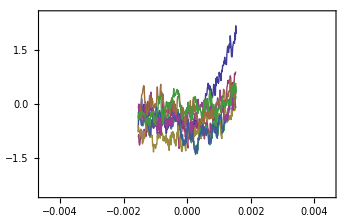

-Graphics-

```mathematica
avgdDatasetsOverDomain[functions_]:=Module[
{functionList=functions},

resampledFuncts=Quiet[manyFunctionsOverIntersectingDomainsResampledToCommonCoords[functionList]];

numDomains=Length[resampledFuncts];

avgdFuncts=Table[
avgOfDatasetsOverCommonRange[resampledFuncts[[dm]]],
{dm,1,numDomains}];

Return[
avgdFuncts
]
];

(*  this one attempts to work with the resampling and joining function from the section above *)
avgdDatasetsOverDomainAngle[functions_]:=Module[
{functionList=functions},

resampledFuncts=manyFunctionsOverIntersectingDomainsResampledToCommonCoordsAngleTesting[functionList];

numDomains=Length[resampledFuncts];

avgdFuncts=Table[
avgOfDatasetsOverCommonRange[resampledFuncts[[dm]]],
{dm,1,numDomains}];

Return[
avgdFuncts
]
];

(* I don't remember what this was for, except maybe to specify a coordinate range over which to resample *)
avgdDatasetsOverDomainWithCoords[functions_,incr_]:=Module[
{functionList=functions,
idealIncr=incr},

resampledFuncts=Quiet[manyFunctionsOverIntersectingDomainsResampledToCommonCoordsWithCoords[functionList,idealIncr]];

numDomains=Length[resampledFuncts];

avgdFuncts=Table[
avgOfDatasetsOverCommonRange[resampledFuncts[[dm]]],
{dm,1,numDomains}];

Return[
avgdFuncts
]
];

avgdSingleDatasetFromMultipleDatasetsOverDomains[datasets_]:=Flatten[avgdDatasetsOverDomain[datasets],1];

avgdSingleDatasetFromMultipleDatasetsOverDomainsWithCoords[datasets_,coords_]:=Flatten[avgdDatasetsOverDomainWithCoords[datasets,coords],1];

offsetFunctions[functions_,offsetBy_]:=Module[
{functs=functions,
shift=offsetBy},
numFunctions=Length[functs];
Table[
addOffsetForPlotting[functs[[n]],n*shift],
{n,1,numFunctions}]
];
```

```mathematica
firstIterationResidAsFunctFit[measurement_,surface_]:=Module[
{msrmnt=measurement,
surf=surface},

dataStepSz=Mean[{
avgStepSize[msrmnt],
avgStepSize[surf]
}];
parsePad=dataStepSz/2;

commLow=First[commonDomainOfFuncts[msrmnt,surf]];
commHigh=Last[commonDomainOfFuncts[msrmnt,surf]];

msrmntCommDomain=parseDataToDomainLowHighOrHighLow[msrmnt,commLow-parsePad,commHigh+parsePad];
surfaceCommDomain=parseDataToDomainLowHighOrHighLow[surf,commLow-parsePad,commHigh+parsePad];

fitOfSurf=polynomialFit[surfaceCommDomain,1];
measMinusSurfVect=dependentVectorOfFunction[
detrendDatasetAndScale[
difference[
msrmntCommDomain,
surfaceCommDomain
],
0,1]
];

measSurfDiff=Thread[{fitOfSurf,measMinusSurfVect}];

Return[
measSurfDiff
]

];
```

## Display Functions

### plot Modules for GUI

```mathematica
sigFigs=4;
fontSizes=12;




plotDatasetsToSpecification[fncts_,directory_,trace_,dataCol_,dataType_,independentVariable_,parseQ_,initDataPoint_,finalDataPoint_,
graphFrom_,graphTo_,low_,high_,gridSpacing_,(*
scaleFactor_,detrndPolyOrd_,smoothPointsQ_,smoothingOutlierSigmaFactor_,*)
legendPosition_,offsetForPlotting_,color_,imgSz_,fntSz_,bottomChartLabelQ_,saveGraph_]:=
Module[
{functions=fncts,
dirs=directory,
trcs=trace,
dataColumns=dataCol,
dataTs=dataType,
independentVars=independentVariable,
trimQs=parseQ,
initPoints=initDataPoint,
finalPoints=finalDataPoint,
plotFroms=graphFrom,
plotTos=graphTo,
lowRanges=low,
highRanges=high,
grdSpace=gridSpacing,(*
scales=scaleFactor,
detrndPolyOrders=detrndPolyOrd,
smoothQ=smoothPointsQ,
sigmaThreshold=smoothingOutlierSigmaFactor, *)
legendPlacemets=legendPosition,
offset=offsetForPlotting,
plotColors=color,
imgS=imgSz,
fntS=fntSz,
chartLabels=bottomChartLabelQ,
saveGraphQ=saveGraph},

trends=Table[
Flatten[dependentVectorOfFunction[
functions[[n]]
]],{n,1,Length[functions]}];
(*
pltRanges=If[trimQs==1,
All,
{{initPoints,finalPoints},{lowRanges,highRanges}}];
*)
(* pltRanges=
If[trimQs==1(* &&dataT≠"PSD" *) ,
All,
If[trimQs==2&&ToString[dataT]=="PSD",
{{Automatic,Automatic},{lowRanges,highRanges}},
{{initPoints,finalPoints},{lowRanges,highRanges}}]]; *)
pltRanges=
If[ToString[trimQs]=="1"||ToString[trimQs]=="False"(* &&dataT≠"PSD" *) ,
All,
{{plotFroms,plotTos},{lowRanges,highRanges}}];

statusDescs=Table["Meas. Run "<>ToString[dirs[[n]]]<>
If[ToString[trcs[[n]]]=="avg",
", average of "<>ToString[numTracesInRunDirTrc[dirs[[n]]]]<>" traces",
If[independentVars=="time",
"",
", trace "<>ToString[trcs[[n]]]
]],
{n,1,Length[dirs]}];

descrs=Table[
ToString[columnLabelsDirTrc[dirs[[n]],1][[dataColumns[[n]]]]],
{n,1,Length[dirs]}];

(* used in the plotting function to add description *)
legendDescriptions=Table[
If[ToString[dataTs[[n]]]=="PSD",
statusDescs[[n]]<>": PSD of "<>descrs[[n]],
If[ToString[dataTs[[n]]]=="angle",
statusDescs[[n]]<>" "<>descrs[[n]]<>":  σ= "<>ToString[NumberForm[StandardDeviation[trends[[n]]],sigFigs]]<>" μrad",
If[ToString[dataTs[[n]]]=="Temp",
statusDescs[[n]]<>" "<>descrs[[n]]<>":  "<>" ± "<>ToString[NumberForm[StandardDeviation[trends[[n]]],sigFigs]]<>" °C",
If[ToString[dataTs[[n]]]=="percent",
statusDescs[[n]]<>" "<>descrs[[n]]<>":  "<>" ± "<>ToString[NumberForm[StandardDeviation[trends[[n]]],sigFigs]]<>" %"
]]]],
{n,1,Length[functions]}];

frameTick[indepVar_,dataOfType_]:=
If[ToString[indepVar]=="time",
If[ToString[dataOfType]=="PSD",
{{None,None},{pTicksTesting,None}},
{{Automatic,Automatic},{hoursInADayTicksSpacedAt[grdSpace],None}}
],
Automatic];

gridLinesM=
If[ToString[independentVars]=="time",
If[ToString[dataTs[[1]]]=="PSD",
{periodGridPoints,None},
{independentVectorOfFunction[hoursInADayTicksSpacedAt[grdSpace]],None}],
None];

lftAxisLabels=ToString[dataTs[[1]]]<>" "<>
If[ToString[dataTs[[1]]]=="angle",
" (μrad)",
If[ToString[dataTs[[1]]]=="Temp",
" fluctuations (°C)",
If[ToString[dataTs[[1]]]=="percent",
" fluctuation",
""]]];
rghtAxisLabels=None;
frameLabels=
{{lftAxisLabels,
rghtAxisLabels},
{If[chartLabels,
If[ToString[dataTs[[1]]]=="PSD"&&ToString[independentVars]=="time","Period of Oscillation",
If[ToString[dataTs[[1]]]=="PSD"&&ToString[independentVars]=="position",
"Spatial Frequency",
If[ToString[dataTs[[1]]]!="PSD"&&ToString[independentVars]=="time",
"Time of Day (24 hr)",
"tangential position (mm)"
]]],
None],
None}};

(* This function is what plots the data *)
plotIt=If[ToString[dataTs[[1]]]=="PSD"&&ToString[independentVars]=="time",ToExpression["ListLogLinearPlot"],
ToExpression["ListLinePlot"]][
offsetFunctions[functions,offset],
Joined->True,
PlotRange->pltRanges,
PlotStyle-> plotColors,
PlotLegends->
Placed[
LineLegend[
{legendDescriptions},
LegendFunction->"Frame",
LegendLabel->None (*ToString[statusDescs] *),
LabelStyle->FontSize->fntS,
Background->White,
LegendLayout->"Column"   ],
legendPlacemets],
LabelStyle->Directive[fntS,FontFamily->"Helvetica"],
Frame->True,
FrameTicks-> frameTick[independentVars,dataTs[[1]]],
FrameLabel->frameLabels,
GridLines->gridLinesM,
GridLinesStyle->{Thin,LightGray},
Axes->False,
ImageSize->imgS,AspectRatio->.45,ImagePadding->All
];

If[saveGraphQ,
Export["AssociatedFiles\\Graphs\\"<>ToString[statusDescs[[1]]]<>ToString[dataTs[[1]]]<>".pdf",plotIt];
plotIt,
plotIt
]
];
```

```mathematica
sigFigs=4;
fontSize=12;

plotModuleUsingDataTableAdjImgSizeWithDataSmoothingOption[directory_,trace_,dataCol_,
dataType_,independentVariable_,
parseQ_,initDataPoint_,finalDataPoint_,displayFrom_,displayTo_,low_,high_,gridSpacing_,
scaleFactor_,detrndPolyOrd_,smoothQ_,smoothingOutlierSigmaFactor_,
legendPosition_,color_,bottomLabel_,imgSz_,fntSize_,saveQ_]:=
Module[
{dir=directory,
trc=trace,
dataColumnSelection=dataCol,
dataT=dataType,
independentVar=independentVariable,
trimQ=parseQ,
initPoint=initDataPoint,
finalPoint=finalDataPoint,
plotFrom=displayFrom,
plotTo=displayTo,
lowRange=low,
highRange=high,
gridSpace=gridSpacing,
scale=scaleFactor,
detrndPolyOrder=detrndPolyOrd,
smoothDatasetQ=smoothQ,
outlierSigma=smoothingOutlierSigmaFactor,
legendPlacemet=legendPosition,
plotColor=color,
chartLabel=bottomLabel,
imgSize=imgSz,
fontSize=fntSize,
saveG=saveQ},

baseFunction=(* conditional to distinguish stability scans from trranslational scans *)
If[ToString[independentVar]=="time",
joinMultipleTracesInTime[dir,dataColumnSelection],
If[ToString[independentVar]=="position" &&ToString[trc]≠"avg",
Thread[{
tanScanCoordCentered[dir,trc],
dataFromColumnFunctPosition[dir,trc,dataColumnSelection]
}]  ,
  If[ToString[independentVar]=="position"&&ToString[trc]=="avg",
averageOfTracesFunctPosition[dir,dataColumnSelection]
]] ];

parsedFunct=
parseDataToDomain[
baseFunction,
If[ToString[trimQ]=="1"||ToString[trimQ]=="False","Full",initPoint],
If[ToString[trimQ]=="1"||ToString[trimQ]=="False","Full",finalPoint]];

parsedFunction=If[smoothDatasetQ,
smoothDataset[parsedFunct,outlierSigma],
parsedFunct];

function=
If[ToString[dataT]=="PSD",
psdOfFunct[
detrendDatasetAndScale[
parsedFunction,
detrndPolyOrder,scale]],
detrendDatasetAndScale[
parsedFunction,
detrndPolyOrder,scale]
];

baseTrend=dependentVectorOfFunction[parsedFunction];
trend=dependentVectorOfFunction[detrendDatasetAndScale[parsedFunction,detrndPolyOrder,scale]];
(*
pltRange=If[trimQ==1,
All,
{{initPoint,finalPoint},{lowRange,highRange}}];
*)
(*  pltRange=
If[trimQ==1(* &&dataT≠"PSD" *) ,
All,
If[trimQ==2&&ToString[dataT]=="PSD",
{{Automatic,Automatic},{lowRange,highRange}},
{{plotFrom,plotTo},{lowRange,highRange}}]];   *)
pltRange=
If[ToString[trimQ]=="1"||ToString[trimQ]=="False"(* &&dataT≠"PSD" *) ,
All,
{{plotFrom,plotTo},{lowRange,highRange}}];

statusDesc="Meas. run "<>ToString[dir]<>
If[ToString[trc]=="avg",
", average of "<>ToString[numTracesInRun[dir]]<>" scans",
If[independentVar=="time",
"",
", scan "<>ToString[trc]
]];

descr=ToString[columnLabelsDirTrc[dir,1][[dataColumnSelection]]];

(* used in the plotting function to add description *)
legendDescription=
If[ToString[dataT]=="PSD",
"PSD of "<>descr,
If[ToString[dataT]=="none",
descr,
If[ToString[dataT]=="angle",
descr<>":  σ= "<>ToString[NumberForm[StandardDeviation[trend],sigFigs]]<>" μrad",
If[ToString[dataT]=="Temp",
descr<>":  "<>ToString[NumberForm[Mean[baseTrend],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trend],sigFigs]]<>" °C",
If[ToString[dataT]=="arbitrary",
descr<>":  "<>ToString[NumberForm[Mean[baseTrend],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trend],sigFigs]]<>" arb. units",
If[ToString[dataT]=="percent",
descr<>":  "<>ToString[NumberForm[Mean[baseTrend],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trend],sigFigs]]<>" %"
]]]]]];

frameTicks=
If[ToString[independentVar]=="time",
If[ToString[dataT]=="PSD",
{{None,None},{pTicksTesting,None}},
{{Automatic,Automatic},{hoursInADayTicksSpacedAt[gridSpace],None}}
],
Automatic];

gridLines=
If[ToString[independentVar]=="time",
If[ToString[dataT]=="PSD",
{periodGridPoints,None},
{independentVectorOfFunction[hoursInADayTicksSpacedAt[gridSpace]],None}],
None];

lftAxisLabel=
If[ToString[dataT]=="none",None,
ToString[dataT]<>
If[ToString[dataT]=="angle",
" (μrad)",
If[ToString[dataT]=="Temp",
" fluctuations (°C)",
If[ToString[dataT]=="percent",
" fluctuation",
""]]]];
rghtAxisLabel=None;
frameLabel=
{{lftAxisLabel,
rghtAxisLabel},
{If[chartLabel,
If[ToString[dataT]=="PSD"&&ToString[independentVar]=="time","Period of Oscillation",
If[ToString[dataT]=="PSD"&&ToString[independentVar]=="position",
"Spatial Frequency",
If[ToString[dataT]!="PSD"&&ToString[independentVar]=="time",
"Time of Day (24 hr)",
"tangential position (mm)"
]]],
None],
None}};

(* This function is what plots the data *)
plotTheGraph=If[ToString[dataT]=="PSD"&&ToString[independentVar]=="time",
ToExpression["ListLogLinearPlot"],
ToExpression["ListLinePlot"]][
function,
Joined->True,
PlotRange->pltRange,
PlotStyle-> plotColor,
PlotLegends->
Placed[
LineLegend[
{legendDescription},
LegendFunction->"Frame",
LegendLabel->ToString[statusDesc],
LabelStyle->FontSize->fontSize,
Background->White,
LegendLayout->"Column"   ],
legendPlacemet],
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
Frame->True,
FrameTicks->frameTicks,
FrameLabel->frameLabel,
GridLines->gridLines,
GridLinesStyle->{Thin,LightGray},
Axes->False,
ImageSize->imgSize,AspectRatio->.4,ImagePadding->All
];

Return[{
If[saveG,
Export["AssociatedFiles\\Graphs\\"<>ToString[statusDesc]<>ToString[dataT]<>".pdf",plotTheGraph];
plotTheGraph,
plotTheGraph
],
function  
}]

]
```

```mathematica
sigFigs=4;
fontSizes=12;

plotModuleForMultipleDatasetsFromDataTable[directory_,trace_,dataCol_,dataType_,independentVariable_,parseQ_,initDataPoint_,finalDataPoint_,
graphFrom_,graphTo_,low_,high_,gridSpacing_,scaleFactor_,detrndPolyOrd_,
legendPosition_,offsetForPlotting_,color_,bottomChartLabelQ_,saveGraph_]:=
Module[
{dirs=directory,
trcs=trace,
dataColumns=dataCol,
dataTs=dataType,
independentVars=independentVariable,
trimQs=parseQ,
initPoints=initDataPoint,
finalPoints=finalDataPoint,
plotFroms=graphFrom,
plotTos=graphTo,
lowRanges=low,
highRanges=high,
grdSpace=gridSpacing,
scales=scaleFactor,
detrndPolyOrders=detrndPolyOrd,
legendPlacemets=legendPosition,
offset=offsetForPlotting,
plotColors=color,
chartLabels=bottomChartLabelQ,
saveGraphQ=saveGraph},

baseFunctions[scanD_,scnNum_,dataC_]:=(* conditional to distinguish stability scans from trranslational scans *)
If[ToString[independentVars]=="time",
joinMultipleTracesInTimeDirTrc[scanD,dataC],
If[ToString[independentVars]=="position" &&ToString[scnNum]≠"avg",
Thread[{
tanScanCoordCenteredDirTrc[scanD,scnNum],
dataFromColumnFunctPositionDirTrc[scanD,scnNum,dataC]
}]  ,
  If[ToString[independentVars]=="position"&&ToString[scnNum]=="avg",
averageOfTracesFunctPositionDirTrc[scanD,dataC]
] ]];

(*  parsedFunctions[scanD_,scnNum_,dataC_,scaleF_]:=
rescaleDataset[
parseDataToDomain[
baseFunctions[scanD,scnNum,dataC],
If[trimQs==1,"Full",initPoints],
If[trimQs==1,"Full",finalPoints]],
scaleF];  *)
parsedFunctions[scanD_,scnNum_,dataC_]:=
parseDataToDomain[
baseFunctions[scanD,scnNum,dataC],
If[trimQs==1||trimQs==False,"Full",initPoints],
If[trimQs==1||trimQs==False,"Full",finalPoints]];

functions[scanD_,scnNum_,dataC_,scaleF_,dataT_]:=If[ToString[dataT]=="PSD",
psdOfFunct[
detrendDatasetAndScale[
parsedFunctions[scanD,scnNum,dataC],
detrndPolyOrders,scaleF]],
detrendDatasetAndScale[
parsedFunctions[scanD,scnNum,dataC],
detrndPolyOrders,scaleF]
];

(* here we will attempt to put toghter all the functions *)
functToPlot=Table[functions[dirs[[n]],trcs[[n]],dataColumns[[n]],scales[[n]],dataTs[[n]]],{n,1,Length[dirs]}];

offsetFunctions[functions_,offsetBy_]:=Module[
{functs=functions,
shift=offsetBy},
numFunctions=Length[functions];
Table[
addOffsetForPlotting[functs[[n]],n*shift],
{n,1,numFunctions}]
];

baseTrends=Table[dependentVectorOfFunction[parsedFunctions[dirs[[n]],trcs[[n]],dataColumns[[n]]]],
{n,1,Length[dirs]}];

trends=Table[dependentVectorOfFunction[
detrendDatasetAndScale[functions[dirs[[n]],trcs[[n]],dataColumns[[n]],scales[[n]],dataTs[[n]]],detrndPolyOrders,1]],{n,1,Length[dirs]}];
(*
pltRanges=If[trimQs==1,
All,
{{initPoints,finalPoints},{lowRanges,highRanges}}];
*)
(* pltRanges=
If[trimQs==1(* &&dataT≠"PSD" *) ,
All,
If[trimQs==2&&ToString[dataT]=="PSD",
{{Automatic,Automatic},{lowRanges,highRanges}},
{{initPoints,finalPoints},{lowRanges,highRanges}}]]; *)
pltRanges=
If[ToString[trimQs]=="1"||ToString[trimQs]=="False"(* &&dataT≠"PSD" *) ,
All,
{{plotFroms,plotTos},{lowRanges,highRanges}}];

statusDescs=Table["Meas. Run "<>ToString[dirs[[n]]]<>
If[ToString[trcs[[n]]]=="avg",
", average of "<>ToString[numTracesInRunDirTrc[dirs[[n]]]]<>" traces",
If[independentVars=="time",
"",
", trace "<>ToString[trcs[[n]]]
]],
{n,1,Length[dirs]}];

descrs=Table[
ToString[columnLabelsDirTrc[dirs[[n]],1][[dataColumns[[n]]]]],
{n,1,Length[dirs]}];

(* used in the plotting function to add description *)
legendDescriptions=Table[
If[ToString[dataTs[[n]]]=="PSD",
statusDescs[[n]]<>": PSD of "<>descrs[[n]],
If[ToString[dataTs[[n]]]=="angle",
statusDescs[[n]]<>" "<>descrs[[n]]<>":  σ= "<>ToString[NumberForm[StandardDeviation[trends[[n]]],sigFigs]]<>" μrad",
If[ToString[dataTs[[n]]]=="Temp",
statusDescs[[n]]<>" "<>descrs[[n]]<>":  "<>ToString[NumberForm[Mean[baseTrends[[n]]],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trends[[n]]],sigFigs]]<>" °C",
If[ToString[dataTs[[n]]]=="percent",
statusDescs[[n]]<>" "<>descrs[[n]]<>":  "<>ToString[NumberForm[Mean[baseTrends[[n]]],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trends[[n]]],sigFigs]]<>" %"
]]]],
{n,1,Length[dirs]}];

frameTick[indepVar_,dataOfType_]:=
If[ToString[indepVar]=="time",
If[ToString[dataOfType]=="PSD",
{{Automatic,None},{pTicksTesting,None}},
{{Automatic,Automatic},{hoursInADayTicksSpacedAt[grdSpace],None}}
],
Automatic];

gridLinesM=
If[ToString[independentVars]=="time",
If[ToString[dataTs[[1]]]=="PSD",
{periodGridPoints,None},
{independentVectorOfFunction[hoursInADayTicksSpacedAt[grdSpace]],None}],
None];

lftAxisLabels=ToString[dataTs[[1]]]<>
If[ToString[dataTs[[1]]]=="angle",
" (μrad)",
If[ToString[dataTs[[1]]]=="Temp",
" fluctuations (°C)",
If[ToString[dataTs[[1]]]=="percent",
" fluctuation",
""]]];
rghtAxisLabels=None;
frameLabels=
{{lftAxisLabels,
rghtAxisLabels},
{If[chartLabels,
If[ToString[dataTs[[1]]]=="PSD"&&ToString[independentVars]=="time","Period of Oscillation",
If[ToString[dataTs[[1]]]=="PSD"&&ToString[independentVars]=="position",
"Spatial Frequency",
If[ToString[dataTs[[1]]]!="PSD"&&ToString[independentVars]=="time",
"Time of Day (24 hr)",
"tangential position (mm)"
]]],
None],
None}};

(* This function is what plots the data *)
plotIt=If[ToString[dataTs[[1]]]=="PSD"&&ToString[independentVars]=="time",ToExpression["ListLogLinearPlot"],
ToExpression["ListLinePlot"]][
offsetFunctions[functToPlot,offset],
Joined->True,
PlotRange->pltRanges,
PlotStyle-> plotColors,
PlotLegends->
Placed[
LineLegend[
{legendDescriptions},
LegendFunction->"Frame",
LegendLabel->None (*ToString[statusDescs] *),
LabelStyle->FontSize->fontSizes,
Background->White,
LegendLayout->"Column"   ],
legendPlacemets],
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
Frame->True,
FrameTicks-> frameTick[independentVars,dataTs[[1]]],
FrameLabel->frameLabels,
GridLines->gridLinesM,
GridLinesStyle->{Thin,LightGray},
Axes->False,
ImageSize->500,AspectRatio->.45,ImagePadding->All
];

If[saveGraphQ,
Export["AssociatedFiles\\Graphs\\"<>ToString[statusDescs[[1]]]<>ToString[dataTs[[1]]]<>".jpg",plotIt];
plotIt,
plotIt
]
];
```

### For inspecting a stage stability

#### getting data

```mathematica
tripodPlatformRadius=6.5*25.4;
(* parses the forward (up) and backward (down) scans from a run *)
(* for the lateral *)
scansToPlotLateral[runNum_,numTraces_] :=Table[lateralDependenceMicrons[runNum,traceNumber],{traceNumber,1,numTraces}];
detrendedScansToPlotLateral[runNum_,numTraces_] :=Table[detrendedDataset[lateralDependenceMicrons[runNum,traceNumber],1],{traceNumber,1,numTraces}];
(* and for the vertical *)
scansToPlotVert[runNum_,numTraces_] :=Table[vertDeviationMicrons[runNum,traceNumber],{traceNumber,1,numTraces}];
detrendedScansToPlotVert[runNum_,numTraces_] :=Table[detrendedDataset[vertDeviationMicrons[runNum,traceNumber],1],{traceNumber,1,numTraces}];
(* for the AC X andgle *)
scansToPlotAngleX[runNum_,numTraces_]:= Table[angleXFunctHeight[runNum,traceNumber],{traceNumber,1,numTraces}];
detrendedScansToPlotAngleX[runNum_,numTraces_]:= Table[detrendedDataset[angleXFunctHeight[runNum,traceNumber],1],{traceNumber,1,numTraces}];
(* for the AC Y angle *)
scansToPlotAngleY[runNum_,numTraces_]:= Table[angleYFunctHeight[runNum,traceNumber],{traceNumber,1,numTraces}];
detrendedScansToPlotAngleY[runNum_,numTraces_]:= Table[detrendedDataset[angleYFunctHeight[runNum,traceNumber],1],{traceNumber,1,numTraces}];
(* for a 3d representation of angle *)
ang3d[runNum_,numTraces_]:=Table[
Thread[{
independentVectorOfFunction[detrendedScansToPlotAngleX[runNum,numTraces][[traceNumber]]],
dependentVectorOfFunction[detrendedScansToPlotAngleX[runNum,numTraces][[traceNumber]]],
dependentVectorOfFunction[detrendedScansToPlotAngleY[runNum,numTraces][[traceNumber]]]}],
{traceNumber,1,numTraces}];

upAng3d[runNum_,numTraces_]:=Table[
Thread[{
independentVectorOfFunction[detrendedScansToPlotAngleX[runNum,numTraces][[trace]]],
dependentVectorOfFunction[detrendedScansToPlotAngleX[runNum,numTraces][[trace]]],
dependentVectorOfFunction[detrendedScansToPlotAngleY[runNum,numTraces][[trace]]]}],
{trace,fScans8}];


(* determines the coefficient of the angular dependance: the angle of the stage *)
fitFnctnAlignment[dataset_]:=Fit[rescaleDataset[dataset,10^(-3)],{1,x},x];
fitCoeff[dataset_] :=First[Drop[fitFnctnAlignment[dataset],1]];(* since the dataset is in terms of microns as a functino of mm, this converts the microns to mm  *)
radToDeg[radians_]:=radians*180/Pi;
theta[dataset_] :=ArcTan[fitCoeff[dataset]];

deltaHeight[dataset_] := tripodPlatformRadius*(-Sin[theta[dataset]]);
action[dataset_]:= Print["Adjust left micrometer by "<>ToString[NumberForm[deltaHeight[dataset],4]]<> " mm to correct for an angle of "<>ToString[NumberForm[theta[dataset]*10^(3),4]]<>" mrad"];

(* creates a 2D array of the residual function after the fit has been subtracted *) (* this is not finished *)
fitResidual[dataset_]:=detrendedDataset[dataset,1];
fitUncertainty[dataset_]:=StandardDeviation[fitResidual[dataset]];
(* **************************************************************** *)(* **************************************************************** *)(* **************************************************************** *)(* **************************************************************** *)
(* records the parsed forward and backward scan  *)
upwardPoints[runNum_,numTraces_]:=Table[dependentVectorOfFunction[detrendedVertDeviationMicrons[runNum,n]],{n,fScanSequence[numTraces]}];
upwardCoordinates[runNum_,numTraces_]:= Table[independentVectorOfFunction[detrendedVertDeviationMicrons[runNum,n]],{n,fScanSequence[numTraces]}];
downwardPoints[runNum_,numTraces_]:=Table[dependentVectorOfFunction[detrendedVertDeviationMicrons[runNum,n]],{n,bScanSequence[numTraces]}];
downwardCoordinates[runNum_,numTraces_]:= Table[independentVectorOfFunction[detrendedVertDeviationMicrons[runNum,n]],{n,bScanSequence[numTraces]}];

(* records the parsed forward adn backward of the lateral dependence scan *)
forwardPoints[runNum_,numTraces_]:=Table[dependentVectorOfFunction[lateralDependenceMicrons[runNum,n]],{n,fScanSequence[numTraces]}];
forwardCoordinates[runNum_,numTraces_]:= Table[independentVectorOfFunction[lateralDependenceMicrons[runNum,n]],{n,fScanSequence[numTraces]}];
backwardPoints[runNum_,numTraces_]:=Table[dependentVectorOfFunction[lateralDependenceMicrons[runNum,n]],{n,bScanSequence[numTraces]}];
backwardCoordinates[runNum_,numTraces_]:= Table[independentVectorOfFunction[lateralDependenceMicrons[runNum,n]],{n,bScanSequence[numTraces]}];

angleXPointsUpward[runNum_,numTraces_]:= Table[dependentVectorOfFunction[angleXFunctHeight[runNum,n]],{n,fScanSequence[numTraces]}];
angleXCoordinatesUpward[runNum_,numTraces_]:= Table[independentVectorOfFunction[angleXFunctHeight[runNum,n]],{n,fScanSequence[numTraces]}];
angleXPointsDownward[runNum_,numTraces_]:= Table[dependentVectorOfFunction[angleXFunctHeight[runNum,n]],{n,bScanSequence[numTraces]}];
angleXCoordinatesDownward[runNum_,numTraces_]:= Table[independentVectorOfFunction[angleXFunctHeight[runNum,n]],{n,bScanSequence[numTraces]}];
 
angleYPointsUpward[runNum_,numTraces_]:= Table[dependentVectorOfFunction[angleYFunctHeight[runNum,n]],{n,fScanSequence[numTraces]}];
angleYCoordinatesUpward[runNum_,numTraces_]:= Table[independentVectorOfFunction[angleYFunctHeight[runNum,n]],{n,fScanSequence[numTraces]}];
angleYPointsDownward[runNum_,numTraces_]:= Table[dependentVectorOfFunction[angleYFunctHeight[runNum,n]],{n,bScanSequence[numTraces]}];
angleYCoordinatesDownward[runNum_,numTraces_]:= Table[independentVectorOfFunction[angleYFunctHeight[runNum,n]],{n,bScanSequence[numTraces]}];

(* a work in progeress as an attempt the simplify the redundancy abaove and below *)
(* an attempt to make the above simplify into functiona form *)
forwardPointsOfFunction[runNum_,numTraces_]:=Table[dependentVectorOfFunction[lateralDependenceMicrons[runNum,n]],{n,fScanSequence[numTraces]}];
forwardCoordinatesOfFunction[runNum_,numTraces_]:= Table[independentVectorOfFunction[lateralDependenceMicrons[runNum,n]],{n,fScanSequence[numTraces]}];
backwardPointsOfFunction[runNum_,numTraces_]:=Table[dependentVectorOfFunction[lateralDependenceMicrons[runNum,n]],{n,bScanSequence[numTraces]}];
backwardCoordinatesOfFunction[runNum_,numTraces_]:= Table[independentVectorOfFunction[lateralDependenceMicrons[runNum,n]],{n,bScanSequence[numTraces]}];
(*  above 4 lines are not used at this point *)
(* **************************************************************** *)(* **************************************************************** *)(* **************************************************************** *)(* **************************************************************** *)
(* these are functions of the average forward and average backward traces *)
(* for vertical DMI scans *)
meanUpwardFunction[runNum_,numTraces_]:=Thread[{Mean[upwardCoordinates[runNum,numTraces]],Mean[upwardPoints[runNum,numTraces]]}];
meanDownwardFunction[runNum_,numTraces_]:=Thread[{Mean[downwardCoordinates[runNum,numTraces]],Mean[downwardPoints[runNum,numTraces]]}];
(* for lateral DMI scans *)
meanForwardFunctionLateral[runNum_,numTraces_]:=Thread[{Mean[forwardCoordinates[runNum,numTraces]],Mean[forwardPoints[runNum,numTraces]]}];
meanBackwardFunctionLateral[runNum_,numTraces_]:=Thread[{Mean[backwardCoordinates[runNum,numTraces]],Mean[backwardPoints[runNum,numTraces]]}];
(* for AC X angle scans *)
meanAngXUpwardFunction[runNum_,numTraces_]:=Thread[{Mean[angleXCoordinatesUpward[runNum,numTraces]],Mean[angleXPointsUpward[runNum,numTraces]]}];
meanAngXDownwardFunction[runNum_,numTraces_]:=Thread[{Mean[angleXCoordinatesDownward[runNum,numTraces]],Mean[angleXPointsDownward[runNum,numTraces]]}];
(* for AC Y angle scans *)
meanAngYUpwardFunction[runNum_,numTraces_]:=Thread[{Mean[angleYCoordinatesUpward[runNum,numTraces]],Mean[angleYPointsUpward[runNum,numTraces]]}];
meanAngYDownwardFunction[runNum_,numTraces_]:=Thread[{Mean[angleYCoordinatesDownward[runNum,numTraces]],Mean[angleYPointsDownward[runNum,numTraces]]}];

(* 3 Dimensional mean functions here *)
angle3dMeanUpward[runNum_,numTraces_] := Thread[{
independentVectorOfFunction[meanAngXUpwardFunction[runNum,numTraces]],
dependentVectorOfFunction[detrendedDataset[meanAngXUpwardFunction[runNum,numTraces],1]],
dependentVectorOfFunction[detrendedDataset[meanAngYUpwardFunction[runNum,numTraces],1] ]}];

angle3dMeanDownward[runNum_,numTraces_] := Thread[{
independentVectorOfFunction[meanAngXDownwardFunction[runNum,numTraces]],
dependentVectorOfFunction[detrendedDataset[meanAngXDownwardFunction[runNum,numTraces],1]],
dependentVectorOfFunction[detrendedDataset[meanAngYDownwardFunction[runNum,numTraces],1] ]}];
(* **************************************************************** *)(* **************************************************************** *)(* **************************************************************** *)(* **************************************************************** *)
(* calculations of the uncertainties here *)
forwardSigma[runNum_,numTraces_]:= StandardDeviation[dependentVectorOfFunction[meanForwardFunctionLateral[runNum,numTraces]]];
backwardSigma[runNum_,numTraces_]:= StandardDeviation[dependentVectorOfFunction[meanBackwardFunctionLateral[runNum,numTraces]]];

forwardSigmaDtrndData[runNum_,numTraces_]:= StandardDeviation[dependentVectorOfFunction[detrendedDataset[meanForwardFunctionLateral[runNum,numTraces],1]]];
backwardSigmaDtrndData[runNum_,numTraces_]:= StandardDeviation[dependentVectorOfFunction[detrendedDataset[meanBackwardFunctionLateral[runNum,numTraces],1]]];

upSigmaDtrndData[runNum_,numTraces_]:=StandardDeviation[dependentVectorOfFunction[detrendedDataset[meanUpwardFunction[runNum,numTraces],1]]];
downSigmaDtrndData[runNum_,numTraces_]:=StandardDeviation[dependentVectorOfFunction[detrendedDataset[meanDownwardFunction[runNum,numTraces],1]]];

angleXupSigmaDtrndData[runNum_,numTraces_]:=StandardDeviation[dependentVectorOfFunction[detrendedDataset[meanAngXUpwardFunction[runNum,numTraces],1]]];
angleXdownSigmaDtrndData[runNum_,numTraces_]:=StandardDeviation[dependentVectorOfFunction[detrendedDataset[meanAngXDownwardFunction[runNum,numTraces],1]]];

angleYupSigmaDtrndData[runNum_,numTraces_]:=StandardDeviation[dependentVectorOfFunction[detrendedDataset[meanAngYUpwardFunction[runNum,numTraces],1]]];
angleYdownSigmaDtrndData[runNum_,numTraces_]:=StandardDeviation[dependentVectorOfFunction[detrendedDataset[meanAngYDownwardFunction[runNum,numTraces],1]]];
(* **************************************************************** *)(* **************************************************************** *)(* **************************************************************** *)(* **************************************************************** *)
(* assumes the same coordinate domain *)

(* a measure of how different two functions are *)
rmsDifference[funct1_,funct2_]:=StandardDeviation[dependentVectorOfFunction[difference[funct1,funct2]]];
```

#### Display styling

```mathematica
rescaleForPlotting[function_,scaleFactor_]:= 
Thread[{
independentVectorOfFunction[function],
dependentVectorOfFunction[function]*scaleFactor
}];

(* Just spells out a vector of values for positioning gridlines of a chart *)
halfStep = Table[step/2,{step,-1000,1000}];

(* This is used by the PlotStyle parameter to give gradient colors of blue hues for up scans and red hues for down scans  *)
fHue[n_]:= Hue[.65-((n-1)*.025)];
rHue[n_]:= Hue[1-((n-1)*.025)];
(* This takes the hue valeus above and uses them to style the plot so that consecutigne traces can be distinguished *)
colorCodeGradient[numberOfTraces_] :=Table[If[direction[n]=="F",{Thick,fHue[n]},{Thick,rHue[n]}],{n,1,numberOfTraces}] ;
colorCodeLinesGradient[numberOfTraces_] :=Table[If[direction[n]=="F",{ fHue[n]},{rHue[n]}],{n,1,numberOfTraces}] ;
colorCodeDotsGradient[numberOfTraces_] :=Table[If[direction[n]=="F",{ fHue[n],PointSize[Medium]},{rHue[n],PointSize[Medium]}],{n,1,numberOfTraces}] ;
```

#### some plotting

```mathematica
imgSize = 375;

horizontalAxisGrid=Table[v,{v,-2,12}];
verticalAxisGrid=Table[5*h,{h,-10,10}];
verticalAxisGridAngle=Table[25*h,{h,-10,10}];


wobblePlot[runNum_,dataset_]:=
ListLinePlot[dataset,
PlotRange->{Automatic,Automatic } ,
PlotStyle->{{Thick,Darker[Darker[Blue]]},{Thick,Dashed,Darker[Red]}},
Axes->False,
Frame-> True,
FrameLabel->{{"Lateral Position, μm",None},{ "Vertical Position, mm",None}},
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
PlotLegends-> Placed[{Text[Style[ToString[upward],fontSize]],Text[Style[ToString[downward],fontSize]]},{Right,Bottom}], 
ImageSize->imgSize,
AspectRatio->.55
];

howToAlignApparatus[runNum_,numTraces_]:= {wobblePlot[runNum,meanBackwardFunctionLateral[runNum,numTraces]], action[meanBackwardFunctionLateral[runNum,numTraces]],Graphics[Text["run # "<>ToString[runNum]]]};

legendFunctionOfScan[scanType_,runNum_,numTraces_]:=Placed[LineLegend[
{Text[Style["upward scans"<>If[ToString[scanType]=="raw",""," σ = "<>ToString[NumberForm[
If[ToString[scanType]== "lat",forwardSigmaDtrndData[runNum,numTraces],
If[ToString[scanType] == "vert", upSigmaDtrndData[runNum,numTraces],
If[ToString[scanType]=="angX",angleXupSigmaDtrndData[runNum,numTraces],
If[ToString[scanType]=="angY",angleYupSigmaDtrndData[runNum,numTraces]]]]],
3]]<>" μm"],fontSize]],
Text[Style["downward scans"<>If[ToString[scanType]=="raw",""," σ = "<>ToString[NumberForm[
If[ToString[scanType]== "lat",backwardSigmaDtrndData[runNum,numTraces],
If[ToString[scanType] == "vert", downSigmaDtrndData[runNum ,numTraces],
If[ToString[scanType]=="angX",angleXdownSigmaDtrndData[runNum,numTraces],
If[ToString[scanType]=="angY",angleYdownSigmaDtrndData[runNum,numTraces]]]]],
3]]<>" μm"],fontSize]]}],
If[ToString[scanType]=="vert" || ToString[scanType]=="raw",{Right,Bottom},{Right,Top}]];

(*  this one may be all that is needed *)
deviationPlot[runNum_,numTraces_,dataset_,vertAxisDescription_,plotRange_,scanType_,vertAxisGrid_]:=
Show[
ListLinePlot[
dataset,
PlotRange->plotRange,
PlotStyle->colorCodeLinesGradient[numTraces],
GridLines->{horizontalAxisGrid,vertAxisGrid},
GridLinesStyle->Directive[Gray],
Axes->False,
Frame-> True,
FrameTicks-> {{vertAxisGrid,None},{horizontalAxisGrid,None}},
FrameLabel->{{ToString[vertAxisDescription],None},{(* "Vertical Position, mm" *)None,None}},
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
PlotLegends-> legendFunctionOfScan[scanType,runNum,numTraces], 
ImageSize->imgSize,
AspectRatio->.55
],
ListPlot[
dataset,
PlotStyle->colorCodeDotsGradient[numTraces]
]
];

(*  this one may be all that is needed *)
deviationPlotWithAxisLabel[runNum_,numTraces_,dataset_,horizAxisDesc_,vertAxisDescription_,plotRange_,scanType_,vertAxisGrid_]:=
Show[
ListLinePlot[
dataset,
PlotRange->plotRange,
PlotStyle->colorCodeLinesGradient[numTraces],
GridLines->{horizontalAxisGrid,vertAxisGrid},
GridLinesStyle->Directive[Gray],
Axes->False,
Frame-> True,
FrameTicks-> {{vertAxisGrid,None},{horizontalAxisGrid,None}},
FrameLabel->{{ToString[vertAxisDescription],None},{If[ToString[horizAxisDesc]=="None",None,ToString[horizAxisDesc]],None}},
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
PlotLegends-> legendFunctionOfScan[scanType,runNum,numTraces], 
ImageSize->imgSize,
AspectRatio->.55
],
ListPlot[
dataset,
PlotStyle->colorCodeDotsGradient[numTraces]
]
];

(*  this one may be all that is needed *)
dataPlot[data_,numDatasets_,plotRange_,vertAxisDescription_,horixAxisDescription_]:=
Show[
ListLinePlot[
data,
PlotRange->plotRange,
PlotStyle->colorCodeLinesGradient[numDatasets],
GridLines->{horizontalAxisGrid,verticalAxisGrid},
GridLinesStyle->Directive[Gray],
Axes->False,
Frame-> True,
FrameTicks-> {{N[verticalAxisGrid/10],None},{horizontalAxisGrid,None}},
FrameLabel->{{ToString[vertAxisDescription],None},{ToString[horixAxisDescription],None}},
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
PlotLegends-> Placed[{Text[Style["upward scans, σ = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[data[[1]]]],{7,3}]]<>" μm",fontSize]],Text[Style["downward scans, σ = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[data[[2]]]],{7,3}]]<>" μm",fontSize]]},{Right,Bottom}], 
ImageSize->imgSize,
AspectRatio->.55
],
ListPlot[
data,
PlotRange->{{0,10},Automatic} ,
PlotStyle->colorCodeDotsGradient[numDatasets]
]
];

 (* The following two are for plotting the 3-Dimensional angle function of stage height *)
(* This one is general, and plots all N traces of a run *)
angle3dPlot[runNum_,numTraces_]:=ListPointPlot3D[
ang3d[runNum,numTraces],
PlotStyle->colorCodeDotsGradient[numTraces],
PlotRange->{{0,10},{-100,100},{-100,100}},
BoxRatios->{1,.5,.5}
]
(* This one only plots the forward traces *)
upAngle3dPlot[runNum_,numTraces_]:=ListPointPlot3D[
ang3d[runNum,numTraces][[fScans8]],
PlotStyle->colorCodeDotsGradient[numTraces][[fScans8]],
PlotRange->{{0,10},{-100,100},{-100,100}},
BoxRatios->{1,.5,.5}
]
(* This one only plots the forward traces *)
dwAngle3dPlot[runNum_,numTraces_]:=ListPointPlot3D[
ang3d[runNum,numTraces][[bScans8]],
PlotStyle->colorCodeDotsGradient[numTraces][[bScans8]],
PlotRange->{{0,10},{-100,100},{-100,100}},
BoxRatios->{1,.5,.5}
]


(* this calls the above with the specified dataset *)
lateralDataToSendToPlotFunction[runNum_,numTraces_]:= {deviationPlot[runNum,numTraces,scansToPlotLateral[runNum,numTraces],"Lateral Wobble, μm",{{-0.25,12},{-25,25}} ,raw,verticalAxisGrid],
Graphics[Text["Run # "<>ToString[runNum]]]};
lateralDetrendedDataToSendToPlotFunction[runNum_,numTraces_]:= {deviationPlot[runNum,numTraces,detrendedScansToPlotLateral[runNum,numTraces],"Lateral Wobble, μm",{{-0.25,12},{-11,11}} ,lat,verticalAxisGrid],
Graphics[Text["Run # "<>ToString[runNum]]]};

verticalDataToSendToPlotFunction[runNum_,numTraces_]:= deviationPlot[runNum,numTraces,scansToPlotVert[runNum,numTraces],"Vertical Deviation, μm",{{-0.25,12},{-15,35}},raw ,verticalAxisGrid];
verticalDetrendedDataToSendToPlotFunction[runNum_,numTraces_]:= deviationPlot[runNum,numTraces,detrendedScansToPlotVert[runNum,numTraces],"Vertical Deviation, μm",{{-0.25,12},{-7,6}} ,vert,verticalAxisGrid];
verticalDataToSendToPlotFunction[runNum_,numTraces_,horizAxisDesc_]:= deviationPlotWithAxisLabel[runNum,numTraces,scansToPlotVert[runNum,numTraces],horizAxisDesc,"Vertical Deviation, μm",{{-0.25,12},{-15,35}},raw ,verticalAxisGrid];
verticalDetrendedDataToSendToPlotFunction[runNum_,numTraces_,horizAxisDesc_]:= deviationPlotWithAxisLabel[runNum,numTraces,detrendedScansToPlotVert[runNum,numTraces],horizAxisDesc,"Vertical Deviation, μm",{{-0.25,12},{-7,6}} ,vert,verticalAxisGrid];

runChartAndStats[runNum_,numTraces_]:={wobblePlot[runNum,{meanForwardFunctionLateral[runNum,numTraces],meanBackwardFunctionLateral[runNum,numTraces]}],
Print["upward motion lateral uncertainty = ",forwardSigma[runNum,numTraces], " μm"],
Print["downward motion lateral uncertainty = ",backwardSigma[runNum,numTraces], " μm"]};

aDataPlot[data_,numDatasets_,plotDescription_,plotRange_,vertAxisDescription_,horixAxisDescription_]:={dataPlot[data,numDatasets,plotRange,vertAxisDescription,horixAxisDescription],
Graphics[Text[ToString[plotDescription]]]};

angleXDetrendedToSendToPlotFunction[runNum_,numTraces_]:=deviationPlot[runNum,numTraces,detrendedScansToPlotAngleX[runNum,numTraces],"X angle, μrad", {{-0.25,12},{-100,100}} ,angX,verticalAxisGridAngle]
angleXDetrendedToSendToPlotFunction[runNum_,numTraces_,horizAxisDesc_]:=deviationPlotWithAxisLabel[runNum,numTraces,detrendedScansToPlotAngleX[runNum,numTraces],horizAxisDesc,"X angle, μrad", {{-0.25,12},{-100,100}} ,angX,verticalAxisGridAngle]

angleYDetrendedToSendToPlotFunction[runNum_,numTraces_]:=deviationPlot[runNum,numTraces,detrendedScansToPlotAngleY[runNum,numTraces],"Y angle, μrad", {{-0.25,12},{-100,100}} ,angY,verticalAxisGridAngle]
angleYDetrendedToSendToPlotFunction[runNum_,numTraces_,horizAxisDesc_]:=deviationPlotWithAxisLabel[runNum,numTraces,detrendedScansToPlotAngleY[runNum,numTraces],horizAxisDesc,"Y angle, μrad", {{-0.25,12},{-100,100}} ,angY,verticalAxisGridAngle]
```

#### some more plotting

```mathematica
(* **************************************************************** *)(* **************************************************************** *)
(*  the plotting function below takes in recorded data files (temp 2 and dmi) and detrend a zero order polynomial then plots the results *)
(*  functions want to be in the form of { timeCoords[directoryNum,traceNumber], dataColumn[directoryNum,traceNumber] }  *)
(* **************************************************************** *)(* **************************************************************** *)
partOf24hours[dataset_]:=Mod[Flatten[Take[dataset,All,1]],24];
dayRange[dataset_]:= IntegerPart[partOf24hours[dataset]];

hoursInADayTicks = Table[{elapsed,ToString[If[Mod[elapsed,24]==0,24,Mod[elapsed,24]]]<>":00"},{elapsed,0,96,4}];

hoursInADayTicksSpacedAt[timeStepHours_]:= Table[
{elapsed,ToString[If[Mod[elapsed,24]==0,24,Floor[Mod[elapsed,24]]]]<>If[Mod[elapsed,1]==0,":00",":"<>ToString[IntegerPart[Mod[elapsed,1]*60]]]},
{elapsed,0,720,timeStepHours}];

hoursInADayGridLines = Table[elapsed,{elapsed,0,96*12*10}];


axisLabelTemp[scaleRatio_]:=Table[{tick,ToString[NumberForm[tick/scaleRatio,{3,2}]]},{tick,-10,10,.5}];
axisLabelTempAngle[scaleRatio_]:=Table[{tick,ToString[NumberForm[tick/scaleRatio,{3,3}]]},{tick,-10,10,2.5}];


stabilityPlotWithScaledAxesLabels[statusDescription_,firstFunction_,firstFunctionDescription_,secondFunction_,secondFunctionDescription_,plotRange_,scaleFactor_,tickSpacing_,lastPlotInSeries_]:=
Show[
ListLinePlot[
{
detrendedDataset[firstFunction,0],
rescaleDataset[detrendedDataset[
secondFunction,0],scaleFactor]
},
PlotRange-> plotRange  ,
PlotStyle->{ Directive[Thick,Darker[Darker[Green]]],Directive[Thick,Darker[Red]]},
(*PlotLegends->Placed[{ToString[firstFunctionDescription],ToString[secondFunctionDescription]},{Center,Top}],*)
PlotLegends->
Placed[
LineLegend[
{ToString[firstFunctionDescription],
ToString[secondFunctionDescription]},
LegendFunction->"Frame",
LegendLabel->ToString[statusDescription],
Background->White,
LegendLayout->"Column"   ],
{Right,Top}],
Axes->False,
Frame-> True,
FrameTicks->{{Automatic,axisLabelTemp[scaleFactor]},{hoursInADayTicksSpacedAt[tickSpacing],None}},
FrameLabel->{{"Temperature Fluctuation  °C","Mean "<>ToString[NumberForm[Mean[dependentVectorOfFunction[timeFunctHours[secondFunction]]],3]]<>" °C"},{If[lastPlotInSeries,"Time of Day",None],None}},
GridLines->{hoursInADayGridLines/4,halfStep/5},
GridLinesStyle->Directive[Thin,Gray],
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
(* PlotLegends-> Placed[{Text[Style[ToString[up],fontSize]],Text[Style[ToString[down],fontSize]]},{Right,Center}], *) 
ImageSize->600,
AspectRatio->.55
]
];
```

### Stability plotting

#### a style of stability plots

```mathematica
(* ================================================== *)(* ================================================== *)(* ================================================== *)(* ================================================== *)(* ================================================== *)
stabilityPlotWithScaledAxesLabelsThreeTempsStatusAndLegendPlacement[functions_,firstFunctionDescription_,secondFunctionDescription_,thirdFunctionDescription_,statusDescription_,plotRange_,tickSpacing_,lastPlotInSeries_,legendPosition_]:=
stabilityPlotWithScaledAxesLabelsThreeTempsStatusAndLegendPlacementWithColorSelectionAndAxisLabels[functions,firstFunctionDescription,secondFunctionDescription,thirdFunctionDescription,statusDescription,plotRange,tickSpacing,lastPlotInSeries,legendPosition,Directive[Thick,Darker[Darker[Green]]],Directive[Thick,Darker[Red]],Directive[Thick,Darker[Yellow]],"Temperature, °C","Temperature, °F"];

stabilityPlotWithScaledAxesLabelsThreeTempsStatusAndLegendPlacementWithColorSelectionAndAxisLabels[functions_,firstFunctionDescription_,secondFunctionDescription_,thirdFunctionDescription_,statusDescription_,plotRange_,tickSpacing_,lastPlotInSeries_,legendPosition_,color1_,color2_,color3_,leftAxisLabel_,rightAxisLabel_,rightTicks_]:=stabilityPlotWithScaledAxesLabelsThreeTempsStatusAndLegendPlacementWithColorSelectionAndAxisLabelsTickSpacing[functions,firstFunctionDescription,secondFunctionDescription,thirdFunctionDescription,statusDescription,plotRange,hoursInADayGridLines/4,tickSpacing,lastPlotInSeries,legendPosition,Directive[Thick,Darker[Darker[Green]]],Directive[Thick,Darker[Red]],Directive[Thick,Darker[Yellow]],"Temperature, °C","Temperature, °F"];
```

#### another style of stability plots

```mathematica
stabilityPlotWithScaledAxesLabelsThreeTempsStatusAndLegendPlacementWithColorSelectionAndAxisLabelsTickSpacing[functions_,firstFunctionDescription_,secondFunctionDescription_,thirdFunctionDescription_,statusDescription_,plotRange_,vertGridSpacing_,tickSpacing_,lastPlotInSeries_,legendPosition_,color1_,color2_,color3_,leftAxisLabel_,rightAxisLabel_,rightTicks_]:=
ListLinePlot[
functions,
PlotRange-> plotRange ,
PlotStyle->{
color1,
color2,
color3},
PlotLegends->
Placed[
LineLegend[
{ToString[firstFunctionDescription],
ToString[secondFunctionDescription],
ToString[thirdFunctionDescription]},
LegendFunction->"Frame",
LegendLabel->ToString[statusDescription],
Background->White,
LegendLayout->"Column"   ],
legendPosition],
Axes->False,
Frame-> True,
FrameTicks->{{Automatic,rightTicks},{hoursInADayTicksSpacedAt[tickSpacing],None}},
FrameLabel->{{ToString[leftAxisLabel],rightAxisLabel},{If[lastPlotInSeries,"Time of Day",None],None}},
GridLines->{vertGridSpacing,halfStep/5},
GridLinesStyle->Directive[Lighter[Gray]],
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
(* PlotLegends-> Placed[{Text[Style[ToString[up],fontSize]],Text[Style[ToString[down],fontSize]]},{Right,Center}], *) 
ImageSize->600,
AspectRatio->.55
];

(* *************************************************** *)(* *************************************************** *)
```

```mathematica
aPlotWithScaledAxesLabelsStatusAndLegendPlacementWithColorSelectionAxisLabelsAndTickSpacing[functions_,functionDescriptions_,statusDescription_,plotRange_,vertGridSpacing_,tickSpacing_,lastPlotInSeries_,legendPosition_,plotColors_,leftAxisLabel_,rightAxisLabel_,rightTicks_]:=
ListLinePlot[
functions,
PlotRange-> plotRange ,
PlotStyle->plotColors,
PlotLegends->
Placed[
LineLegend[
functionDescriptions,
LegendFunction->"Frame",
LegendLabel->ToString[statusDescription],
LabelStyle->FontSize->fontSize,
Background->White,
LegendLayout->"Column"   ],
legendPosition],
Axes->False,
Frame-> True,
FrameTicks->{{Automatic,rightTicks},{hoursInADayTicksSpacedAt[tickSpacing],None}},
FrameLabel->{{ToString[leftAxisLabel],rightAxisLabel},{If[lastPlotInSeries,"Time of Day (24hr)",None],None}},
GridLines->{vertGridSpacing,halfStep/5},
GridLinesStyle->Directive[Lighter[Gray]],
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
(* PlotLegends-> Placed[{Text[Style[ToString[up],fontSize]],Text[Style[ToString[down],fontSize]]},{Right,Center}], *) 
ImageSize->525,
AspectRatio->.5
];
(* *************************************************** *)(* *************************************************** *)
```

```mathematica
(* *************************** *)
aPlotForForierTransforms[functions_,functionDescriptions_,statusDescription_,plotRange_,vertGridSpacing_,tickSpacing_,lastPlotInSeries_,legendPosition_,plotColors_,leftAxisLabel_,rightAxisLabel_,rightTicks_]:=
ListLogLogPlot[
functions,
PlotRange-> plotRange ,
Joined->True,
PlotStyle->plotColors,
PlotLegends->
Placed[
LineLegend[
functionDescriptions,
LegendFunction->"Frame",
LegendLabel->ToString[statusDescription],
LabelStyle->FontSize->fontSize,
Background->White,
LegendLayout->"Column"   ],
legendPosition],
Axes->False,
Frame-> True,
FrameTicks->{{Automatic,None},{pTicks,None}},
FrameLabel->{{ToString[leftAxisLabel],rightAxisLabel},{If[lastPlotInSeries,"Period of Oscillation",None],None}},
GridLines->{vertGridSpacing,None},
GridLinesStyle->Directive[Lighter[Gray]],
LabelStyle->Directive[fontSize,FontFamily->"Helvetica"],
(* PlotLegends-> Placed[{Text[Style[ToString[up],fontSize]],Text[Style[ToString[down],fontSize]]},{Right,Center}], *) 
ImageSize->525,
AspectRatio->.5
];

(* *********************************** *)
```

```mathematica
plotFunctionsToTestSimilaritiesNoFourierWithColorSelection[
scanNum_,description_,
dataA_,angTmpA_,dscA_,scaleA_,dtrndOrdA_,scaleFactorForPlottingA_,colorDescA_,
dataB_,angTmpB_,dscB_,scaleB_,dtrndOrdB_,scaleFactorForPlottingB_,colorDescB_,
dataC_,angTmpC_,dscC_,scaleC_,dtrndOrdC_,scaleFactorForPlottingC_,colorDescC_,
timeStrt_,timeOver_,
hourLabels_]:=
Module[
{data=scanNum,
desc=ToString[description],

datA=dataA,
angOrTempA=angTmpA,
descA=dscA,
sclA=scaleA,
detrndOrderA=dtrndOrdA,
scaleForPlottingA=scaleFactorForPlottingA,
colorA=colorDescA,

datB=dataB,
angOrTempB=angTmpB,
descB=dscB,
sclB=scaleB,
detrndOrderB=dtrndOrdB,
scaleForPlottingB=scaleFactorForPlottingB,
colorB=colorDescB,

datC=dataC,
angOrTempC=angTmpC,
descC=dscC,
sclC=scaleC,
detrndOrderC=dtrndOrdC,
scaleForPlottingC=scaleFactorForPlottingC,
colorC=colorDescC,

startTime=timeStrt,
endTime=timeOver
},
sigFigs=3;

datasetA=
rescaleDataset[
parseDatasetToDomain[
datA,
startTime,endTime],
sclA];

datasetB=
rescaleDataset[
parseDatasetToDomain[
datB,
startTime,endTime],
sclB];

datasetC=
rescaleDataset[
parseDatasetToDomain[
datC,
startTime,endTime],
sclC];

trendA=dependentVectorOfFunction[datasetA];
trendB=dependentVectorOfFunction[datasetB];
trendC=dependentVectorOfFunction[datasetC];

aPlotWithScaledAxesLabelsStatusAndLegendPlacementWithColorSelectionAxisLabelsAndTickSpacing[
{
detrendedDatasetScaled[
datasetA,
detrndOrderA,scaleForPlottingA],

detrendedDatasetScaled[
datasetB,
detrndOrderB,scaleForPlottingB],

detrendedDatasetScaled[
datasetC,
detrndOrderC,scaleForPlottingC]
},
{
If[ToString[angOrTempA]=="angle",
ToString[descA]<>":  σ= "<>ToString[NumberForm[StandardDeviation[trendA],sigFigs]]<>" μrad",
If[ToString[angOrTempA]=="Temp",
ToString[descA]<>":  "<>ToString[NumberForm[Mean[trendA],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendA],sigFigs]]<>" °C",
If[ToString[angOrTempA]=="percent",
ToString[descA]<>":  "<>ToString[NumberForm[Mean[trendA],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendA],sigFigs]]<>" %"
]]],
If[ToString[angOrTempB]=="angle",
ToString[descB]<>":  σ= "<>ToString[NumberForm[StandardDeviation[trendB],sigFigs]]<>" μrad",
If[ToString[angOrTempB]=="Temp",
ToString[descB]<>":  "<>ToString[NumberForm[Mean[trendB],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendB],sigFigs]]<>" °C",
If[ToString[angOrTempB]=="percent",
ToString[descB]<>":  "<>ToString[NumberForm[Mean[trendB],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendB],sigFigs]]<>" %"
]]],
If[ToString[angOrTempC]=="angle",
ToString[descC]<>":  σ= "<>ToString[NumberForm[StandardDeviation[trendC],sigFigs]]<>" μrad",
If[ToString[angOrTempC]=="Temp",
ToString[descC]<>":  "<>ToString[NumberForm[Mean[trendC],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendC],sigFigs]]<>" °C",
If[ToString[angOrTempC]=="percent",
ToString[descC]<>":  "<>ToString[NumberForm[Mean[trendC],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendC],sigFigs]]<>" %"]]]
},
desc,
{{startTime,endTime},{-2.75,2.75}},
hoursInADayGridLines/4,
hourLabels,
True,
{Left,Top},
{colorA,colorB,colorC},
"Angle, μrad"  ,
"Temp Fluctuations, °C",
Table[{tick,ToString[tick/scaleForPlottingA]},{tick,-20,20,.4}]
]
]

graphFunctsColorNoFourier[dir_,
col1_,scale1_,dtrndOrder1_,plotScaleA_,colorA_,
col2_,scale2_,dtrndOrder2_,plotScaleB_,colorB_,
col3_,scale3_,dtrndOrder3_,plotScaleC_,colorC_,
timeStart_,timeEnd_,
hourLabels_]:=
plotFunctionsToTestSimilaritiesNoFourierWithColorSelection[
dir,"Test Mode Disabled (run "<>ToString[dir]<>")",
joinMultipleTracesInTime[dir,col1],"Temp",ToString[columnLabelsTSV[dir,1][[col1]]],scale1,dtrndOrder1,plotScaleA,colorA,
joinMultipleTracesInTime[dir,col2],"angle",ToString[columnLabelsTSV[dir,1][[col2]]],scale2,dtrndOrder2,plotScaleB,colorB,
joinMultipleTracesInTime[dir,col3],"angle",ToString[columnLabelsTSV[dir,1][[col3]]],scale3,dtrndOrder3,plotScaleC,colorC,
timeStart,timeEnd,
hourLabels
]
```

### analysis functions

```mathematica
varPassTest[var1_,var2_]:=Module[
{v1=var1,
v2=var2},
add=v1+v2;
multiply=v1*v2;
toPwr=v1^v2;
Return[{add,toPwr}]
];

period[freqInHours_]:=Module[
{freq=freqInHours},
decimalPeriod=(1/freq)/60;
minutePart=Floor[decimalPeriod];
secondPart=(decimalPeriod-minutePart)*60;
Print[ToString[minutePart]<>" min, "<>ToString[IntegerPart[secondPart]]<>" seconds"]
];


(* For the purpose of determining an angular scale for PSD of slope datasets *)
(*  *)
sphericalSlopeChangePerMillimeter[sphericalSlopeDataset_]:=Module[
{slopeDataset=sphericalSlopeDataset},
(*
firstDataPoint=First[slopeDataset];
lastDataPoint=Last[slopeDataset];

tangentialCoordRange=First[lastDataPoint]-First[firstDataPoint];
slopeRange=Last[lastDataPoint]-Last[firstDataPoint];

slopePerTangDist=slopeRange/tangentialCoordRange;
*)
Return[
First[Last[Fit[slopeDataset,{1,x},x]]]
]
]

slopeTicksForPSDfromCoordsOfSphere[sphericalData_]:=Table[
{sphericalSlopeChangePerMillimeter[sphericalData]*radToMicroRad/c,
ToString[c]},
{c,{1000,300,100,30,10}}]

gridlinesForPSDfromCoordsOfSphere[sphericalData_]:=Table[
sphericalSlopeChangePerMillimeter[sphericalData]*radToMicroRad/c,
{c,logMarkers}]
(* ********************************************** *)

periodMarkers={1440,720,120,60,30,10,5,1,.5};
periodGridPoints=Table[1/(60*periodMarkers[[n]]),{n,1,Length[periodMarkers]}];

periodMarkersMinuteDetail={1440,720,120,90,60,45,30,10,9,8,7,6,5,4,3,2,1,.5};
periodGridPointsMinuteDetail=Table[1/(60*periodMarkersMinuteDetail[[n]]),{n,1,Length[periodMarkersMinuteDetail]}];


periodDesc={"1 day","12 hr", "2 hr","1 hr", "30 min","10 min", "5 min", "1 min","30 sec"};

pTicks=Table[{1/(60*periodMarkers[[n]]),periodMarkers[[n]]},{n,1,Length[periodMarkers]}];

pTicksTesting=Table[{1/(60*periodMarkers[[n]]),periodDesc[[n]]},{n,1,Length[periodMarkers]}];

periodTicks=Table[AppendTo[pTicks[[n]],periodDesc[[n]]],{n,1,Length[pTicks]}];

periodGridPoints1min=Table[1/(60*periodMarkers[[n]]),{n,1,Length[periodMarkers]}];


longTime={"1 day","12 hr", "2 hr","1 hr", "30 min"};
minCounts=Table[ToString[t]<>" min",{t,10,1,-1}];
seconds={"30 sec"};
minuteResolutionDesc=Join[longTime,minCounts,seconds];
periodMarkers1min={1440,720,120,60,30,10,9,8,7,6,5,4,3,2,1,.5};
periodGridPoints1min=Table[1/(60*periodMarkers1min[[n]]),{n,1,Length[periodMarkers1min]}];
pTicks1min=Table[
{1/(60*periodMarkers1min[[n]]),periodMarkers1min[[n]]},
{n,1,Length[periodMarkers1min]}];
(* ********************************************** *)


ftValVector[funct_]:=Module[
{function=funct},
totalNumPoints=Length[function];
transfrm=Abs[Fourier[dependentVectorOfFunction[function]]]/(totalNumPoints);
Drop[transfrm,-Quotient[totalNumPoints,2]]
]

fourierTransValVector[function_]:=Module[
{functOfHours=function},
timeSeries=independentVectorOfFunction[functOfHours];
amplitudeSeries=dependentVectorOfFunction[functOfHours];
numPoints=Length[amplitudeSeries];
transform=Table[
(1/numPoints)*Sum[amplitudeSeries[[τ]]*Exp[-I*2*Pi(ν/numPoints)*τ],{τ,1,numPoints }],
{ν,1,numPoints}];
Drop[Abs[transform],-Quotient[Length[functOfHours],2]]
];

frequencyVector[function_]:=Module[
{funct=function},
indepVect=independentVectorOfFunction[funct];
numPoints=Length[indepVect];
(* determines the meat time between data points *)
sampleStep:=Mean[Table[indepVect[[i+1]]-indepVect[[i]],{i,1,numPoints-1}]]*3600;

highFreq=1/(2*sampleStep);
lowFreq=1 /(sampleStep*(numPoints-1));(* edited this relation *)

freqSpectra=Table[
n,
{n,lowFreq,highFreq,(highFreq-lowFreq)/(numPoints-1)}];
Drop[freqSpectra,-Quotient[numPoints,2]]
]

(* This function is from the built-in Fourier function *)
(* check scale factor *)
fFourierTrans[function_]:=Thread[{frequencyVector[function],ftValVector[function]}];

psdOf[function_]:=Thread[{
(*1*)2*frequencyVector[function],
(ftValVector[function](*^2*))/Sqrt[Length[function]](* This normalizaiton should go, as is the case below *)
}];

(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)

frequencyVectorForPSD[function_]:=Module[
{funct=function},
indepVect=independentVectorOfFunction[funct];

numPoints=Length[indepVect];
(* determines the mean time between data points *)
sampleStep:=avgStepSize[funct];

highFreq=1/(2*sampleStep);
(* lowFreq=1 /(Last[indepVect]-First[indepVect]);  *)
lowFreq=1 /((numPoints-1)*sampleStep);

(* freqSpectra=Table[
n,
{n,lowFreq,highFreq,(highFreq-lowFreq)/(numPoints-1)}];  *)
freqSpectra=Table[
1/((numPoints-n)*sampleStep),
{n,1,(numPoints-2)}];

freqSpectra
];

(*
spectrumOfFreqs[functData_]:=Module[
{data=functData},
dataLength=Length[data];
coordRange=Drop[Length[data],-Quotient[Length[data],2]]; (* for the folding *)
step=avgStepSize[data];
coordinates=independentVectorOfFunction[data];


lowFreq=1/(Last[coordinates]-First[coordinates]);
highFreq=1/(2*step);
freqInterval=(highFreq-lowFreq)/(numPoints-1);

Table[f,{f,lowFreq,highFreq,freqInterval}]
]
*)

spectrumOfFreqs[functData_]:=Module[
{data=functData},

dataL=Length[data];

coordinates=independentVectorOfFunction[data];

coordRange=Drop[coordinates,-Quotient[Length[data],2]]; (* for the folding *)

numPoints=Length[coordRange];

step=Abs[avgStepSize[data]];(* added the Abs[] to avoid negative steps *)

lowFreq=1/Abs[(Last[coordinates]-First[coordinates])](* Avoiding adding length across zero *);
highFreq=1/(2*step);
freqInterval=(highFreq-lowFreq)/(numPoints-1);

Table[f,{f,lowFreq,highFreq,freqInterval}]
]

ftValueVector[funct_]:=Module[
{function=funct},
totalNumPoints=Length[function];
transfrm=Abs[Fourier[
dependentVectorOfFunction[
detrendDatasetAndScale[function,1,1]
]
]](* check this scale factor *);

Drop[transfrm,-Quotient[totalNumPoints,2]](* removes the redundant negative freqs for real valued data, and multiplys the positive freqs by 2 to effectively "fold" the neagive freqs. *)
]

(* this is the one that passes Parsevel's Theorem *)
psdOfFunct[function_]:=Drop[
Thread[{
spectrumOfFreqs[function](* factor of 2 folds the negative freqs. *),
2(ftValueVector[function]^2)/Length[function]
}],
1](* drops the first low freq point *);
(* psdOfFunct[function_]:=Drop[
Thread[{
spectrumOfFreqs[function](* factor of 2 folds the negative freqs. *),
2(ftValueVector[function]^2)/Length[function]
}],
1](* drops the first low freq point *);  *)


psdOfFunctInTermsOfWaveLength[function_]:=Drop[
Thread[{
spectrumOfFreqsInTermsOfWavelength[function](* factor of 2 folds the negative freqs. *),
2(ftValueVector[function]^2)/Length[function]
}],
1](* drops the first low freq point *);


(* This works with the PSDs to inspect the dominant frequencies contributing to the RMS *)
accumulativeVariationFromPSD[psdFunct_]:=
Thread[{
independentVectorOfFunction[psdFunct],
Reverse[(* reverses back to work with the recorded frequencies *)
Accumulate[
dependentVectorOfFunction[
Reverse[psdFunct](* reverses to count high frequency first *)
]
]
]
}]
(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)(* ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ *)
(*  This function is from the "handmade discrete Fourier transform" *)
(* check scale factor *)
fourierTrans[function_]:=Thread[{frequencyVector[function],fourierTransValVector[function]}];


F[functData_]:=Module[
{funct=functData},

numPoints=Length[funct];
residFunction=detrendDatasetAndScale[funct,1,1];

coordVals=independentVectorOfFunction[residFunction];
functVals=dependentVectorOfFunction[residFunction];

(*  constructs an array of values *)
Table[
(* for each point in the transform domain, ν, this sums the series across the τ values  *)
(1/numPoints)*
Sum[
(functVals[[τ]])*Exp[-ⅈ*2*Pi*(ν/numPoints)*τ],
{τ,1,numPoints}],

{ν,1,numPoints}]
];


spectrumOfFreqsInTermsOfWavelength[functData_]:=Module[
{data=functData},
dataL=Length[data];
coordRange=Drop[independentVectorOfFunction[data],-Quotient[Length[data],2]]; (* for the folding *)
numPoints=Length[coordRange];
step=avgStepSize[data];
coordinates=independentVectorOfFunction[data];


lowFreq=1/(Last[coordinates]-First[coordinates]);
highFreq=1/(2*step);
freqInterval=(highFreq-lowFreq)/(numPoints-1);

frequencies=Table[f,{f,lowFreq,highFreq,freqInterval}];
1/frequencies
]

PSD[functData_]:=Abs[F[functData]]^2;

realPSD[functData_]:=Module[
{data=functData},
numPoints=Length[data];

Drop[
Thread[{spectrumOfFreqs[data],
2*Drop[PSD[data],-Quotient[numPoints,2]]
}],
1]
];

realPSDinTermsOfWavelength[functData_]:=Module[
{data=functData},
numPoints=Length[data];

Drop[
Thread[{spectrumOfFreqsInTermsOfWavelength[data],
2*Drop[PSD[data],-Quotient[numPoints,2]]
}],
1]
];
```

```mathematica
(* ********************************************** *)(* ********************************************** *)
(*  This one is for the DLTP datasets *)
plotFunctionsToTestSimilaritiesWithColorSelection[
scanNum_,description_,
dataA_,angTmpA_,dscA_,scaleA_,dtrndOrdA_,scaleFactorForPlottingA_,colorDescA_,
dataB_,angTmpB_,dscB_,scaleB_,dtrndOrdB_,scaleFactorForPlottingB_,colorDescB_,
dataC_,angTmpC_,dscC_,scaleC_,dtrndOrdC_,scaleFactorForPlottingC_,colorDescC_,
timeStrt_,timeOver_,
hourLabels_]:=
Module[
{data=scanNum,
desc=ToString[description],

datA=dataA,
angOrTempA=angTmpA,
descA=dscA,
sclA=scaleA,
detrndOrderA=dtrndOrdA,
scaleForPlottingA=scaleFactorForPlottingA,
colorA=colorDescA,

datB=dataB,
angOrTempB=angTmpB,
descB=dscB,
sclB=scaleB,
detrndOrderB=dtrndOrdB,
scaleForPlottingB=scaleFactorForPlottingB,
colorB=colorDescB,

datC=dataC,
angOrTempC=angTmpC,
descC=dscC,
sclC=scaleC,
detrndOrderC=dtrndOrdC,
scaleForPlottingC=scaleFactorForPlottingC,
colorC=colorDescC,

startTime=timeStrt,
endTime=timeOver
},
sigFigs=3;

datasetA=
rescaleDataset[
parseDatasetToDomain[
datA,
startTime,endTime],
sclA];

datasetB=
rescaleDataset[
parseDatasetToDomain[
datB,
startTime,endTime],
sclB];

datasetC=
rescaleDataset[
parseDatasetToDomain[
datC,
startTime,endTime],
sclC];

trendA=dependentVectorOfFunction[datasetA];
trendB=dependentVectorOfFunction[datasetB];
trendC=dependentVectorOfFunction[datasetC];

{
aPlotWithScaledAxesLabelsStatusAndLegendPlacementWithColorSelectionAxisLabelsAndTickSpacing[
{
detrendedDatasetScaled[
datasetA,
detrndOrderA,scaleForPlottingA],

detrendedDatasetScaled[
datasetB,
detrndOrderB,scaleForPlottingB],

detrendedDatasetScaled[
datasetC,
detrndOrderC,scaleForPlottingC]
},
{
If[ToString[angOrTempA]=="angle",
ToString[descA]<>":  σ= "<>ToString[NumberForm[StandardDeviation[trendA],sigFigs]]<>" μrad",
If[ToString[angOrTempA]=="Temp",
ToString[descA]<>":  "<>ToString[NumberForm[Mean[trendA],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendA],sigFigs]]<>" °C",
If[ToString[angOrTempA]=="percent",
ToString[descA]<>":  "<>ToString[NumberForm[Mean[trendA],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendA],sigFigs]]<>" %"
]]],
If[ToString[angOrTempB]=="angle",
ToString[descB]<>":  σ= "<>ToString[NumberForm[StandardDeviation[trendB],sigFigs]]<>" μrad",
If[ToString[angOrTempB]=="Temp",
ToString[descB]<>":  "<>ToString[NumberForm[Mean[trendB],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendB],sigFigs]]<>" °C",
If[ToString[angOrTempB]=="percent",
ToString[descB]<>":  "<>ToString[NumberForm[Mean[trendB],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendB],sigFigs]]<>" %"
]]],
If[ToString[angOrTempC]=="angle",
ToString[descC]<>":  σ= "<>ToString[NumberForm[StandardDeviation[trendC],sigFigs]]<>" μrad",
If[ToString[angOrTempC]=="Temp",
ToString[descC]<>":  "<>ToString[NumberForm[Mean[trendC],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendC],sigFigs]]<>" °C",
If[ToString[angOrTempC]=="percent",
ToString[descC]<>":  "<>ToString[NumberForm[Mean[trendC],sigFigs]]<>" ± "<>ToString[NumberForm[StandardDeviation[trendC],sigFigs]]<>" %"]]]
},
desc,
{{startTime,endTime},{-2.25,2.25}},
hoursInADayGridLines/4,
hourLabels,
True,
{Left,Top},
{colorA,colorB,colorC},
"Angle, μrad"  ,
"Temp Fluctuations, °C",
Table[{tick,ToString[tick/scaleForPlottingC]},{tick,-20,20,.4}]
],

aPlotForForierTransforms[
{
(*fFourierTrans*)psdOfFunct[
detrendedDatasetScaled[
datasetA,
detrndOrderA,scaleForPlottingA]],

(*fFourierTrans*)psdOfFunct[
detrendedDatasetScaled[
datasetB,
detrndOrderB,scaleForPlottingB]],

(*fFourierTrans*)psdOfFunct[
detrendedDatasetScaled[
datasetC,
detrndOrderC,scaleForPlottingC]]
},
"FT of Stability (Scan #"<>ToString[data]<>")",
desc,
{{0.000125,.05},{10^(-10),.01}} ,
periodGridPoints,
1,
True,
{Left,Bottom},
{colorA,colorB,colorC},
"",
"",
Table[{tick,ToString[tick/scaleForPlottingC]},{tick,-20,20,.4}]
]
}
]

graphFunctsColor[dir_,
col1_,scale1_,dtrndOrder1_,plotScaleA_,colorA_,
col2_,scale2_,dtrndOrder2_,plotScaleB_,colorB_,
col3_,scale3_,dtrndOrder3_,plotScaleC_,colorC_,
timeStart_,timeEnd_,
hourLabels_]:=
plotFunctionsToTestSimilaritiesWithColorSelection[
dir,"Test Mode Enabled (run "<>ToString[dir]<>")",
joinMultipleTracesInTime[dir,col1],"Temp",ToString[columnLabelsTSV[dir,1][[col1]]],scale1,dtrndOrder1,plotScaleA,colorA,
joinMultipleTracesInTime[dir,col2],"angle",ToString[columnLabelsTSV[dir,1][[col2]]],scale2,dtrndOrder2,plotScaleB,colorB,
joinMultipleTracesInTime[dir,col3],"angle",ToString[columnLabelsTSV[dir,1][[col3]]],scale3,dtrndOrder3,plotScaleC,colorC,
timeStart,timeEnd,
hourLabels
]
```

```mathematica
(* These pull the dataset from the scan directory *)
acX[dir_]:=detrendDatasetAndScale[joinMultipleScansInTime[dir,6],0,1000000];
acY[dir_]:=detrendDatasetAndScale[joinMultipleScansInTime[dir,7],0,1000000];
t1[dir_]:=detrendDatasetAndScale[joinMultipleScansInTime[dir,4],0,1];
k4[dir_]:=detrendDatasetAndScale[joinMultipleScansInTime[dir,15],0,1];

(* breaks up the time function into consecutive, scans *)
parseToSectionsOfLength[dataset_,windowLength_]:=Module[
{timeDataset=dataset,
stepTime=windowLength},
strtT=First[First[timeDataset]];
endT=First[Last[timeDataset]];
strtTHour=Ceiling[strtT];
endTHour=Floor[endT];

Table[
detrendedDataset[
parseDatasetToDomain[timeDataset,strtT+t-1,strtT+t-1+stepTime],
0],
{t,1,(endT-strtT),stepTime}]
];

(* makes at array of PSDs from a single dataset *)
psdOfTimeSectionsWithOffset[parsedTimeSections_,offsetBy_]:=Module[
{inputSections=parsedTimeSections,
offset=offsetBy},
numberOfParsedSections=Length[inputSections];

Table[
addOffsetForPlotting[
psdOfFunct[inputSections[[n]]],
n*offset],
{n,1,numberOfParsedSections}
]
];
```

```mathematica
vertAxisLabelPositionMultiPSD[psdArray_]:=Module[
{array=psdArray},
numPSDs=Length[psdArray];
lowRange=Last[Last[Last[psdArray]]];
highRange=Last[Last[First[psdArray]]];
vertStep=(highRange-lowRange)/Length[psdArray];

Table[Last[Last[array[[n]]]],{n,1,numPSDs}]
];

timeOfParsedSection[parsedDataset_]:=Module[
{parsedArray=parsedDataset},
numParses=Length[parsedArray];
Table[First[First[parsedArray[[n]]]],
{n,1,numParses}]
];

decimalHoursToHMform[decimalHours_]:= Module[
{decimal=decimalHours},
numCoordinates=Length[decimal];
Table[
ToString[
If[Mod[decimal[[n]],24]==0,
24,
Floor[Mod[decimal[[n]],24]]]]<>
If[Mod[decimal[[n]],1]==0,
":00",
":"
<>
If[IntegerPart[Mod[decimal[[n]],1]*60]<10,
"0"<>ToString[IntegerPart[Mod[decimal[[n]],1]*60]],
ToString[IntegerPart[Mod[decimal[[n]],1]*60]]
]],
{n,1,numCoordinates}]
];

vertLableLocationsAndTimes[parsedDataset_,parsedPSDarray_]:=Module[
{parsedData=parsedDataset,
psdArray=parsedPSDarray},

vertPosition=
vertAxisLabelPositionMultiPSD[parsedPSDarray];
vertDescription=
 decimalHoursToHMform[ 
timeOfParsedSection[parsedDataset]
];

Thread[
{vertPosition,
vertDescription}
]
];
```

```mathematica
lFreq=0.0004;
hFreq=0.045;

plotTheParsedPSD[desc_,timeDataset_,timeWindow_,offsetBy_,vertTickSpacing_]:=Module[
{descript=desc,
dataset=timeDataset,
timeW=timeWindow,
offset=offsetBy,
vTickSteps=vertTickSpacing},

parsedData=parseToSectionsOfLength[dataset,timeW];
psdArrayFromParsedData=psdOfTimeSectionsWithOffset[
parseToSectionsOfLength[dataset,timeW],
offset];

vertLable=Thread[{vertAxisLabelPositionMultiPSD[psdArrayFromParsedData],
timeOfParsedSection[parsedData]}];

vertTimeTicks=Take[
vertLableLocationsAndTimes[parsedData,psdArrayFromParsedData],
{1,-1,vTickSteps}];

 plotMultiplePDSs=
ListLogLinearPlot[
psdArrayFromParsedData,
Joined-> True,
Frame-> True,
FrameLabel->{{None,"Start time (24 hr)"},{"period of oscillation",ToString[descript]}},
LabelStyle->Directive[fontSize+3,FontFamily->"Helvetica"],
GridLines->{periodGridPointsMinuteDetail,None},
FrameTicks->{{None,vertTimeTicks},{pTicksTesting,None}},
PlotRange->{{lFreq,hFreq},{First[vertLable[[1]]]-5*offset,First[vertLable[[Length[vertLable]]]]+offset}},
AspectRatio->1.2,
ImageSize->450
];
plotMultiplePDSs

(* Return[{plotMultiplePDSs,numPSDs}]   *)
]


plotMultipleMultiplePSDs[desc_,function_,timeWindow_,scans_,spacing_]:=Module[
{dscrpt=desc,
funct=function,
window=timeWindow,
scnDirs=scans,
vertTickSpacing=spacing},
numFuncts=Length[scnDirs];
Table[
plotTheParsedPSD[ToString[desc]<>" "<>ToString[scans[[n]]],ToExpression[function][[n]],window, -.00005,spacing[[n]]],
{n,1,numFuncts}]
];
```

### carriage position error inspection functions

#### first set of carriage position functions

```mathematica
stp[dir_] :=stepSize[dir,1]     ;


(* the difference between the measured position and the set, ideal position *)
carriagePositionError[dir_,traceNum_] := tanScanCoordCentered[dir,traceNum]- tanCoordSetting[dir,traceNum];
carriagePositionErrorMicrons[dir_,traceNum_] := carriagePositionError[dir,traceNum]*10^3;

positionErrorAsFunctPosition[scanDir_,traceNum_]:=Thread[{tanCoordSetting[scanDir,traceNum],carriagePositionError[scanDir,traceNum]}];
positionErrorAsFunctPositionMicrons[scanDir_,traceNum_]:=Thread[{tanCoordSetting[scanDir,traceNum],carriagePositionErrorMicrons[scanDir,traceNum]}];

positionData[scanDir_,traces_]:=Table[positionErrorAsFunctPosition[scanDir,scnNum],{scnNum,traces}];
positionDataMicrons[scanDir_,traces_]:=Table[positionErrorAsFunctPositionMicrons[scanDir,scnNum],{scnNum,traces}];

forwardPositionError[scanDirectoryRange_]:=Module[{runNumbers=scanDirectoryRange},
Flatten[
Table[positionData[dir,fScanSequence[numTracesInRun[dir]]],
{dir,runNumbers}],
1]]
forwardPositionErrorMicrons[scanDirectoryRange_]:=Module[{runNumbers=scanDirectoryRange},
Flatten[
Table[positionDataMicrons[dir,fScanSequence[numTracesInRun[dir]]],
{dir,runNumbers}],
1]]

backwardPositionError[scanDirectoryRange_]:=Module[{runNumbers=scanDirectoryRange},
Flatten[
Table[positionData[dir,bScanSequence[numTracesInRun[dir]]],
{dir,runNumbers}],
1]]
backwardPositionErrorMicrons[scanDirectoryRange_]:=Module[{runNumbers=scanDirectoryRange},
Flatten[
Table[positionDataMicrons[dir,bScanSequence[numTracesInRun[dir]]],
{dir,runNumbers}],
1]]

dropEndPoints[dataset_]:=Drop[Drop[dataset,-1],1]

pointSpreadOfTraces[positionDataset_]:=Flatten[
Table[dependentVectorOfFunction[dropEndPoints[positionDataset[[trace]]]],{trace,1,Length[positionDataset]}]
]
fntSize = 14;

noEndPoints[scans_]:=
Table[Drop[Drop[
dependentVectorOfFunction[scans[[n]]],
-1],1],
{n,1,Length[scans]}
];

carriagePositionErrorPlotWithTrendLines3[scanDirectories_,pltRange_,imageSize_,slopeTrend_,yInt_,yInt2_,vertAxisLabel_,horizAxisLabel_]:= Module[
{dirRange=scanDirectories,
plotRange=pltRange,
coeff=slopeTrend,
intercept=yInt,
intercept2=yInt2,
vertLabel=vertAxisLabel,
horizLabel=horizAxisLabel},

forwardScans=forwardPositionErrorMicrons[dirRange];
backwardScans=backwardPositionErrorMicrons[dirRange];

(* no end points because the carriage seems to hang here *)
forwardPointSpread=Flatten[noEndPoints[forwardScans]]; 
backwardPointSpread=Flatten[noEndPoints[backwardScans]];
averagePoints=(forwardPointSpread+backwardPointSpread)/2;

{Show[
ListPlot[
forwardScans,
PlotStyle -> "SolarColors" ,
PlotRange -> {Automatic,plotRange},
Frame -> True,
Axes -> {True,False},
AxesStyle->{Dashed, Gray},
FrameLabel -> {{If[vertLabel==True,"Deviation From Set Coordinate (μm)",None], None}, {If[horizLabel==True,"Tangential Position (mm)",None], None}},
LabelStyle -> Directive[fntSize],
ImageSize -> imageSize,
AspectRatio->.65
],
Graphics[{ Text[Style["Forward Scans; μ = "<>ToString[NumberForm[Mean[forwardPointSpread],3]]<>" ± "<>ToString[NumberForm[StandardDeviation[forwardPointSpread],3]]<>" μm",RGBColor[1,.375,0], fntSize], {0,0.875*First[plotRange]}]
}],
ListPlot[
backwardScans,
PlotStyle -> "DeepSeaColors",
PlotRange -> {Automatic,plotRange}
],

(* this plots the trend lines with manually determined parameters *)
Plot[coeff*x+intercept,{x,-800,800},PlotStyle->Green],
Plot[coeff*x+intercept2,{x,-800,800},PlotStyle->Green]  ,
Graphics[{
Text[Style["Backward Scans; μ = "<>ToString[NumberForm[Mean[backwardPointSpread],3]]<>" ± "<>ToString[NumberForm[StandardDeviation[backwardPointSpread],3]]<>" μm",Darker[Blue], fntSize], {0,0.875*Last[plotRange]}]
}]
] ,
Graphics[{
Text[Style["Average (F + B)/2 = "<>ToString[NumberForm[Mean[averagePoints],3]]<>" ± "<>ToString[NumberForm[StandardDeviation[averagePoints],3]]<>" μm",fntSize,Black]]
}],
Graphics[{
Text[Style["Trend Spacing = "<>ToString[NumberForm[intercept2-intercept,3]]<>" μm",fntSize,Black]]
}],
Graphics[{
Text[Style["Trend Slope = "<>ToString[NumberForm[coeff,3]]<>" μm / mm",fntSize,Black]]
}]
}]
```

#### second set of carriage position functions

```mathematica
(* the difference between the measured position and the set, ideal position *)
carriagePositionErrorDirTrc[dir_,traceNum_] := tanScanCoordDirTrc[dir,traceNum]- tanCoordSetting[dir,traceNum];
carriagePositionErrorMicronsDirTrc[dir_,traceNum_] := carriagePositionErrorDirTrc[dir,traceNum]*10^3;

positionErrorAsFunctPositionDirTrc[scanDir_,traceNum_]:=Thread[{tanCoordSetting[scanDir,traceNum],carriagePositionErrorDirTrc[scanDir,traceNum]}];
positionErrorAsFunctPositionMicronsDirTrc[scanDir_,traceNum_]:=Thread[{tanCoordSetting[scanDir,traceNum],carriagePositionErrorMicronsDirTrc[scanDir,traceNum]}];

positionDataDirTrc[scanDir_,traces_]:=Table[positionErrorAsFunctPositionDirTrc[scanDir,scnNum],{scnNum,traces}];
positionDataMicronsDirTrc[scanDir_,traces_]:=Table[positionErrorAsFunctPositionMicronsDirTrc[scanDir,scnNum],{scnNum,traces}];

forwardPositionErrorDirTrc[scanDirectoryRange_]:=Module[{runNumbers=scanDirectoryRange},
Flatten[
Table[positionDataDirTrc[dir,fScanSequence[numTracesInRunDirTrc[dir]]],
{dir,runNumbers}],
1]]
forwardPositionErrorMicronsDirTrc[scanDirectoryRange_]:=Module[{runNumbers=scanDirectoryRange},
Flatten[
Table[positionDataMicronsDirTrc[dir,fScanSequence[numTracesInRunDirTrc[dir]]],
{dir,runNumbers}],
1]]

backwardPositionErrorDirTrc[scanDirectoryRange_]:=Module[{runNumbers=scanDirectoryRange},
Flatten[
Table[positionDataDirTrc[dir,bScanSequence[numTracesInRunDirTrc[dir]]],
{dir,runNumbers}],
1]]
backwardPositionErrorMicronsDirTrc[scanDirectoryRange_]:=Module[{runNumbers=scanDirectoryRange},
Flatten[
Table[positionDataMicronsDirTrc[dir,bScanSequence[numTracesInRunDirTrc[dir]]],
{dir,runNumbers}],
1]]

positionErrorMicronsDirTrc[scanDirectoryRange_]:=Module[
{runNumbers=scanDirectoryRange},
Flatten[
Table[positionDataMicronsDirTrc[dir,{1,numTracesInRunDirTrc[dir]}],
{dir,runNumbers}],
1]]

dropEndPointsDirTrc[dataset_]:=Drop[Drop[dataset,-1],1]

pointSpreadOfTraces[positionDataset_]:=Flatten[
Table[dependentVectorOfFunction[dropEndPointsDirTrc[positionDataset[[trace]]]],{trace,1,Length[positionDataset]}]
]
fntSize = 14;

noEndPointsDirTrc[scans_]:=
Table[Drop[Drop[
dependentVectorOfFunction[scans[[n]]],
-2],2],
{n,1,Length[scans]}
];

carriagePositionErrorPlotWithTrendLinesDirTrc[scanDirectories_,pltRange_,imageSize_,slopeTrend_,yInt_,yInt2_,vertAxisLabel_,horizAxisLabel_]:=
 Module[
{dirRange=scanDirectories,
plotRange=pltRange,
coeff=slopeTrend,
intercept=yInt,
intercept2=yInt2,
vertLabel=vertAxisLabel,
horizLabel=horizAxisLabel},

forwardScans=forwardPositionErrorMicronsDirTrc[dirRange];
backwardScans=backwardPositionErrorMicronsDirTrc[dirRange];

(* no end points because the carriage seems to hang here *)
forwardPointSpread=Flatten[noEndPointsDirTrc[forwardScans]]; 
backwardPointSpread=Flatten[noEndPointsDirTrc[backwardScans]];
averagePoints=(forwardPointSpread+backwardPointSpread)/2;

{Show[
ListPlot[
forwardScans,
PlotStyle -> "SolarColors" ,
PlotRange -> {Automatic,plotRange},
Frame -> True,
Axes -> {True,False},
AxesStyle->{Dashed, Gray},
FrameLabel -> {{If[vertLabel==True,"Deviation From Set Coordinate (μm)",None], None}, {If[horizLabel==True,"Tangential Position (mm)",None], None}},
LabelStyle -> Directive[fntSize],
ImageSize -> imageSize,
AspectRatio->.65
],
Graphics[{ Text[Style["Forward Scans; μ = "<>ToString[NumberForm[Mean[forwardPointSpread],3]]<>" ± "<>ToString[NumberForm[StandardDeviation[forwardPointSpread],3]]<>" μm",RGBColor[1,.375,0], fntSize], {0,0.875*Last[plotRange]}]
}],
ListPlot[
backwardScans,
PlotStyle -> "DeepSeaColors",
PlotRange -> {Automatic,plotRange}
],

(* this plots the trend lines with manually determined parameters *)
Plot[coeff*x+intercept,{x,-800,800},PlotStyle->Green],
Plot[coeff*x+intercept2,{x,-800,800},PlotStyle->Green]  ,
Graphics[{
Text[Style["Backward Scans; μ = "<>ToString[NumberForm[Mean[backwardPointSpread],3]]<>" ± "<>ToString[NumberForm[StandardDeviation[backwardPointSpread],3]]<>" μm",Darker[Blue], fntSize], {0,0.875*First[plotRange]}]
}]
] ,
Graphics[{
Text[Style["Average (F + B)/2 = "<>ToString[NumberForm[Mean[averagePoints],3]]<>" ± "<>ToString[NumberForm[StandardDeviation[averagePoints],3]]<>" μm",fntSize,Black]]
}],
Graphics[{
Text[Style["Trend Spacing = "<>ToString[NumberForm[intercept2-intercept,3]]<>" μm",fntSize,Black]]
}],
Graphics[{
Text[Style["Trend Slope = "<>ToString[NumberForm[coeff,3]]<>" μm / mm",fntSize,Black]]
}]
}]

carriagePositionErrorPlotWithTrendLinesAndAverageDirTrc[scanDirectories_,pltRange_,imageSize_,slopeTrend_,yInt_,yInt2_,vertAxisLabel_,horizAxisLabel_]:= Module[
{dirRange=scanDirectories,
plotRange=pltRange,
coeff=slopeTrend,
intercept=yInt,
intercept2=yInt2,
vertLabel=vertAxisLabel,
horizLabel=horizAxisLabel},

forwardScans=forwardPositionErrorMicronsDirTrc[dirRange];
backwardScans=backwardPositionErrorMicronsDirTrc[dirRange];

(* no end points because the carriage seems to hang here *)
forwardPointSpread=Flatten[noEndPointsDirTrc[forwardScans]]; 
backwardPointSpread=Flatten[noEndPointsDirTrc[backwardScans]];
averagePoints=(forwardPointSpread+backwardPointSpread)/2;

{Show[
ListPlot[
forwardScans,
PlotStyle -> "SolarColors" ,
PlotRange -> {Automatic,plotRange},
Frame -> True,
Axes -> {True,False},
AxesStyle->{Dashed, Gray},
FrameLabel -> {{If[vertLabel==True,"Deviation From Set Coordinate (μm)",None], None}, {If[horizLabel==True,"Tangential Position (mm)",None], None}},
LabelStyle -> Directive[fntSize],
ImageSize -> imageSize,
AspectRatio->.65
],
Graphics[{ Text[Style["Forward Scans; μ = "<>ToString[NumberForm[Mean[forwardPointSpread],3]]<>" ± "<>ToString[NumberForm[StandardDeviation[forwardPointSpread],3]]<>" μm",RGBColor[1,.375,0], fntSize], {0,0.875*First[plotRange]}]
}],
ListPlot[
backwardScans,
PlotStyle -> "DeepSeaColors",
PlotRange -> {Automatic,plotRange}
],
ListLinePlot[
avgOfFuncts[
positionErrorMicronsDirTrc[dirRange]
],
PlotRange->All,
PlotStyle-> {Thick,Darker[Darker[Green]]}],
(* this plots the trend lines with manually determined parameters *)
Plot[coeff*x+intercept,{x,-800,800},PlotStyle->Green],
Plot[coeff*x+intercept2,{x,-800,800},PlotStyle->Green]  ,
Graphics[{
Text[Style["Backward Scans; μ = "<>ToString[NumberForm[Mean[backwardPointSpread],3]]<>" ± "<>ToString[NumberForm[StandardDeviation[backwardPointSpread],3]]<>" μm",Darker[Blue], fntSize], {0,0.875*Last[plotRange]}]
}]
] ,
Graphics[{
Text[Style["Average (F + B)/2 = "<>ToString[NumberForm[Mean[averagePoints],3]]<>" ± "<>ToString[NumberForm[StandardDeviation[averagePoints],3]]<>" μm",fntSize,Black]]
}],
Graphics[{
Text[Style["Trend Spacing = "<>ToString[NumberForm[intercept2-intercept,3]]<>" μm",fntSize,Black]]
}],
Graphics[{
Text[Style["Trend Slope = "<>ToString[NumberForm[coeff,3]]<>" μm / mm",fntSize,Black]]
}]
}]
```

#### single scan carriage position functions

```mathematica
carriagePositionErrorPlotWithTrendLinesSingleTrace[scanDir_,pltRange_,imageSize_,slopeTrend_,yInt_,yInt2_,vertAxisLabel_,horizAxisLabel_]:= Module[
{directory=scanDir,
plotRange=pltRange,
coeff=slopeTrend,
intercept=yInt,
intercept2=yInt2,
vertLabel=vertAxisLabel,
horizLabel=horizAxisLabel},

forwardScan=positionErrorAsFunctPositionMicrons[directory,1];
backwardScan=positionErrorAsFunctPositionMicrons[directory,2];


{Show[
ListPlot[
forwardScan,
PlotStyle ->RGBColor[1,.375,0] ,
PlotRange -> {Automatic,plotRange},
Frame -> True,
Axes -> {True,False},
AxesStyle->{Dashed, Gray},
FrameLabel -> {{If[vertLabel==True,"Deviation From Set Coordinate (μm)",None], None}, {If[horizLabel==True,"Tangential Position (mm)",None], None}},
LabelStyle -> Directive[fntSize],
ImageSize -> imageSize,
AspectRatio->.65
],
Graphics[{ Text[Style["Single Forward Scan ",RGBColor[1,.375,0], fntSize], {0,0.875*First[plotRange]}]
}],
ListPlot[
backwardScan,
PlotStyle ->Lighter[ Blue](*"DeepSeaColors"*),
PlotRange -> {Automatic,plotRange}
],
Graphics[{
Text[Style["Single Backward Scan ",Darker[Blue], fntSize], {0,0.875*Last[plotRange]}]
}]
]
}]


carriagePositionErrorPlotWithSelectableSingleScanNum[scanDir_,scanNumber_,pltRange_,imageSize_,pointColor_,joinDataPointsQ_,vertAxisLabel_,horizAxisLabel_]:= Module[
{directory=scanDir,
scanNum=scanNumber,
plotRange=pltRange,
color=pointColor,
joinPointsQ=joinDataPointsQ,
vertLabel=vertAxisLabel,
horizLabel=horizAxisLabel},

{Show[
ListPlot[
positionErrorAsFunctPositionMicrons[directory,scanNum],
PlotStyle ->{Darker[color],PointSize[Medium]} ,
PlotRange -> {Automatic,plotRange},
Frame -> True,
Axes -> {True,False},
AxesStyle->{Dashed, Gray},
FrameLabel -> {{If[vertLabel==True,"Deviation From Set Coordinate (μm)",None], None}, {If[horizLabel==True,"Tangential Position (mm)",None], None}},
LabelStyle -> Directive[fntSize],
ImageSize -> imageSize,
AspectRatio->.65
],
If[joinPointsQ,
ListLinePlot[
positionErrorAsFunctPositionMicrons[directory,scanNum],
PlotStyle->{Thin,Darker[color]},
PlotRange->All
],
ListPlot[{{-10001,0},{-10000,0}}]
]
]
}]
```

#### carriage position theory plots

```mathematica
roc=15;
rocMin=.1;
rocMax=250;


positionDeviationPlot[maxDeviation_,rocLow_]:=Plot3D[
1/Sqrt[roc/x-1],
{x,0,maxDeviation*10^(-6)},{roc,rocLow,1000},
PlotRange->All
]

slopeErrAsFunctPosError[roc_,posErr_]:=-1/Sqrt[(roc/posErr)^2-1]

posErrEffects[posErr1_,posErr2_,posErr3_]:=LogLogPlot[
{-slopeErrAsFunctPosError[roc,posErr1],
-slopeErrAsFunctPosError[roc,posErr2],
-slopeErrAsFunctPosError[roc,posErr3]},
{roc,rocMin,rocMax},
PlotStyle->{Directive[Thick,Darker[Red]],Directive[Thick,Black],Directive[Thick,Darker[Blue]]},
PlotLegends->
Placed[
LineLegend[
{ToString[NumberForm[posErr1*10^6,3]]<>" μm",
" "<>ToString[NumberForm[posErr2*10^6,3]]<>" μm",
ToString[NumberForm[posErr3*10^6,3]]<>" μm"},
LegendFunction->"Frame",
LegendLabel->"carriage position error",
Background->White,
LegendLayout->"Column"   ],
{Right,Top}],
GridLines->True,
GridLinesStyle->Directive[Thin,Lighter[Gray]],
Frame->True,
FrameLabel->{{"slope error (rad)",None},{"Radius of Curvature (m)",None}},
LabelStyle->Directive[fntSize],
(* Filling->Axis, *)
ImageSize->500
]
```

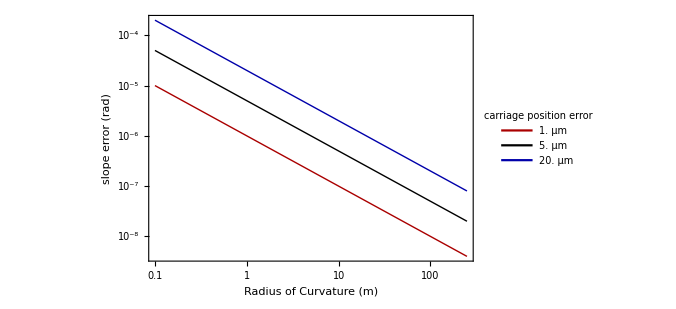

```mathematica
posErrEffects[.000001,.000005,.00002]
```

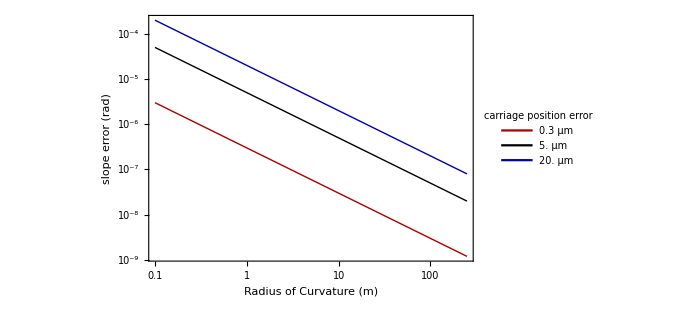

```mathematica
posErrEffects[.0000003,.000005,.00002]
```

#### more carriage position theory plots

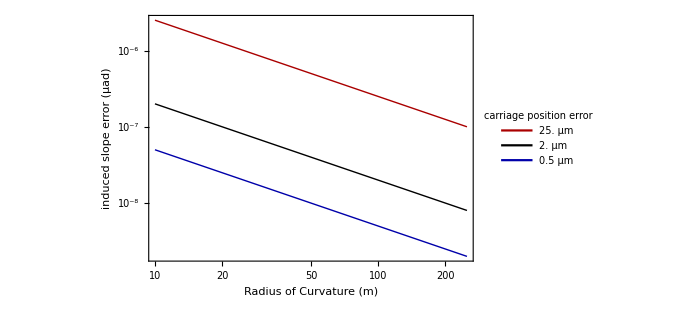

```mathematica
positionDeviationPlotRevised[maxDeviation_,rocLow_]:=Plot3D[
1/Sqrt[roc/x-1],
{x,0,maxDeviation*10^(-6)},{roc,rocLow,1000},
PlotRange->All
]

rocMin=10;
rocMax=250;

slopeErrAsFunctPosErrorRevised[roc_,posErr_]:=-1/Sqrt[(roc/posErr)^2-1]

posErrEffectsRevised[posErr1_,posErr2_,posErr3_]:=LogLogPlot[
{-slopeErrAsFunctPosErrorRevised[roc,posErr1],
-slopeErrAsFunctPosErrorRevised[roc,posErr2],
-slopeErrAsFunctPosErrorRevised[roc,posErr3]},
{roc,rocMin,rocMax},
PlotStyle->{Directive[Thick,Darker[Red]],Directive[Thick,Black],Directive[Thick,Darker[Blue]]},
PlotLegends->
Placed[
LineLegend[
{ToString[NumberForm[posErr1*10^6,3]]<>" μm",
"  "<>ToString[NumberForm[posErr2*10^6,3]]<>" μm",
" "<>ToString[NumberForm[posErr3*10^6,3]]<>" μm"},
LegendFunction->"Frame",
LegendLabel->"carriage position error",
Background->White,
LegendLayout->"Column"   ],
{Right,Top}],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray],
FrameTicks->{{uradLogTicksMedRes,None},{Automatic,None}},
Frame->True,
FrameLabel->{{"induced slope error (μad)",None},{"Radius of Curvature (m)",None}},
LabelStyle->Directive[fntSize],
(* Filling->Axis, *)
ImageSize->500
]

posErrEffectsRevised[.000025,.000002,.0000005]
```

```mathematica
logTicksHighRes=Flatten[Table[10^n*k,{k,{1,2,5}},{n,-10,-1}]]//N;
uradLogTicksHighRes=Table[{logTicksHighRes[[p]],ToString[1000000*logTicksHighRes[[p]]]},{p,1,Length[logTicksHighRes]}];

logTicksMedRes=Flatten[Table[(10^n)*k,{n,-10,-1},{k,{1,3}}]]//N;
uradLogTicksMedRes=Table[{logTicksMedRes[[p]],ToString[1000000*logTicksMedRes[[p]]]},{p,1,Length[logTicksMedRes]}];

logTicks=Flatten[Table[10^n,{n,-10,-1}]]//N;
uradLogTicks=Table[{logTicks[[p]],ToString[1000000*logTicks[[p]]]},{p,1,Length[logTicks]}];
```

## plot the scans and the residuals

```mathematica
mmTom=1000;

scanLegend=Table["s"<>ToString[scnNum],{scnNum,1,32}];

scanLegendROC[dir_,dataSets_]:=Table[
"s"<>ToString[scnNum]<>", ROC: "<>ToString[NumberForm[radiusTesting[dataSets[[scnNum]]]/mmTom,4]]<>" m",{scnNum,1,numTracesInRun[dir]}];

scanLegendRMS[dir_,dataSets_]:=Table[
"s"<>ToString[scnNum]<>", RMS: "<>ToString[StandardDeviation[dependentVectorOfFunction[dataSets[[scnNum]]]]]<>" μrad",{scnNum,1,numTracesInRun[dir]}];
scanLegendRMSwithUnits[dir_,dataSets_,units_]:=Table[
"s"<>ToString[scnNum]<>", RMS: "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[dataSets[[scnNum]]]],4]]<>" "<>ToString[units],{scnNum,1,numTracesInRun[dir]}];



plotDataRunWithDetails[directoryNum_,dataColumn_,
scaleBy_,unitDesc_,
lowDomain_,highDomain_,
offsetScansBy_,offsetResidScansBy_,
imageSize_]:=plotDataRunWithDetailsColorAndLegendPositionChoice[directoryNum,dataColumn,
scaleBy,unitDesc,
lowDomain,highDomain,
offsetScansBy,offsetResidScansBy,
imageSize,Full,Darker[Darker[Red]],{Center,Top}]

plotDataRunWithDetailsColorAndLegendPositionChoice[directoryNum_,dataColumn_,
scaleBy_,unitDesc_,
lowDomain_,highDomain_,
offsetScansBy_,offsetResidScansBy_,
imageSize_,timeSeriesPSDvertRange_,color_,legendPlace_]:=Block[
{dir=directoryNum,
dataCol=dataColumn,
scaleFactor=scaleBy,
units=unitDesc,
offsetPlotsBy=offsetScansBy,
offsetResidualPlotsBy=offsetResidScansBy,
from=lowDomain,
to=highDomain,
size=imageSize},

chartLabelStyle=Directive[Black,14,FontFamily-> "Helvitaca"];

numScans=numTracesInRun[dir];

timeData=joinMultipleScansInTime[dir,dataCol];
residTimeData=joinMultipleScanResidsInTime[dir,dataCol];

timeSpanOfRun=dataDuration[timeData];
timeGrdSpacing=If[timeSpanOfRun<3,
Round[10*timeSpanOfRun/5]/10,
Round[timeSpanOfRun/5]
];

scanDataSets=Table[
parseDataToDomain[
functionOfCarriagePosition[dir,scnNum,dataCol],
from,to],
{scnNum,1,numScans}
];

avgScan=averageOfTracesFunctPosition[dir,dataCol];
avgResid=detrendDatasetAndScale[
avgScan,
1,scaleFactor];

functInTermeOfAngle=residualAngleFunctFitOfData[avgScan];

residScanDataSets=Table[
detrendDatasetAndScale[
scanDataSets[[scnNum]],
1,scaleFactor],
{scnNum,1,numScans}
];

diffFirstLast=rescaleDataset[
differenceOverCommonRange[
scanDataSets[[1]],
scanDataSets[[numScans]]
],
scaleFactor];

diffRMS=StandardDeviation[dependentVectorOfFunction[diffFirstLast]]/1(*Sqrt[2]*);

{
{ListLinePlot[
avgScan,
Frame->True,
FrameLabel->{{"recorded values",None},{"motor coordinate","input function"}},
ImageSize-> 175
],
"rms of avg recorded values = "<>ToString[StandardDeviation[dependentVectorOfFunction[avgScan]]]
},
(* avg resids *)
ListLinePlot[
avgResid,
Frame->True,
Axes->False,
PlotStyle->Directive[Thick,color],
PlotLegends->Placed[
LineLegend[
{"RMS: "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[avgResid]],4]]<>" "<>ToString[units]<>",   ROC: "<>ToString[NumberForm[radiusTesting[avgScan]/mmTom,4]]<>" m"},
LegendFunction->"Frame",
LegendLabel->"Meas. Run "<>ToString[dir]<>", "Style[ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]],
(* LegendLabel->"Meas. Run "<>ToString[dir]<>", "Style[ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]], *)
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right],
FrameLabel->{{"Residual Variation, "<>ToString[units],None},{"Motor Coordinate",Style["Run # "<>ToString[dir]<>" Residual After Linear Detrending",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->size
],

(* =========================================== *)
(* Spatial period PSD *)
ListLogLinearPlot[
psdOfFunct[
avgResid
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {Full,Full},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],
(* converting input to residual values as a function of best linear fit of measured values *)
ListLinePlot[
functInTermeOfAngle,
Frame->True,
FrameLabel->{{"residual values",None},{"fit of recorded values","input function"}},
ImageSize-> 175
],

(* Angular period PSD *)
ListLogLinearPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, μrad",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange-> {Full,Full}(* {{0,.5},{5*10^-9,10^-1}} *),
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],
(* =========================================== *)

(* meas *)
ListLinePlot[
Table[
addOffsetForPlotting[
scanDataSets[[scnNum]],-(offsetPlotsBy*scnNum)],
{scnNum,1,numScans}
],
Frame->True,
Axes->False,
PlotStyle->Directive[Thick],
PlotLegends->
Placed[
LineLegend[
scanLegendROC[dir,scanDataSets],
LegendFunction->"Frame",
LegendLabel->Style["Run # "<>ToString[dir]<>", "<>ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]],
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right],
FrameLabel->{{"Variation, recorded units",None},{"Motor Coordinate",Style["Run # "<>ToString[dir]<>" Function of Motor",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->size
],

(*  Time *)
ListLinePlot[
rescaleDataset[
timeData,
scaleFactor],
Frame->True,
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[timeGrdSpacing],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[color]],
FrameLabel->{{"Variation, "<>ToString[units],None},{"Time of Day, 24 hr",Style["Run # "<>ToString[dir]<>" Function of Time",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{ToString[columnLabelsTSV[dir,1][[dataCol]]]},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
legendPlace],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[timeGrdSpacing]],None},
ImageSize->size
],

(* time data with the fit of the avg slope detrended *)
ListLinePlot[
rescaleDataset[
residTimeData,
scaleFactor],
Frame->True,
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[timeGrdSpacing],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[color]],
FrameLabel->{{"Resid Variation, "<>ToString[units],None},{"Time of Day, 24 hr",Style["Run # "<>ToString[dir]<>" Resid Function of Time",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{ToString[columnLabelsTSV[dir,1][[dataCol]]]},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
legendPlace],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[timeGrdSpacing]],None},
ImageSize->size
],

(* 88888888888888888888888888888888888888888888 *)
(* Time period PSD *)
ListLogLinearPlot[
psdOfFunct[
rescaleIndependentVector[residTimeData,3600]
],
Joined->True,
Axes->False,
Frame->True,
FrameTicks->{{Automatic,None},{pTicksTesting,None}},
FrameLabel->{{"PSD",None},{"Time period",None}},
LabelStyle->chartLabelStyle(*Directive[fontSize,Black,FontFamily-> "Helvetica"] *),
PlotRange->  {Full,timeSeriesPSDvertRange},
PlotStyle->Directive[Thick,Darker[Darker[color]]],
 (* FrameTicks->{{Automatic,None},{tickTest,None}}, *)
GridLines->{periodGridPointsMinuteDetail,None},
GridLinesStyle->{Thin,LightGray},
AspectRatio->aspectRat,
ImageSize->size
],
(* 888888888888888888888888888888888888888888888 *)

(* resids *)
ListLinePlot[
Table[
addOffsetForPlotting[
residScanDataSets[[scnNum]],
-(offsetResidualPlotsBy*scnNum)],
{scnNum,1,numScans}
],
Frame->True,
Axes->False,
PlotStyle->Directive[Thick],
PlotLegends->
Placed[
LineLegend[
scanLegendRMSwithUnits[dir,residScanDataSets,ToString[units]],
LegendFunction->"Frame",
LegendLabel->"Meas. Run "<>ToString[dir]<>", "Style[ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]],
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right],
FrameLabel->{{"Residual Variation, "<>ToString[units],None},{"Motor Coordinate",Style["Run # "<>ToString[dir]<>" Residuals After Linear Detrending",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->size
],

(* diffs *)
ListLinePlot[
diffFirstLast,
Frame->True,
Axes->False,
PlotStyle->Directive[Black],
PlotLegends->
Placed[
LineLegend[
{"First - Last rms = "<>ToString[NumberForm[diffRMS,4]]<>" "<>ToString[units]<>", ROC: "<>ToString[NumberForm[1000*radiusTesting[diffFirstLast]/mmTom,5]]<>" km"},
LegendFunction->"Frame",
LegendLabel->"Meas. Run "<>ToString[dir]<>", "Style[ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]],
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right], 
FrameLabel->{{"Difference, "<>ToString[units],None},{"Motor Coordinate",Style["Run # "<>ToString[dir]<>" difference between scan 1 and scan "<>ToString[numScans],Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->size
]

}

]

(*
plotDataRunWithDetails[directoryNum_,dataColumn_,
scaleBy_,unitDesc_,
lowDomain_,highDomain_,
offsetScansBy_,offsetResidScansBy_,
imageSize_]:=Block[
{dir=directoryNum,
dataCol=dataColumn,
scaleFactor=scaleBy,
units=unitDesc,
offsetPlotsBy=offsetScansBy,
offsetResidualPlotsBy=offsetResidScansBy,
from=lowDomain,
to=highDomain,
size=imageSize},

chartLabelStyle=Directive[Black,14,FontFamily-> "Helvitaca"];

numScans=numTracesInRun[dir];

timeData=joinMultipleScansInTime[dir,dataCol];
residTimeData=joinMultipleScanResidsInTime[dir,dataCol];

timeSpanOfRun=dataDuration[timeData];
timeGrdSpacing=If[timeSpanOfRun<3,
Round[10*timeSpanOfRun/5]/10,
Round[timeSpanOfRun/5]
];

scanDataSets=Table[
parseDataToDomain[
functionOfCarriagePosition[dir,scnNum,dataCol],
from,to],
{scnNum,1,numScans}
];

avgScan=averageOfTracesFunctPosition[dir,dataCol];
avgResid=detrendDatasetAndScale[
avgScan,
1,scaleFactor];

functInTermeOfAngle=residualAngleFunctFitOfData[avgScan];

residScanDataSets=Table[
detrendDatasetAndScale[
scanDataSets[[scnNum]],
1,scaleFactor],
{scnNum,1,numScans}
];

diffFirstLast=rescaleDataset[
differenceOverCommonRange[
scanDataSets[[1]],
scanDataSets[[numScans]]
],
scaleFactor];

diffRMS=StandardDeviation[dependentVectorOfFunction[diffFirstLast]]/1(*Sqrt[2]*);

{
{ListLinePlot[
avgScan,
Frame->True,
FrameLabel->{{"recorded values",None},{"motor coordinate","input function"}},
ImageSize-> 175
],
"rms of avg recorded values = "<>ToString[StandardDeviation[dependentVectorOfFunction[avgScan]]]
},
(* avg resids *)
ListLinePlot[
avgResid,
Frame->True,
Axes->False,
PlotStyle->Thick,
PlotLegends->Placed[
LineLegend[
{"RMS: "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[avgResid]],4]]<>" "<>ToString[units]<>",   ROC: "<>ToString[NumberForm[radiusTesting[avgScan]/mmTom,4]]<>" m"},
LegendFunction->"Frame",
LegendLabel->"Meas. Run "<>ToString[dir]<>", "Style[ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]],
(* LegendLabel->"Meas. Run "<>ToString[dir]<>", "Style[ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]], *)
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right],
FrameLabel->{{"Residual Variation, "<>ToString[units],None},{"Motor Coordinate",Style["Run # "<>ToString[dir]<>" Residual After Linear Detrending",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->size
],

(* =========================================== *)
(* Spatial period PSD *)
ListLogLinearPlot[
psdOfFunct[
avgResid
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {Full,Full},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,Blue],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],
(* converting input to residual values as a function of best linear fit of measured values *)
ListLinePlot[
functInTermeOfAngle,
Frame->True,
FrameLabel->{{"residual values",None},{"fit of recorded values","input function"}},
ImageSize-> 175
],

(* Angular period PSD *)
ListLogLinearPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, μrad",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange-> {Full,Full}(* {{0,.5},{5*10^-9,10^-1}} *),
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,Blue],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],
(* =========================================== *)

(* meas *)
ListLinePlot[
Table[
addOffsetForPlotting[
scanDataSets[[scnNum]],-(offsetPlotsBy*scnNum)],
{scnNum,1,numScans}
],
Frame->True,
Axes->False,
PlotStyle->Thick,
PlotLegends->
Placed[
LineLegend[
scanLegendROC[dir,scanDataSets],
LegendFunction->"Frame",
LegendLabel->Style["Run # "<>ToString[dir]<>", "<>ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]],
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right],
FrameLabel->{{"Variation, recorded units",None},{"Motor Coordinate",Style["Run # "<>ToString[dir]<>" Function of Motor",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->size
],

(*  Time *)
ListLinePlot[
rescaleDataset[
timeData,
scaleFactor],
Frame->True,
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[timeGrdSpacing],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[Red]],
FrameLabel->{{"Variation, "<>ToString[units],None},{"Time of Day, 24 hr",Style["Run # "<>ToString[dir]<>" Function of Time",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{ToString[columnLabelsTSV[dir,1][[dataCol]]]},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[timeGrdSpacing]],None},
ImageSize->size
],

(* time data with the fit of the avg slope detrended *)
ListLinePlot[
rescaleDataset[
residTimeData,
scaleFactor],
Frame->True,
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[timeGrdSpacing],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[Red]],
FrameLabel->{{"Resid Variation, "<>ToString[units],None},{"Time of Day, 24 hr",Style["Run # "<>ToString[dir]<>" Resid Function of Time",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{ToString[columnLabelsTSV[dir,1][[dataCol]]]},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[timeGrdSpacing]],None},
ImageSize->size
],

(* 88888888888888888888888888888888888888888888 *)
(* Time period PSD *)
ListLogLinearPlot[
psdOfFunct[
rescaleIndependentVector[residTimeData,3600]
],
Joined->True,
Axes->False,
Frame->True,
FrameTicks->{{Automatic,None},{pTicksTesting,None}},
FrameLabel->{{"PSD",None},{"Time period",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {Full,{-1*10^-16,2*10^-15}(*Full *)},
PlotStyle->Directive[Thick,Darker[Darker[Red]]],
 (* FrameTicks->{{Automatic,None},{tickTest,None}}, *)
GridLines->{periodGridPointsMinuteDetail,None},
GridLinesStyle->{Thin,LightGray},
AspectRatio->aspectRat,
ImageSize->size
],
(* 888888888888888888888888888888888888888888888 *)

(* resids *)
ListLinePlot[
Table[
addOffsetForPlotting[
residScanDataSets[[scnNum]],
-(offsetResidualPlotsBy*scnNum)],
{scnNum,1,numScans}
],
Frame->True,
Axes->False,
PlotStyle->Thick,
PlotLegends->
Placed[
LineLegend[
scanLegendRMSwithUnits[dir,residScanDataSets,ToString[units]],
LegendFunction->"Frame",
LegendLabel->"Meas. Run "<>ToString[dir]<>", "Style[ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]],
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right],
FrameLabel->{{"Residual Variation, "<>ToString[units],None},{"Motor Coordinate",Style["Run # "<>ToString[dir]<>" Residuals After Linear Detrending",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->size
],

(* diffs *)
ListLinePlot[
diffFirstLast,
Frame->True,
Axes->False,
PlotStyle->Directive[Black],
PlotLegends->
Placed[
LineLegend[
{"First - Last rms = "<>ToString[NumberForm[diffRMS,4]]<>" "<>ToString[units]<>", ROC: "<>ToString[NumberForm[1000*radiusTesting[diffFirstLast]/mmTom,5]]<>" km"},
LegendFunction->"Frame",
LegendLabel->"Meas. Run "<>ToString[dir]<>", "Style[ToString[columnLabelsTSV[dir,1][[dataCol]]],Directive[Bold,14]],
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right], 
FrameLabel->{{"Difference, "<>ToString[units],None},{"Motor Coordinate",Style["Run # "<>ToString[dir]<>" difference between scan 1 and scan "<>ToString[numScans],Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->size
]

}

]
*)

plotDataRun[directoryNum_,dataColumn_,offsetScansBy_,offsetResidScansBy_,lowDomain_,highDomain_,imageSize_]:=plotDataRunWithDetails[directoryNum,dataColumn,radToMicroRad," μrad",lowDomain,highDomain,offsetScansBy,offsetResidScansBy,imageSize];

showTheScanDetails[directoryNum_,dataColumn_,offsetScansBy_,offsetResidScansBy_,lowDomain_,highDomain_,imageSize_]:=plotDataRun[directoryNum,dataColumn,offsetScansBy,offsetResidScansBy,lowDomain,highDomain,imageSize];


(* These functions may be *)
lookAtAFunction[function_]:={plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSD[
function,
lineColor=Darker[Blue],
description="description",
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel="Residual Slope, μrad",
plotHorizRange=Automatic,
plotVertRange={-1.2,1.2},
psdHorizRange=Automatic,
psdVertRange=Automatic,
spatialPSDHorizRange=Automatic][[2]],
"RMS "<>ToString[StandardDeviation[dependentVectorOfFunction[function]]]<>" μrad"
}

lookAtAFunctionWithDescAndColor[function_,description_,color_]:={plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSD[
function,
lineColor=Darker[color],
ToString[description],
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel="Residual Slope, μrad",
plotHorizRange=Automatic,
plotVertRange={-2,2},
psdHorizRange=Automatic,
psdVertRange=Full,
spatialPSDHorizRange=Automatic][[{2,3}]],
"RMS of raw input function: "<>ToString[StandardDeviation[dependentVectorOfFunction[function]]]<>" μrad"
}


plotTimeData[timeDataset_,units_]:=plotTimeDataWithColorAndDesc[timeDataset,units,Red,"desc"]

plotTimeDataWithColorAndDesc[timeDataset_,units_,color_,description_]:=plotTimeDataWithColorAndDescWithRanges[timeDataset,units,color,description, Full]

plotTimeDataWithColorAndDescWithRanges[timeDataset_,units_,color_,description_,psdRange_]:=plotTimeDataWithColorAndDescWithRangesVertScale[timeDataset,units,color,description,psdRange,Automatic];
plotTimeDataWithColorAndDescWithRangesVertScale[timeDataset_,units_,color_,description_,psdRange_,vertPlotRange_]:=plotTimeDataWithColorAndDescWithRangesVertScaleDataScaledBy[timeDataset,units,color,description,psdRange,vertPlotRange,1(* scale factor *)]
plotTimeDataWithColorAndDescWithRangesVertScaleDataScaledBy[timeDataset_,units_,color_,description_,psdRange_,vertPlotRange_,scaleFactor_]:=Block[
{timeData=timeDataset},

chartLabelStyle=Directive[Black,14,FontFamily-> "Helvitaca"];

timeSpanOfRun=dataDuration[timeData];
timeGrdSpacing=If[timeSpanOfRun<3,
Round[10*timeSpanOfRun/5]/10,
Round[timeSpanOfRun/5]
];

scaledTimeData=rescaleDataset[
timeData,
scaleFactor];

scaledTimeDataValues=dependentVectorOfFunction[scaledTimeData];

{(*  Time *)
ListLinePlot[
scaledTimeData,
Frame->True,
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[timeGrdSpacing],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[color]],
FrameLabel->{{"Variation, "<>ToString[units],None},{"Time of Day, 24 hr",None}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{ToString[description]<>"; Mean Value: "<>ToString[Mean[scaledTimeDataValues]]<>";  rms: "<>ToString[StandardDeviation[scaledTimeDataValues]]},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Top(*{Center,Top}*)],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[timeGrdSpacing]],None},
ImageSize->600,
AspectRatio->.3,
PlotRange->{Automatic,vertPlotRange}

],
(* PSD *)
ListLogLogPlot[
psdOfFunct[
rescaleIndependentVector[detrendDatasetAndScale[timeData,1,scaleFactor],3600]
],
Joined->True,
Axes->False,
Frame->True,
FrameTicks->{{Automatic,None},{pTicksTesting,None}},
FrameLabel->{{"PSD",None},{"Time period",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  If[ToString[psdRange]=="Full",Full,psdRange],
PlotStyle->Directive[Thick,Darker[Darker[color]]],
 (* FrameTicks->{{Automatic,None},{tickTest,None}}, *)
GridLines->{periodGridPointsMinuteDetail,None},
GridLinesStyle->{Thin,LightGray},
AspectRatio->.3,
ImageSize->600
]
}
]



timeSeriesInspectionOfScan[scanDirNum_,dataColumnNum_,psdRange_]:=timeSeriesInspectionOfScanVertScale[scanDirNum,dataColumnNum,psdRange,Automatic];

timeSeriesInspectionOfScanVertScale[scanDirNum_,dataColumnNum_,psdRange_,plotVertRange_]:=timeSeriesInspectionOfScanVertScaleToDomain[scanDirNum,dataColumnNum,psdRange,plotVertRange,"Full","Full"];

timeSeriesInspectionOfScanVertScaleToDomain[scanDirNum_,dataColumnNum_,psdRange_,plotVertRange_,dataDomainLow_,dataDomainHigh_]:=timeSeriesInspectionOfScanVertScaleToDomainWithScaling[scanDirNum,dataColumnNum,psdRange,plotVertRange,dataDomainLow,dataDomainHigh,1(* scale *)]

timeSeriesInspectionOfScanVertScaleToDomainWithScaling[scanDirNum_,dataColumnNum_,psdRange_,plotVertRange_,dataDomainLow_,dataDomainHigh_,scaleFact_]:=timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[scanDirNum,dataColumnNum,psdRange,plotVertRange,dataDomainLow,dataDomainHigh,scaleFact,Top,"units"]

timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[scanDirNum_,dataColumnNum_,psdRange_,plotVertRange_,dataDomainLow_,dataDomainHigh_,scaleFact_,legendPos_,units_]:=Module[
{},

scaledTimeData=rescaleDataset[
parseDataToDomain[
joinMultipleScansInTime[scanDirNum,dataColumnNum],
dataDomainLow,dataDomainHigh],
scaleFact];

scaledTimeDataValues=dependentVectorOfFunction[scaledTimeData];

timeSpanOfRun=dataDuration[scaledTimeData];
timeGrdSpacing=If[timeSpanOfRun<3,
Round[10*timeSpanOfRun/5]/10,
Round[timeSpanOfRun/5]
];

chartLabelStyle=Directive[Black,14,FontFamily-> "Helvitaca"];

If[
ToString[Last[psdRange]]=="viewable",
parseDataToDomain[]
];

{(*  Time *)
ListLinePlot[
scaledTimeData,
Frame->True,
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[timeGrdSpacing],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[
Join[Flatten[
Table[
colorListLong,
{k,1,12}
]
]][[dataColumnNum+2(* this changes the color *)]]
]
],
FrameLabel->{{"Variation, "<>ToString[units],None},{"Time of Day, 24 hr",ToString["Scan"<>ToString[scanDirNum]<>" ,"<>ToString[columnLabelsTSV[scanDirNum,1][[dataColumnNum]]]]}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{ToString[scanDirNum]<>"; Mean Value: "<>ToString[Mean[scaledTimeDataValues]]<>";  rms: "<>ToString[StandardDeviation[scaledTimeDataValues]]<>" "<>ToString[units]},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
legendPos],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[timeGrdSpacing]],None},
ImageSize->500,
AspectRatio->.3,
PlotRange->{Automatic,plotVertRange}

],
(* PSD *)
ListLogLinearPlot[
parseDataToDomain[
psdOfFunct[
rescaleIndependentVector[scaledTimeData,3600]
],
halfHourPSDLowRange,halfHourPSDHighRange],
Joined->True,
Axes->False,
Frame->True,
FrameTicks->{{Automatic,None},{pTicksTesting,None}},
FrameLabel->{{"PSD",None},{"Time period",None}},
LabelStyle->chartLabelStyle,
PlotRange->  If[ToString[psdRange]=="Full",Full,psdRange],
PlotStyle->Directive[Thick,Darker[
Join[Flatten[
Table[
colorListLong,
{k,1,12}
]
]][[dataColumnNum+2(* this changes the color *)]]
]],
 (* FrameTicks->{{Automatic,None},{tickTest,None}}, *)
GridLines->{periodGridPointsMinuteDetail,None},
GridLinesStyle->{Thin,LightGray},
AspectRatio->.3,
ImageSize->500
]
}

]

(*
timeSeriesInspectionOfScanVertScaleToDomain[scanDirNum_,dataColumnNum_,psdRange_,plotVertRange_,dataDomainLow_,dataDomainHigh_]:=plotTimeDataWithColorAndDescWithRangesVertScale[
detrendDatasetAndScale[
parseDataToDomain[
joinMultipleScansInTime[scanDirNum,dataColumnNum],
dataDomainLow,dataDomainHigh],
1,1],
"units",
Join[Flatten[
Table[
colorList,
{k,1,10}
]
]][[dataColumnNum]],
"Scan"<>ToString[scanDirNum]<>" "<>ToString[columnLabelsTSV[scanDirNum,1][[dataColumnNum]]],
psdRange,
plotVertRange]
*)


plotTimeDataSeconds[timeDataset_,units_]:=Block[
{timeData=timeDataset},

chartLabelStyle=Directive[Black,14,FontFamily-> "Helvitaca"];

timeSpanOfRun=dataDuration[timeData]/3600;
timeGrdSpacing=If[timeSpanOfRun<3,
Round[10*timeSpanOfRun/5]/10,
Round[timeSpanOfRun/5]
];

{(*  Time *)
ListLinePlot[
rescaleDataset[
timeData,
scaleFactor=1],
Frame->True,
FrameTicks->{{Automatic,Automatic},{rescaleIndependentVector[hoursInADayTicksSpacedAt[timeGrdSpacing],3600],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[Red]],
FrameLabel->{{"Variation, "<>ToString[units],None},{"Time of Day, 24 hr",None}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{ToString["legend desc"]},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[timeGrdSpacing]]*3600,None},
AspectRatio->aspectRat*.6,
ImageSize->600
],

ListLogLinearPlot[
psdOfFunct[
rescaleIndependentVector[detrendDatasetAndScale[timeData,1,1],1]
],
Joined->True,
Axes->False,
Frame->True,
FrameTicks->{{Automatic,None},{rescaleIndependentVector[pTicksTesting,1],None}},
FrameLabel->{{"PSD",None},{"Time period",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {Full,Full},
PlotStyle->Directive[Thick,Darker[Darker[Red]]],
 (* FrameTicks->{{Automatic,None},{tickTest,None}}, *)
GridLines->{periodGridPointsMinuteDetail,None},
GridLinesStyle->{Thin,LightGray},
AspectRatio->aspectRat*.6,
ImageSize->600
]
}
]

(* plotTimeDataSeconds[timeDataset_,units_]:=Block[
{timeData=timeDataset},

chartLabelStyle=Directive[Black,14,FontFamily-> "Helvitaca"];

timeSpanOfRun=dataDuration[timeData]/3600;
timeGrdSpacing=If[timeSpanOfRun<3,
Round[10*timeSpanOfRun/5]/10,
Round[timeSpanOfRun/5]
];

{(*  Time *)
ListLinePlot[
rescaleDataset[
timeData,
scaleFactor=1],
Frame->True,
FrameTicks->{{Automatic,Automatic},{rescaleIndependentVector[hoursInADayTicksSpacedAt[timeGrdSpacing],3600],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[Red]],
FrameLabel->{{"Variation, "<>ToString[units],None},{"Time of Day, 24 hr",None}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{ToString["legend desc"]},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[timeGrdSpacing]]*3600,None},
ImageSize->500
],

ListLogLinearPlot[
psdOfFunct[
rescaleIndependentVector[detrendDatasetAndScale[timeData,1,1],3600]
],
Joined->True,
Axes->False,
Frame->True,
FrameTicks->{{Automatic,None},{rescaleIndependentVector[pTicksTesting,1/3600],None}},
FrameLabel->{{"PSD",None},{"Time period",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {Full,Full},
PlotStyle->Directive[Thick,Darker[Darker[Red]]],
 (* FrameTicks->{{Automatic,None},{tickTest,None}}, *)
GridLines->{periodGridPointsMinuteDetail/3600,None},
GridLinesStyle->{Thin,LightGray},
AspectRatio->aspectRat,
ImageSize->500
]
}
] *)
```

```mathematica
lookAtTempsOfRun[runNum_]:=Table[
timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnits[
runNum,dataCol,Full,plotVertRange=Automatic,dataDomainLow=Full,dataDomainHigh=Full,scaleFact=1,legendPos={Right,Top},units="° C"],
{dataCol,{10,11,12,13,25}}]
```

```mathematica
timeSeriesInspectionOfScanVertScaleToDomainWithScalingLegendPositionUnitsSigScan[scanDirNum_,dataColumnNum_,psdRange_,plotVertRange_,dataDomainLow_,dataDomainHigh_,scaleFact_,detrendOrder_,legendPos_,units_]:=Module[
{},

scaledTimeDataNoDetrending=rescaleDataset[
parseDataToDomain[
sigScanRunInTime[scanDirNum,dataColumnNum],
dataDomainLow,dataDomainHigh],
scaleFact];

scaledTimeData=detrendDatasetAndScale[
scaledTimeDataNoDetrending,
detrendOrder,1
];

scaledTimeDataValuesNoDetrending=dependentVectorOfFunction[scaledTimeDataNoDetrending];
scaledTimeDataValues= dependentVectorOfFunction[scaledTimeData];

timeSpanOfRun=dataDuration[scaledTimeData];
timeGrdSpacing=If[timeSpanOfRun<3,
Round[10*timeSpanOfRun/5]/10,
Round[timeSpanOfRun/5]
];

chartLabelStyle=Directive[Black,14,FontFamily-> "Helvitaca"];

dataColumnLabels=Flatten[
Take[
Drop[
Import[FileNames[][[1]],"TSV"],
sigScanHeaderRows],
{1,1}
]
];
(*If[
ToString[Last[psdRange]]=="viewable",
parseDataToDomain[]
]; *)

{(*  Time *)
ListLinePlot[
scaledTimeData,
Frame->True,
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[timeGrdSpacing],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[
Join[Flatten[
Table[
colorList,
{k,1,12}
]
]][[dataColumnNum]]
]
],
FrameLabel->{{"Variation, "<>ToString[units],None},{"Time of Day, 24 hr",ToString["Scan"<>ToString[scanDirNum]<>" ,"<>ToString[dataColumnLabels[[dataColumnNum]]]]}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{"SigScan"<>ToString[scanDirNum]<>"; Mean Value: "<>ToString[Mean[scaledTimeDataValuesNoDetrending]]<>";  rms: "<>ToString[StandardDeviation[scaledTimeDataValues]]},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
legendPos],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[timeGrdSpacing]],None},
ImageSize->500,
AspectRatio->.3,
PlotRange->{Automatic,plotVertRange}

],
(* PSD *)
ListLogLinearPlot[
parseDataToDomain[
psdOfFunct[
rescaleIndependentVector[scaledTimeData,3600]
],
halfHourPSDLowRange,halfHourPSDHighRange],
Joined->True,
Axes->False,
Frame->True,
FrameTicks->{{Automatic,None},{pTicksTesting,None}},
FrameLabel->{{"PSD",None},{"Time period",None}},
LabelStyle->chartLabelStyle,
PlotRange->  If[ToString[psdRange]=="Full",Full,psdRange],
PlotStyle->Directive[Thick,Darker[
Join[Flatten[
Table[
colorList,
{k,1,12}
]
]][[dataColumnNum]]
]],
 (* FrameTicks->{{Automatic,None},{tickTest,None}}, *)
GridLines->{periodGridPointsMinuteDetail,None},
GridLinesStyle->{Thin,LightGray},
AspectRatio->.3,
ImageSize->500
]
}

]
```

```mathematica
eShiftPlotting[eShiftFunction_,desc_]:={(*  Time *)
ListLinePlot[
eShiftFunction,
Frame->True,
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[3],None}},
Axes->False,
PlotStyle->Directive[Thin,Darker[Black]],
FrameLabel->{{"Variation, eV",None},{"Time of Day, 24 hr","Scan "<>ToString[desc]}},
LabelStyle->chartLabelStyle,
PlotLegends->
Placed[
LineLegend[
{"rms: "<>ToString[StandardDeviation[dependentVectorOfFunction[eShiftFunction]]]<>" eV"},
LegendFunction->"Frame",
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Bottom}],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[3]],None},
ImageSize->500,
AspectRatio->.3,
PlotRange->{Automatic,{-1.5,1.5}}

],
(* PSD *)
ListLogLinearPlot[
parseDataToDomain[
psdOfFunct[
rescaleIndependentVector[eShiftFunction,3600]
],
halfHourPSDLowRange,halfHourPSDHighRange],
Joined->True,
Axes->False,
Frame->True,
FrameTicks->{{Automatic,None},{pTicksTesting,None}},
FrameLabel->{{"PSD",None},{"Time period",None}},
LabelStyle->chartLabelStyle,
PlotRange->  If[ToString[psdRange]=="Full",Full,psdRange],
PlotStyle->Directive[Thick,Darker[Black]],
 (* FrameTicks->{{Automatic,None},{tickTest,None}}, *)
GridLines->{periodGridPointsMinuteDetail,None},
GridLinesStyle->{Thin,LightGray},
AspectRatio->.3,
ImageSize->500
]
}
```

```mathematica
narrowAspectRat=0.35;

displayLTPmeasResultsWithDisplayOptions[runNumbers_,dataColumnNumber_,depVectDesc_,depVectUnits_, plotVertRange_,gridSpacing_,legendPlacement_]:=Block[
{runNumList=runNumbers,
dataColNum=dataColumnNumber,
desc=depVectDesc,
units=depVectUnits,
vertRange=plotVertRange,
grdSpace=gridSpacing,
legendPos=legendPlacement},

dataSets=Table[
joinMultipleScansInTime[runNum,dataColNum],
{runNum,runNumList}
];
descriptions=Table[
"Run # "<>ToString[runNum]<>", rms "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[dataSets[[First[Flatten[Position[runNumList,runNum]]]]]]],3]]<>", "<>ToString[units],
{runNum,runNumList}];


ListLinePlot[
dataSets,
PlotLegends->
Placed[
LineLegend[
descriptions,
LegendFunction->"Frame",
LegendLabel->ToString[columnLabelsTSV[runNumList[[1]],1][[dataColNum]]],
LabelStyle->Directive[11,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
legendPos],
Frame->True,
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[grdSpace],None}},
FrameLabel->{{ToString[desc],None},{"Time of Day, 24hr",None}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
GridLines->{independentVectorOfFunction[hoursInADayTicksSpacedAt[grdSpace]],None},
PlotRange->{Automatic,vertRange },
Axes->False,
PlotStyle->Thick,
ImageSize->500
]
]

vertRange={23.94,24.26};
grdSpace=2;
legendPlacement={Left,Bottom}

displayLTPmeasResults[runNumbers_,dataColumnNumber_]:=displayLTPmeasResultsWithDisplayOptions[runNumbers,dataColumnNumber,"Temp 1, °C", "°C",vertRange,grdSpace,{Right,Bottom}];


plotWithStyleWithDesc[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_]:=Block[
{funct=function,
color=lineColor,
desc=description,
hAxisLabel=horizAxisLabel,
vAxisLabel=vertAxisLabel},

{ListLinePlot[
funct,
Axes->False,
Frame->True,
FrameLabel->{{vAxisLabel,None},{hAxisLabel,ToString[desc]}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotLegends->Placed["rms = "<>ToString[StandardDeviation[dependentVectorOfFunction[funct]]],Right],
ImageSize->imgSize,
AspectRatio->narrowAspectRat,
PlotStyle->Directive[Thick,Darker[color]]
],

ListLogPlot[
psdOfFunct[funct],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{None,None},{None,"PSD"}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
ImageSize->imgSize,
AspectRatio->narrowAspectRat,
PlotStyle->Darker[color]

]
}
]

plotWithStyle[function_,lineColor_]:=plotWithStyleWithDesc[function,lineColor,"function","motor","vert Axis"]

dataRunColNumBfunctionOfColNumA[runNumber_,dataColB_,functOfColNum_]:=Block[
{runNum=runNumber,
colB=dataColB,
functOf=functOfColNum},
numScans=numTracesInRun[runNum];

Thread[{
Mean[
Table[dataFromColumnFunctPosition[runNum,scnNum,functOf],
{scnNum,1,numScans}]
],
Mean[
Table[
dataFromColumnFunctPosition[runNum,1,colB],
{scnNum,1,numScans}]]
}]
]

(* Below was created to inspect the individual LTP *.txt data columns *)
inspectDataColumnChartDesc[detrendOrder_]:=Which[
ToString[detrendOrder]=="None","No Detrending",
detrendOrder == 0, "Zero Order Detrended",
detrendOrder == 1, "1st Order Detrended",
detrendOrder == 2,"2nd Order Detrended",
detrendOrder == 3, "3rd Order Detrended",
detrendOrder≥4,ToString[detrendOrder]<>"th Order Detrended"
];

inspectingDataColumn[scanNumbers_,dataColNum_,detrendOrder_,scaleBy_,offsetBy_]:=ListLinePlot[
Table[
addOffsetForPlotting[
detrendDatasetAndScale[
averageOfTracesFunctPosition[scanNum,dataColNum],
detrendOrder,scaleBy],
offsetBy-offsetBy*First[Flatten[Position[scanNumbers,scanNum]]]],
{scanNum,scanNumbers}],
Frame->True,
Axes->False,
FrameLabel->{{"units scaled by "<>ToString[scaleBy],None},{"Motor",ToString[columnLabelsTSV[3630,1][[dataColNum]]]<>"    ("<>inspectDataColumnChartDesc[detrendOrder]<>")"}},
LabelStyle->Directive[14,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
scanNumbers,
 LegendFunction->"Frame",
LegendLabel->"Meas. Runs offset by "<>ToString[offsetBy],
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right],
ImageSize->450,
PlotRange->Automatic(* {{-5900,-900},{-10,2.5}} *),
AspectRatio->aspectRat,
PlotStyle->{Thick}
]
```

{Left,Bottom}

```mathematica
imgagSize=400

plotMeasManyTracesWithStyleOptions[slopeData_,vertRange_,color_]:=ListLinePlot[
detrendDatasetAndScale[
slopeData,
1,1],
Frame->True,
Axes->False,
FrameLabel->{{"Resid. Slope, μrad",None},{"Tangential Position, mm",None}},
LabelStyle->Directive[12,Black,FontFamily-> "Helvetica"],
PlotRange->{Automatic,vertRange},
PlotLegends->
Placed[
LineLegend[
{"ROC = "<>ToString[NumberForm[1000/First[Last[Fit[slopeData,{1,x},x]]],4]]<>" m"<>",  rms = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[detrendDatasetAndScale[slopeData,1,1]]],3]]<>"μrad"},
LegendFunction->"Frame",
LabelStyle->Directive[12,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],   
PlotStyle->{{Thick,color},{Thick,Orange},{Thick,RGBColor[1,.33333,0]}},
ImageSize->imgagSize,
AspectRatio->narrowAspectRat
]

plotMeasManyTraces[slopeData_]:=plotMeasManyTracesWithStyleOptions[slopeData,{-3.5,3.5},Lighter[Orange]]

plotMeasManyTracesWithStyleOptionsKmROC[slopeData_,vertRange_,color_]:=ListLinePlot[
detrendDatasetAndScale[
slopeData,
1,1],
Frame->True,
Axes->False,
FrameLabel->{{"Resid. Slope, μ rad",None},{"Tangential Position, mm",None}},
LabelStyle->Directive[12,Black,FontFamily-> "Helvetica"],
PlotRange->{Automatic,vertRange},
PlotLegends->
Placed[
LineLegend[
{"ROC = "<>ToString[NumberForm[1/First[Last[Fit[slopeData,{1,x},x]]],4]]<>" km"<>",  rms = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[detrendDatasetAndScale[slopeData,1,1]]],3]]<>"μrad"},
LegendFunction->"Frame",
LabelStyle->Directive[12,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],   
PlotStyle->{{Thick,color},{Thick,Orange},{Thick,RGBColor[1,.33333,0]}},
ImageSize->imgagSize,
AspectRatio->narrowAspectRat
]
```

400

### Functions to Display the data

```mathematica
plotTwoWithDiff[AA_,BB_]:={ListLinePlot[{
AA,BB
},
ImageSize->400,
Frame->True,
FrameLabel->{{None,None},{None,"Input Functions"}},
LabelStyle->Directive[Black, 14]
],
ListLinePlot[
differenceOverCommonRange[
AA,BB
],
ImageSize->400,
Frame->True,
FrameLabel->{{None,None},{None,"Difference"}},
LabelStyle->Directive[Black, 14],
PlotStyle->Black

]}
```

#### This function displays the measurement results

```mathematica
imgSize=325;
imgSizeOfStyle=650;

plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSD[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_]:=plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDselectSizeAndAspectRatio[function,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange,plotVertRange,psdHorizRange,psdVertRange,spatialPSDHorizRange,size = 600,aspectR=aspectRat/2]

plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDselectSizeAndAspectRatio[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_,pictureSize_,aspectRatio_]:=plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDselectSizeAndAspectRatioUnitSelection[function,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange,plotVertRange,psdHorizRange,psdVertRange,spatialPSDHorizRange,pictureSize,aspectRatio,"μrad","rms"]

plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDselectSizeAndAspectRatioUnitSelection[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_,pictureSize_,aspectRatio_,units_,peakToValleyOrRMSq_]:=plotWithStyleParameters[function,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange,plotVertRange,psdHorizRange,psdVertRange,spatialPSDHorizRange,pictureSize,aspectRatio,units,peakToValleyOrRMSq,nonResidRange=Automatic];

plotWithStyleParameters[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_,pictureSize_,aspectRatio_,units_,peakToValleyOrRMSq_,nonResidVscale_]:=Block[
{funct=function,
color=lineColor,
desc=description,
hAxisLabel=horizAxisLabel,
vAxisLabel=vertAxisLabel,
plotHoriz=plotHorizRange,
plotVert=plotVertRange,
psdHoriz=psdHorizRange,
psdVert=psdVertRange,
psdSpatialRange=spatialPSDHorizRange,
pictSize=pictureSize ,
aspectR=aspectRatio,
unitSelection=units,
PVorRMSq=peakToValleyOrRMSq,
vScaleRaw=nonResidVscale},

depVectFunct=dependentVectorOfFunction[funct];

residFunct=detrendDatasetAndScale[funct,1,1];
depVectResidFunct=dependentVectorOfFunction[residFunct];

functInTermeOfAngle=residualAngleFunctFitOfData[funct];

curvature =  1 /First[Last[Fit[funct,{1,x},x]]];

(*
rocDisplay[scaleFactor_,mKmQ_,curvature_]:={"ROC = "<>ToString[NumberForm[scaleFactor*curvature,5(* number of Sig Figs *)]]<>ToString[mKmQ]<>",  rms = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[residFunct]],4]]<>"μrad"};

rocDisp=If[
curvature≤10,
rocDisplay[1000,"m",curvature],
rocDisplay[1,"km",curvature]
];
*)
pvDisplay={"Peak-To-Valley = "<>ToString[NumberForm[     Max[depVectFunct]-Min[depVectFunct] ,4]]<>" "<>ToString[unitSelection]<>", rms = "<>ToString[NumberForm[StandardDeviation[depVectFunct],4]]<>" "<>ToString[unitSelection]};

rocDisplay=If[unitSelection=="um"||unitSelection=="μm"||unitSelection=="nm",
{" rms = "<>ToString[NumberForm[StandardDeviation[depVectResidFunct],4]]<>ToString[unitSelection]},
If[
Abs[curvature ]≤10,
{"ROC = "<>ToString[NumberForm[1000*curvature,5(* number of Sig Figs *)]]<> " m"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectResidFunct],4]]<>ToString[unitSelection]},
{"ROC = "<>ToString[NumberForm[curvature,5(* number of Sig Figs *)]]<> " km"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectResidFunct],4]]<>ToString[unitSelection]}
]
];

rocDisplayNoDetrending=If[unitSelection=="um"||unitSelection=="μm"||unitSelection=="nm",
{" rms = "<>ToString[NumberForm[StandardDeviation[depVectFunct],4]]<>ToString[unitSelection]},
If[
Abs[curvature ]≤10,
{"ROC = "<>ToString[NumberForm[1000*curvature,5(* number of Sig Figs *)]]<> " m"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectFunct],4]]<>ToString[unitSelection]},
{"ROC = "<>ToString[NumberForm[curvature,5(* number of Sig Figs *)]]<> " km"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectFunct],4]]<>ToString[unitSelection]}
]
];



(* input function *)
inputFunction=ListLinePlot[
funct,
PlotRange->{plotHoriz,vScaleRaw},
Frame->True,
Axes->False,
FrameLabel->{{"Recorded Slope, μrad"(*"Height Difference, nm"*)(*"Slope Difference, μrad"*)(*"Integrated height, nm"*)(*"function value"*),None},{hAxisLabel,If[ToString[desc]=="None",None,ToString[desc]]}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
If[ToString[PVorRMSq]=="rms",
rocDisplayNoDetrending,
pvDisplay],
LegendFunction->"Frame",
LabelStyle->Directive[11,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top} ],   
(*PlotLegends->Placed["rms = "<>ToString[StandardDeviation[dependentVectorOfFunction[residFunct]]],Right], *)
ImageSize-> pictSize,
AspectRatio->aspectR,
PlotStyle->Directive[Thick,color],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]
];

(* Surface Profile *)
surfaceProfile=ListLinePlot[
residFunct,
Axes->False,
Frame->True,
FrameLabel->{{vAxisLabel,None},{hAxisLabel,If[ToString[desc]=="None",None,ToString[desc]]}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
If[ToString[PVorRMSq]=="rms",
rocDisplay,
pvDisplay],
LegendFunction->"Frame",
LabelStyle->Directive[11,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],   
(*PlotLegends->Placed["rms = "<>ToString[StandardDeviation[dependentVectorOfFunction[residFunct]]],Right], *)
PlotRange->{plotHoriz,plotVert},
ImageSize->pictSize,
AspectRatio->aspectR,
PlotStyle->Directive[Thick,color],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]
];



(* Spatial period PSD *)
spatialPSD=ListLogLinearPlot[
psdOfFunct[
residFunct
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm" ,None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {psdSpatialRange,psdVert},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
];


(* Angular period PSD *)
angularPeriodPSD=ListLogLinearPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, "<>ToString[unitSelection],None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
PlotRange-> {psdHoriz,psdVert}(* {{0,.5},{5*10^-9,10^-1}} *)
];

(* Spatial period PSD *)
logLogSpatial=ListLogLogPlot[
psdOfFunct[
residFunct
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm" ,None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {psdSpatialRange,psdVert},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
];


(* Angular period PSD *)
logLogAngular=ListLogLogPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, "<>ToString[unitSelection],None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
PlotRange-> {psdHoriz,Full}(* {{0,.5},{5*10^-9,10^-1}} *)
];


(* converting input to residual values as a function of best linear fit of measured values *)
functInTermsOfAngPlot=ListLinePlot[
functInTermeOfAngle,
Frame->True,
FrameLabel->{{"residual values",None},{"fit of recorded values","input function"}},
ImageSize-> 175
];

theDisplay=Graphics[{
Inset[inputFunction,Offset[{0,+210}]],
Inset[surfaceProfile,Offset[{0,0}]],

Inset[spatialPSD,Offset[{-170,-200}]],
Inset[angularPeriodPSD,Offset[{170,-200}]],

Inset[logLogSpatial,Offset[{-170,-380}]],
Inset[logLogAngular,Offset[{170,-380}]]
(*
Inset[Text[Style["(a)",FontSize->14]],Offset[{-chartSize*1.25/2,30}]],
Inset[Text[Style["(b)",FontSize->14]],Offset[{-chartSize*1.25/2,-170}]]
*)
},

ImageSize-> {670,775}];

Return[{
inputFunction,
surfaceProfile,
spatialPSD,
angularPeriodPSD,
logLogSpatial,
logLogAngular,
functInTermsOfAngPlot}]

]

plotWithStyleParametersLargePlot[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_,pictureSize_,aspectRatio_,units_,peakToValleyOrRMSq_,nonResidVscale_]:=
Block[{},

plotsFromAnalysisFunction=plotWithStyleParameters[function,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange,plotVertRange,psdHorizRange,psdVertRange,spatialPSDHorizRange,pictureSize,aspectRatio,units,peakToValleyOrRMSq,nonResidVscale];

theDisplay=Graphics[{
Inset[plotsFromAnalysisFunction[[1]],Offset[{0,+210}]],
Inset[plotsFromAnalysisFunction[[2]],Offset[{0,0}]],

Inset[plotsFromAnalysisFunction[[3]],Offset[{-170,-200}]],
Inset[plotsFromAnalysisFunction[[4]],Offset[{170,-200}]],

Inset[plotsFromAnalysisFunction[[5]],Offset[{-170,-380}]],
Inset[plotsFromAnalysisFunction[[6]],Offset[{170,-380}]]
(*
Inset[Text[Style["(a)",FontSize->14]],Offset[{-chartSize*1.25/2,30}]],
Inset[Text[Style["(b)",FontSize->14]],Offset[{-chartSize*1.25/2,-170}]]
*)
},

ImageSize-> {670,775}];

Return[{
plotsFromAnalysisFunction[[1]],
surfaceProfile,
spatialPSD,
angularPeriodPSD,
logLogSpatial,
logLogAngular,
functInTermsOfAngPlot}]

]
(*
plotWithStyleParameters[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_,pictureSize_,aspectRatio_,units_,peakToValleyOrRMSq_,nonResidVscale_]:=Block[
{funct=function,
color=lineColor,
desc=description,
hAxisLabel=horizAxisLabel,
vAxisLabel=vertAxisLabel,
plotHoriz=plotHorizRange,
plotVert=plotVertRange,
psdHoriz=psdHorizRange,
psdVert=psdVertRange,
psdSpatialRange=spatialPSDHorizRange,
pictSize=pictureSize ,
aspectR=aspectRatio,
unitSelection=units,
PVorRMSq=peakToValleyOrRMSq,
vScaleRaw=nonResidVscale},

depVectFunct=dependentVectorOfFunction[funct];

residFunct=detrendDatasetAndScale[funct,1,1];
depVectResidFunct=dependentVectorOfFunction[residFunct];

functInTermeOfAngle=residualAngleFunctFitOfData[funct];

curvature =  1 /First[Last[Fit[funct,{1,x},x]]];

(*
rocDisplay[scaleFactor_,mKmQ_,curvature_]:={"ROC = "<>ToString[NumberForm[scaleFactor*curvature,5(* number of Sig Figs *)]]<>ToString[mKmQ]<>",  rms = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[residFunct]],4]]<>"μrad"};

rocDisp=If[
curvature≤10,
rocDisplay[1000,"m",curvature],
rocDisplay[1,"km",curvature]
];
*)
pvDisplay={"Peak-To-Valley = "<>ToString[NumberForm[     Max[depVectFunct]-Min[depVectFunct] ,4]]<>" "<>ToString[unitSelection]<>", rms = "<>ToString[NumberForm[StandardDeviation[depVectFunct],4]]<>" "<>ToString[unitSelection]};

rocDisplay=If[unitSelection=="um"||unitSelection=="μm"||unitSelection=="nm",
{" rms = "<>ToString[NumberForm[StandardDeviation[depVectResidFunct],4]]<>ToString[unitSelection]},
If[
Abs[curvature ]≤10,
{"ROC = "<>ToString[NumberForm[1000*curvature,5(* number of Sig Figs *)]]<> " m"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectResidFunct],4]]<>ToString[unitSelection]},
{"ROC = "<>ToString[NumberForm[curvature,5(* number of Sig Figs *)]]<> " km"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectResidFunct],4]]<>ToString[unitSelection]}
]
];

rocDisplayNoDetrending=If[unitSelection=="um"||unitSelection=="μm"||unitSelection=="nm",
{" rms = "<>ToString[NumberForm[StandardDeviation[depVectFunct],4]]<>ToString[unitSelection]},
If[
Abs[curvature ]≤10,
{"ROC = "<>ToString[NumberForm[1000*curvature,5(* number of Sig Figs *)]]<> " m"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectFunct],4]]<>ToString[unitSelection]},
{"ROC = "<>ToString[NumberForm[curvature,5(* number of Sig Figs *)]]<> " km"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectFunct],4]]<>ToString[unitSelection]}
]
];


{
(* input function *)
ListLinePlot[
funct,
PlotRange->{plotHoriz,vScaleRaw},
Frame->True,
Axes->False,
FrameLabel->{{"Recorded Slope, μrad"(*"Height Difference, nm"*)(*"Slope Difference, μrad"*)(*"Integrated height, nm"*)(*"function value"*),None},{hAxisLabel,If[ToString[desc]=="None",None,ToString[desc]]}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
If[ToString[PVorRMSq]=="rms",
rocDisplayNoDetrending,
pvDisplay],
LegendFunction->"Frame",
LabelStyle->Directive[11,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top} ],   
(*PlotLegends->Placed["rms = "<>ToString[StandardDeviation[dependentVectorOfFunction[residFunct]]],Right], *)
ImageSize-> pictSize,
AspectRatio->aspectR,
PlotStyle->Directive[Thick,color],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]
],

(* Surface Profile *)
ListLinePlot[
residFunct,
Axes->False,
Frame->True,
FrameLabel->{{vAxisLabel,None},{hAxisLabel,If[ToString[desc]=="None",None,ToString[desc]]}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
If[ToString[PVorRMSq]=="rms",
rocDisplay,
pvDisplay],
LegendFunction->"Frame",
LabelStyle->Directive[11,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],   
(*PlotLegends->Placed["rms = "<>ToString[StandardDeviation[dependentVectorOfFunction[residFunct]]],Right], *)
PlotRange->{plotHoriz,plotVert},
ImageSize->pictSize,
AspectRatio->aspectR,
PlotStyle->Directive[Thick,color],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]
],



(* Spatial period PSD *)
ListLogLinearPlot[
psdOfFunct[
residFunct
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm" ,None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {psdSpatialRange,psdVert},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],


(* Angular period PSD *)
ListLogLinearPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, "<>ToString[unitSelection],None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
PlotRange-> {psdHoriz,psdVert}(* {{0,.5},{5*10^-9,10^-1}} *)
],

(* Spatial period PSD *)
ListLogLogPlot[
psdOfFunct[
residFunct
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm" ,None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {psdSpatialRange,psdVert},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],


(* Angular period PSD *)
ListLogLogPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, "<>ToString[unitSelection],None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
PlotRange-> {psdHoriz,Full}(* {{0,.5},{5*10^-9,10^-1}} *)
],


(* converting input to residual values as a function of best linear fit of measured values *)
ListLinePlot[
functInTermeOfAngle,
Frame->True,
FrameLabel->{{"residual values",None},{"fit of recorded values","input function"}},
ImageSize-> 175
]


}
]
*)


plotWithStyleWithDescSameScaleUsingRanges[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_]:=plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSD[function,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange,plotVertRange,psdHorizRange,psdVertRange,All]

plotWithStyleWithDescSameScale[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_]:=plotWithStyleWithDescSameScaleUsingRanges[function,lineColor,description,horizAxisLabel,vertAxisLabel, plotHorizRange={-185,185},plotVertRange={-1.75,1.75},psdHorizRange={.001,.075},psdVertRange={-.001,.015}]



gimmeTheDeets[runNum_,dataCol_]:={plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSD[If[LTP,rescaleDataset[(*ltpSlope[runNum]*)ltpSlopeAddRef[runNum],radToMicroRad],If[DLTP||OSMS,rescaleDataset[averageOfTracesFunctPosition[runNum,dataCol],radToMicroRad]]
],
Darker[Blue],
"desc",
"h axis",
"v axis",
Automatic,Automatic,Automatic,Full,Automatic],
showTheScanDetails[
runNum,
dataCol,
offsetScansBy=1,offsetResidBy=2,Full,Full,400]}

gimmeTheDeetsOfRunAndDataColumn[runNum_,dataCol_]:={
plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSD[
rescaleDataset[
averageOfTracesFunctPosition[runNum,dataCol],
radToMicroRad],
Darker[Blue],
"desc",
"h axis",
"v axis",
Automatic,Automatic,Automatic,Full,Automatic],
showTheScanDetails[
runNum,
dataCol,
offsetScansBy=1,offsetResidBy=2,Automatic,Automatic,400]}


scanSummaryFromMeasRun[runNum_,dataCol_]:={plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSD[If[LTP,rescaleDataset[ltpSlope[runNum],radToMicroRad],If[DLTP,rescaleDataset[averageOfTracesFunctPosition[runNum,dataCol],radToMicroRad]]],Darker[Blue],"desc","h axis","v axis",Automatic,Automatic,Automatic,Full,Automatic],
plotDataRunWithDetails[runNum,dataCol,1," units",Full,Full,offsetScansBy=.00002,offsetResidBy=2,400]}
```

#### This is the function that plots the differences

```mathematica
(*  a function to make a single graphics object out of results *)
hSpacing=170
scanResidWithPSDsInOnePicture[scanCharts_]:=Graphics[{
Inset[scanCharts[[1]],Offset[{0,100}]],
Inset[scanCharts[[2]],Offset[{-hSpacing,-100}]],
Inset[scanCharts[[3]],Offset[{+hSpacing,-100}]]
},
ImageSize-> {675,390}]



plotWithStyleWithDescDifferenceUsingRangesIncludingSpatialPSD[functions_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_]:=Block[
{functs=functions,
color=lineColor,
desc=description,
hAxisLabel=horizAxisLabel,
vAxisLabel=vertAxisLabel,
plotHoriz=plotHorizRange,
plotVert=plotVertRange,
psdHoriz=psdHorizRange,
psdVert=psdVertRange,
psdSpatialRange=spatialPSDHorizRange},

firstFunct=First[functs];
secondFunct=Last[functs];

commonDomain=commonDomainOfFuncts[firstFunct,secondFunct];

diffOfFuncts=differenceOverCommonRange[firstFunct,secondFunct];
avgOfFuncts=averageOverCommonRange[firstFunct,secondFunct];
(* diffOfFuncts=difference[First[functs],Last[functs]]; *)
residOfDiff=detrendDatasetAndScale[diffOfFuncts,1,1];

functInTermeOfAngle=
Thread[{
independentVectorOfFunction[
residAngFunctFitDataset[avgOfFuncts]
],
dependentVectorOfFunction[
residualAngleFunctFitOfData[diffOfFuncts]
]
}];

(* for a reality check, just to see the functions as input *)
{ListLinePlot[
functs,
Frame->True,
FrameLabel->{{"recorded values",None},{"motor coordinate","input functions"}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
ImageSize-> imgSizeOfStyle,
AspectRatio->aspectRat/2,
PlotStyle->Thick,
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]
],

(* ListLinePlot[
diffOfFuncts,
Frame->True,
FrameLabel->{{"difference",None},{"motor coordinate",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
{"ROC = "<>ToString[NumberForm[1/First[Last[Fit[diffOfFuncts,{1,x},x]]],4]]<>" km"<>",  rms = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[diffOfFuncts]],3]]<>"μrad"},
LegendFunction->"Frame",
LabelStyle->Directive[11,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],   
PlotRange->{plotHoriz,Automatic},
ImageSize-> imgSizeOfStyle,
AspectRatio->aspectRat/2,
PlotStyle->Directive[Thick,color],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]

], *)
ListLinePlot[
diffOfFuncts,
Frame->True,
Axes->False,
FrameLabel->{{"Slope Difference, μrad",None},{"Tangential Coordinate, mm",If[ToString[desc]=="None",None,ToString[desc]]}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
{"ROC = "<>ToString[NumberForm[1/First[Last[Fit[diffOfFuncts,{1,x},x]]],4]]<>" km"<>",  rms = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[diffOfFuncts]],3]]<>"μrad"},
LegendFunction->"Frame",
LabelStyle->Directive[11,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right(*{Center,Bottom} *) ], 
PlotRange->{plotHoriz, Automatic },
ImageSize-> imgSizeOfStyle,
AspectRatio->aspectRat/2,
PlotStyle->Directive[Thick,color],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]

],

(* pretty display *)
ListLinePlot[
residOfDiff,
Axes->False,
Frame->True,
FrameLabel->{{vAxisLabel,None},{hAxisLabel,If[ToString[desc]=="None",None,ToString[desc]]}},
LabelStyle->Directive[fontSize=14,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
{"ROC = "<>ToString[NumberForm[1/First[Last[Fit[diffOfFuncts,{1,x},x]]],4]]<>" km"<>",  rms = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[residOfDiff]],3]]<>"μrad"},
LegendFunction->"Frame",
LabelStyle->Directive[11,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Right(*{Center,Bottom}*)],   
(*PlotLegends->Placed["rms = "<>ToString[StandardDeviation[dependentVectorOfFunction[diffOfFuncts]]],Right], *)
PlotRange->{plotHoriz,plotVert},
ImageSize->imgSizeOfStyle,
AspectRatio->aspectRat/2,
PlotStyle->Directive[Thick,Darker[color]],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]
],


(* Spatial period PSD *)
ListLogLinearPlot[
psdOfFunct[
residOfDiff
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {psdSpatialRange,psdVert},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],

(* angular period PSD *)
ListLogLinearPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, μrad",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange-> {psdHoriz,psdVert} (* {{0,.5},{5*10^-9,10^-1}} *),
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTestRev,None}},
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],

(* Spatial period PSD log log *)
ListLogLogPlot[
psdOfFunct[
residOfDiff
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {psdSpatialRange,Full},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],


(* angular period PSD log log *)
ListLogLogPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, μrad",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange-> {psdHoriz,Full} (* {{0,.5},{5*10^-9,10^-1}} *),
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTestRev,None}},
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],

ListLinePlot[
functInTermeOfAngle,
Frame->True,
FrameLabel->{{"difference values",None},{"mean recorded value","function of angle"}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
ImageSize-> imgSizeOfStyle,
AspectRatio->aspectRat/2,
PlotStyle->Directive[Thick,color],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray],
PlotRange->{Automatic,plotVert}]
}
]



plotWithStyleWithDescDifferenceUsingRanges[functions_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_]:=plotWithStyleWithDescDifferenceUsingRangesIncludingSpatialPSD[functions,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange,plotVertRange,psdHorizRange,psdVertRange,All]



plotWithStyleWithDescDifference[functions_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_]:=plotWithStyleWithDescDifferenceUsingRanges[functions,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange={-185,185},plotVertRange={-1.75,1.75},psdHorizRange={.001,.075},psdVertRange={-.001,.015}]


functsWithDiff[functA_,functB_]:={
ListLinePlot[{
functA,
functB
},
ImageSize->400,
Frame->True,
PlotStyle->Thick,
FrameLabel->{{"Recorded Value",None},{"Motor Coord",None}},
LabelStyle->Directive[FontFamily-> "Helvetica",14]
],
ListLinePlot[
difference[
functA,
functB
],
ImageSize->400,
Frame->True,
PlotStyle->{Thick,Black},
FrameLabel->{{"Difference",None},{"Motor Coordinate",None}},
LabelStyle->Directive[FontFamily-> "Helvetica",14]
]
}
```

170

```mathematica
plotWithStyleWithDescDifferenceUsingRangesIncludingSpatialPSDHeightUnits[functions_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_]:=Block[
{functs=functions,
color=lineColor,
desc=description,
hAxisLabel=horizAxisLabel,
vAxisLabel=vertAxisLabel,
plotHoriz=plotHorizRange,
plotVert=plotVertRange,
psdHoriz=psdHorizRange,
psdVert=psdVertRange,
psdSpatialRange=spatialPSDHorizRange},

firstFunct=First[functs];
secondFunct=Last[functs];

commonDomain=commonDomainOfFuncts[firstFunct,secondFunct];

diffOfFuncts=differenceOverCommonRange[firstFunct,secondFunct];
avgOfFuncts=averageOverCommonRange[firstFunct,secondFunct];
(* diffOfFuncts=difference[First[functs],Last[functs]]; *)
residOfDiff=detrendDatasetAndScale[diffOfFuncts,1,1];

functInTermeOfAngle=
Thread[{
independentVectorOfFunction[
residAngFunctFitDataset[avgOfFuncts]
],
dependentVectorOfFunction[
residualAngleFunctFitOfData[diffOfFuncts]
]
}];

(* for a reality check, just to see the functions as input *)
{ListLinePlot[
functs,
Frame->True,
FrameLabel->{{"recorded values",None},{"motor coordinate","input functions"}},
ImageSize-> 175
],

(* pretty display *)
ListLinePlot[
residOfDiff,
Axes->False,
Frame->True,
FrameLabel->{{vAxisLabel,None},{hAxisLabel,ToString[desc]}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
{"Tilt = "<>ToString[NumberForm[(First[Last[Fit[diffOfFuncts,{1,x},x]]]),4]]<>" μrad; "<>",  rms = "<>ToString[NumberForm[StandardDeviation[dependentVectorOfFunction[residOfDiff]],3]]<>"nm"},
LegendFunction->"Frame",
LabelStyle->Directive[11,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Bottom}],   
(*PlotLegends->Placed["rms = "<>ToString[StandardDeviation[dependentVectorOfFunction[diffOfFuncts]]],Right], *)
PlotRange->{plotHoriz,plotVert},
ImageSize->imgSizeOfStyle,
AspectRatio->aspectRat/2,
PlotStyle->Directive[Thick,Darker[color]],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]
],


(* Spatial period PSD *)
ListLogLinearPlot[
psdOfFunct[
residOfDiff
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {psdSpatialRange,psdVert},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],


ListLinePlot[
functInTermeOfAngle,
Frame->True,
FrameLabel->{{"difference values",None},{"mean recorded value","Difference"}},
ImageSize-> 175
],

ListLogLinearPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, μrad",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange-> {psdHoriz,psdVert} (* {{0,.5},{5*10^-9,10^-1}} *),
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
]
}
]


plotWithStyleWithDescDifferenceUsingRanges[functions_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_]:=plotWithStyleWithDescDifferenceUsingRangesIncludingSpatialPSD[functions,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange,plotVertRange,psdHorizRange,psdVertRange,All]



plotWithStyleWithDescDifference[functions_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_]:=plotWithStyleWithDescDifferenceUsingRanges[functions,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange={-185,185},plotVertRange={-1.75,1.75},psdHorizRange={.001,.075},psdVertRange={-.001,.015}]


functsWithDiff[functA_,functB_]:={
ListLinePlot[{
functA,
functB
},
ImageSize->400,
Frame->True,
PlotStyle->Thick,
FrameLabel->{{"Recorded Value",None},{"Motor Coord",None}},
LabelStyle->Directive[FontFamily-> "Helvetica",14]
],
ListLinePlot[
difference[
functA,
functB
],
ImageSize->400,
Frame->True,
PlotStyle->{Thick,Black},
FrameLabel->{{"Difference",None},{"Motor Coordinate",None}},
LabelStyle->Directive[FontFamily-> "Helvetica",14]
]
}
```

```mathematica
compareScansAndDiffWithFitting[firstRunNum_,secondRunNum_]:=Block[
{run1=firstRunNum,
run2=secondRunNum},

firstRun=rescaleDataset[
centerData[
averageOfTracesFunctPosition[run1,8]
],
radToMicroRad];

secondRun=rescaleDataset[
centerData[
averageOfTracesFunctPosition[run2,8]
],
radToMicroRad];

differenceScaleFactor=1;
diffFunct=rescaleDataset[
difference[firstRun,secondRun],
differenceScaleFactor];

firstFit=Thread[{independentVectorOfFunction[firstRun],
polynomialFit[firstRun,1]}];
secondFit=Thread[{independentVectorOfFunction[secondRun],
polynomialFit[secondRun,1]}];

fitDiff=secondFit-firstFit;

vertPlotRangeAC=6000;
{(* first two recorded data funtions *)
(*
ListLinePlot[
{firstRun,
secondRun},
Frame-> True,
Axes-> False,
PlotRange->{Automatic,{-vertPlotRangeAC,vertPlotRangeAC}},
PlotLegends->
Placed[
LineLegend[
{"Mean Tilt = "<>ToString[NumberForm[Mean[dependentVectorOfFunction[firstRun]],4]]<>"μrad,    ROC = "<>ToString[NumberForm[1000/First[Last[Fit[firstRun,{1,x},x]]],4]]<>" m",
"Mean Tilt = "<>ToString[NumberForm[Mean[dependentVectorOfFunction[secondRun]],4]]<>"μrad,    ROC = "<>ToString[NumberForm[1000/First[Last[Fit[secondRun,{1,x},x]]],4]]<>" m"},
LegendFunction->"Frame",
LabelStyle->Directive[14,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Top],
ImageSize->imgSize+100,
LabelStyle->Directive[14,FontFamily-> "Helvetica"],
PlotStyle->{{Thick,Darker[Red]},{Thick,Darker[Blue]}}
],
(* difference of recorded functions *)
ListLinePlot[
diffFunct,
Frame-> True,
Axes-> False,
PlotRange->{Automatic,{-vertPlotRangeAC,vertPlotRangeAC}},
PlotLegends->
Placed[
LineLegend[
{"Difference = "<>ToString[NumberForm[Mean[dependentVectorOfFunction[diffFunct]],4]]<>"μrad,  ROC = "<>ToString[NumberForm[1/First[Last[Fit[diffFunct,{1,x},x]]],4]]<>" km"},
LegendFunction->"Frame",
LabelStyle->Directive[14,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Top],
ImageSize->imgSize+100,
LabelStyle->Directive[14,FontFamily-> "Helvetica"],
PlotStyle->{Thick,Black}
],*) 

Show[
ListLinePlot[
{firstRun,
secondRun},
Frame-> True,
Axes-> False,
PlotRange->Automatic,
PlotLegends->
Placed[
LineLegend[
{"Run # "<>ToString[run1]<>", Mean Tilt = "<>ToString[NumberForm[Mean[dependentVectorOfFunction[firstRun]],4]]<>"μrad,    ROC = "<>ToString[NumberForm[1000/First[Last[Fit[firstRun,{1,x},x]]],4]]<>" m",
"Run # "<>ToString[run2]<>", Mean Tilt = "<>ToString[NumberForm[Mean[dependentVectorOfFunction[secondRun]],4]]<>"μrad,    ROC = "<>ToString[NumberForm[1000/First[Last[Fit[secondRun,{1,x},x]]],4]]<>" m"},
LegendFunction->"Frame",
LabelStyle->Directive[14,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Top],
ImageSize->imgSize+100,
LabelStyle->Directive[14,FontFamily-> "Helvetica"],
PlotStyle->{{Thick,Darker[Red]},{Thick,Darker[Blue]}}
],
ListLinePlot[{
firstFit,
secondFit
},
PlotStyle->{{Dashed, Red},{Dashed,Blue}}
]
],

Show[
ListLinePlot[
diffFunct,
Frame-> True,
Axes-> False,
PlotRange->Automatic,
PlotLegends->
Placed[
LineLegend[
{"Difference = "<>ToString[NumberForm[Mean[dependentVectorOfFunction[diffFunct]],4]]<>"μrad,  ROC = "<>ToString[NumberForm[1/First[Last[Fit[diffFunct,{1,x},x]]],4]]<>" km"},
LegendFunction->"Frame",
LabelStyle->Directive[14,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Top],
ImageSize->imgSize+100,
LabelStyle->Directive[14,FontFamily-> "Helvetica"],
PlotStyle->{Thick,Black}
],
ListLinePlot[
Thread[{independentVectorOfFunction[diffFunct],
polynomialFit[diffFunct,1]}],
PlotStyle->{Dashed,Black}
]
],
ListLinePlot[{
Thread[{independentVectorOfFunction[diffFunct],
polynomialFit[diffFunct,1]}],
fitDiff}]
}]

(* ================================================================================= *)
(* Testing functionality *)
compareScansAndDiffWithFittingRevised[firstRuns_,secondRuns_]:=Block[
{firstRun=firstRuns,
secondRun=secondRuns},

differenceScaleFactor=1;
diffFunct=rescaleDataset[
differenceOverCommonRange[firstRun,secondRun],
differenceScaleFactor];

firstFit=Thread[{independentVectorOfFunction[firstRun],
polynomialFit[firstRun,1]}];
secondFit=Thread[{independentVectorOfFunction[secondRun],
polynomialFit[secondRun,1]}];

fitDiff=differenceOverCommonRange[secondFit,firstFit];
tiltDifference=Mean[dependentVectorOfFunction[diffFunct]];

vertPlotRangeAC=6000;
{Show[
ListLinePlot[
{firstRun,
secondRun},
Frame-> True,
Axes-> False,
PlotRange->Automatic,
PlotLegends->
Placed[
LineLegend[
{"Mean Tilt = "<>ToString[NumberForm[Mean[dependentVectorOfFunction[firstRun]],4]]<>"μrad,    ROC = "<>ToString[NumberForm[1000/First[Last[Fit[firstRun,{1,x},x]]],4]]<>" m",
"Mean Tilt = "<>ToString[NumberForm[Mean[dependentVectorOfFunction[secondRun]],4]]<>"μrad,    ROC = "<>ToString[NumberForm[1000/First[Last[Fit[secondRun,{1,x},x]]],4]]<>" m"},
LegendFunction->"Frame",
LabelStyle->Directive[14,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Top],
ImageSize->imgSize+100,
LabelStyle->Directive[14,FontFamily-> "Helvetica"],
PlotStyle->{Directive[Thick,Darker[Red]],Directive[Thick,Darker[Blue]]}
],
ListLinePlot[{
firstFit,
secondFit
},
PlotStyle->{{Dashed, Red},{Dashed,Blue}}
]
],

Show[
ListLinePlot[
diffFunct,
Frame-> True,
Axes-> False,
PlotRange->Automatic,
PlotLegends->
Placed[
LineLegend[
{"Difference = "<>ToString[NumberForm[tiltDifference,4]]<>"μrad,  ROC = "<>ToString[NumberForm[1/First[Last[Fit[diffFunct,{1,x},x]]],4]]<>" km"},
LegendFunction->"Frame",
LabelStyle->Directive[14,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
Top],
ImageSize->imgSize+100,
LabelStyle->Directive[14,FontFamily-> "Helvetica"],
PlotStyle->{Thick,Black}
],
ListLinePlot[
Thread[{independentVectorOfFunction[diffFunct],
polynomialFit[diffFunct,1]}],
PlotStyle->{Dashed,Black}
]
] ,

"face inclination from plane: "<>ToString[tiltDifference/2]<>" urad"

}
]

comparisonOfMeasRuns[runNum1_,runNum2_]:=compareScansAndDiffWithFittingRevised[
parseDataToDomain[
rescaleDataset[centerData[averageOfTracesFunctPosition[runNum1,8]],radToMicroRad],-5.7,5.7],
parseDataToDomain[
rescaleDataset[centerData[averageOfTracesFunctPosition[runNum2,8]],radToMicroRad],
-5.7,5.7]
]

comparisonOfMeasRunsGeneral[runNum1_,runNum2_]:=compareScansAndDiffWithFittingRevised[
parseDataToDomain[
rescaleDataset[centerData[averageOfTracesFunctPosition[runNum1,8]],radToMicroRad],-93.5,487.5],
parseDataToDomain[
rescaleDataset[centerData[averageOfTracesFunctPosition[runNum2,8]],radToMicroRad],
-93.5,487.5]
]
```

```mathematica
parameterOverviewOfRun[runNum_]:=Block[
{run = runNum},

recordedSlope=averageOfTracesFunctPosition[run,8];
endPoints = coordCheck[recordedSlope];
centerPoint=Mean[endPoints];

Return[{
coordCheckLengthEtcOf[recordedSlope],
parameterOverviewOfRunAboutCenterPoint[runNum, centerPoint]
}]
]

parameterOverviewOfRunAboutGivenCenterPoint[runNum_,center_]:=Module[
{run=runNum,
centerPoint = center},


recordedSlope=averageOfTracesFunctPosition[run,8];

incr = avgStepSize[recordedSlope];


Return[{
coordCheckLengthEtcOf[recordedSlope],
Print["Tilt at center "<>ToString[centerPoint]<>" mm, "<>ToString[
Mean[
dependentVectorOfFunction[
parseDataToDomain[
recordedSlope,
centerPoint-incr,
centerPoint+incr]
]
]*radToMicroRad
]<>" urad"
],

hyperbolaScanInspection[run,8,scale=radToMicroRad,units = " μrad",centerPoint,clearAp=150][[10]]
}]
]


parameterOverviewOfRunAboutCenterPoint[runNum_,center_]:=Block[
{run=runNum,
centerPoint = center},

clearAperture=155;

recordedSlope=parseDataToDomain[averageOfTracesFunctPosition[run,8],centerPoint-clearAperture/2,centerPoint+clearAperture/2];
lengthOfData=dataDuration[recordedSlope];
incr = avgStepSize[recordedSlope];
endPoints = coordCheck[recordedSlope];

Return[{
Print["Coordinate range used for analysis: ",ToString[
coordCheck[
recordedSlope
]
]
],

Print["complete length of coordiantes recorded: ",ToString[
dataDuration[
recordedSlope
]
]
],
Print["Mean titl of meas run: "<>ToString[
radToMicroRad*Mean[dependentVectorOfFunction[
parseDataToDomain[
recordedSlope,
First[endPoints]+.2*lengthOfData,Last[endPoints]-.2*lengthOfData
]
]
]
]<>" μrad"
],

Print["Tilt at center "<>ToString[centerPoint]<>" mm, "<>ToString[
Mean[
dependentVectorOfFunction[
parseDataToDomain[
recordedSlope,
centerPoint-incr,
centerPoint+incr]
]
]*radToMicroRad
]<>" urad"
],

hyperbolaScanInspection[run,8,scale=radToMicroRad,units = " μrad",centerPoint,clearAperture][[10]]
}]
]

parameterOverviewOfRunAboutCenterPointWithoutPicture[runNum_,center_]:=parameterOverviewOfRunAboutCenterPointWithoutPictureWithAperture[runNum,center,clearAperture=157];
parameterOverviewOfRunAboutCenterPointWithoutPictureWithAperture[runNum_,center_,clearAperture_]:=Block[
{run=runNum,
centerPoint = center},

recordedSlope=averageOfTracesParsedToDomain[run,
8,
centerPoint-clearAperture/2,
centerPoint+clearAperture/2];
lengthOfData=dataDuration[recordedSlope];
incr = avgStepSize[recordedSlope];
endPoints = coordCheck[recordedSlope];

Return[{
Print["Coordinate range of scan: ",ToString[
coordCheck[
recordedSlope
]
]
],

Print["complete length of aperture: ",ToString[
dataDuration[
recordedSlope
]
]
],

Print["Mean titl of meas run: "<>ToString[
radToMicroRad*Mean[dependentVectorOfFunction[
parseDataToDomain[
recordedSlope,
First[endPoints]+.2*lengthOfData,Last[endPoints]-.2*lengthOfData
]
]
]
]<>" μrad"
],

Print["Tilt at center "<>ToString[centerPoint]<>" mm, "<>ToString[
Mean[
dependentVectorOfFunction[
parseDataToDomain[
recordedSlope,
centerPoint-incr,
centerPoint+incr]
]
]*radToMicroRad
]<>" μrad"
]
}]
]
```

```mathematica
hyperbolaScanInspection[runNum_,dataCol_,scaleFactor_,units_,center_,clearAperture_]:=plotDataRunWithDetails[
runNum,
dataCol,
scaleFactor,
unitDesc="μrad",
lowDomain=center-clearAperture/2,
highDomain=center+clearAperture/2,
offsetPlotsBy=.00005,
offsetResidPlotsBy=2,
sizeOfPicture=400]
```

#### plottingFunctionForQERLINm203ellipse

```mathematica
scanAnalysisOf[dataIn_, ellipseConjugates_,desc_,color_]:=plotWithStyleWithDescDifferenceUsingRangesIncludingSpatialPSD[
{
addOffsetForPlotting[
dataIn,
-dependentVectorOfFunction[
parseDataToDomain[
dataIn,
-.1,.1
]
][[1]]
],
idealEllipseEvaluatedAtCoordsOfMeasurementGivenConjugates[
dataIn,
ellipseConjugates[[1]],
ellipseConjugates[[2]],
ellipseConjugates[[3]]
]
},
lineColor=color,
desc,
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel="Resid. Slope, μrad",
plotHorizRange=Automatic,
plotVertRange= {-2.6,2.6},
psdHorizRange=Full,
psdVertRange={-.0025,.06},
spatialPSDHorizRange=Full]
```

#### plotting functions to track the pixel position of the camera for LTP measurements

```mathematica
scanLegendROC[dir_,dataSets_]:=Table[
"s"<>ToString[scnNum]<>", ROC: "<>ToString[NumberForm[radiusTesting[dataSets[[scnNum]]]/mmTom,4]]<>" m",{scnNum,1,numTracesInRun[dir]}];

showScansAtTilts[scanNumbers_,desc_]:=Block[
{scanNums=scanNumbers,
title=desc},

scans=Table[ltpSlopeAddRef[scn],
{scn,scanNums}];

pixelPositions=Table[
Mean[
dependentVectorOfFunction[
averageOfTracesFunctPosition[scn,6(* data column for Main Tang Pixel *)]
]
],
{scn, scanNums}
];

legendDeets=Table[
"s"<>ToString[scn]<>"; "<>ToString[NumberForm[Mean[dependentVectorOfFunction[averageOfTracesFunctPosition[scn,6(* data column for Main Tang Pixel *)]]],4]]<>" pixels;  "<>ToString[NumberForm[radiusTesting[ltpSlopeAddRef[scn]]/1000,4]]<>" m",
{scn,scanNums}];

ListLinePlot[scans,
Frame->True,
Axes->False,
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Lighter[ Gray]],
PlotLegends->
Placed[
LineLegend[
legendDeets,
LegendFunction->"Frame",
LegendLabel->Style["Run #; Centered at;  ROC ",Directive[Bold,14]],
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{.75,Center}],
FrameLabel->{{"Measured Slope, rad",None},{"Tangential Coordinate, mm",Style[ToString[title],Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->800,
AspectRatio->.4,
PlotRange->{{-225,600},{-.0072,-.0043}}
]
]



showScansAtTiltsPixels[scanNumbers_]:=Block[
{scanNums=scanNumbers},

scans=Table[
averageOfTracesFunctPosition[scn,6 (* data column for Main Tang Pixel *)],
{scn,scanNums}];

pixelPositions=Table[
Mean[
dependentVectorOfFunction[
scans[[k]]
]
],
{k,1,Length[ scanNums]}
];

legendDeets=Table[
"s"<>ToString[scn]<>" Pixel: "<>ToString[NumberForm[Mean[dependentVectorOfFunction[averageOfTracesFunctPosition[scn,6(* data column for Main Tang Pixel *)]]],4]]<>"   ROC: "<>ToString[NumberForm[radiusTesting[ltpSlopeAddRef[scn]]/1000,4]],
{scn,scanNums}];

ListLinePlot[
scans,
Frame->True,
Axes->False,
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Lighter[ Gray]],
PlotLegends->
Placed[
LineLegend[
legendDeets,
LegendFunction->"Frame",
LegendLabel->Style["Runs at different tilts ",Directive[Bold,14]],
LabelStyle->Directive[12,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Right,Top}],
FrameLabel->{{"Main Tang. Centroid Position (pixel)",None},{"Tangential Coordinate (mm)",Style["Runs with constant bend setting at various tilts",Directive[Bold,14]]}},
LabelStyle->chartLabelStyle,
ImageSize->800,
AspectRatio->.4
]
]
```

#### function to show the original function and the filtered function

```mathematica
runningSumOfPointsFilterOfData[dataIn_,pointRadius_]:=Module[
{},
dataLength=Length[dataIn];

Return[
dataLength
]
]
```

```mathematica
inspectGaussianFilteringOfSettingPSDrangeWithDifferenceZoomedBy[testData_,chartColor_,vertRange_,vertPSDplotRange_,diffZoomFactor_]:=With[
{dataset=testData,
dataVect=dependentVectorOfFunction[testData],
color=chartColor,
vertPlotRange=vertRange,
vertPSDrange=vertPSDplotRange},


inputFunctionHere=ListLinePlot[
dataset,
Frame->True,
Axes->False,
PlotRange->{coordCheck[dataset],vertPlotRange},
PlotStyle->color,
FrameLabel->{{"Deviation, μrad",None},{"Tangential Coord, mm","Raw Data"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
ImageSize->300,
AspectRatio->.6];

psdOfInput=ListLogLogPlot[
psdOfFunct[dataset],
Joined->True,
Frame->True,
Frame->True,
FrameTicks->{{Automatic,None},{tickTest,None}},
PlotRange-> {Full(*{.0005,.04} *),vertPSDrange },
Axes->False,
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
FrameLabel->{{"PSD, au",None},{"Spatial λ, mm","PSD of Raw Data"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca", Black],
PlotStyle->Directive[Thick,color],
ImageSize->300,
AspectRatio->.6];

filteredFunction[filterRadius_]:=ListLinePlot[
gaussianFilterdependentVectorOfTwoColumnDataset[dataset,filterRadius],
Frame-> True,
Axes->False,
PlotRange->{coordCheck[dataset],vertPlotRange},
PlotStyle->Darker[Darker[color]],
FrameLabel->{{"Deviation, μrad",None},{"Tangential Coord, mm","Filtered Data"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
ImageSize->300,
AspectRatio->.6];

psdOfFilteredFunction[filterRadius_]:=ListLogLogPlot[
psdOfFunct[gaussianFilterdependentVectorOfTwoColumnDataset[dataset,filterRadius]],
Joined->True,
Frame->True,
FrameTicks->{{Automatic,None},{tickTest,None}},
PlotRange->{Full(*{.0005,.04} *),vertPSDrange },
Axes->False,
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
FrameLabel->{{"PSD, au",None},{"Spatial λ, mm","PSD of Filtered Data"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
PlotStyle->Directive[Thick,Darker[Darker[color]]],
ImageSize->300,
AspectRatio->.6
];

differenceFunction[filterRadius_]:=ListLinePlot[
differenceOverCommonRange[
dataset,
gaussianFilterdependentVectorOfTwoColumnDataset[dataset,filterRadius]
],
Frame-> True,
Axes->False,
PlotRange->{coordCheck[dataset],vertPlotRange/diffZoomFactor},
PlotStyle->Black,
FrameLabel->{{"Difference, μrad",None},{"Tangential Coord, mm","Difference Between Raw and Filtered"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
ImageSize->300,
AspectRatio->.6,
PlotLegends->Placed[{"rms of diff: "<>ToString[
NumberForm[
StandardDeviation[dependentVectorOfFunction[differenceOverCommonRange[
dataset,
gaussianFilterdependentVectorOfTwoColumnDataset[dataset,filterRadius]
]]],3]]<>" μrad"},{Center,Top}]
];

psdOfDifference[filterRadius_]:=ListLogLogPlot[
psdOfFunct[
differenceOverCommonRange[
dataset,
gaussianFilterdependentVectorOfTwoColumnDataset[dataset,filterRadius]
]
],
Joined->True,
Frame->True,
FrameTicks->{{Automatic,None},{tickTest,None}},
PlotRange->{Full(*{.0005,.04} *),{First[vertPSDrange],Last[vertPSDrange]/1(*diffZoomFactor*)} },
Axes->False,
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
FrameLabel->{{"PSD, au",None},{"Spatial λ, mm","PSD of Difference"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
PlotStyle->Directive[Thick,Black],
ImageSize->300,
AspectRatio->.6
];
horizOffsetHere=160;
vertOffsetHere=220;

Manipulate[
Graphics[{
Inset[inputFunctionHere,Offset[{-horizOffsetHere,+vertOffsetHere}]],
Inset[psdOfInput,Offset[{+horizOffsetHere,+vertOffsetHere}]],
Inset[filteredFunction[r],Offset[{-horizOffsetHere,0}]],
Inset[psdOfFilteredFunction[r],Offset[{horizOffsetHere,0}]],
Inset[differenceFunction[r],Offset[{-horizOffsetHere,-vertOffsetHere}]],
Inset[psdOfDifference[r],Offset[{horizOffsetHere,-vertOffsetHere}]]
},
ImageSize->{620,650}],
{{r,1},0,20}
]
];

inspectGaussianFilteringOfSettingPSDrange[testData_,chartColor_,vertRange_,vertPSDplotRange_]:=inspectGaussianFilteringOfSettingPSDrangeWithDifferenceZoomedBy[testData,chartColor,vertRange,vertPSDplotRange, diffZoomFactor=5]

inspectGaussianFilteringOf[testData_,chartColor_,vertRange_]:=inspectGaussianFilteringOfSettingPSDrange[testData,chartColor,vertRange,vertPSDrange={-.0005,.015}]
```

```mathematica
inspectMeanFilteringOfSettingPSDrangeWithDifferenceZoomedBy[testData_,chartColor_,vertRange_,vertPSDplotRange_,diffZoomFactor_]:=With[
{dataset=testData,
dataVect=dependentVectorOfFunction[testData],
color=chartColor,
vertPlotRange=vertRange,
vertPSDrange=vertPSDplotRange},


inputFunctionHere=ListLinePlot[
dataset,
Frame->True,
Axes->False,
PlotRange->{coordCheck[dataset],vertPlotRange},
PlotStyle->color,
FrameLabel->{{"Deviation, μrad",None},{"Tangential Coord, mm","Raw Data"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
ImageSize->300,
AspectRatio->.6];

psdOfInput=ListLogLogPlot[
psdOfFunct[dataset],
Joined->True,
Frame->True,
Frame->True,
FrameTicks->{{Automatic,None},{tickTest,None}},
PlotRange-> {Full(*{.0005,.04} *),vertPSDrange },
Axes->False,
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
FrameLabel->{{"PSD, au",None},{"Spatial λ, mm","PSD of Raw Data"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca", Black],
PlotStyle->Directive[Thick,color],
ImageSize->300,
AspectRatio->.6];

filteredFunction[filterRadius_]:=ListLinePlot[
meanFilterDependentVectorOfTwoColumnDataset[dataset,filterRadius],
Frame-> True,
Axes->False,
PlotRange->{coordCheck[dataset],vertPlotRange},
PlotStyle->Darker[Darker[color]],
FrameLabel->{{"Deviation, μrad",None},{"Tangential Coord, mm","Filtered Data"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
ImageSize->300,
AspectRatio->.6];

psdOfFilteredFunction[filterRadius_]:=ListLogLogPlot[
psdOfFunct[meanFilterDependentVectorOfTwoColumnDataset[dataset,filterRadius]],
Joined->True,
Frame->True,
FrameTicks->{{Automatic,None},{tickTest,None}},
PlotRange->{Full(*{.0005,.04} *),vertPSDrange },
Axes->False,
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
FrameLabel->{{"PSD, au",None},{"Spatial λ, mm","PSD of Filtered Data"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
PlotStyle->Directive[Thick,Darker[Darker[color]]],
ImageSize->300,
AspectRatio->.6
];

differenceFunction[filterRadius_]:=ListLinePlot[
differenceOverCommonRange[
dataset,
meanFilterDependentVectorOfTwoColumnDataset[dataset,filterRadius]
],
Frame-> True,
Axes->False,
PlotRange->{coordCheck[dataset],vertPlotRange/diffZoomFactor},
PlotStyle->Black,
FrameLabel->{{"Difference, μrad",None},{"Tangential Coord, mm","Difference Between Raw and Filtered"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
ImageSize->300,
AspectRatio->.6,
PlotLegends->Placed[{"rms of diff: "<>ToString[
NumberForm[
StandardDeviation[dependentVectorOfFunction[differenceOverCommonRange[
dataset,
gaussianFilterdependentVectorOfTwoColumnDataset[dataset,filterRadius]
]]],3]]<>" μrad"},{Center,Top}]
];

psdOfDifference[filterRadius_]:=ListLogLogPlot[
psdOfFunct[
differenceOverCommonRange[
dataset,
meanFilterDependentVectorOfTwoColumnDataset[dataset,filterRadius]
]
],
Joined->True,
Frame->True,
FrameTicks->{{Automatic,None},{tickTest,None}},
PlotRange->{Full(*{.0005,.04} *),{First[vertPSDrange],Last[vertPSDrange]/1(*diffZoomFactor*)} },
Axes->False,
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
FrameLabel->{{"PSD, au",None},{"Spatial λ, mm","PSD of Difference"}},
LabelStyle->Directive[14,FontFamily-> "Helvitaca",Black],
PlotStyle->Directive[Thick,Black],
ImageSize->300,
AspectRatio->.6
];
horizOffsetHere=160;
vertOffsetHere=220;

Manipulate[
Graphics[{
Inset[inputFunctionHere,Offset[{-horizOffsetHere,+vertOffsetHere}]],
Inset[psdOfInput,Offset[{+horizOffsetHere,+vertOffsetHere}]],
Inset[filteredFunction[r],Offset[{-horizOffsetHere,0}]],
Inset[psdOfFilteredFunction[r],Offset[{horizOffsetHere,0}]],
Inset[differenceFunction[r],Offset[{-horizOffsetHere,-vertOffsetHere}]],
Inset[psdOfDifference[r],Offset[{horizOffsetHere,-vertOffsetHere}]]
},
ImageSize->{620,650}],
{{r,1},0,20}
]
];
```

```mathematica
inspectGaussianFilteringOfSettingPSDrangeMod[testData_,chartColor_,vertRange_,vertPSDplotRange_]:=With[
{dataset=testData,
dataVect=dependentVectorOfFunction[testData],
color=chartColor,
vertPlotRange=vertRange,
vertPSDrange=vertPSDplotRange},
diffZoomFactor=5;

Manipulate[{
{
ListLinePlot[
dataset,
Frame->True,
Axes->False,
PlotRange->{coordCheck[dataset],vertPlotRange},
PlotStyle->color,
FrameLabel->{{"Deviation, μrad",None},{"Measured Angle, μrad","Raw Data"}},
LabelStyle->Directive[12,FontFamily-> "Helvitaca"],
ImageSize->300,
AspectRatio->.6],

ListLinePlot[
gaussianFilterdependentVectorOfTwoColumnDataset[dataset,r],
Frame-> True,
Axes->False,
PlotRange->{coordCheck[dataset],vertPlotRange},
PlotStyle->Darker[Darker[color]],
FrameLabel->{{"Deviation, μrad",None},{"Measured Angle, μrad","Filtered Data"}},
LabelStyle->Directive[12,FontFamily-> "Helvitaca"],
ImageSize->300,
AspectRatio->.6
]},

{ListLogLogPlot[
parseDataToDomain[
psdOfFunct[dataset],
.0095,.55],
Joined->True,
Frame->True,
Frame->True,
FrameTicks->{{Automatic,None},{tickTest,None}},
PlotRange-> {{.05,.6} ,vertPSDrange },
Axes->False,
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
FrameLabel->{{"PSD",None},{"Angular λ, μrad","PSD of Raw Data"}},
LabelStyle->Directive[12,FontFamily-> "Helvitaca"],
PlotStyle->Directive[Thick,color],
ImageSize->300,
AspectRatio->.6],

ListLogLogPlot[
parseDataToDomain[
psdOfFunct[gaussianFilterdependentVectorOfTwoColumnDataset[dataset,r]],
.0095,.55],
Joined->True,
Frame->True,
FrameTicks->{{Automatic,None},{tickTest,None}},
PlotRange->{Full(*{.0005,.04} *),vertPSDrange },
Axes->False,
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
FrameLabel->{{"PSD",None},{"Angular λ, μrad","PSD of Filtered Data"}},
LabelStyle->Directive[12,FontFamily-> "Helvitaca"],
PlotStyle->Directive[Thick,Darker[Darker[color]]],
ImageSize->300,
AspectRatio->.6
]},

ListLinePlot[
differenceOverCommonRange[
dataset,
gaussianFilterdependentVectorOfTwoColumnDataset[dataset,r]
],
Frame-> True,
Axes->False,
PlotRange->{coordCheck[dataset],vertPlotRange/diffZoomFactor},
PlotStyle->Black,
FrameLabel->{{"Deviation, μrad",None},{"Measured Angle, μrad","Difference Between Raw and Filtered"}},
LabelStyle->Directive[12,FontFamily-> "Helvitaca"],
ImageSize->300,
AspectRatio->.6
],
ListLogLogPlot[
parseDataToDomain[
psdOfFunct[
differenceOverCommonRange[
dataset,
gaussianFilterdependentVectorOfTwoColumnDataset[dataset,r]
]
],
.0095,.55],
Joined->True,
Frame->True,
FrameTicks->{{Automatic,None},{tickTest,None}},
PlotRange->{Full ,{First[vertPSDrange],Last[vertPSDrange]/diffZoomFactor} },
Axes->False,
GridLines->{independentVectorOfFunction[tickTestDetail],Automatic}  ,
GridLinesStyle->Directive[Thin,Gray],
FrameLabel->{{"PSD",None},{"Angular λ, μrad","PSD of Difference Between Raw and Filtered"}},
LabelStyle->Directive[12,FontFamily-> "Helvitaca"],
PlotStyle->Directive[Thick,Black],
ImageSize->300,
AspectRatio->.6
],
"rms of diff: "<>ToString[StandardDeviation[dependentVectorOfFunction[differenceOverCommonRange[
dataset,
gaussianFilterdependentVectorOfTwoColumnDataset[dataset,r]
]]]]
},
{{r,1},0,20}
]
];
```

### Plotting the residual slope over three regions of the substrate

```mathematica
leftDwRightUpQ[leftDw_]:=leftDw == False;

smChartSize=270;

vrtRange = (*{+50,-50}*)(*{-10,10}*) {-15,25} (*{-3.25,3.25} *) ;

threeRegionsOfData[data_]:={
plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDselectSizeAndAspectRatio[

rescaleDataset[
data,
radToMicroRad],

lineColor=Darker[Black],
description="clear aperture",
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel="Residual Slope, μrad",
plotHorizRange=Automatic,
plotVertRange=Automatic,
psdHorizRange=Automatic,
psdVertRange=Automatic,
spatialPSDHorizRange=Automatic,
size =850,
aspectRatio=.175
][[2]],

{
plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDSelectiveImageSize[
rescaleDataset[
datasetIntoThirds[data][[1]],
radToMicroRad
],
lineColor=Darker[Red],
description=If[leftDwRightUpQ[leftDw],"Downstream Region","Upstream Region"],
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel="Residual Slope, μrad",
plotHorizRange=Automatic,
plotVertRange=vrtRange,
psdHorizRange=Automatic,
psdVertRange=Automatic,
spatialPSDHorizRange=Automatic,
chartSize=smChartSize*1.075][[2]],

plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDSelectiveImageSize[
rescaleDataset[
datasetIntoThirds[data][[2]],
radToMicroRad
],
lineColor=Darker[Green],
description="Central Region",
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel=None,
plotHorizRange=Automatic,
plotVertRange=vrtRange,
psdHorizRange=Automatic,
psdVertRange=Automatic,
spatialPSDHorizRange=Automatic,
chartSize=smChartSize][[2]],

plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDSelectiveImageSize[
rescaleDataset[
datasetIntoThirds[data][[3]],
radToMicroRad
],
lineColor=Darker[Blue],
description=If[leftDwRightUpQ[leftDw],"Upstream Region","Downstream Region"],
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel=None,
plotHorizRange=Automatic,
plotVertRange=vrtRange,
psdHorizRange=Automatic,
psdVertRange=Automatic,
spatialPSDHorizRange=Automatic,
chartSize=smChartSize][[2]]
},

(* outputs the various radii of curvature for the entire surface *)
radiusTesting[
rescaleDataset[
centerData[data],
radToMicroRad]
]*1000,
radiusTesting[
rescaleDataset[
datasetIntoThirds[data][[1]],
radToMicroRad
]
]*1000,
radiusTesting[
rescaleDataset[
datasetIntoThirds[data][[2]],
radToMicroRad
]
]*1000,
radiusTesting[
rescaleDataset[
datasetIntoThirds[data][[3]],
radToMicroRad
]
]*1000

}

(* 888888888888888888888888888888888888888888888888888888888888888888888888 *)
threeRegionsOfDataOld[data_]:={
plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSD[

rescaleDataset[
centerData[data],
radToMicroRad],

lineColor=Darker[Black],
description="clear apeture",
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel="Residual Slope, μr",
plotHorizRange=Automatic,
plotVertRange=Automatic,
psdHorizRange=Automatic,
psdVertRange=Automatic,
spatialPSDHorizRange=Automatic][[2]],

{
plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDSelectiveImageSize[
rescaleDataset[
datasetIntoThirds[data][[1]],
radToMicroRad
],
lineColor=Darker[Red],
description=If[leftDwRightUpQ[leftDw],"Downstream Region","Upstream Region"],
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel="Residual Slope, μrad",
plotHorizRange=Automatic,
plotVertRange=vrtRange,
psdHorizRange=Automatic,
psdVertRange=Automatic,
spatialPSDHorizRange=Automatic,
chartSize=275][[2]],

plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDSelectiveImageSize[
rescaleDataset[
datasetIntoThirds[data][[2]],
radToMicroRad
],
lineColor=Darker[Green],
description="Central Region",
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel="Residual Slope, μrad",
plotHorizRange=Automatic,
plotVertRange=vrtRange,
psdHorizRange=Automatic,
psdVertRange=Automatic,
spatialPSDHorizRange=Automatic,
chartSize=275][[2]],

plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDSelectiveImageSize[
rescaleDataset[
datasetIntoThirds[data][[3]],
radToMicroRad
],
lineColor=Darker[Blue],
description=If[leftDwRightUpQ[leftDw],"Upstream Region","Downstream Region"],
horizAxisLabel="Tangential Coordinate, mm",
vertAxisLabel="Residual Slope, μrad",
plotHorizRange=Automatic,
plotVertRange=vrtRange,
psdHorizRange=Automatic,
psdVertRange=Automatic,
spatialPSDHorizRange=Automatic,
chartSize=300][[2]]
},

(* outputs the various radii of curvature for the entire surface *)
radiusTesting[
rescaleDataset[
centerData[data],
radToMicroRad]
]*1000,
radiusTesting[
rescaleDataset[
datasetIntoThirds[data][[1]],
radToMicroRad
]
]*1000,
radiusTesting[
rescaleDataset[
datasetIntoThirds[data][[2]],
radToMicroRad
]
]*1000,
radiusTesting[
rescaleDataset[
datasetIntoThirds[data][[3]],
radToMicroRad
]
]*1000

}
(* 888888888888888888888888888888888888888888888888888888888888888888888888 *)

imgSize=325;
imgSizeOfStyle=650;

plotWithStyleWithDescSameScaleUsingRangesIncludingSpatialPSDSelectiveImageSize[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_,imgSize_]:=plotWithStyleAttributes[function,lineColor,description,horizAxisLabel,vertAxisLabel,plotHorizRange,plotVertRange,psdHorizRange,psdVertRange,spatialPSDHorizRange,imgSize, nonDetrendedVertScale=Automatic]

plotWithStyleAttributes[function_,lineColor_,description_,horizAxisLabel_,vertAxisLabel_,plotHorizRange_,plotVertRange_,psdHorizRange_,psdVertRange_,spatialPSDHorizRange_,imgSize_, nonDetrendedVertScale_]:=Block[
{funct=function,
color=lineColor,
desc=description,
hAxisLabel=horizAxisLabel,
vAxisLabel=vertAxisLabel,
plotHoriz=plotHorizRange,
plotVert=plotVertRange,
psdHoriz=psdHorizRange,
psdVert=psdVertRange,
psdSpatialRange=spatialPSDHorizRange,
imgSizeOfStyle=imgSize,
vScaleRaw=nonDetrendedVertScale},

residFunct=detrendDatasetAndScale[funct,1,1];

functInTermeOfAngle=residualAngleFunctFitOfData[funct];

depVectResidFunct=dependentVectorOfFunction[residFunct];

curvature =  1 /First[Last[Fit[funct,{1,x},x]]];


unitSelection="μrad";  (* yes a hack, see similar function above where this is a passed in parameter *)
rocDisplay=If[unitSelection=="um"||unitSelection=="μm"||unitSelection=="nm",
{" rms = "<>ToString[NumberForm[StandardDeviation[depVectResidFunct],4]]<>ToString[unitSelection]},
If[
Abs[curvature ]≤10,
{"ROC = "<>ToString[NumberForm[1000*curvature,5(* number of Sig Figs *)]]<> " m"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectResidFunct],4]]<>ToString[unitSelection]},
{"ROC = "<>ToString[NumberForm[curvature,5(* number of Sig Figs *)]]<> " km"<>",  rms = "<>ToString[NumberForm[StandardDeviation[depVectResidFunct],4]]<>ToString[unitSelection]}
]
];

{
(* input function *)
ListLinePlot[
funct,
PlotRange->{plotHoriz,vScaleRaw},
Frame->True,
FrameLabel->{{"function value",None},{hAxisLabel,If[ToString[desc]=="None",None,ToString[desc]]}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
ImageSize-> imgSizeOfStyle,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]
],

(* Surface Profile *)
ListLinePlot[
residFunct,
Axes->False,
Frame->True,
FrameLabel->{{vAxisLabel,None},{hAxisLabel,If[ToString[desc]=="None",None,ToString[desc]]}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
rocDisplay,
LegendFunction->"Frame",
LabelStyle->Directive[11,Black,FontFamily-> "Helvetica"],
Background->White,
LegendLayout->"Column"   ],
{Center,Top}],   
(*PlotLegends->Placed["rms = "<>ToString[StandardDeviation[dependentVectorOfFunction[residFunct]]],Right], *)
PlotRange->{plotHoriz,plotVert},
ImageSize->imgSizeOfStyle,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
GridLines->Automatic,
GridLinesStyle->Directive[Thin,Gray]
],



(* Spatial period PSD *)
ListLogLinearPlot[
psdOfFunct[
residFunct
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Spatial period, mm",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange->  {psdSpatialRange,psdVert},
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
],

(* converting input to residual values as a function of best linear fit of measured values *)
ListLinePlot[
functInTermeOfAngle,
Frame->True,
FrameLabel->{{"residual values",None},{"fit of recorded values","input function"}},
ImageSize-> 175
],

(* Angular period PSD *)
ListLogLinearPlot[
psdOfFunct[
functInTermeOfAngle
],
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{{"PSD",None},{"Angular λ, μrad",None}},
LabelStyle->Directive[fontSize,Black,FontFamily-> "Helvetica"],
PlotRange-> {psdHoriz,psdVert}(* {{0,.5},{5*10^-9,10^-1}} *),
ImageSize->imgSize,
AspectRatio->aspectRat,
PlotStyle->Directive[Thick,color],
FrameTicks->{{Automatic,None},{tickTest,None}},
GridLines->{independentVectorOfFunction[tickTestDetail]  ,Automatic}  ,
GridLinesStyle->Directive[Thin,Gray]
]
}
]
```

```mathematica
picturesOfDifferenceBetweenScanNumDataColumnNum[scanDirA_,scanDirB_,dataCol_,scaleFactor_,desc_,color_,vertRange_]:=plotWithStyleWithDescDifferenceUsingRangesIncludingSpatialPSD[
{detrendDatasetAndScale[
averageOfTracesFunctPosition[scanDirA,dataCol],
None,scaleFactor],
detrendDatasetAndScale[
averageOfTracesFunctPosition[scanDirB,dataCol],
None,scaleFactor]
},
lineColor=Darker[color],
description=ToString[columnLabelsTSV[scanDirA,1][[dataCol]]]<>", "<>ToString[desc]<>" difference between s"<>ToString[scanDirA]<>" and s"<>ToString[scanDirB],
horizAxisLabel="Tangential Coordinate, mm ",
vertAxisLabel="Slope Difference, μrad",
plotHorizRange=Automatic,
plotVertRange=vertRange,
psdHorizRange=Full,
psdVertRange=Full,
spatialPSDHorizRange=Full]
```

## Correaltion Functions

```mathematica
findDominantFrequency[function_]:=Block[
{funct=function},

psd=psdOfFunct[funct];
numPoint=Length[psd];
(* psdHighPass=Drop[psd,Round[numPoint/40(* drops the lowest 2.5% of points*)]]; *)
psdHighPass=Drop[psd,Round[numPoint/50(* drops the lowest 2% of points*)]];

 peakOfPSD=coordinateOfMax[
psdHighPass
];

Return[
peakOfPSD
]
]

findDominantFrequencyRevised[function_]:=Block[
{funct=function},

psd=psdOfFunct[funct];
numPoint=Length[psd];
(* psdHighPass=Drop[psd,Round[numPoint/40(* drops the lowest 2.5% of points*)]]; *)
psdHighPass=Drop[psd,Round[numPoint/50(* drops the lowest 2% of points*)]];

 peakOfPSD=coordinateOfMax[
psdHighPass
];

Return[
peakOfPSD
]
]

findDominantPeriod[data_]:=1/findDominantFrequency[data]

normalizeAmplitudeOf[function_]:=Block[
{funct=function},

depVect=dependentVectorOfFunction[
detrendDatasetAndScale[
funct,
None,1]
];
min=Min[depVect];
max = Max[depVect];

amp=(*(1/2)*)(max-min);

Return[
rescaleDataset[
addOffsetForPlotting[
funct,
-min],
1/amp
]
]
]
(*
normalizeAmplitudeOf[function_]:=Block[
{funct=function},

depVect=dependentVectorOfFunction[
detrendDatasetAndScale[
funct,
0,1]
];
min=Min[depVect];
max = Max[depVect];

amp=(1/2)(max-min);

Return[
Thread[{
independentVectorOfFunction[funct],
depVect/amp}]
]
]
*)

phaseShiftByMaximumCrossCorrelation[dataA_,dataB_,shiftIncr_,shiftRange_]:=Module[
{datA=dataA,
datB=dataB,
incr=shiftIncr,
range=shiftRange},

correlationAsFunctShift=parseDataToDomain[
corrWithSmallRelativeShift[datA,datB,incr,range],
0,range]; (* only considers positive correlations *)

maxCorrVal=Max[dependentVectorOfFunction[correlationAsFunctShift]];
maxCorrPoint=Flatten[
Position[dependentVectorOfFunction[correlationAsFunctShift],maxCorrVal]
];
maxCorrShiftDist=independentVectorOfFunction[correlationAsFunctShift][[maxCorrPoint]];

First[maxCorrShiftDist]
]


frequencyAndPhaseFittingOfDataset[dataset_]:=Block[
{data=dataset},

normalizedDataAmp=normalizeAmplitudeOf[data];

domFreq=findDominantFrequency[data];

phaseOffset=phaseShiftByMaximumCrossCorrelation[
fitDatasetToFunction[
normalizedDataAmp,
Sin[2*Pi*domFreq*x] (* The fit function *)
],
normalizedDataAmp,
.1 (* 100ms second step *),
(1/domFreq) (* the range over which to test correlation *)
];

Return[{domFreq,dataDuration[data],phaseOffset}]
]
(*  original function
frequencyAndPhaseFittingOfDataset[dataset_]:=Block[
{data=dataset},

normalizedDataAmp=normalizeAmplitudeOf[data];

domFreq=findDominantFrequency[data];

phaseOffset=phaseShiftByMaximumCrossCorrelation[
normalizedDataAmp,
fitDatasetToFunction[
normalizedDataAmp,
Sin[2*Pi*domFreq*x] (* The fit function *)
],
.1 (* 100ms second step *),
(1/domFreq) (* the range over which to test correlation *)
];

Return[{domFreq,dataDuration[data],phaseOffset}]
]
*)


(* This routine calcualtes the delay to add between pairs of sequential scans, F-B or B-F, as a function of the initial phase *)
determiningTheDelayWithInitPhase[frequency_,scanDuration_,initPhase_]:=Module[
{freq=frequency,
duration=scanDuration,
phase=initPhase},
period=2Pi/freq;
(* This counts how many full periods have elapsed during a scan *)
n=1;
While[n*period<duration;
n++];
portion=duration-n*period;

delay=2(period-portion)*freq-2phase;

Return[
delay
]
]


determiningTheDelayAfterScan[scanData_]:=Block[
{data=scanData},

freqDurationAndPhase=frequencyAndPhaseFittingOfDataset[data];

Return[
determiningTheDelayWithInitPhase[
freqDurationAndPhase[[1]],
freqDurationAndPhase[[2]],
freqDurationAndPhase[[3]]
]
]

]


(* This routine calcualtes the delay to add between pairs of sequential scans, F-B or B-F, as a function of the initial phase *)
determiningTheDelayWithInitPhaseRev[frequency_,scanDuration_,initPhase_]:=Module[
{freq=frequency,
duration=scanDuration,
phase=initPhase},

period=1/freq;

(* This removes the first partial perid of oscillation from the working recorded time *)
durationAfterFirstSinePeriodStarts=duration-(period-phase);

(* This counts how many full periods have elapsed during a scan *)
(*n=1;
While[n*period<durationAfterFirstSinePeriodStarts;
n++];
portion=durationAfterFirstSinePeriodStarts-n*period;
*)
portion=Mod[durationAfterFirstSinePeriodStarts,period];
delay=2period-2*portion;

Return[
delay
]
]


determiningTheDelayAfterScanRev[scanData_]:=Block[
{data=scanData},

freqDurationAndPhase=frequencyAndPhaseFittingOfDataset[data];

Return[
determiningTheDelayWithInitPhaseRev[
freqDurationAndPhase[[1]],
freqDurationAndPhase[[2]],
freqDurationAndPhase[[3]]
]
]

]

(* This routine calcualtes the delay to add between pairs of sequential scans, F-B or B-F, as a function of the initial phase *)
determiningTheDelayWithInitPhaseRevised[frequency_,scanDuration_,initPhase_]:=Module[
{freq=frequency,
duration=scanDuration,
phase=initPhase},

period=1/freq;

(* This removes the first partial perid of oscillation from the working recorded time *)
 durationAfterFirstSinePeriodStarts=duration-(period-phase);

portion=Mod[durationAfterFirstSinePeriodStarts,period];

delay=If[2*portion>period,
2period-2*portion,
period-2*portion];

Return[
delay
]
]


(* This is the function that takes an input scan data, and returns the delay time *)
determiningTheDelayAfterScanRevised[scanData_]:=Block[
{data=scanData},

freqDurationAndPhase=frequencyAndPhaseFittingOfDataset[data];

Return[
determiningTheDelayWithInitPhaseRevised[
freqDurationAndPhase[[1]] (* the frequency *),
freqDurationAndPhase[[2]] (* the duraion of scan *),
freqDurationAndPhase[[3]] (* the initial phase *)
]
]
]

(* ============= *)(* ============= *)(* ============= *)(* ============= *)(* ============= *)
(* ============= *)(* ============= *)(* ============= *)(* ============= *)(* ============= *)



backwardScanToMirrorCoordinatesFromTime[functionOfTime_]:=translateData[
rescaleIndependentVector[
Reverse[functionOfTime],
-1],
2*First[coordCheck[functionOfTime]]
]

(* This is used to wrap the next function when averaging the effect on mirror coordinates *)
backwardScanFromTimeToMirrorCoordsRelativeToForwardScan[fistScanFunctTime_,secondFunctionOfTime_]:=Module[
{fScan=fistScanFunctTime,
bScan=secondFunctionOfTime},

lastCoordDataA=Last[coordCheck[fScan]];

dataReversed=translateData[
rescaleIndependentVector[
Reverse[bScan],
-1],
2*First[coordCheck[bScan]]
];

lastCoordDataBreversed=Last[coordCheck[dataReversed]];

Return[
translateData[dataReversed,lastCoordDataA-lastCoordDataBreversed]
]
]

(* This is used for modelling.  It takes the next portion of the periodic signal after waiting for a delay *)
secondScanWithDelayAddedBasedOn[firstScan_,periodicFunction_,delayToAdd_]:=Module[
{scanA=firstScan,
pFunct=periodicFunction,
delayAfterA=delayToAdd},

scanDuration=dataDuration[scanA];

step=avgStepSize[scanA];
endOfScanA = Last[coordCheck[scanA]];

scanB=parseDataToDomain[
pFunct,
endOfScanA+step+delayAfterA,
endOfScanA+step+delayAfterA+scanDuration];

Return[
scanB
]
]
secondScanWithDelayBasedOn[firstScan_,periodicFunction_]:=Module[
{scanA=firstScan,
pFunct=periodicFunction},

scanDuration=dataDuration[scanA];

step=avgStepSize[scanA];
endOfScanA = Last[coordCheck[scanA]];

delayAfterA=determiningTheDelayAfterScanRevised[scanA];

scanB=parseDataToDomain[
pFunct,
endOfScanA+step+delayAfterA,
endOfScanA+step+delayAfterA+scanDuration];

Return[
scanB
]
]

secondScanNoDelayBasedOn[firstScan_,periodicFunction_]:=Module[
{scanA=firstScan,
pFunct=periodicFunction},

scanDuration=dataDuration[scanA];

step=avgStepSize[scanA];
endOfScanA = Last[coordCheck[scanA]];

scanB=parseDataToDomain[
pFunct,
endOfScanA+step,
endOfScanA+step+scanDuration];

Return[
scanB
]
]
(* ============= *)(* ============= *)(* ============= *)(* ============= *)(* ============= *)
(* ============= *)(* ============= *)(* ============= *)(* ============= *)(* ============= *)






(* ========================================== *)(* ========================================== *)
(* ========================================== *)(* ========================================== *)


corr[baseVect_,testVect_]:=Module[
{v1=baseVect,
v2=testVect},
numPointsToTest=Length[v1];
totalNumPoints=Length[v2];

Table[{shift,
Correlation[
v1,
Drop[
Drop[
v2,
shift],
-(totalNumPoints-numPointsToTest-shift)]
]},
{shift,0,totalNumPoints-numPointsToTest}]
];

positionOfMax[dataset_]:=First[Flatten[
Position[
dependentVectorOfFunction[dataset],
Max[dependentVectorOfFunction[dataset]]
]
]];

coordinateOfMax[dataset_]:=independentVectorOfFunction[dataset][[positionOfMax[dataset]]];


corrWithSmallRelativeShift[baseData_,testData_,shiftIncr_,shiftRange_]:=Block[
{base=baseData,
test=testData,
incr=shiftIncr,
range=shiftRange },

numPointsToDropFromEachEnd=Round[range/incr];
commonDm=commonDomainOfFuncts[base,test];


(* constructs the vector of the detailed coordinate range *)
firstCoord=First[commonDm];
lastCoord=Last[commonDm];

fineCoordsFromLowEnd=Table[coord,{coord,firstCoord,lastCoord,incr}];
gapAtEnd=Abs[Last[fineCoordsFromLowEnd]-lastCoord];(* since the total length of the dataset may not be an interger multiple of the increment *)
fineCoords=fineCoordsFromLowEnd+gapAtEnd/2;

(* This modification was used to correlate traces fromt interferometer data.
It does not work with correlation of DLTP data   ???
??? no time to bug fix now...
baseCommonOrigCoords=parseDataToDomain[base,firstCoord,lastCoord];
testCommonOrigCoords=parseDataToDomain[test,firstCoord,lastCoord];

baseCommon=cubicSplineWithoutExtrapolation[baseCommonOrigCoords,fineCoords];
testCommon=cubicSplineWithoutExtrapolation[testCommonOrigCoords,fineCoords];*)

baseCommon=cubicSplineWithoutExtrapolation[base,fineCoords];
testCommon=cubicSplineWithoutExtrapolation[test,fineCoords];

(* pulls the residual vector of the base function that will be used for correlation testing *)
parsedBaseResidVect=dependentVectorOfFunction[
Drop[
Drop[
detrendDatasetAndScale[
baseCommon,
1,1],
-numPointsToDropFromEachEnd],
numPointsToDropFromEachEnd]
];

splinedTestResidVect=dependentVectorOfFunction[
detrendDatasetAndScale[
testCommon,
1,1]
];

correlationAsFunctShift=Table[
{-(numPointsToDropFromEachEnd*incr)+shift*incr,

 Correlation[ 
parsedBaseResidVect,
Drop[
Drop[
splinedTestResidVect,
shift],
-(2*numPointsToDropFromEachEnd-shift)]
 ]  },
{shift,0,2*numPointsToDropFromEachEnd}
];

Return[
correlationAsFunctShift 
]
];

(*
correlationPlot[dataA_,dataB_,incr_,range_]:=ListPlot[
corrWithSmallRelativeShift[dataA,dataB,incr,range],
Filling-> Axis,
Frame-> True,
FrameLabel->{{"Correlation %",None},{"Shift of second dataset",None}},
LabelStyle->Directive[Black,FontFamily-> "Helvetica",FontSize-> 14]
]

*)
correlationPlot[datasetA_,datasetB_,incriment_,rangeToTest_]:=correlationPlotWithColor[datasetA,datasetB,incriment,rangeToTest,Automatic]
correlationPlotWithColor[datasetA_,datasetB_,incriment_,rangeToTest_,plotColor_]:=Block[
{dataA=datasetA,
dataB=datasetB,
incr=incriment,
range=rangeToTest,
color=plotColor
},

correlationAsFunctShift=corrWithSmallRelativeShift[dataA,dataB,incr,range];


maxCorrVal=Max[dependentVectorOfFunction[correlationAsFunctShift]];

maxCorrPoint=Flatten[
Position[dependentVectorOfFunction[correlationAsFunctShift],maxCorrVal]
];
maxCorrShiftDist=independentVectorOfFunction[correlationAsFunctShift][[maxCorrPoint]];

Return[

ListPlot[
correlationAsFunctShift,
Filling-> Axis,
Frame-> True,
FrameLabel->{{"Cross Correlation %",None},{"Shift of second dataset, mm",None}},
LabelStyle->Directive[Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->400,
PlotStyle->color,
PlotLegends->"Max Correlation at shift of: "<>ToString[First[maxCorrShiftDist]]
]

]
]



translateData[data_,translateBy_]:=Thread[{
independentVectorOfFunction[data]+translateBy,
dependentVectorOfFunction[data]
}]

translateDataToStartAtZero[dataIn_]:=Block[
{data=dataIn},
startCoord = First[coordCheck[data]];

Return[
translateData[data,-startCoord]
]
]

translateDatasetAndResampleCoords[dataset_,translateBy_]:=Module[
{data=dataset,
trans=translateBy},

cubicSpline[translateData[data,translateBy],independentVectorOfFunction[data]]
]


translateDatasetAndResampleCoordsWithoutExtrapolation[dataset_,translateBy_]:=Module[
{data=dataset,
trans=translateBy},

ll=First[independentVectorOfFunction[data]];
hh=Last[independentVectorOfFunction[data]];

(* This kills points from both ends, which is overkill.  We only really need to drop the points on the side where extrapolation would otherwise occur *)
resampledData=Quiet[
cubicSpline[translateData[data,translateBy],independentVectorOfFunction[data]]
];

resampledWithinOrigDomain=parseDataToDomainLowHighOrHighLow[resampledData,ll+trans,hh+trans]

]

(* Takes two datasets, adn returns the second, shifted to better correlate with the first *)
alignDatasetsViaCorrelation[dataSetA_,dataSetB_,stepIncr_,rangeToTest_]:=translateDatasetAndResampleCoordsWithoutExtrapolation[
dataSetB,
-Quiet[shiftForMaximumCorrelation[
dataSetA,
dataSetB,
stepIncr,
rangeToTest]]
];

averageOfTwoViaCorrelation[dataA_,dataB_,corrStep_,shiftRange_]:=averageOverCommonRange[
dataA,
translateDatasetAndResampleCoordsWithoutExtrapolation[
dataB,
-shiftForMaximumCorrelation[
dataA,
dataB,
corrStep,
shiftRange]
]
];
(* averageOfTwoViaCorrelation[dataA_,dataB_,corrStep_,shiftRange_]:=averageOverCommonRange[
dataA,
translateDatasetAndResampleCoordsWithoutExtrapolation[
dataB,
-shiftForMaximumCorrelation[
dataB,
dataA,
corrStep,
shiftRange]
]
]; *)

shiftForMaximumCorrelation[dataA_,dataB_,shiftIncr_,shiftRange_]:=Module[
{datA=dataA,
datB=dataB,
incr=shiftIncr,
range=shiftRange},

correlationAsFunctShift=corrWithSmallRelativeShift[datA,datB,incr,range];

maxCorrVal=Max[dependentVectorOfFunction[correlationAsFunctShift]];

maxCorrPoint=Flatten[
Position[dependentVectorOfFunction[correlationAsFunctShift],maxCorrVal]
];
maxCorrShiftDist=independentVectorOfFunction[correlationAsFunctShift][[maxCorrPoint]];

First[maxCorrShiftDist]
]

shiftForMaximumCorrelationRevised[dataA_,dataB_,shiftIncr_,shiftRange_]:=Module[
{datA=dataA,
datB=dataB,
incr=shiftIncr,
range=shiftRange},

correlationAsFunctShift=corrWithSmallRelativeShift[datA,datB,incr,range];

maxCorrVal=Max[dependentVectorOfFunction[correlationAsFunctShift]];

(* maxCorrPoint=Flatten[
Position[dependentVectorOfFunction[correlationAsFunctShift],maxCorrVal]
];  *)
maxCorrPointLeft=Flatten[
Position[dependentVectorOfFunction[correlationAsFunctShift],maxCorrVal]
];
maxCorrShiftDistLeft=independentVectorOfFunction[correlationAsFunctShift][[maxCorrPointLeft]];

maxCorrPointRight=-Flatten[
Position[dependentVectorOfFunction[Reverse[correlationAsFunctShift]],maxCorrVal]
];
maxCorrShiftDistRight=independentVectorOfFunction[correlationAsFunctShift][[maxCorrPointRight]];

First[maxCorrShiftDist];

Return[
Mean[{
maxCorrShiftDistLeft,
maxCorrShiftDistRight
}][[1]]
]
]

xyzDataInto3columns[xyzDataset_]:=Block[
{xyzData=xyzDataset},

xCoords=Flatten[Take[xyzData,All,{1,1}]];
yCoords = Flatten[Take[xyzData,All,{2,2}]];
zValues = Flatten[Take[xyzData,All,{3,3}]];

Return[{
xCoords,
yCoords,
zValues
}]

]


translateXYZdataByXandByY[xyzDataset_,xCoordTranslation_,yCoordTranslation_]:=Block[
{xyzData=xyzDataset,
xTranslation=xCoordTranslation,
yTranslation=yCoordTranslation
},
xyzColumns=xyzDataInto3columns[xyzData];

xCoords=xyzColumns[[1]];
yCoords =xyzColumns[[2]];
zValues =xyzColumns[[3]];

translatedXcoords=xCoords+xTranslation;
translatedYcoords=yCoords+yTranslation;

Return[
Thread[{
translatedXcoords,
translatedYcoords,
zValues

}]
]

]

coordCheckXYZ[xyzDataset_]:={xyzDataset[[1]][[1;;2]],xyzDataset[[-1]][[1;;2]]}

translateXYZdataToStartAtOneOne[xyzDataset_]:=translateXYZdataByXandByY[
xyzDataset,
-First[coordCheckXYZ[xyzDataset][[1]]]+1,
-Last[coordCheckXYZ[xyzDataset][[1]]]+1
]

xyzForProcessingLocatedIn[path_,fileName_]:=convertNoDataPointsOfXYZ[
ripHeaderAndFooterFromZygoMxData[
Import[ToString[path]<>ToString[fileName]<>".dat","Data"]
]
]


detailPlot[data1_,data2_,lowD_,highD_]:=detailPlotUsingColors[data1,data2,lowD,highD,Darker[Blue],Darker[Red]]
detailPlotUsingColors[data1_,data2_,lowD_,highD_,colorA_,colorB_]:=detailPlotUsingColorsWithDetrendingAndScaling[data1,data2,lowD,highD,colorA,colorB,detrendOrd=None,scaleFact=1];
detailPlotUsingColorsWithDetrendingAndScaling[data1_,data2_,lowD_,highD_,colorA_,colorB_,detrendOrder_,scaleFactor_]:=detailPlotUsingColorsWithDetrendingAndScalingWithDescriptions[data1,data2,lowD,highD,colorA,colorB,detrendOrder,scaleFactor,"Resid. Slope, μrad","Recorded Coordinate, mm"]
detailPlotUsingColorsWithDetrendingAndScalingWithDescriptions[data1_,data2_,lowD_,highD_,colorA_,colorB_,detrendOrder_,scaleFactor_,vAxisDesc_,hAxisDesc_]:=Show[
ListLinePlot[
{detrendDatasetAndScale[
parseDataToDomain[
data1,
lowD,highD
],
detrendOrder,scaleFactor],
detrendDatasetAndScale[
parseDataToDomain[
data2,
lowD,highD],
detrendOrder,scaleFactor]
},
Frame-> True,
FrameLabel-> {{ToString[vAxisDesc], None},{ToString[hAxisDesc],None}},
Axes->False,
LabelStyle->Directive[FontFamily-> "Helvetica", FontSize-> 14, Black],
PlotStyle->{Lighter[colorA],Lighter[colorB]},
ImageSize->500,
AspectRatio->.5,
PlotRange->Full,
GridLines->Automatic
],
ListPlot[
{detrendDatasetAndScale[
parseDataToDomain[
data1,
lowD,highD
],
detrendOrder,scaleFactor],
detrendDatasetAndScale[
parseDataToDomain[
data2,
lowD,highD],
detrendOrder,scaleFactor]
},
PlotStyle->{Directive[Darker[colorA],PointSize->Medium],Directive[Darker[colorB],PointSize->Medium]}

]
]
```

## Translating between slope domain and height domain

```mathematica
heightDomainToSlopeDomain[dataset_,scaleFactor_]:=Module[
{heightDatasetInput=dataset,
scale=scaleFactor},
(* convert the dataset to (mm,mm) units prior to converting to slope *)
heightData=detrendDatasetAndScale[heightDatasetInput,1,scale];
heightCoords=independentVectorOfFunction[heightData];
heightValues=dependentVectorOfFunction[heightData];

numHeightPoints=Length[heightData];

slopeVals=Table[
(heightValues[[p+1]]-heightValues[[p]])/(heightCoords[[p+1]]-heightCoords[[p]]),
{p,1,numHeightPoints-1}];

slopeCoords=Table[
(heightCoords[[p+1]]+heightCoords[[p]])/2,
{p,1,numHeightPoints-1}];

slopeDataset=Thread[{slopeCoords,slopeVals}];

Return[
slopeDataset
]
];

(* This takes slope data in radians, and coordinate data in millimeters,  and returns the acumulated height values in meters *)
(* This one is BAD *)
heightDataFromSlopeDataAccurate[slopeDataset_]:=Block[
{slopeData=slopeDataset},

stepSizesInMeters=stepsOfData[slopeData]/1000;

Thread[{
independentVectorOfFunction[slopeData],
Accumulate[
stepSizesInMeters*Tan[dependentVectorOfFunction[slopeData]]
(* stepSizeMeter*Sin[dependentVectorOfFunction[slopeData]] *)
]
}]
]
 heightDataFromSlopeData[slopeDataset_]:=Block[
{slopeData=slopeDataset},

stepSizeMeter=avgStepSize[slopeData]/1000;

Thread[{
independentVectorOfFunction[slopeData],
Accumulate[
stepSizeMeter*Tan[dependentVectorOfFunction[slopeData]]
(* stepSizeMeter*Sin[dependentVectorOfFunction[slopeData]] *)
]
}]

]

(*  this one may not be good *)
stepSumIntegral[slopeDataset_]:= Block[
{slopeData = slopeDataset},

(*Set the step incremend of sampling, total length of data*)
hStep = avgStepSize[slopeData];
hStepMeters=hStep/1000;

Ntotal = Length[slopeData];

(*Declare a integral Data list the size of the slopeData list. First value is 0, the rest is determined by the basic rule slope x displacement + previous Sum *)
intData = Range[Ntotal];
intData[[1]] = 0;
For[k = 2,
k<Ntotal+1,
k++,
 intData[[k]] = intData[[k-1]] + hStepMeters*dependentVectorOfFunction[slopeData][[k]]
];

Thread[{independentVectorOfFunction[slopeData],intData}]

]

(* this is like the above, except that it takes the tangent *)
stepSumIntegralQ[slopeDataset_]:= Block[
{slopeData = slopeDataset},

(*Set the step incremend of sampling, total length of data*)
hStep = avgStepSize[slopeData];
hStepMeters=hStep/1000;

Ntotal = Length[slopeData];

(*Declare a integral Data list the size of the slopeData list. First value is 0, the rest is determined by the basic rule slope x displacement + previous Sum *)
intData = Range[Ntotal];
intData[[1]] = 0;
For[k = 2,
k<Ntotal+1,
k++,
 intData[[k]] = intData[[k-1]] + hStepMeters*Tan[dependentVectorOfFunction[slopeData][[k]]]
];

Thread[{independentVectorOfFunction[slopeData],intData}]

]
(*
(* This function is wrong !!!  corrected version above *)
stepSumIntegral[slopeDataset_]:= Block[
{slopeData = slopeDataset},

(*Set the step incremend of sampling, total length of data*)
hStep = avgStepSize[slopeData];
Ntotal = Length[slopeData];

(*Declare a integral Data list the size of the slopeData list. First value is 0, the rest is determined by the basic rule slope x displacement + previous Sum *)
intData = Range[Ntotal];
intData[[1]] = 0;
For[k = 2,
k<Ntotal+1,
k++,
 intData[[k]] = intData[[k-1]] + hStep*dependentVectorOfFunction[slopeData][[k]]
];

Thread[{independentVectorOfFunction[slopeData],intData}]

]
*)


slopeFromHeight[heightDataset_]:=Block[
{heightData=heightDataset},

coordVect = independentVectorOfFunction[heightData];
valVect=dependentVectorOfFunction[heightData];
numCoords=Length[coordVect];

slopeVals =Table[
(valVect[[k+1]]-valVect[[k-1]])/(coordVect[[k+1]]-coordVect[[k-1]]),
{k,2,numCoords-1}];

coordValsMidPoints=Drop[Drop[coordVect,-1],1];

retSet=Thread[{
coordValsMidPoints,
slopeVals
}];

Return[
retSet
]
]



(*
slopeFromHeight[heightDataset_]:=Block[
{heightData=heightDataset},

coordVect = independentVectorOfFunction[heightData];
valVect=dependentVectorOfFunction[heightData];
numCoords=Length[coordVect];

slopeVals =Table[
(valVect[[k+1]]-valVect[[k]])/(coordVect[[k+1]]-coordVect[[k]]),
{k,1,numCoords-1}];

coordValsMidPoints=Table[
(coordVect[[k+1]]+coordVect[[k]])/2,
{k,1,numCoords-1}];

retSet=Thread[{
coordValsMidPoints,
slopeVals
}];

Return[
retSet
]
]
*)
```

#### These functions convert slope data to the height domain

```mathematica
heightFromSlopeQuick[slopeDataset_]:=Block[
{slopeData=slopeDataset},

roughHeight=averageOfDatasets[{
heightDataFromSlopeDataSSI[slopeData],
rescaleDataset[
-Reverse[heightDataFromSlopeDataTrap[
-Reverse[slopeData]
]
],
-1]
}];

minVal=Min[dependentVectorOfFunction[roughHeight]];

Return[
addOffsetForPlotting[
roughHeight,
-minVal
]
]
]
```

```mathematica
(* BAD *)
(*  ??? why bad ??? *)(*
This function accumulates a height by the trigonometric argument H gets x*tan(slope)
*)
heightDataFromSlopeDataTrig[slopeDataset_]:=Block[
{slopeData=slopeDataset},
stepSizeMeter=avgStepSize[slopeData]/1000;
Thread[
{independentVectorOfFunction[slopeData],
Accumulate[
stepSizeMeter*Tan[dependentVectorOfFunction[slopeData]]
]
}]
]

heightFromSlopeDataTrigStepSumAvgBothDirections[slopeDataset_]:=averageOfDatasets[{
heightDataFromSlopeDataTrig[slopeDataset],
Reverse[
heightDataFromSlopeDataTrig[
Reverse[slopeDataset]
]
]
}];


heightDataFromSlopeDataTrigAtan[slopeDataset_]:=Block[
{slopeData=slopeDataset},
stepSizeMeter=avgStepSize[slopeData]/1000;
Thread[
{independentVectorOfFunction[slopeData],
Accumulate[
stepSizeMeter*Tan[ArcTan[dependentVectorOfFunction[slopeData]]]
]
}]
]

heightFromSlopeDataTrigStepSumAvgBothDirectionsAtan[slopeDataset_]:=averageOfDatasets[{
heightDataFromSlopeDataTrigAtan[slopeDataset],
Reverse[
heightDataFromSlopeDataTrigAtan[
Reverse[slopeDataset]
]
]
}];
```

```mathematica
(*
This function accumulates a height by a simple stepwise product sum
*)
heightDataFromSlopeDataSSI[slopeDataset_]:= Block[
{slopeData = slopeDataset},
hStep = avgStepSize[slopeData]/1000;
Ntotal = Length[slopeData];

(*Declare a integral Data list the size of the slopeData list. First value is 0, the rest is determined by the basic rule slope x displacement + previous Sum *)
intData = Range[Ntotal];
intData[[1]] = 0;
For[k = 2,k<Ntotal+1,k++, intData[[k]] = intData[[k-1]] + hStep*dependentVectorOfFunction[slopeData][[k]]];
Thread[{independentVectorOfFunction[slopeData],intData}]
]
```

```mathematica
(*
This function accumulates a height by the trapezoidal rule
*)
heightDataFromSlopeDataTrap[slopeDataset_]:= Block[
{slopeData = slopeDataset},
hStep = avgStepSize[slopeData]/1000;
Ntotal = Length[slopeData];

intData = Range[Ntotal];
intData[[1]] = 0;
For[k = 2,k<Ntotal+1,k++, intData[[k]] = intData[[k-1]] + hStep/2*(dependentVectorOfFunction[slopeData][[k-1]]+dependentVectorOfFunction[slopeData][[k]])];
Thread[{independentVectorOfFunction[slopeData],intData}]
]
```

```mathematica
(*
This function accumulates a height by Simpson's rule
*)
heightDataFromSlopeDataSimp[slopeDataset_]:= Block[
{slopeData = slopeDataset},
hStep = avgStepSize[slopeData]/1000;
Ntotal = Length[slopeData];
intData = Range[Ntotal];

(*First value is 0*)
intData[[1]] = 0;

(*Second value determined by trapezoidal rule*)
intData[[2]] = intData[[1]] + hStep/2*(dependentVectorOfFunction[slopeData][[1]]+dependentVectorOfFunction[slopeData][[2]]);

(*The rest is determined by the Simpson's rule formula*)
For[k = 3,k<Ntotal+1,k++, intData[[k]] = intData[[k-1]] + hStep/3*(dependentVectorOfFunction[slopeData][[k-2]]+4*dependentVectorOfFunction[slopeData][[k-1]]+dependentVectorOfFunction[slopeData][[k]])];
Thread[{independentVectorOfFunction[slopeData],intData}]
]
```

```mathematica
(*
This function accumulates a height by Simpson's 3/8  rule
*)
heightDataFromSlopeDataSimp38[slopeDataset_]:= Block[
{slopeData = slopeDataset},
hStep = avgStepSize[slopeData]/1000;
Ntotal = Length[slopeData];
intData = Range[Ntotal];

(*First value is 0*)
intData[[1]] = 0;

(*Second value determined by trapezoidal rule*)
intData[[2]] = intData[[1]] + hStep/2*(dependentVectorOfFunction[slopeData][[1]]+dependentVectorOfFunction[slopeData][[2]]);

(*The third value is determined by the Simpson's rule formula*)
intData[[3]] = intData[[2]] +hStep/3*(dependentVectorOfFunction[slopeData][[1]]+4*dependentVectorOfFunction[slopeData][[2]]+dependentVectorOfFunction[slopeData][[3]]);

(*The rest of the data is determined by the Simpson's 3/8 rule formula*)
For[k = 4,k<Ntotal+1,k++, intData[[k]] = intData[[k-1]] + 3*hStep/8*(dependentVectorOfFunction[slopeData][[k-3]]+3*dependentVectorOfFunction[slopeData][[k-2]]+3*dependentVectorOfFunction[slopeData][[k-1]]+dependentVectorOfFunction[slopeData][[k]])];
Thread[{independentVectorOfFunction[slopeData],intData}]
]
```

## General Data Processing Functions (2D interferometer)

### Table of Pixels Size and Field Of View Settings

```mathematica
(*  {{xWidth (mm), yWidth (mm), pixelSize (μm)}}  *)
parametersTable={
{{5.64,4.24,8.84},{2.81,2.12,4.39},{1.41,1.06,2.21}},
{{0.71,0.53,1.1},{0.35,0.26,0.55},{0.18,0.13,0.28}},
{{0.28,0.21,0.44},{0.14,0.11,0.22},{0.07,0.05,0.11}}
};
```

### Functions that pull FOV and pixel size values from the table

```mathematica
(* This takes input of a zoom magnification valuye and converts it to a location on the parameters table *)
zoomVal[zm_]:= (zmString= ToString[zm];
Which[
zmString==ToString[0.5X]||zmString==ToString[0.5x]||zmString==ToString[.5]||zmString==ToString["0p5"],1,
zmString==ToString[1X]||zmString==ToString[1x]||zmString==ToString[1]||zmString==ToString[1.],2,
zmString==ToString[2X]||zmString==ToString[2x]||zmString==ToString[2]||zmString==ToString[2.],3,
True, UnknownZoomSyntax]
);
zoomSt[zmStr_]:=If[
ToString[zmStr]=="X"||ToString[zmStr]=="x",
Replace[zmStr,zmStr->"1X"],
zmStr];

(* This takes input of an objective magnification valuye and converts it to a location on the parameters table *)
objectiveVal[obj_]:=(objString = ToString[obj];
Which[
objString==ToString[2.5X]|| objString==ToString[2.5x]|| objString==ToString[2.5], 1,
objString==ToString[20X] || objString==ToString[20x]|| objString==ToString[20]|| objString==ToString[20.], 2,
objString==ToString[50X] || objString==ToString[50x]|| objString==ToString[50]|| objString==ToString[50.],3,
True, UnknownObjSyntax]
);
objectiveValToMag[objVal_]:=(
Which[
objVal==1,2.5,
objVal==2,20,
objVal==3,50,
True,UnknownObjSyntax
]);
zoomValToMag[zmVal_]:=(
Which[
zmVal==1,.5,
zmVal==2,1,
zmVal==3,2,
True,UnknownZoomSyntax
]);

(* functions that output the Field Of View and pixel size for a stated objective and zoon setting *)
xFov[obj_,zm_]:=parametersTable[[objectiveVal[obj]]][[zoomVal[zm]]][[1]]; 
yFov[obj_,zm_]:=parametersTable[[objectiveVal[obj]]][[zoomVal[zm]]][[2]]; 
pixelSize[obj_,zm_]:=parametersTable[[objectiveVal[obj]]][[zoomVal[zm]]][[3]]; 
pixelSizeMM[obj_,zm_]:= pixelSize[obj,zm]*10^(-3);
(* putting it back together into a vector of values for a given objecting and zoom combination *)
parameters[obj_,zm_]:= {xFov[obj,zm],yFov[obj,zm],pixelSize[obj,zm]};

(* The following two modules simply take a 3D dataset and determins the repeating pattern for a rectangular array *)
numberOfXcoords[arrayIn_]:=Module[
{array=arrayIn},

numCoords=Length[array];

firstXCoord=First[array[[1]]];

j=1;
While[First[array[[j+1]]]≠firstXCoord,j++];

Return[j]
];

numberOfYcoords[arrayIn_]:=Module[
{array=arrayIn},

numCoords=Length[array];
 Return[
Floor[numCoords/numberOfXcoords[array]]
]
];


(* testing here *)

xFov[2.5x,1x]
parameters[2.5,1]
```

2.81

{2.81,2.12,4.39}

### Functions that parse the dataset into single traces,

```mathematica
(* pulls a single trace out of a data array; still a 3Dimensional dataset *)
xTrace[yCoord_,dataArray_]:=Block[
{},
numberOfXcoordsIn=numberOfXcoords[dataArray];

Take[
dataArray,
{
(yCoord-1)*numberOfXcoordsIn+1,
yCoord*numberOfXcoordsIn
}
]
];

yTrace[xCoordIn_,dataArrayIn_]:=Block[
{xCoord=xCoordIn,
dataArray=dataArrayIn},

totalNumPixels=Length[dataArray];
numXpixelsIn=numberOfXcoords[dataArray];

Table[
Flatten[
Take[dataArray,
{x,x}
]
],
{x,(xCoord),totalNumPixels,numXpixelsIn}
]
];


(* parses the 3d trace down to a 2D array of coordinates*)
xTraceData[yCoord_,dataArray_]:=Drop[xTrace[yCoord,dataArray],None,{2,2}];
yTraceData[xCoord_,dataArray_]:= Take[yTrace[xCoord,dataArray],All,{2,3}];

(* parses the single trace down to a vector of z values *)
xTraceVals[yCoord_,dataArray_]:=Flatten[Take[xTrace[yCoord,dataArray],All,-1]];
yTraceVals[xCoord_,dataArray_]:=Flatten[Take[yTrace[xCoord,dataArray],All,-1]];


(* below are traces taken by averaging the heights of a 3 pixel wide stripe, consistent with MetroPro software *)
xTraceValsRegion[yCoord_,dataArray_]:=Mean[{
Flatten[Take[xTrace[yCoord-1,dataArray],All,-1]],
Flatten[Take[xTrace[yCoord,dataArray],All,-1]],
Flatten[Take[xTrace[yCoord+1,dataArray],All,-1]]
}];
yTraceValsRegion[xCoord_,dataArray_]:=Mean[{
Flatten[Take[yTrace[xCoord-1,dataArray],All,-1]],
Flatten[Take[yTrace[xCoord,dataArray],All,-1]],
Flatten[Take[yTrace[xCoord+1,dataArray],All,-1]]
}];


xCoordVector[measurement_]:=Flatten[Take[measurement,All,1]];
yCoordVector[measurement_]:=Flatten[Take[measurement,All,{2,2}]];
zValVector[measurement_]:=Flatten[Take[measurement,All,{3,3}]];

(* converts the number of pixels to a linear distance *)
(* Uses the Zygo New View Obj, and zoom settings for the pixel dimensions *)
xCoordVectorMM[measurement_,obj_,zm_]:=Flatten[Take[measurement,All,1]]*pixelSizeMM[obj,zm];
yCoordVectorMM[measurement_,obj_,zm_]:=-1*Flatten[Take[measurement,All,{2,2}]]*pixelSizeMM[obj,zm];


(* functions that pull an average, single trace out of a dataset *)
xTraceDataRegions[yCoord_, dataArray_]:=Thread[{xCoordVector[xTrace[yCoord,dataArray]],xTraceValsRegion[yCoord,dataArray]}];
yTraceDataRegions[xCoord_, dataArray_]:=Thread[{yCoordVector[yTrace[xCoord,dataArray]],yTraceValsRegion[xCoord,dataArray]}];
(*
(* this can be put together with the heightValVector[] for use in obtaining an RMS of PSD from a single trace of a sampled dataset *)
numHorizPixelsEffective[scaleFactor_] := Floor[numHorizPixels/scaleFactor];numVertPixelsEffective[scaleFactor_]:= Floor[numVertPixels/scaleFactor];

xTraceScaleable[yCoord_,dataArray_,scaleFactor_]:=Take[dataArray,{(yCoord-1)*numHorizPixelsEffective[scaleFactor]+1,yCoord*numHorizPixelsEffective[scaleFactor]}];
yTraceScaleable[xCoord_,dataArray_,scaleFactor_]:=Table[Flatten[Take[dataArray,{x,x}]],{x,(xCoord),Length[dataArray],numHorizPixelsEffective[scaleFactor]}];
*)

(* an x trace averaging a range of coordinates *)
xTraceValsRegionOfWidth[yCoord_,dataArray_,stripeWidth_]:=Block[
{yCrd=yCoord,
datArray=dataArray,
width=stripeWidth},

halfWidth=Floor[(width)/2];

Mean[
Table[
Flatten[Take[xTrace[yCoord+stripe,dataArray],All,-1]],
{stripe,-halfWidth,halfWidth}]
]
];

xTraceDataRegionsOfWidth[yCoord_,dataArray_, stripeWidth_]:=Block[
{yCrd=yCoord,
datArray=dataArray,
width=stripeWidth},

halfWidth=Floor[(width)/2];

avgTheStuff=Thread[{
xCoordVector[xTrace[yCrd,dataArray]],
Mean[
Table[
zValVector[
xTrace[yCoord+stripe,dataArray]
],
{stripe,-halfWidth,halfWidth}]
]
}];


Return[
avgTheStuff
]

];

(*   a y trace averaging a range of coordinates *)
yTraceValsRegionOfWidth[xCoord_,dataArray_,stripeWidth_]:=Block[
{xCrd=xCoord,
datArray=dataArray,
width=stripeWidth},

halfWidth=Floor[(width)/2];

Mean[
Table[
Flatten[Take[yTrace[xCoord+stripe,dataArray],All,-1]],
{stripe,-halfWidth,halfWidth}]
]
];

yTraceDataRegionsOfWidth[xCoord_,dataArray_, stripeWidth_]:=Block[
{xCrd=xCoord,
datArray=dataArray,
width=stripeWidth},

halfWidth=Floor[(width)/2];

avgTheStuff=Thread[{
yCoordVector[yTrace[xCrd,dataArray]],
Mean[
Table[
zValVector[
yTrace[xCoord+stripe,dataArray]
],
{stripe,-halfWidth,halfWidth}]
]
}];


Return[
avgTheStuff
]

];


(* The following two functions find the avg of the integrated x pixels and y pixels from an input *.xyz file *)
xTracesAvg[dataArray_]:=Module[
{datArray=dataArray},

numYpixels=numberOfYcoords[datArray];

avgTheStuff=Thread[{
xCoordVector[xTrace[1(* first y pixel *),dataArray]],
Mean[
Table[
zValVector[
xTrace[stripe,dataArray]
],
{stripe,1,numYpixels}]
]
}];

Return[
avgTheStuff
]

];

yTracesAvg[dataArray_]:=Module[
{datArray=dataArray},

numXpixels=numberOfXcoords[datArray];

avgTheStuff=Thread[{
yCoordVector[yTrace[1(* first y pixel *),dataArray]],
Mean[
Table[
zValVector[
yTrace[stripe,dataArray]
],
{stripe,1,numXpixels}]
]
}];

Return[
avgTheStuff
]

];
```

```mathematica
xyzPixelsToMMcoords[xyzData_,Obj_,Zoom_]:=Thread[{
xCoordVectorMM[xyzData,Obj,Zoom],
yCoordVectorMM[xyzData,Obj,Zoom],
zValVector[xyzData]
}]
```

### Function that strips the header and scales the data to nanometers

```mathematica
newViewNumYPixels=480
newViewNumXPixels=640


ripHeaderAndFooterFromZygoMxData[dataFile_]:=Drop[Drop[dataFile,-1(* last pound *)],14(* header rows *)]

(* This is basically to remove the "data" column from the extra "no, data" points *)
(* making it simplly three columns *)
importedDataToXYZ[importData_]:= Thread[{xCoordVector[importData],yCoordVector[importData],zValVector[importData]}]

(* This runs throught a vector, and looks for a String marker, then replaces those values with the given replacement *)
replaceMarkerPointsWith[vectorWithMarkers_,marker_,replacement_]:=Table[
If[ToString[vectorWithMarkers[[k]]]==ToString[marker],
replacement,
vectorWithMarkers[[k]]
],
{k,1,Length[vectorWithMarkers]}
]

replaceBadPointsOf[vectorWithNo_]:=replaceMarkerPointsWith[vectorWithNo,"No",0(* 9999999 *) ]

(*  This should be run after calling importDataToXYZ[]  *)
convertNoDataPointsOfXYZ[xyzDataset_]:= Thread[{
xCoordVector[xyzDataset],
yCoordVector[xyzDataset],
replaceBadPointsOf[zValVector[xyzDataset]]
}]


(* this is redundant: the above functions perform the same task and are more extensible 
replaceBadPoints[vectorWithNo_]:=Table[
If[ToString[vectorWithNo[[k]]]=="No",
9999999,
vectorWithNo[[k]]
],
{k,1,Length[vectorWithNo]}
] *)


measurementDetails[file_]:=Module[
{dataFile=file},
numHorizPixels=First[Take[Flatten[Take[dataFile,{3,3}]],{3,3}]];
numVertPixels=First[Take[Flatten[Take[dataFile,{3,3}]],{4,4}]];

numHeaderRows =First[First[Position[dataFile,"#"]]];
eofToDrop = -1;
micronTOnm=10^3;

measurement=Drop[Drop[dataFile,numHeaderRows],eofToDrop];
(* parses the three columsn of the XYZ file *)
xCoordVect=N[Flatten[Take[measurement,All,1]]];
yCoordVect=N[Flatten[Take[measurement,All,{2,2}]]];

heightValVect=Flatten[Take[measurement,All,{3,3}]]*micronTOnm;

dataMatrixFromMeasDetails=Thread[{xCoordVect,yCoordVect,heightValVect}];

Return[{
numHorizPixels,
numVertPixels,
dataMatrixFromMeasDetails
}]

];

measurementDataFrom[file_]:=Flatten[Drop[measurementDetails[file],2],1];

numberOfHorizPixels[file_]:=First[Take[measurementDetails[file],1]];
numberOfVertPixels[file_]:=First[Take[measurementDetails[file],{2}]];
```

480

640

```mathematica
(* This pulls the coordinates from a file name and returns it as a number *)
coordsOfMeasFromFileOfFormat[fileName_,characterPositionOfSignMarkerQpQm_,lengthOfCoorddigits_]:=Module[
{},

coordSignMarker=Characters[
fileName
][[characterPositionOfSignMarkerQpQm]];

coordSign=Which[
coordSignMarker=="p","+",
coordSignMarker=="m","-"];

coordAbsVal=StringJoin[
Replace[
Characters[
fileName
][[characterPositionOfSignMarkerQpQm+1;;characterPositionOfSignMarkerQpQm+lengthOfCoorddigits]],
"p"-> ".",{1}]
];

Return[
ToExpression[
StringJoin[coordSign,coordAbsVal]
]
]

]

(* This pulls the coordinates from a list of file names and returns them as a list of numbers *)
coordsOfMeasFromListOfFileNames[fileFormatMarks_,characterPositionOfSignMarkerQpQm_,lengthOfCoorddigits_]:=Table[
coordsOfMeasFromFileOfFormat[
FileNames[fileFormatMarks][[kk]],
characterPositionOfSignMarkerQpQm,
lengthOfCoorddigits
],
{kk,1,Length[FileNames[fileFormatMarks]]}
]
```

```mathematica
(* file name example *)
"Density 1 50x x0p5 X m45p42mes 1.dat"
"Density 1 50x x0p5 X p4p58 mes 2.dat"
```

Density 1 50x x0p5 X m45p42mes 1.dat

Density 1 50x x0p5 X p4p58 mes 2.dat

```mathematica
dataFromMeasOfIndexedListWithPositions[list_,index_]:=Drop[Drop[
Import[
ToString[
dependentVectorOfFunction[
list
][[index]]
],
"Data"],
-1(* EOF footer *)],14(* header rows *)]
```

```mathematica
vlsGratingMeasOfIndexedList[indexedList_]:=Table[
convertNoDataPointsOfXYZ[
dataFromMeasOfIndexedListWithPositions[
indexedList,k
]
],
{k,1,Length[indexedList]}
]
```

### processing and fitting

```mathematica
(* evaluates a plane fit to a 3D dataset *)
planarFit[data_]:=Module[{dataset=data},
planeFitFunct= Fit[dataset, {1, x, y}, {x,y}];
Flatten[
Table[
planeFitFunct,
{y,yCoordVector[yTrace[2,dataset]]},
{x,xCoordVector[xTrace[2,dataset]]}
]]
];

detrendPlane[dataset_]:=Module[
{data=dataset},
xCoords =xCoordVector[data];
yCoords=yCoordVector[data];
zValues=zValVector[data];

planeFit=planarFit[data];

zResidual=zValues-planeFit;
Thread[{xCoords,yCoords,zResidual}]
]
```

### Masking and filtering

```mathematica
subAperture[arrayIn_,xFrom_,xTo_,yFrom_,yTo_]:=Module[
{array=arrayIn,
xInit=xFrom,
xFinal=xTo,
yInit=yFrom,
yFinal=yTo},

rowWidth=numberOfXcoords[array];

subAp=Flatten[
Table[
array[[rowWidth*r+xInit;;rowWidth*r+(xFinal)]],
{r,
(yInit-1(* as first pixel is recorded as 0 *)),
yFinal-1(* as first pixel is recorded as 0 *)}],
1];

Return[
subAp
]

];

subApFromSpan[arrayIn_,xFrom_,xSpan_,yFrom_,ySpan_]:=subAperture[arrayIn,xFrom,xFrom+xSpan,yFrom,yFrom+ySpan];

trimEdgesOfXYZby[xyzDataset_,numPixelsToTrimX_,numPixelsToTrimY_]:=Block[
{xyzData=xyzDataset,
trimX=numPixelsToTrimX,
trimY=numPixelsToTrimY},

corners=coordCheckXYZ[xyzData];
firstX=First[corners[[1]]];
firstY=Last[corners[[1]]];
lastX=First[corners[[2]]];
lastY=Last[corners[[2]]];

subAp=subAperture[xyzData,firstX+trimX,lastX-trimX,firstY+trimY,lastY-trimY];

Return[
subAp
(* {corners,firstX,firstY,lastX,lastY} *)
]
]


cropImagesToSize[images_,dimensions_]:=Table[
ImageCrop[
images[[k]],
dimensions],
{k,1,Length[images]}
];


trimEdgesOfImageBy[image_,trim_]:=Block[
{imgIn=image},
dimensions=ImageDimensions[imgIn];

ImageCrop[imgIn,{First[dimensions]-2*trim, Last[dimensions]-2*trim}]
]

maskImageWithin[image_,xFrom_,xTo_,yFrom_,yTo_]:=ImageTrim[image,{{xFrom,yFrom},{xTo,yTo}}];

(*  This is the revised function with correct coords x,y *)
imgDataToXYZ[imgData_]:=Block[
{imgIn=imgData},
numXcoords=Length[imgIn[[1]]];
numYcoords = Length[imgIn];

xyzRepresentation=Table[
{row(*col*),(*row*)col,imgIn[[col]][[row]]},
{col,1,numYcoords},{row,1,numXcoords}];

Return[
Flatten[
xyzRepresentation,
1]
]
]
(* this helps the autocomplete *)
imageDataToXYZ[imgData_]:=imgDataToXYZ[imgData]

(* This is the original function, that mixed up the coordinates *)
imgDataToXYZorig[imgData_]:=Block[
{imgIn=imgData},
numXcoords=Length[imgIn[[1]]];
numYcoords = Length[imgIn];

xyzRepresentation=Table[
{col,row,imgIn[[col]][[row]]},
{col,1,numYcoords},{row,1,numXcoords}];

Return[
Flatten[
xyzRepresentation,
1]
]
]

imageDataToXYZwithScaleCorrection[imageData_,scaleFactor_]:=imgDataToXYZ[imageData*scaleFactor]

grabXYZdataConvertToTiffWithScaleParemeter[filePath_,fileName_]:=tiffFromXYZdataWithScaleParameters[
detrendPlane[
translateXYZdataToStartAtOneOne[
trimEdgesOfXYZby[
translateXYZdataToStartAtOneOne[
xyzForProcessingLocatedIn[filePath,fileName]
],
(*trim dead pixels around edgeEdgeBy *) 20,20]
]
]
]

resizeAndRotateImage[tiffImage_,zoomBy_,rotateBy_]:=ImageResize[
ImageRotate[
tiffImage,
rotateBy
],
Scaled[zoomBy]
]
```

### SuperSmooth - SelfTest function

```mathematica
ssst[dataA_,dataB_]:=Thread[{
xCoordVector[dataA],
yCoordVector[dataA],
(zValVector[dataA]-zValVector[dataB])/Sqrt[2]
}]

statisticalSurfaceRMS[stA_,stB_,ssA_,ssB_]:=Sqrt[
Variance[zValVector[detrendPlane[ssst[ssA,ssB]]]]-Variance[zValVector[detrendPlane[ssst[stA,stB]]]]
]
```

### Processing as images

```mathematica
zValsOfXYZforImageprocessingOf[xyzArray_]:=Table[
xTraceVals[yCoord,xyzArray],
{yCoord,1,numberOfYcoords[xyzArray]}
]

(*
scaleForUseWithTiffIncludingMinMaxOfOrig[imageFileData_]:=Block[
{imgFile=imageFileData},

inputVals=Flatten[imgFile];
lowVal=Min[inputVals];

inputValsAdjustedDown=inputVals-lowVal;
highVal=Max[inputValsAdjustedDown];

scaledImageValues=(imgFile-lowVal)/highVal;

Return[{
scaledImageValues,
lowVal,
highVal
}]
]
*)
scaleForUseWithTiffIncludingMinMaxOfOrig[imageFileData_]:=Block[
{imgFile=imageFileData},

inputVals=Flatten[imgFile];
lowVal=Min[inputVals];

inputValsAdjustedDown=inputVals-lowVal;
highVal=Max[inputValsAdjustedDown];

scaledImageValues=(imgFile-lowVal)/highVal;

Return[{
scaledImageValues,
lowVal,
highVal
}]
]

scaleForUseWithTiff[imageFile_]:=scaleForUseWithTiffIncludingMinMaxOfOrig[imageFile][[1]]
```

```mathematica
imageDataFormatFromXYZdata[xyzData_]:=readyForTiffFromXYZdataWithScaleParameters[xyzData][[1]]

readyForTiffFromXYZdataWithScaleParameters[xyz_]:=scaleForUseWithTiffIncludingMinMaxOfOrig[
Table[
 xTraceVals[yCoord,xyz],  
{yCoord, 1,numberOfYcoords[xyz]}
]
]

tiffFromXYZdataWithScaleParameters[xyzFile_]:=Block[
{xyz=xyzFile},
arrayWithMinMax=readyForTiffFromXYZdataWithScaleParameters[xyz];

tiffImg = Image[arrayWithMinMax[[1]]];
min=arrayWithMinMax[[2]];
max = arrayWithMinMax[[3]];

scaleFact=max-min;

Return[{
tiffImg,
scaleFact
}]

]


tiffFromXYZdata[xyz_]:=Image[
scaleForUseWithTiff[
Table[
 xTraceVals[yCoord,xyz],  
{yCoord, 1,numberOfYcoords[xyz]}
]
]
]

(* This one has the 377 hard coded, as it was for a zoomed in BPRA sample, and the first iteration of the function *)
tiffFromXYZplot[plot_]:=Image[
scaleForUseWithTiff[
Table[
 xTraceVals[yCoord,plot],  
{yCoord, 1,377}
]
]
]
```

```mathematica
pngFromData[identifier_]:=Export[
"C:\\PhysicalPlant\\Instrumentation\\LTP\\Modelling\\reproseseng\\"<>ToString[identifier]<>".png",
Image[

scaleForUseWithTiff[
zValsOfXYZforImageprocessingOf[
Import[
"C:\\PhysicalPlant\\Instrumentation\\LTP\\Modelling\\reproseseng\\"<>ToString[identifier]<>".dat","Data"]
]
]

]

]

(* this might work *)
pngFromDatascaledBy[origFile_,identifier_,scaleFactor_]:=Export[
"C:\\PhysicalPlant\\Instrumentation\\LTP\\Modelling\\reproseseng\\"<>ToString[identifier]<>".png",
Image[

scaleForUseWithTiff[
zValsOfXYZforImageprocessingOf[
Import[
ToString[origFile],"Data"]
]
]*scaleFactor

]

]
```

```mathematica
fitValsOfFilesInScanDir[dirNum_]:=Table[
subPixelFitOfMin[
centerData[
integratedXtraceOf[dirNum,dataPointNum]
],
-25,25
],
{dataPointNum,1,Length[savedImageFileNamesOfScan[dirNum]]}]


fitValsOfFilesInScanDirROIcoordsAsRecorded[dirNum_]:=Module[
{},
integratedXvals=integratedXtraceOf[dirNum,1(* this is the first image file in the run, as all ROI images should be of the same dimension taking the value form only this forst should be ok *)];
centralPoint=Ceiling[
Mean[
coordCheck[integratedXvals]
]
];

Table[
subPixelFitOfMin[
integratedXtraceOf[dirNum,dataPointNum],
centralPoint-25,
centralPoint+25
],
{dataPointNum,1,Length[savedImageFileNamesOfScan[dirNum]]}]

]
```

```mathematica
savedImageFileNamesOfScan[scanNum_]:=FileNames["C:\\ScanDataFiles\\LTP\\LTPScan"<>ToString[scanNum]<>"\\*.png"]
```

```mathematica
mainRoiXofScanNum[scanNum_]:=dataFromColumnFunctPosition[scanNum,1,4]
mainRoiYofScanNum[scanNum_]:=dataFromColumnFunctPosition[scanNum,1,5]
```

```mathematica
(* Imports the *.png image *)
savedLTPimageOfDataPoint[scanNum_,dataPointNum_]:=Import[
savedImageFileNamesOfScan[scanNum][[dataPointNum]]
]

(* converts to a data format in a sort of matrix *)
dataFromSavedLTPimageOfDataPoint[scanNum_,dataPointNum_]:=ImageData[
savedLTPimageOfDataPoint[scanNum,dataPointNum]
]

(* converts the matrix data to *.xyz *)
xyzOfLTPdataPoint[scanNum_,pointNum_]:=imgDataToXYZ[
dataFromSavedLTPimageOfDataPoint[scanNum,pointNum]
]


integratedXtraceOf[scanNum_,dataPointNum_]:=xTracesAvg[
xyzOfLTPdataPoint[scanNum,dataPointNum]
]

integratedYtraceOf[scanNum_,dataPointNum_]:=yTracesAvg[
xyzOfLTPdataPoint[scanNum,dataPointNum]
]
```

### fitting

```mathematica
subPixelFitUsingCentroid[data_]:=Module[
{},

centroidQ=RegionCentroid[
Polygon[
data
]
];

Return[
First[
centroidQ
]
]
]
```

### Plotting the PSDs saved from Zygo Mx software

```mathematica
logPlotOfPSDdata[psdDataFileList_]:=logPlotOfPSDdataOverDomain[psdDataFileList,Full,Full]

logPlotOfPSDdataOverDomain[psdDataFileList_,lowD_,highD_]:=logPlotOfPSDdataOverDomainSpecifyingCharactersOfDescription[psdDataFileList,lowD,highD,-11,-5]

logPlotOfPSDdataOverDomainSpecifyingCharactersOfDescription[psdDataFileList_,
lowD_,highD_,
descStartCharacter_,descEndCharacter_]:=ListLogLogPlot[

Table[
parseDataToDomain[
rescaleDataset[
Take[
Take[
Drop[
Import[
psdDataFileList[[n]]
],
1],
All,2],
339],
1000],
lowD,highD],
{n,1,Length[psdDataFileList]-0}],

Frame->True,
Joined->True,
PlotRange->Full,
GridLines->Automatic,
GridLinesStyle->Directive[Thin,LightGray],
FrameLabel->{{"Power Density, nm^2 mm",None},{"Spatial Frequency 1/mm",None}},
PlotLegends->
Placed[
LineLegend[
{
Table[
StringJoin[
Characters[
psdDataFileList[[n]]
][[descStartCharacter;;descEndCharacter]]
],{n,1,Length[psdDataFileList]}]
},
(*  LegendFunction->"Frame",*)
LegendLabel->"Focus setting",
LabelStyle->Directive[FontSize->12,FontFamily->"helvetica"],
(* Background->White,*)
LegendLayout->"Column"   ],
(* Right *){Left,Bottom} (* can comment out the '{Left, Bottom}' and  *)],
LabelStyle->Directive[Black,14,FontFamily->"Helvetica"],
ImageSize->500,
PlotStyle->colorList
]
```

### LTP calibration routines

```mathematica
reproDataFrom[indicator_,scanNum_]:=Take[
Drop[
Flatten[
Import["C:\\ScanDataFiles\\LTP\\LTPScan"<>ToString[indicator]<>"\\Main X Slope-0"<>ToString[scanNum]<>"*.dat","Data"],
1],
39],
All,2];

reproDataFromMainRefXY[indicator_,scanNum_,mainRefQ_,XYq_]:=Take[
Drop[
Flatten[
Import["C:\\ScanDataFiles\\LTP\\LTPScan"<>ToString[indicator]<>"\\"<>ToString[mainRefQ]<>" "<>ToString[XYq]<>" Slope-0"<>ToString[scanNum]<>"*.dat","Data"],
1],
39],
All,2];

(*  
reproDataFrom[indicator_,scanNum_]:=Take[
Drop[
Import["C:\\ScanDataFiles\\LTP\\LTPScan"<>ToString[indicator]<>"\\Main X Slope-0"<>ToString[scanNum]<>".dat","Data"],
39],
All,2];
*)
```

```mathematica
reproDataFromFunctTime[runNum_,indicator_,scanNum_,mainRefQ_,XYq_]:=Module[
{},
reproData=reproDataFromMainRefXY[indicator,scanNum,mainRefQ,XYq];
dataInTime=timeFunctOfDataColumn[runNum,scanNum,8(* defaults to the main tang slope data column *)];

Thread[{
independentVectorOfFunction[dataInTime],
dependentVectorOfFunction[reproData]
}]
]
```

```mathematica
(* here is a module that joins multiple traces into a single dataset *)
joinMultipleReprocessedScansInTime[scanDir_,indicator_,mainRefQ_,XYq_]:=joinMultipleReprocessedScansInTimeOrigWithDummyDataColumn[scanDir,indicator,1,mainRefQ,XYq];

joinMultipleReprocessedScansInTimeOrigWithDummyDataColumn[scanDir_,indicator_,dataColumn_,mainRefQ_,XYq_]:=Module[
{dir=scanDir,
colNum=dataColumn(* this is an unused dummy vairable here; mainly needed something to test if the last scan in a run *)},
numTraces=numTracesInRun[dir];
lastTrace=numTraces;
If[numTraces>1,
knownFullTrace=numTraces-1,
knownFullTrace=1];
lastTraceLength=Length[timeFunctOfDataColumn[dir,lastTrace,colNum]];
knownFullTraceLength=Length[timeFunctOfDataColumn[dir,knownFullTrace,colNum]];

joinedTraces=
Flatten[
Table[
If[
MemberQ[fScanSequence[numTraces],scanNum]||lastTraceLength≠knownFullTraceLength  ,(* the OR is in case of an incomplete recording of a scan where LabVIEW does not reverse the order *)
reproDataFromFunctTime[scanDir,indicator,scanNum,mainRefQ,XYq],
If[
MemberQ[bScanSequence[numTraces],scanNum](*&&LTPrecordedInTimeOrder*),
  Reverse[reproDataFromFunctTime[scanDir,indicator,scanNum,mainRefQ,XYq]],
timeFunctOfDataColumn[dir,scanNum,colNum]
]
],
{scanNum,1,numTraces}],
1(* flatten only one level to maintain two column functional form,  *)
];
joinedTraces
]
```

```mathematica
pointAndLinePlotOf[data_,vertAxisDesc_]:=pointAndLinePlotOfwithColor[data,vertAxisDesc,Darker[Blue]]

pointAndLinePlotOfwithColor[data_,vertAxisDesc_,color_]:=pointAndLinePlotOfwithColorAndVertScale[data,vertAxisDesc,Darker[Blue],Automatic]

pointAndLinePlotOfwithColorAndVertScale[data_,vertAxisDesc_,color_,vertScale_]:=pointAndLinePlotOfwithColorAndVertScaleWithHorizAxisDesc[data,vertAxisDesc,color,vertScale,"data point"]

pointAndLinePlotOfwithColorAndVertScaleWithHorizAxisDesc[data_,vertAxisDesc_,color_,vertScale_,hAxisDesc_]:=Show[{
ListLinePlot[
data,
Frame->True,
Axes->False,
GridLines->Automatic,
FrameLabel->{
{ToString[vertAxisDesc],None},{ToString[hAxisDesc],None}
},
LabelStyle->Directive[Black, 16 ,FontFamily->"helvetica"],
PlotStyle->Darker[color],
PlotRange->{Automatic,vertScale},
ImageSize->500
],
ListPlot[
data,
PlotStyle->Directive[Darker[color],PointSize[Medium]]
]
}]
```

```mathematica
debugHeaderFromFileNumber[fileNum_]:=Flatten[Take[Import["LTP\\LTPScan"<>ToString[fileNum]<>"\\Debug.txt","Data"],1]];


debugDataFromFileColumn[scanNum_,colNum_]:=Flatten[
Take[
Drop[
Import["LTP\\LTPScan"<>ToString[scanNum]<>"\\Debug.txt","Data"],
1],
All,
{colNum,colNum}]
]


debugColumnsFromRunNum[runNum_]:=Table[
{k,debugHeaderFromFileNumber[runNum][[k]]},
{k,1,Length[debugHeaderFromFileNumber[runNum]]}]//MatrixForm
```

```mathematica
(* This takes the debug file into a function of time, pulling the time sequence of the scan *)
debugColumnInTIme[scanNum_,dataColumnNum_]:=Thread[{
independentVectorOfFunction[timeFunctOfDataColumn[scanNum,1,1]],
debugDataFromFileColumn[scanNum,dataColumnNum]
}]
```

```mathematica
plotTheDebugDataColumn[scanNum_,colNum_]:=Module[
{},
debugData=debugDataFromFileColumn[scanNum,colNum];

Show[{
ListLinePlot[
debugData,
Frame->True,
Axes->False,
GridLines->Automatic,
FrameLabel->{
{ToString[debugHeaderFromFileNumber[scanNum][[colNum]]],None},{" point","scan run "<>ToString[scanNum]<>" debug data column "<>ToString[colNum]}
},
LabelStyle->Directive[Black, 16 ,FontFamily->"helvetica"],
ImageSize->500
],
ListPlot[
debugData,
PlotStyle->PointSize[Medium]
]
}]
]
```

```mathematica
plotTheDataColumn[scanNum_,colNum_]:=Module[
{},
data=joinMultipleScansInTime[scanNum,colNum];

Show[{
ListLinePlot[
data,
Frame->True,
Axes->False,
GridLines->Automatic,
FrameLabel->{
{ToString[columnLabelsTSV[scanNum,1][[colNum]]],None},{" point","scan run "<>ToString[scanNum]<>" data column "<>ToString[colNum]}
},
LabelStyle->Directive[Black, 16 ,FontFamily->"helvetica"],
ImageSize->500
],
ListPlot[
data,
PlotStyle->PointSize[Medium]
]
}]
]
```

```mathematica
debugColumnsFromRunNum[runNum_]:=Table[
{k,debugHeaderFromFileNumber[runNum][[k]]},
{k,1,Length[debugHeaderFromFileNumber[runNum]]}]//MatrixForm
```

## Air Pressure Variation function definition

```mathematica
gridSpace=4;

(*  plotting with options *)
chartSize=400;
labelFontSize=12;

timeFunctSecondsFromHours[data_]:=Thread[{
independentVectorOfFunction[data]*3600,
dependentVectorOfFunction[data]
}];

twoHourPSDLowRange=0.000125;
halfHourPSDLowRange=.000475;
halfHourPSDHighRange=0.04

plotDataOverDomainWithRange[dataset_,low_,high_,gridSpace_,description_,lastPlotInColumn_,vertSpan_,legendPosition_,psdVertScale_]:=
Module[
{data=dataset,
from=low,
to=high,
range=vertSpan,
desc=description,
lastPlot=lastPlotInColumn,
legendPos=legendPosition,
psdVertRange=psdVertScale},

dataWithinRange=parseDataToDomainLowHighOrHighLow[
data,
from,to];

sigma=StandardDeviation[dependentVectorOfFunction[dataWithinRange]];
mean=Mean[dependentVectorOfFunction[dataWithinRange]];

psdFromSeconds=psdOfFunct[
detrendDatasetAndScale[
timeFunctSecondsFromHours[dataWithinRange],
1,1]
];

maxPsdValue=Max[dependentVectorOfFunction[psdFromSeconds]];
psdVert=If[ToString[psdVertRange]=="Auto",
{-.05*maxPsdValue,1.2*maxPsdValue},
psdVertRange];

{
ListLinePlot[
dataWithinRange,
Frame->True,
Axes->False,
PlotStyle->{Thick,Darker[Darker[Green]]},
FrameLabel->{{"Pressure, mBar",None},{If[lastPlot,"Time of Day",None],If[ToString[desc]=="None",None,desc]}},
LabelStyle->Directive[Black,labelFontSize,FontFamily-> "Helvetica"],
PlotLegends->
Placed[
LineLegend[
{"House Air Pressure: "<>ToString[NumberForm[mean,4]]<>" ± "<>ToString[NumberForm[sigma,3]]<>" mBar"},
LegendFunction->"Frame",
(*LegendLabel->ToString["first test"],*)
LabelStyle->Directive[Black,FontSize->fontSize],
Background->White,
LegendLayout->"Column"   ],
legendPos],
PlotRange->{{from,to},range},
GridLines->{Table[t,{t,0,20000,gridSpace}],Table[p,{p,-20000,20000,50}]},
FrameTicks->{{Automatic,Automatic},{hoursInADayTicksSpacedAt[gridSpace],None}},
ImageSize->chartSize+100,
AspectRatio->.3
],
ListLogLinearPlot[
psdFromSeconds,
Joined->True,
PlotRange->{{  halfHourPSDLowRange ,.04},psdVert},
PlotStyle-> {Thick,Darker[Darker[Green]]},
Frame->True,
FrameTicks->{{Automatic,None},{pTicksTesting,None}},
FrameLabel->{{"PSD",None},{"Period of Oscillation",None}},
LabelStyle->Directive[Black,labelFontSize,FontFamily->"Helvetica"],
GridLines->{periodGridPointsMinuteDetail,None},
GridLinesStyle->{Thin,LightGray},
Axes->False,
ImageSize->chartSize+100,
AspectRatio->.3
]
}
]
plotDataOverDomain[dataset_,low_,high_,gridSpace_,description_,lastPlotInColumn_]:=First[plotDataOverDomainWithRange[dataset,low,high,gridSpace,description,lastPlotInColumn,{5000,6000},{Left,Top},"Auto"]]

plotPressureData[dataset_,from_,to_]:=plotDataOverDomainWithRange[dataset,from,to,4,None,True,{5000,6000},{Left,Bottom},"Auto"]
```

0.04

```mathematica
chartSize
```

400

```mathematica
chartSizeHere=300

plotDataVertRangeAndPSD[dataTrend_,from_,to_,gridSpace_,label_,vertSpan_]:=Module[
{data=dataTrend,
ll=from,
hh=to,
chartLabel=label,
vertRange=vertSpan,
vertGrid=gridSpace},

thePlots=plotDataOverDomainWithRange[data,from,to,vertGrid,chartLabel,True,vertRange,{Center,Bottom}, "Auto"];

theDisplay=Graphics[{
Inset[First[thePlots],Offset[{0,+95}]],
Inset[Last[thePlots],Offset[{0,-95}]],
Inset[Text[Style["(a)",FontSize->14]],Offset[{-chartSize*1.25/2,30}]],
Inset[Text[Style["(b)",FontSize->14]],Offset[{-chartSize*1.25/2,-170}]]
},
ImageSize-> {chartSizeHere*1.3,chartSizeHere*1.35}];

Return[theDisplay]
]

plotDataAndPSD[dataTrend_,from_,to_,label_]:=plotDataVertRangeAndPSD[dataTrend,from,to,.25,label,{5000,6000}]
```

300

## Vibration analysis functions

```mathematica
vibScan[desc_]:=Drop[
Import[ToString[desc],"Data"],
5 (* the first 5 rows are headers *)]
```

```mathematica
portionsOfIndexRange[fileList_,indexList_]:=Join[
Flatten[
Table[
portionsOfOneVibrationMeas[fileList,k],
{k,indexList}],
1]
];
```

```mathematica
psdsOfPortions[fileList_,indexList_]:=Module[
{},

portionsForPSDs=portionsOfIndexRange[fileList,indexList];
numPortionsForPSDs=Length[portionsForPSDs];

Table[
psdOfFunct[
portionsForPSDs[[k]]
],
{k,1,numPortionsForPSDs}]
]
```

```mathematica
avgOfPSDsOfPortions[fileList_,indexList_]:=averageOfDatasets[
psdsOfPortions[fileList,indexList]
]
```

#### a fuinction to scale the vibration data to angular coordinates

```mathematica
displacementToAngle[vibrationData_,laserSeparation_]:=Block[
{vibData=vibrationData,
r=laserSeparation},
timeVect=independentVectorOfFunction[vibData];
displacementVect=dependentVectorOfFunction[vibData];

Thread[{timeVect,ArcTan[displacementVect/r]}]
]
```

### working with a bunch of PSDs

#### defining an function that output the time series from a measurement index number

```mathematica
vibrationsInMicroradiansOfRunNum[fileList_,num_]:=
rescaleDataset[
displacementToAngle[
vibScan[
fileList[[num]]
],
beamSpacings[[num]]
],
radToMicroRad
]
```

#### defining a function to parse the 64 second acquisition into three components

```mathematica
stepTime=7.9;  (* single acquision time of 15.599 seconds *)

(* portionsOfOneVibrationMeas[fileList_,index_]:=Table[
parseDataToDomain[
vibrationsInMicroradiansOfRunNum[fileList,index],
(k-1)*stepTime,k*stepTime],
{k,1,8}
] *)
portionsOfOneVibrationMeasDisplacement[fileList_,index_]:=Module[
{},
numPortions=8;

basePortions=Table[
parseDataToDomain[
vibScan[fileList[[index]]],
(k-1)*stepTime,k*stepTime],
{k,1,numPortions}
];

Return[
basePortions
]
]


portionsOfOneVibrationMeas[fileList_,index_]:=Module[
{},
numPortions=8;

basePortions=Table[
parseDataToDomain[
vibrationsInMicroradiansOfRunNum[fileList,index],
(k-1)*stepTime,k*stepTime],
{k,1,numPortions}
];

Return[
basePortions
]
]



datasetsToCommonLength[datasets_]:=Module[
{},
numPortions=Length[datasets];

lengths=Table[
Length[
datasets[[k]]
],
{k,1,numPortions}
];

minLength=Min[lengths];

commonLengths=Table[
Drop[
datasets[[k]],
-(Length[basePortions[[k]]]-minLength)(* removes the last few points *)
],
{k,1,numPortions}
];

Return[
commonLengths
]

]
```

#### a function to group all measurements within an index range together

```mathematica
portionsOfMeasurementsOfIndecies[fileList_,indicies_]:=Flatten[
Table[
portionsOfOneVibrationMeas[fileList,k],
{k,indicies}],
1]
```

```mathematica
(* psdsOffunctions[functs_]:=Table[
psdOfFunct[functs[[n]]],
{n,1,Length[functs]}
]  *)
psdsOffunctions[functs_]:=Table[
psdOfFunct[
translateDataToStartAtZero[
functs[[n]]
]
],
{n,1,Length[functs]}
]

psdsOffunctionsDetrended[functs_,detrendOrder_]:=Table[
psdOfFunct[
detrendDatasetAndScale[
functs[[n]],
detrendOrder,1
]
],
{n,1,Length[functs]}
]
```

## modelling in the slope domain

### The functions and module below determine and work with an ideal hyperbola determined by beamline conjugate parameters, R1, R2, and θ

```mathematica
(* =========================================== *)
(* functions based on Valeriy's notebook and report *)
(* =========================================== *)


(* effective x coordinate *)
xAsFunctGivenConjugates[xRot_,R1_,R2_,θ_]:=(R2-R1) ((√(R1^2+R2^2-2 R1 R2 Cos[2 θ]) Sec[θ] ((R1-R2)^2 xRot+2 R1 R2 (R1+R2) Sin[θ] Tan[θ]))/((R1-R2)^4-4 R1 R2 (R1+R2)^2 Sin[θ]^2 Tan[θ]^2)-(4 (R1+R2) √((R1 R2 (R1 R2+xRot^2+(R1+R2) xRot Cos[θ]))/(R1^2+R2^2-2 R1 R2 Cos[2 θ])) Sin[θ]^2)/(R1^2-6 R1 R2+R2^2+(R1+R2)^2 Cos[2 θ]))

(* Slope as a function of input coordinate *)
aRotAsFunctGivenConjugates[xRot_,R1_,R2_,θ_]:=Module[
{},
X0=(-R1^2+R2^2)/(2 √(R1^2+R2^2-2 R1 R2 Cos[2 θ]));
ArcTan[(4 √(R1 R2) (R2-R1)(xRot+X0) Sin[θ]-(R2^2-R1^2) Tan[θ] √(4 (xRot+X0)^2-(R2-R1)^2))/((R2-R1)^2 √(4 (xRot+X0)^2-(R2-R1)^2)+4 √(R1 R2) (R1+R2) (xRot+X0) Sin[θ] Tan[θ])]
]



(* Takes a coordinate with respet to the mirror and returns the ideal slope at that point *)
slopeOfHyperbolaUsingMillimeterCoordinatesGivenConjugates[xCoord_,R1_,R2_,θ_]:=aRotAsFunctGivenConjugates[ 
xAsFunctGivenConjugates[
xCoord/1000 (* assuming input is in millimeters *),R1,R2,θ],
R1,
R2,
θ
]
```

#### below is a function that simply runs through an input dataset to grab the coordinates, and evaluate the above automatically for each point

```mathematica
(* This function takes an input dataset, and returns the ideal hyperbola, with points evaluated at the coordinates of the input dataset *)
idealHyperbolaEvaluatedAtCoordsOfMeasurementGivenConjugates[measurementData_,R1_,R2_,θ_]:=Table[
{ 
coord,
-1(slopeOfHyperbolaUsingMillimeterCoordinatesGivenConjugates[coord,R1,R2,θ]*radToMicroRad)
},
{coord,independentVectorOfFunction[measurementData]}
]
```

### Ellipse

```mathematica
10*2^16
```

655360

```mathematica
(*  ===========  *)(*  ===========  *)(*  ===========  *)
aRotFunctGivenConjugates[xS_,R1_,R2_,θ_]:=Module[{},

X0=(-R1^2+R2^2)/(2 √(R1^2+R2^2+2 R1 R2 Cos[2 θ]));
 ArcTan[((R2^2-R1^2) Tan[θ] √((R1+R2)^2-4 (X0+xS)^2)-4 √(R1 R2) (R1+R2)(X0+xS) Sin[θ])/(√((R1+R2)^2-4 (X0+xS)^2)(R1+R2)^2+4 √(R1 R2) (-R1+R2) (X0+xS) Sin[θ] Tan[θ])]

]


aRotFunctGivenConjugatesNonRev[xS_,R1_,R2_,θ_]:=Module[{},

X0=(R1^2-R2^2)/(2 √(R1^2+R2^2+2 R1 R2 Cos[2 θ]));
 ArcTan[((R1^2-R2^2) Tan[θ] √((R1+R2)^2-4 (X0+xS)^2)-4 √(R1 R2) (R1+R2)(X0+xS) Sin[θ])/(√((R1+R2)^2-4 (X0+xS)^2)(R1+R2)^2+4 √(R1 R2) (R1-R2) (X0+xS) Sin[θ] Tan[θ])]

]
(*  ===========  *)(*  ===========  *)(*  ===========  *)


(*  ===========  *)(*  ===========  *)(*  ===========  *)
xSFunctGivenConjugates[xRot_,R1_,R2_,θ_]:=((R1+R2) √(R1^2+R2^2+2 R1 R2 Cos[2 θ]) Sec[θ] ((R1+R2)^2 xRot+2 (R1-R2) (R1 R2-√(R1 R2 (R1 R2-xRot^2+(R1-R2) xRot Cos[θ]))) Sin[θ] Tan[θ]))/((R1+R2)^4+4 R1 (R1-R2)^2 R2 Sin[θ]^2 Tan[θ]^2)


xSFunctGivenConjugatesNonRev[xRot_,R1_,R2_,θ_]:=((R1+R2) √(R1^2+R2^2+2 R1 R2 Cos[2 θ]) Sec[θ] ((R1+R2)^2 xRot+2 (R2-R1) (R1 R2-√(R1 R2 (R1 R2-xRot^2+(R2-R1) xRot Cos[θ]))) Sin[θ] Tan[θ]))/((R1+R2)^4+4 R1 (R2-R1)^2 R2 Sin[θ]^2 Tan[θ]^2)
(*  ===========  *)(*  ===========  *)(*  ===========  *)



slopeOfEllipseUsingMillimeterCoordinatesGivenConjugates[xCoord_,R1_,R2_,θ_]:=aRotFunctGivenConjugates[
xSFunctGivenConjugates[xCoord/1000,R1,R2,θ],
R1,R2,θ
]



slopeOfEllipseUsingMillimeterCoordinatesGivenConjugatesNonRev[xCoord_,R1_,R2_,θ_]:=aRotFunctGivenConjugatesNonRev[
xSFunctGivenConjugatesNonRev[xCoord/1000,R1,R2,θ],
R1,R2,θ
]
```

#### runs through an input dataset, and evaluates the ideal ellipse at the coordinates of the input data

```mathematica
idealEllipseEvaluatedAtCoordsOfMeasurementGivenConjugates[measurementData_,R1_,R2_,θ_]:=-Reverse[
Table[
{coord,
-1(slopeOfEllipseUsingMillimeterCoordinatesGivenConjugates[coord,R1,R2,θ]*radToMicroRad)
},
{coord,independentVectorOfFunction[measurementData]}
]
]


idealEllipseEvaluatedAtCoordsOfMeasurementGivenConjugatesNonRev[measurementData_,R1_,R2_,θ_]:=
Table[
{coord,
-1(slopeOfEllipseUsingMillimeterCoordinatesGivenConjugatesNonRev[coord,R1,R2,θ]*radToMicroRad)
},
{coord,independentVectorOfFunction[measurementData]}
]
```

### testing the generation of ideal ellipses

#### BL 12.3 .2 Horiz Focus KB

```mathematica
bl1232HorizKBIdealEllipse={{-40.,-0.00026826966},{-39.,-0.00026211527},{-38.,-0.00025593546},{-37.,-0.00024973001},{-36.,-0.00024349873},{-35.,-0.0002372414},{-34.,-0.00023095781},{-33.,-0.00022464775},{-32.,-0.00021831099},{-31.,-0.00021194733},{-30.,-0.00020555653},{-29.,-0.00019913838},{-28.,-0.00019269264},{-27.,-0.00018621909},{-26.,-0.00017971749},{-25.,-0.00017318762},{-24.,-0.00016662922},{-23.,-0.00016004206},{-22.,-0.0001534259},{-21.,-0.00014678048},{-20.,-0.00014010557},{-19.,-0.00013340091},{-18.,-0.00012666623},{-17.,-0.00011990129},{-16.,-0.00011310582},{-15.,-0.00010627956},{-14.,-0.00009942224},{-13.,-0.000092533584},{-12.,-0.000085613321},{-11.,-0.000078661173},{-10.,-0.000071676857},{-9.,-0.00006466009},{-8.,-0.000057610581},{-7.,-0.00005052804},{-6.,-0.00004341217},{-5.,-0.000036262671},{-4.,-0.000029079241},{-3.,-0.000021861572},{-2.,-0.000014609353},{-1.,-7.3222686*^-6},{0.,3.268441*^-19},{1.,7.3577762*^-6},{2.,0.000014751387},{3.,0.000022181165},{4.,0.000029647445},{5.,0.000037150569},{6.,0.00004469088},{7.,0.000052268728},{8.,0.000059884468},{9.,0.000067538458},{10.,0.00007523106},{11.,0.000082962645},{12.,0.000090733584},{13.,0.000098544257},{14.,0.00010639505},{15.,0.00011428634},{16.,0.00012221854},{17.,0.00013019203},{18.,0.00013820722},{19.,0.00014626453},{20.,0.00015436437},{21.,0.00016250717},{22.,0.00017069334},{23.,0.00017892332},{24.,0.00018719756},{25.,0.0001955165},{26.,0.00020388059},{27.,0.00021229029},{28.,0.00022074606},{29.,0.00022924839},{30.,0.00023779774},{31.,0.0002463946},{32.,0.00025503947},{33.,0.00026373285},{34.,0.00027247524},{35.,0.00028126716},{36.,0.00029010914},{37.,0.00029900169},{38.,0.00030794537},{39.,0.00031694071},{40.,0.00032598827}};
```

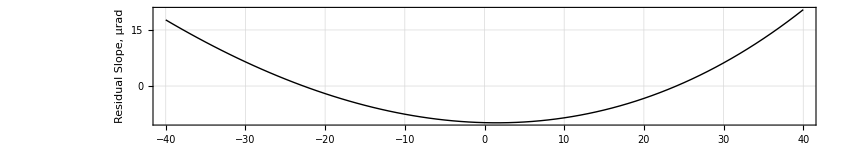
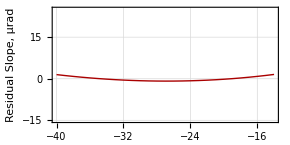
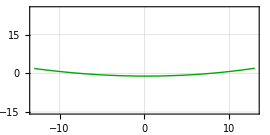
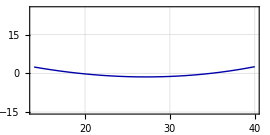
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-},135.245,154.041,136.131,118.467}

```mathematica
threeRegionsOfData[
bl1232HorizKBIdealEllipse
]
```

```mathematica
threeRegionsOfData[
rescaleDataset[
idealEllipseEvaluatedAtCoordsOfMeasurementGivenConjugates[
bl1232HorizKBIdealEllipse,
2.0891,
0.270,
0.00351
],
1/radToMicroRad
]
]
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-},135.243,154.039,136.129,118.465}

#### BL 12.2 .2 Vert Focus KB

```mathematica
idealBL1232VertKB={{-40.,-0.00045756483},{-39.,-0.00044794743},{-38.,-0.00043825367},{-37.,-0.00042848244},{-36.,-0.00041863263},{-35.,-0.0004087031},{-34.,-0.0003986927},{-33.,-0.00038860023},{-32.,-0.00037842449},{-31.,-0.00036816423},{-30.,-0.0003578182},{-29.,-0.00034738511},{-28.,-0.00033686365},{-27.,-0.00032625246},{-26.,-0.00031555018},{-25.,-0.00030475541},{-24.,-0.00029386671},{-23.,-0.00028288261},{-22.,-0.00027180163},{-21.,-0.00026062223},{-20.,-0.00024934284},{-19.,-0.00023796188},{-18.,-0.00022647769},{-17.,-0.00021488862},{-16.,-0.00020319295},{-15.,-0.00019138892},{-14.,-0.00017947475},{-13.,-0.00016744861},{-12.,-0.00015530861},{-11.,-0.00014305284},{-10.,-0.00013067933},{-9.,-0.00011818607},{-8.,-0.00010557098},{-7.,-0.000092831972},{-6.,-0.000079966865},{-5.,-0.000066973444},{-4.,-0.000053849434},{-3.,-0.000040592506},{-2.,-0.000027200268},{-1.,-0.000013670271},{0.,0.},{1.,0.000013813123},{2.,0.000027771745},{3.,0.000041878581},{4.,0.000056136417},{5.,0.000070548115},{6.,0.000085116613},{7.,0.000099844929},{8.,0.00011473616},{9.,0.0001297935},{10.,0.00014502022},{11.,0.00016041967},{12.,0.00017599533},{13.,0.00019175074},{14.,0.00020768958},{15.,0.0002238156},{16.,0.00024013267},{17.,0.0002566448},{18.,0.00027335608},{19.,0.00029027074},{20.,0.00030739314},{21.,0.00032472777},{22.,0.00034227926},{23.,0.00036005237},{24.,0.00037805203},{25.,0.0003962833},{26.,0.00041475142},{27.,0.0004334618},{28.,0.00045242},{29.,0.00047163179},{30.,0.00049110313},{31.,0.00051084014},{32.,0.00053084919},{33.,0.00055113685},{34.,0.00057170992},{35.,0.00059257541},{36.,0.00061374061},{37.,0.00063521304},{38.,0.00065700052},{39.,0.00067911111},{40.,0.00070155321}};
```

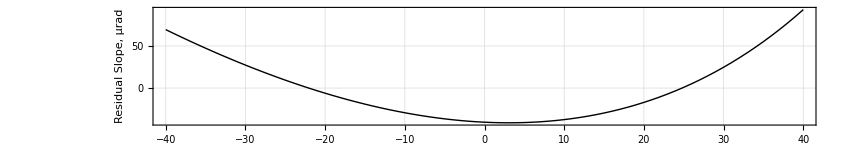
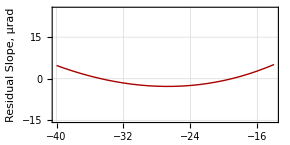
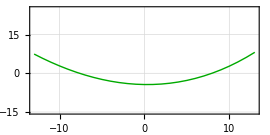
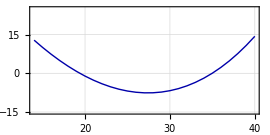
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-},70.4613,93.6172,72.5217,52.8062}

```mathematica
threeRegionsOfData[
idealBL1232VertKB
]
```

```mathematica
threeRegionsOfData[
rescaleDataset[
idealEllipseEvaluatedAtCoordsOfMeasurementGivenConjugates[
idealBL1232VertKB,
2.2236,
0.1355,
0.00351
],
1/radToMicroRad
]
]
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-},70.4613,93.6172,72.5217,52.8062}

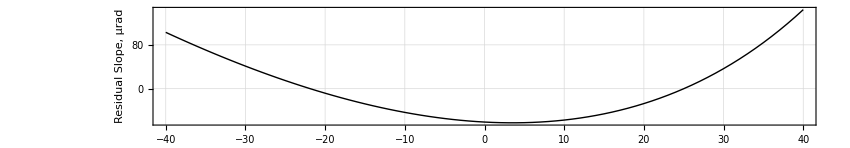
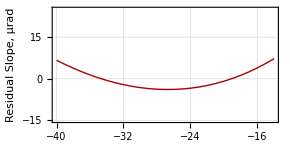
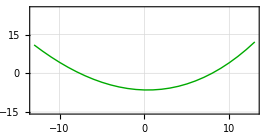
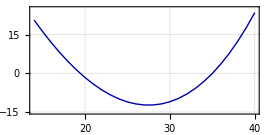
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-},54.0639,75.0792,56.1699,38.7433}

```mathematica
threeRegionsOfData[
rescaleDataset[
idealEllipseEvaluatedAtCoordsOfMeasurementGivenConjugates[
idealBL1232VertKB,
2.2183,
0.1189,
0.004
],
1/radToMicroRad
]
]
```

## Working with Zemax Files

```mathematica
numHeaderRowsInZemaxFile=24;
(* numHeaderRowsInZemaxFile=44;  *)
```

### Processing function ready for automation

#### take two

```mathematica
(* removes the first data column that is the pixel row number  *)
removeRowNumbers[fileData_]:=Drop[
fileData,
None,1]

(* This returns the header as a list of rows *)
rowsOfHeaderInFile[fileName_]:=Module[
{},
file=Import[fileName,"TSV"];

numHeaderRowsInZemaxFile(* hard coded the number of header rows *);

headerContent=Table[
file[[n]],
{n,1,numHeaderRowsInZemaxFile-1(* to skip the column number row *)}];

Return[
Join[headerContent,{{"X pixel","Y pixel","Height Value, arbitrary units"}}]
]
]

(* This returns the data of a Zemax file as a list of data rows, ready for conversion to an image *)
rowsOfDataInFile[fileName_]:=Module[
{},
file=Import[fileName,"TSV"];
numberOfRowsInFile=Length[file];

numHeaderRowsInZemaxFile (* hard coded the number of header rows *);

fileData=Table[
file[[numHeaderRowsInZemaxFile+n]],
{n,1,numberOfRowsInFile-numHeaderRowsInZemaxFile}];

imageDataArray=removeRowNumbers[
fileData
];

Return[imageDataArray]
]

(* This reads the Zemax file, and writes the data converted to tab separated xyz format as a *.dat file,  with the file name suffix 'XYZformat' added *)
zemaxToXYZ[fileName_]:=Export[
ToString[fileName]<>"XYZformat.dat",
Join[
rowsOfHeaderInFile[
ToString[fileName]<>".txt"
],
imgDataToXYZ[
rowsOfDataInFile[
ToString[fileName]<>".txt"
]
]
]
]
```

#### orig

```mathematica
zemaxAnsiToXYZdata[fileName_]:=imgDataToXYZ[
removeRowNumbers[
Drop[
Import[ToString[fileName]<>".txt","Data"],
numHeaderRowsInZemaxFile
]
]
]
```

```mathematica
(*
zemaxAnsiToXYZ[fileName_]:=Block[
{},

zemaxAsXYZ=zemaxAnsiToXYZdata[fileName];

(* This takes the original header *)
headerInfo=Import[ToString[fileName]<>".txt","Data"][[1;;numHeaderRowsInZemaxFile]];

output=imgDataToXYZ[
zemaxAsXYZ];

Export[ToString[fileName]<>"XYZformat.dat",Join[headerInfo,zemaxAsXYZ]];

Return[
zemaxAsXYZ
]
]
*)
zemaxAnsiToXYZ[fileName_]:=Block[
{},

zemaxAsXYZ=zemaxAnsiToXYZdata[fileName];

(* This takes the original header *)
headerInfo=Import[ToString[fileName]<>".txt","TSV"][[1;;numHeaderRowsInZemaxFile]];

(*output=imgDataToXYZ[
zemaxAsXYZ];*)

Export[ToString[fileName]<>"XYZformat.dat",Join[headerInfo,zemaxAsXYZ]];

Return[
zemaxAsXYZ
]
]
```

### reconciling to coordinates

#### This reads through the file name, and picks out the data point number within the scan sequence

```mathematica
charaterNumberInFileNameOfDataPointNum[fileName_]:=Last[
Flatten[
StringPosition[
fileName,
"VID"
]
]
]
```

```mathematica
charaterNumberInFileNameOfDashSeparation[fileName_]:=Last[
Flatten[
StringPosition[
fileName,
"-"
]
]
]
```

```mathematica
coordinateFromFileNameLTPimages[fileName_]:=ToExpression[
StringTake[
fileName,
{charaterNumberInFileNameOfDataPointNum[fileName]+1,
charaterNumberInFileNameOfDashSeparation[fileName]-1}
]
]
```

### determining the position within the file name that has the coordinates

```mathematica
charaterNumberInFileNameOfUnitsmm[fileName_]:=First[
Flatten[
StringPosition[
fileName,
"mm"
]
]
]

charaterNumberInFileNameOfUnitsShiftByUnderscore[fileName_]:=Last[
Flatten[
StringPosition[
fileName,
"by_"
]
]
]

coordinateFromFileName[fileName_]:=ToExpression[
StringTake[
fileName,
{charaterNumberInFileNameOfUnitsShiftByUnderscore[fileName]+1,
charaterNumberInFileNameOfUnitsmm[fileName]-1}
]
]


coordinateFromFileNamesFromSavedTraces[fileName_]:=ToExpression[
StringTake[
fileName,
{charaterNumberInFileNameOfUnitsShiftByUnderscore[fileName]+1,
charaterNumberInFileNameOfUnitsShiftByUnderscore[fileName]+5}
]
]
```

```mathematica
showADataset[dataset_,desc_]:=Show[
ListLinePlot[
dataset,
Frame->True,
Axes->False,
GridLines->Automatic,
FrameLabel->{{ToString[desc],None},{"Focus Step "(*"mirror shift position, mm"*),None}},
LabelStyle->Directive[16, Black,FontFamily->"Helvetica"]
],
ListPlot[
dataset,
PlotStyle->Directive[PointSize->Large]
]
]
```

### LTP image processing

```mathematica
ltpDirectoryFormat[dir_] := "LTP\\LTPScan"<>ToString[dir]<>"\\"

pngsOfMeasRunNumAndScanNumChannel[dirNum_,scanNum_,mainRefQ_]:=FileNames[
ltpDirectoryFormat[dirNum]<>ToString[mainRefQ]<>"*-0"<>ToString[scanNum]<>".png"
]
```

```mathematica
ltpImagedFittedToQuadraticX[dirNum_,scanNum_,MainRefQ_]:=Table[
{
coordinateFromFileNameLTPimages[FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"][[k]]
],

subPixelFitOfQuad[
parseDataAboveThreshold[
normalizeAmplitudeOf[
xTracesAvg[
imgDataToXYZ[
ImageData[
Import[
FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"][[k]]
]
]
]
]
],
quadFittingThreshold],
"full","full"
]
},

{k,1,Length[FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"]]}
]
```

```mathematica
ltpImagedFittedToGaussianX[dirNum_,scanNum_,MainRefQ_]:=Table[
{
coordinateFromFileNameLTPimages[FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"][[k]]
],

subPixelFitUsingGaussian[
normalizeAmplitudeOf[
xTracesAvg[
imgDataToXYZ[
ImageData[
Import[
FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"][[k]]
]
]
]
]
],
"full","full"
]
},

{k,1,Length[FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"]]}
]
```

```mathematica
ltpImagedFittedToQuadraticXcorrectedForROI[dirNum_,scanNum_,MainRefQ_]:=Block[
{},
fits=ltpImagedFittedToQuadraticX[dirNum,scanNum,MainRefQ];
rois=dataFromColumnFunctPosition[dirNum,scanNum,4(* data column *)];

Thread[{
independentVectorOfFunction[fits],
dependentVectorOfFunction[fits]+rois
}]
]
```

```mathematica
ltpImagedFittedToGaussianXcorrectedForROI[dirNum_,scanNum_,MainRefQ_]:=Block[
{},
fits=ltpImagedFittedToGaussianX[dirNum,scanNum,MainRefQ];
rois=dataFromColumnFunctPosition[dirNum,scanNum,4(* data column *)];

Thread[{
independentVectorOfFunction[fits],
dependentVectorOfFunction[fits]+rois
}]
]
```

#### Y direction fitting of images

```mathematica
ltpImagedFittedToQuadraticY[dirNum_,scanNum_,MainRefQ_]:=Table[
{
coordinateFromFileNameLTPimages[FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"][[k]]
],

subPixelFitOfQuad[
parseDataAboveThreshold[
normalizeAmplitudeOf[
yTracesAvg[
imgDataToXYZ[
ImageData[
Import[
FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"][[k]]
]
]
]
]
],
quadFittingThreshold],
"full","full"
]
},

{k,1,Length[FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"]]}
]
```

```mathematica
ltpImagedFittedToGaussianY[dirNum_,scanNum_,MainRefQ_]:=Table[
{
coordinateFromFileNameLTPimages[FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"][[k]]
],

subPixelFitUsingGaussian[
normalizeAmplitudeOf[
yTracesAvg[
imgDataToXYZ[
ImageData[
Import[
FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"][[k]]
]
]
]
]
],
"full","full"
]
},

{k,1,Length[FileNames["LTP\\LTPScan"<>ToString[dirNum]<>"\\"<>ToString[MainRefQ]<>"*0"<>ToString[scanNum]<>".png"]]}
]
```

```mathematica
ltpImagedFittedToQuadraticYcorrectedForROI[dirNum_,scanNum_,MainRefQ_]:=Block[
{},
fits=ltpImagedFittedToQuadraticY[dirNum,scanNum,MainRefQ];
rois=dataFromColumnFunctPosition[dirNum,scanNum,5(* data column *)];

Thread[{
independentVectorOfFunction[fits],
dependentVectorOfFunction[fits]+rois
}]
]
```

```mathematica
ltpImagedFittedToGaussianYcorrectedForROI[dirNum_,scanNum_,MainRefQ_]:=Block[
{},
fits=ltpImagedFittedToGaussianY[dirNum,scanNum,MainRefQ];
rois=dataFromColumnFunctPosition[dirNum,scanNum,5(* data column *)];

Thread[{
independentVectorOfFunction[fits],
dependentVectorOfFunction[fits]+rois
}]
]
```

#### integrating all the pixels of a scan run

```mathematica
integratedPixelsOfLTPimagesFromRunNumAndChannel[runNum_,MainRefQ_,dataPointNum_]:=
Table[
normalizeAmplitudeOf[
xTracesAvg[
imgDataToXYZ[
ImageData[
Import[
pngsOfMeasRunNumAndScanNumChannel[runNum,scanNum,MainRefQ][[
If[MemberQ[fScans8,scanNum],
dataPointNum,
Length[
pngsOfMeasRunNumAndScanNumChannel[runNum,1,"Main"]
]+1-dataPointNum]
]]
]
]
]
]
],
{scanNum,1,8}];


integratedYPixelsOfLTPimagesFromRunNumAndChannel[runNum_,MainRefQ_,dataPointNum_]:=
Table[
normalizeAmplitudeOf[
yTracesAvg[
imgDataToXYZ[
ImageData[
Import[
pngsOfMeasRunNumAndScanNumChannel[runNum,scanNum,MainRefQ][[
If[MemberQ[fScans8,scanNum],
dataPointNum,
Length[
pngsOfMeasRunNumAndScanNumChannel[runNum,1,"Main"]
]+1-dataPointNum]
]]
]
]
]
]
],
{scanNum,1,8}];
```

```mathematica
integratedPixelPlotOf[scanNum_,dataPoint_]:=ListLinePlot[
integratedPixelsOfLTPimagesFromRunNumAndChannel[scanNum,"Main",dataPoint],
PlotRange-> All,
Frame->True,
FrameLabel->{{"Normalized Intensity",None},{"Pixel Coordinate","LTPScan"<>ToString[scanNum]<>",  data point "<>ToString[dataPoint]}},
LabelStyle->Directive[14,FontFamily-> "Helvetica",Black],
Axes->False,
ImageSize->375 ,
AspectRatio->.4 
]

integratedYPixelPlotOf[scanNum_,dataPoint_]:=ListLinePlot[
integratedYPixelsOfLTPimagesFromRunNumAndChannel[scanNum,"Main",dataPoint],
PlotRange-> All,
Frame->True,
FrameLabel->{{"Normalized Intensity",None},{"Pixel Coordinate","LTPScan"<>ToString[scanNum]<>",  data point "<>ToString[dataPoint]}},
LabelStyle->Directive[14,FontFamily-> "Helvetica",Black],
Axes->False,
ImageSize->325
]
```

```mathematica
integratedIntensityTraceOfRun[scanNum_]:= Table[
Mean[
integratedPixelsOfLTPimagesFromRunNumAndChannel[scanNum,"Main",pnt]
],
{pnt,1,Length[pngsOfMeasRunNumAndScanNumChannel[scanNum,1,"Main"]]}
]
```

## OSMS 2 D scan data Processing

#### OSMS 1 - D processing

```mathematica
osmsACXscanCorrectedForXgantryAndACxignal[scanNum_]:=rescaleDataset[
rescaleIndependentVector[
averageOfTracesFunctPosition[scanNum,14],
-1],
-1]
```

### XYZ ordered in time

```mathematica
functionOfTwoMotorScan[dirNum_,dataColNum_]:=Thread[{
dataFromColumnFunctTime[dirNum,1,3](* first motor, generally X *),
dataFromColumnFunctTime[dirNum,1,4](* second motor, generally Y *),
dataFromColumnFunctTime[dirNum,1,dataColNum]
}]

dataColumnOfMatrix[dirNumber_,scanNumber_,dataColumnNumber_]:=Flatten[
Take[
dataMatrix[dirNumber,scanNumber],
All,
{dataColumnNumber,dataColumnNumber}
]
]
```

### breaking up the recorded data into rasterized coordinate data

#### modules to determine if coordinates are increasing or decreasing

```mathematica
valueChangeQwithinTolerance[list_,tolerance_]:=Block[
{listIn=list,
tol=tolerance},

Table[
If[
Round[(1/tol)*listIn[[k-1]] ]≠Round[(1/tol)*listIn[[k]] ],
True,
False],
{k,2,Length[listIn]}]

];

valueChangeQ[list_]:=valueChangeQwithinTolerance[list,.01]

positionOfNewValue[list_]:=Flatten[Position[valueChangeQ[list],True]+1]

valueDifferences[list_]:=
Table[list[[k+1]]-list[[k]],
{k,1,Length[list]-1}]
```

### this is the function that takes the serpentine OSMS data and converts it to a raster format

```mathematica
(* creates an orderd list of the recorded data at each Y-coordinate *)
dataFromColumnFunctSerpentineToRasterCoordPortions[dirNumber_,scanNumber_,dataColumnNum_]:=Block[
{dirNum=dirNumber,
scanNum=scanNumber,
dataCol=dataColumnNum},

xCoordColumn=dataColumnOfMatrix[dirNum,scanNum,3];
yCoordColumn=dataColumnOfMatrix[dirNum,scanNum,4];
columnOfInterest=dataColumnOfMatrix[dirNum,scanNum,dataCol];

numPoints=Length[columnOfInterest];

serpintineXYZ=Thread[{xCoordColumn,yCoordColumn,columnOfInterest}];

posOfYValsChanges=positionOfNewValue[yCoordColumn];
positionsOfInterest=Join[{1},posOfYValsChanges,{numPoints+1(* since the last take is the position - 1 *)}];

numSwitchbacks=Length[posOfYValsChanges];

portions=Table[
Take[serpintineXYZ,{positionsOfInterest[[k]],positionsOfInterest[[k+1]]-1}],
{k,1,numSwitchbacks+1}
];

rasterXYZportions=Table[
If[EvenQ[k],
Reverse[portions[[k]]],
portions[[k]]],
{k,1,Length[portions]}
];

Return[
rasterXYZportions
]

]


(* combines all the Y-traces into a single matrix, and returns the total number of x and y coordinates *)
dataFromColumnFunctSerpentineToRasterCoordsWithStats[dirNumber_,scanNumber_,dataColumnNum_]:=Block[
{dirNum=dirNumber,
scanNum=scanNumber,
dataCol=dataColumnNum},

rasterXYZportions=dataFromColumnFunctSerpentineToRasterCoordPortions[dirNumber,scanNumber,dataColumnNum];

rasterXYZ=Flatten[
rasterXYZportions,
1];

Return[{
rasterXYZ,
Length[rasterXYZportions[[1]] ](*  the number of X-Coords *),
Length[rasterXYZportions] (* the number of Y-Coordinates *)
}]
]
(* takes the above, and drops the number of coordinates from the output *)
(* returns and array of xyz values *)
dataFromColumnFunctSerpentineToRasterCoords[dirNumber_,scanNumber_,dataColumnNum_]:=dataFromColumnFunctSerpentineToRasterCoordsWithStats[dirNumber,scanNumber,dataColumnNum][[1]]

numXcoordsInOSMStwoMotor[dirNumber_,scanNumber_,dataColumnNum_]:=dataFromColumnFunctSerpentineToRasterCoordsWithStats[dirNumber,scanNumber,dataColumnNum][[2]]

numYcoordsInOSMStwoMotor[dirNumber_,scanNumber_,dataColumnNum_]:=dataFromColumnFunctSerpentineToRasterCoordsWithStats[dirNumber,scanNumber,dataColumnNum][[3]]

(*  =================================== *)
xTraceFromOSMSSerpentineWithYcoord[directoryNum_,scanNum_,xTraceNum_,dataColumnNum_]:=Take[
dataFromColumnFunctSerpentineToRasterCoords[directoryNum,scanNum,dataColumnNum],
{
(xTraceNum-1)*numXcoordsInOSMStwoMotor[directoryNum,scanNum,dataColumnNum]+1,xTraceNum*numXcoordsInOSMStwoMotor[directoryNum,scanNum,dataColumnNum]
}
]

xTraceFromOSMSSerpentine[directoryNum_,scanNum_,xTraceNum_,dataColumnNum_]:=Drop[
xTraceFromOSMSSerpentineWithYcoord[directoryNum,scanNum,xTraceNum,dataColumnNum],
None,
{2,2}]
(*  =================================== *)

reconciledDirectCoordsOfOSMSrun[directoryNum_,scanNum_,yTraceNum_,dataColumnNum_]:=translateDataToStartAtZero[
rescaleIndependentVector[
rescaleDataset[
xTraceFromOSMSSerpentine[directoryNum, scanNum,yTraceNum,dataColumnNum],
-1000(* scales to microradians and changes sign to correct for instrument orientation *)],
-1]
];

reconciledFlippedCoordsOfOSMSrun[directoryNum_,scanNum_,yTraceNum_,dataColumnNum_]:=translateDataToStartAtZero[
rescaleIndependentVector[
rescaleDataset[
-Reverse[
xTraceFromOSMSSerpentine[
directoryNum,
 scanNum,
(* upon flipping the recorded data is in reversed order *)
(Length[dataFromColumnFunctSerpentineToRasterCoordPortions[directoryNum,scanNum,dataColumnNum]]+1)-yTraceNum,
dataColumnNum]
],
-1000],
-1]
];

(* =!!!!!!!!≠=!!!!!!!!!!!!≠!!!!!!!!!!!!!!≠= *)(* =!!!!!!!!≠=!!!!!!!!!!!!≠!!!!!!!!!!!!!!≠= *)
(* The function commented out here are not yet reconciled to not average the 1sht and 3rd y-traces upon flipping the substrate *)
(* =!!!!!!!!≠=!!!!!!!!!!!!≠!!!!!!!!!!!!!!≠= *)(* =!!!!!!!!≠=!!!!!!!!!!!!≠!!!!!!!!!!!!!!≠= *)
(*
(* This averages the recorded data into a bunch of X scans over the Y coord Values *)
aBunchOfOSMSscanPortionsFunctRasterCoords[scanDirectoryNumber_,dataColumnNumber_]:=Block[
{dirNum=scanDirectoryNumber,
dataCol=dataColumnNumber},

aBunchOfPortions=Table[
dataFromColumnFunctSerpentineToRasterCoordPortions[dirNum,scnNum,dataCol],
{scnNum,1,numTracesInRun[dirNum]}];

Return[
aBunchOfPortions
]
]

(* This averages the recorded data into a bunch of X scans over the Y coord Values *)
averageOfOSMSscanPortionsFunctRasterCoords[scanDirectoryNumber_,dataColumnNumber_]:=Mean[aBunchOfOSMSscanPortionsFunctRasterCoords[scanDirectoryNumber,dataColumnNumber]]


averageOfOSMSscansFunctRasterCoords[scanDirectoryNumber_,dataColumnNumber_]:=Flatten[
averageOfOSMSscanPortionsFunctRasterCoords[scanDirectoryNumber,dataColumnNumber],
1]

xTraceAvgOfOSMSscanAtYstepNum[scanDirNum_,dataColNum_,YstepNum_]:=Drop[
averageOfOSMSscanPortionsFunctRasterCoords[scanDirNum,dataColNum][[YstepNum]],
None,{2,2}]

yTraceAvgOfOSMSscanAtXstepNum[scanDirNum_,dataColNum_,XstepNum_]:=Drop[
Transpose[
averageOfOSMSscanPortionsFunctRasterCoords[scanDirNum,dataColNum]
][[XstepNum]],
None,{1,1}]
*)
```

```mathematica
directTracesOfOSMSrun[directoryNum_,yTraceNum_,dataColumnNum_]:=Table[
reconciledDirectCoordsOfOSMSrun[directoryNum,scnNum,yTraceNum,dataColumnNum],
{scnNum,1,Round[numTracesInRun[directoryNum]/2]}
]

directTracesOfOSMSrunAveraged[directoryNum_,yTraceNum_,dataColumnNum_]:=averageOfDatasets[directTracesOfOSMSrun[directoryNum,yTraceNum,dataColumnNum]]

flippedTracesOfOSMSrun[dirNum_,yTraceNum_,dataColumnNum_]:=Module[
{directoryNum=dirNum},
numTraces=numTracesInRun[directoryNum];
Return[
Table[
reconciledFlippedCoordsOfOSMSrun[directoryNum,scnNum,yTraceNum,dataColumnNum],
{scnNum,Round[numTraces/2+1],numTraces}
]
]
]

flippedTracesOfOSMSrunAveraged[directoryNum_,yTraceNum_,dataColumnNum_]:=averageOfDatasets[flippedTracesOfOSMSrun[directoryNum,yTraceNum,dataColumnNum]]

AOSSavgOfScansFunctPositionFromStartEnd[directoryNum_,yTraceNum_,dataColumnNum_]:=averageOfDatasets[
Join[
directTracesOfOSMSrun[directoryNum,yTraceNum,dataColumnNum],
flippedTracesOfOSMSrun[directoryNum,yTraceNum,dataColumnNum]
]
];
```

#### correcting the AOSS measurements for gantry wobble calibration

```mathematica
(* !!!   a bit of a hack here   !!! *)
(*  The central coordinates are for a particular mirror for a particualr settign of the gantry coordinates *)
numScanInRunHere=8
(* for the X-Gantry as of August 13th 2018 *)
centerOfRotationX=54.7
(* the start and end points of the mirror scans using the AOSS sequence *)
(*   coordsOf1228=Table[
coordCheck[
xTraceFromOSMSSerpentine[1228,scn,1,15]
],
{scn,1,8}
];
coordsOf1228 // MatrixForm
centerOfRotationXOldForSM2=(Last[coordsOf1228[[1]]]+First[coordsOf1228[[8]]])/2    *)
centerOfRotationXOldForSM2=343.887;


correctingOSMSscanForGantryCalibrationRotatedAbout[directoryNum_,scanNum_,yTraceNum_,dataColumnNum_, gantryCorrection_,centerOfRotation_]:=Module[
{},
(* hack here for speed of processing: assuming 8 scans in an AOSS run *)
numScansInRunHere=8;

dataset=rescaleIndependentVector[(* corrects for direction of scan *)
translateData[(* corrects for the current coordinate system with the center of gantry travel as zero *)
rescaleDataset[
xTraceFromOSMSSerpentine[directoryNum, 
scanNum,
(* conditional to not cross the Y-traces upon flipping the substrate half way throught he AOSS scan sequence *)
If[scanNum>numScanInRunHere/2,
(Length[dataFromColumnFunctSerpentineToRasterCoordPortions[directoryNum,scanNum,dataColumnNum]]+1)-yTraceNum,yTraceNum],
dataColumnNum],
-1000(* scales mrad to microradinas *)],
-centerOfRotation(* -centerOfRotationXOldForSM2-centerOfRotationX *)],
-1];

dataSetCorrectedForGantryWobble=differenceOverCommonRange[
dataset,
cubicSplineWithoutExtrapolation[
gantryCorrection,
independentVectorOfFunction[
dataset
]
]
];

Return[
dataSetCorrectedForGantryWobble
]
]

correctingOSMSscanForGantryCalibration[directoryNum_,scanNum_,yTraceNum_,dataColumnNum_, gantryCorrection_]:=correctingOSMSscanForGantryCalibrationRotatedAbout[directoryNum,scanNum,yTraceNum,dataColumnNum, gantryCorrection,centerOfRotation=centerOfRotationXOldForSM2+centerOfRotationX]
```

8

54.7

```mathematica
reconciledDirectCoordsOfOSMSscanCorrectedForGantryWoble[directoryNum_,scanNum_,yTraceNum_,dataColumnNum_, gantryCorrection_]:=translateDataToStartAtZero[
correctingOSMSscanForGantryCalibration[directoryNum,scanNum,yTraceNum,dataColumnNum, gantryCorrection]
]


reconciledFlippedCoordsOfOSMSscanCorrectedForGantryWoble[directoryNum_,scanNum_,yTraceNum_,dataColumnNum_, gantryCorrection_]:=translateDataToStartAtZero[
-Reverse[
correctingOSMSscanForGantryCalibration[directoryNum,scanNum,yTraceNum,dataColumnNum, gantryCorrection]
]
]

reconciledDirectCoordsOfOSMSscanRunCorrectedForGantryWoble[directoryNum_,yTraceNum_,dataColumnNum_, gantryCorrection_]:=Table[
reconciledDirectCoordsOfOSMSscanCorrectedForGantryWoble[directoryNum,scnNum,yTraceNum,dataColumnNum, gantryCorrection],
{scnNum,1,Round[numTracesInRun[directoryNum]/2]}]

reconciledFlippedCoordsOfOSMSscanRunCorrectedForGantryWoble[directoryNum_,yTraceNum_,dataColumnNum_, gantryCorrection_]:=Table[
reconciledFlippedCoordsOfOSMSscanCorrectedForGantryWoble[directoryNum,scnNum,yTraceNum,dataColumnNum, gantryCorrection],
{scnNum,Round[numTraces/2+1],numTracesInRun[directoryNum]}]
```

```mathematica
AOSSavgOfScansFunctPositionFromStartEndCorrectedForGantryWobble[directoryNum_,yTraceNum_,dataColumnNum_,gantryCorrection_]:=averageOfDatasets[
Join[
reconciledDirectCoordsOfOSMSscanRunCorrectedForGantryWoble[directoryNum,yTraceNum,dataColumnNum,gantryCorrection],
reconciledFlippedCoordsOfOSMSscanRunCorrectedForGantryWoble[directoryNum,yTraceNum,dataColumnNum,gantryCorrection]
]
];
```

## run the collapsed “Function Definitions” cells above all as one, then run the initialization here

## Initialization

```mathematica
(* prompts the user to input the location of the directory t inspect  the contents of *)
SetDirectory[SystemDialogInput["Directory"]];
PrependTo[$Path,Directory[]];
```

### user interface

```mathematica
instrumentChoices=SetterBar[Dynamic[instrumentSelection],{1->"  LTP  ",2->"  DLTP  ",3->"  OSMS  ",4-> "  OSMS 2D serpent  ",5->"  OTHER  "}]

getFileFormat=InputField["",String,FieldHint->"Please enter the format of the file structure"];
```

|  |  |  |

```mathematica
If[instrumentSelection==1,
LTP=True;
DLTP=False;
OSMS=False,
OSMSmap=False];
If[instrumentSelection==2,
LTP=False ;
DLTP=True;
OSMS=False,
OSMSmap=False];
If[instrumentSelection==3,
LTP=False ;
DLTP=False;
OSMS=True,
OSMSmap=False];
If[instrumentSelection==4,
LTP=False ;
DLTP=False;
OSMS=False;
OSMSmap=True];
If[instrumentSelection==5,
getFileFormat
];


LTP
DLTP
```

False

False

### Defining the directory numbers where the data is stored

#### general

```mathematica
utmDirectories={1092,1095,1098};(* From Arthur's measurements July 2014 *)
```

#### DLTP directories

```mathematica
huberStageDirs={1239,1241,1242,1245,1246,1248,1249,1250,1251,1254,1256,1258,1259, 1260,1265,1266, 1269,1270,1272,1273,1274, 1275,1278,1279,1280,1281,1282,1283,1286,1287,1288,1289,1290,1292,1293,1294,1295,1297,1300,1301} ;

dltpMeasDirectories={1784,1786,1787,
1816,1817,1818 (* BL8.0.1.2 M124 *),
1854,
1855,1856,1857(* Amber M102 *),
1931,
1915,1917,
(* BL 11.0.1 M1 Pitch and Roll tests *)
1134,1135,1136,1137,9144(* Vertical up end switcher testing *),9153
};

bl1222kbHorizDirectories={2214(* fast scan 10 mm steps *),
2215(* 1 mm steps FBBF *),
2218(* repeat after shutdown of electrical and air conditioning *),
2219(* repeat of the previous scan *),
2220(* FBBFBFFB in the original AsDelivered settings of BendUp: 0.0mm, BendDw: 0.0mm *),
2221(* FBBFBFFB BendUp: +0.2 mm, BendDw 0.0 mm *),
2222(* FBBFBFFB BendUp: +0.2 mm, BendDw: -0.2 mm *),
2223(* FBBFBFFB BendUp: +0.2 mm, BendDw: +0.2 mm *),
2224(* FBBFBFFB BendUp: +0.4 mm, BendDw: +0.2 mm *),
2225(* FBBFBFFB BendUp: -0.7052 mm, BendDw: +0.7977 mm *),
2226(* FBBFBFFB BendUp: -0.79954 mm, BendDw: +0.8287 mm *),
2227(* Repeat after tapping motor bodies *),
2228(* repeat after 3 hours *),
2229(* repeat after 12 hours *),
2230(* correcting backlash of bends *),
2231(* reset both benders *),
2232,
2233(* LTP air supply turned on, no other changes *),
2234(* repeatability of DLTP with LTP air supply flux *),
2235(* Repeat after 10 hours with LTP air supply flux *)
};
 
bl931WX6480sphereDirectories={
(*direct *)1937,
(* tilted *) 1938, 
(* translated *)1939, 
(* translated, tilted *)1940,(* repeatability *)1941,
(* sagittal *)1942,(* repeatability *)1943,(* sagittal tilted *)1944, (* tilted by 190 urad *)1945,
(* translated 4.5 mm *)1946};

bl931ToroidDirectories={1948,1949,
1950,
1951 (* tilted by 183 urad *),
1952(* tilted back 63 urad *)};

bl1032M4directories=Join[Table[k,{k,1859,1912}],Table[j,{j,1919,1925}]];

qerlinMeasDirectorits = {
1955,
1956,
1957,
1958,
1965,
1974,
1975(* translated -2 mm *),
1977(* tilted 142 urad *),
1978(* repeat of last scan *),
1979(* tilted by 30 urad *),
1981(* fake motor stability test *),

1984(* flipped, new trace *),
1985(* tilted by 28.6 urad *),
1986(* tilted by -136 urad *),
1987(* translated by 2.25 mm *),
1988(* repeat *),

1989(* lowered substrate 10 mm to match the first trace 2.0 mm steps *),
1990(* two scans FB 0.2 mm steps *),
1991(* full scan flipped *),
1992(* tilted by 140 urad*),
1993(* repeat *),

1994(* flipped agian 2nd trace flipped *),
1995(* second Trace Flipped, titled by -141 urad *),
2006(* repeat scan after the on-the-fly runs *),

2019 (* SM2 Ellipse *),
2025(* first trace; center at -30.4185 *),
2026(* tilted by -140 urad *),
2027(* translated by 2 mm; center at -28.4185 *),
2028(* tilted by 140 urad *),
2029(* Trace 2 first scan *),
2030(* Trace 2 tilted *),
2031(* Trace 2 Translated -2 mm; center aT -30.4185 *),
2032(* Trace 2 Translated -2 mm; center aT -30.4185 titled -140 urad *),
2033 ,
2034 (* XX bad scan; hutch doors open XX *),
2035,
2036(* Flipped Substrate: Trace 1 Reversed center at -30.418 *),
2037(* Trace 1 Reversed Tilted; center at -30.418 *),
2038(* Trace 1 Reversed Tilted; Translated center at -28.418 *),
2039 (* scan stopped due to fire *),
2040 (* Trace 1 Reversed Titled back translated center at -28.418 *),
2041 ,
2042 (* Trace 2 reversed Tilted Translated cneter at -28.4185 *), 
2043 (* Trace 2 reversed Tranlsated cneter at -28.4185 *),
2044 (* Trace 2 reversed cneter at -30.4185 *),
2045 (* Trace 2 reverse tilted center at -30.4185 *),
2046 (* Trace 1 reversed center at -30.4185 *),
2047 (* Trace 1 reversed center at -30.4185 *),
2048,
2052(* Trace 1 after realigning the iris, and checking the coordinate ends via a camera *),
2053 (* Trace 1 after realigning the iris, and checking the coordinate ends via a camera *),
2054 (* Fake Motor Stability test *),
2055(* 10mm detail about reference end *),
2056(* After adjusting the air line pressure and flow, shuuting off the LTP supply, a full scan about coordinates based on the camera defined center. *),
2057(* stability scan *),
2058(* measurement run *),
2059 (* stability scan with no mirror d-oh! *),
2062(* stability scan *),
2063(* stability scan *),

2064 (* Qerlin SM3: fast scan FB 1 mm steps *),
2066(* Trace Line 2 Flipped first complete scan *),
2067(* Trace Line 2 Flipped titled by 140 urad *),
2068(* Trace Line 1 Flipped *),
2069(* Trace Line 1 Flipped tilted *),
2070(* Trace Line 2 Direct *),
2071(* Line 2 Direct shifted scan cordinates by 0.1 mm *),
2072(* Line 2 tilted *),

2073(* Line 1 Direct Air pressure optimized *),
2074(* Line 1 direct tilted Air pressure optimized *),

2075(* Line 1 direct tilted air pressure for LTP *),
2076(* Line 1 direct air pressure for LTP *),
2077(* repeat stability *),

2078(* trace Line 2 direct *),
2079(* trace Line 2 direct *),
2080(* trace Line 1 Flipped *),
2081(* trace Line 1 Flipped *),
2082(* trace Line 2 Flipped *),
2083 (* trace Line 2 Flipped *),

(* QERLIN M204 *)
2094 (* first scan *),
2095(* Trace Line 1 Flipped realigned iris adn substrate position *),
2096(* Trace line 1 Flipped tilted *),
2097(* Trace Line 2 Flipped *),
2098(* Trace Line 2 Flipped Tilted back *),
2099 (* Trace Line 2 Repeat Stability scan *),
2100 (* Trace Line 2 Tilted to -1418.5 urad at pole; +3907 urad at downstream end *),
2101 (* Trace Line 2 Tilted to +377.2 urad at pole *),
2102 (* Trace Line 2 Translated +52.25 mm *),
2103(* Trace Line 2 Translated tilted *),
2104 (* Trace Line 1 Flipped Substrate to Direct orientation *),
2105(* Trace Line 1 Tilted by +140 urad *),
2106 (* Trace Line 1 roatated clockwise to +1418urad at 8.7mm *),
2107(* Trace Line 1 direct ACX +527urad at 8.7 mm *),
2108(* Trace Line 2 Direct *),
2109(* Trace Line 2 Direct tilted 140 urad *),

2127(* 15m ROC *),

(* House Air Pressure Inspection *)
2173,2174,2175,
2177(* long term stability scan April 20th +-2018; partial as it is continuing *),
2179(* continued long term pressire stability  started April 26th *),

2180(*fake moor pressure testing*),2181,2182
(*QERLIN m201*),
2184 (* central Trace *),
2185 (* Fake Motor *),
2186(* bottom trace *),
2187(* middle-top trace *),
2188 (* middle bottom trace *), 
2189,2190,2191 (* Fake motor scans *),
2192 (* Top Trace *),

(* QERLIN M203 Ellipse *)
2195,2196  (* first fast scans with 10 mm steps *),
2197(* Trace Line 1 Flipped *),
2198 (* Trace Line 1 Flipped tilted by 140 urad *),
2201 (* Trace Line 1 Flipped translated by 3.65 *),
2202(* Trace Line 1 Flipped translated by 3.65, tilted by 140 urad *),
(* Flipped substrate *)
2203(* Trace Line 2 direct *),
2204(* Trace LIne 2 direct tiletd *),
2205(* Trace Line 2 Direct at +508 urad *),
2206(* Trace Line 2 Direct Tilted to +368 *),
(* raised platform 10 mm *)
2207(* Trace Line 1 Direct *),
2208(* Trace Line 1 Direct Tilted *),
(* Flipped Substrate *)
2209,
2210
};

bl1232KBsDirectories={1210,1211,1212,1213,2114,2115,2116,2117,2118,
2120(* 1 week stability test *),
2122(* corrected coodinates *),
2123(*  adjusted benders -9.0 -9.55 *),
2124};

fifteenMeterROCsubstrateDirectories={
(* center at -302.27 mm *)2149,2150,
(* center at -229.45 mm *)2136,2137,2138,
(* center at -152.9 mm *)2131,2132,2133,2134,2135,
(* center at -77 mm *)2129,2130,
(* center at -0.75 mm *)2127,2128,
(* center at +74.16 mm *)2144,2146,
(* center at +150.42 mm *)2142,2143,
(* center at +226.55 mm *)2140,2141,
(* center at +302.85 mm *)2147,2148,
2144,2145};

stabilityScanning=Table[s,{s,2151,2157}](* During the CHW work *);

pressureTestingOfSupplyAir={2166};

dltpDirectories=Sort[Join[huberStageDirs,dltpMeasDirectories,bl1032M4directories,bl931WX6480sphereDirectories,bl931ToroidDirectories, qerlinMeasDirectorits ,bl1232KBsDirectories,
fifteenMeterROCsubstrateDirectories, stabilityScanning,pressureTestingOfSupplyAir,bl1222kbHorizDirectories]];
```

```mathematica
dltpDirectories
```

{1134,1135,1136,1137,1210,1211,1212,1213,1239,1241,1242,1245,1246,1248,1249,1250,1251,1254,1256,1258,1259,1260,1265,1266,1269,1270,1272,1273,1274,1275,1278,1279,1280,1281,1282,1283,1286,1287,1288,1289,1290,1292,1293,1294,1295,1297,1300,1301,1784,1786,1787,1816,1817,1818,1854,1855,1856,1857,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1915,1917,1919,1920,1921,1922,1923,1924,1925,1931,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1948,1949,1950,1951,1952,1955,1956,1957,1958,1965,1974,1975,1977,1978,1979,1981,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,2006,2019,2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2045,2046,2047,2048,2052,2053,2054,2055,2056,2057,2058,2059,2062,2063,2064,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2081,2082,2083,2094,2095,2096,2097,2098,2099,2100,2101,2102,2103,2104,2105,2106,2107,2108,2109,2114,2115,2116,2117,2118,2120,2122,2123,2124,2127,2127,2128,2129,2130,2131,2132,2133,2134,2135,2136,2137,2138,2140,2141,2142,2143,2144,2144,2145,2146,2147,2148,2149,2150,2151,2152,2153,2154,2155,2156,2157,2166,2173,2174,2175,2177,2179,2180,2181,2182,2184,2185,2186,2187,2188,2189,2190,2191,2192,2195,2196,2197,2198,2201,2202,2203,2204,2205,2206,2207,2208,2209,2210,2214,2215,2218,2219,2220,2221,2222,2223,2224,2225,2226,2227,2228,2229,2230,2231,2232,9144}

#### LTP directories

```mathematica
ltpDirList={
1562,1563  (* olde BL 6 M1 from May-June 2009 *),
(* ====================================================== *) (* ====================================================== *)
(* UTM scans for a range of sagittal positions of the old LTP camera on the old table *)
3634, (* sag: 792 pixels *)
3636, (* sag: 954 pixels *)
3630, (* sag: 1085 pixels *)
3637, (* sag: 1235 pixels *)
3631, (* sag: 1370 pixels *)

3627,3628, (* repeatability tests *)
3641,3642, (* carriage air off repeatability tests *)
3657,3658,3659,
(* ====================================================== *)(* ====================================================== *)
(* after shielding camera from stray light within the hutch *)

3918 (* 40 m ROC B -> A *),

3922 (* UTM scan with 1s avg time *),
3926 (* UTM scan with 1s avg time *),

3931 (* UTM scan with 5s avg time *),
3932 (* UTM scan with 5s avg time *),

3933 (* 40 m ROC A -> B *),

3971,
3973,

4477,4478,4479, (* 12.2.1 *)
4485,4486, (* 4 peak mode *)
4495,4496,4498,4503,4504, (* 12.2.2 Bender *)


(* Amber M102 *)4506,4512,4515,4516,

4517,4518,4519,4520,4521,4522,4523, (* ref calib *)
4524 ,(* BL10.3.2 M3 *)
4525,4526,4527, (* main & ref switched *)
4528, (* BendUp = -230.8   BendDw = +246.3 *)
4529,   (* BendUp = -230.8   BendDw = +1020.2 *)
4530 , (* BendUp = 510.5   BendDw = +1020.2 *)
4532,  (* efective [1] file for Hingette analysis, +50 um change;  Translated mirror and repositionied LVDT *)
4534, (* efective [0] file for Hingette analysis; *)
4535, (* efective [2] file for Hingette analysis; +50 um change*)
4536, (* LabView Crashed during the fourth scan *)
4537 ,(* *)
4538,
4539,
4540,
4541,
4542,
4543,
4544,4545,4546,4550,4551,4552,4553,4554,4555,4556,4557,4558 (* Stability Tests bendDw=-13.42   bendUp=+86.99;  *),
4559,4560,4561,4562,4563(* after shaking the assembly *),
4564,4565,4566 ,4567,4568(* after shaking again *),
4569,4570,4571,4572,4573,4574(* resetting the benders *),
4575 (* 0fake motor scan *),
4576 ,4577,4579,4580,4581(* fake motor hutch open *),
4583 (* BL10.3.1 M4 scan, 5 mm steps *),
4584,4585 ,4586(* BL10.3.1 M4 scan, 1 mm steps *),
4587 (* After slight realignment *)
};

gratingForAlekiFedorovRuns={4622};

ltpDirectories=Join[
ltpDirList,

Table[scnNum,{scnNum,4588,4612}],
Table[scnNum,{scnNum,4614,4620}],
gratingForAlekiFedorovRuns,
{4624(* Hig[1] *),4625 (* Hig[0] *),4626(* Hig[2] *)},
Table[scnNum,{scnNum,4627,4679}],
{4680,
4681(* FBBF 1mm step original Bend setting *),
4682 (* 1 scan bend dw to 10,000 *),
4683 (* 1 scan 50 mm steps bend Dw to 50,000 *),
4684,
4685 (* clear aperture scan, 1 mm steps, BendDw 200,000 *),
4686 (* 50 mm steps bend Up to 50,000 *), 
4688 (* 50 mm steps end Up to 150,000 *),
4689 (* 50 mm steps end Up to 200,000 *),
4690,
4691 (* tilted the assembly by 278 pixels *),
4693 (* filter removed *),
4694  (* fileter replaced; full scan FBBF  bendDw: 200,000; bendUp: 200,000 *),
4695 (* bendDw: 300,000; bendUp: 200,000 *),
4696 (* bendDw: 300,000; bendUp: 300,000 *),
4697 (* 4-peak test *),
4698 (* 4-Peak run *),
4699 (* 4-peak thresholds changed *),
4700 (* threshold adjustmemnt *),
4701,
4705 (* adjusted the polarization and the 4-Peak separation *),
4706 (* tilted mirror *),
4707 (* tilted mirror back *),
4708,
4709 (* BendUp(LR?) 300,000; BedDw(RL?) 300,000 *),
4710  (* BendUp: 300,000;  BendDw to 350,000 *),
4711 (* BendUp: 350,000; BendDw: 350,000 *),
4712  (* 10 mm step; BendDW = 350,000, BendUp = 350,000 *),
4713 (* 10 mm step; BendDW = 350,000, BendUp = 375,000 *),
4715 (* 10 mm step; BendDW = 375,000, BendUp = 375,000 *),
4716,
4720,
4721,
4722,
4723,
4724,
4725,
4726,
4727,
4728 ,
4729  (* has NaN points *),
4730 (* centroid scan not-4peak *),
4731,
(* BendDwLeft: 333,832;  BendUpRight: 371,260 *) 4732 (* 2030 pixels *),4733 (* 1962 pixels *),4734 (* 1900 pixels *),
4735,
(* BendDwLeft: 331,254;  BendUpRight: 371,260 *) 4736 (* 1899 pixels *),4737 (* 1958 pixels *),4738 (* 2021 pixels *) ,

(* BendDwLeft: 331,254;  BendUpRight: 369,164 *) 4739 (* 2021 pixels *), 4740 (* 1960 pixels *), 4742 (* 1902 pixels *),

(* cahnged bend settings *)
(* BendDwLeft: 331,836;  BendUpRight: 368,998 *) 
4743,
4744,
4745,
4746,
4747,
4748,
4749,
4750,
4752 (* adjusted the mask and polarization *),
4753, (* repeat of previous scan *)
4754 (* motor error *) ,
4756,
4757,
4758,
4759,
4760,
4761,
4762 (* Repeat of the last scan to test 28 hour stability *),
(* rotating Yaw by moving the uplstrem end in 20 um incriments *) 4763,5764,4765,4766,4767,4768,
 4769,4770, (* new Yaw two scans *)
4771  (* tilted *),
4772 (* tilted more *),
4780 (* two beams quadratic fit *),

4800(* holographic grating direct centroid *),
4801(* holographic Grating tilted gaussian *),
4802(* holographic Grating tilted centroid *),
4803(* holographic Grating tilted centroid *),

4804 (* 5 mm steps 2 scans F-B *),
4809  (* reference beam off 45 deg mirror 1mm steps *),
4811 (* tilted to 3.74 deg for littrow configuration *),
4812(* repeatability *),
4815(*  zero order via rotating the 45 deg mirror *),

4852(* QERLIN SM2  downstream Left  Trace line 2(?):
Calibration via measurements with QERLIN SM2 front trace 5 mm shift ser # on the right top side[-556.6,-406.6] 1mm increment 1st whole run of 8 scans *),
4855(* Calibration via measurements with QERLIN SM2 front trace 5 mm shift ser # on the right top side[-556.6,-406.6] 1mm increment 2st whole run of 8 scans *),
4857(* Calibration via measurements with QERLIN SM2 front trace 5 mm shift ser # on the right top side[-556.6,-406.6] 1mm increment 3rd whole run of 8 scans *),
4858(* QERLIN SM2 with One Beam 
Calibration via measurements with QERLIN SM2 front trace 5 mm shift ser # on the right top side one beam[-555.405,-405.405] 1mm increment 3rd whole run of 2 scans *),
4859 (* SM2 one peak centroid fitting *),
4860(* stable laser *),
4866(* stable scan over different range *),
4879(* after software update *),
4890, 4891,(* with saved pngs *)
4892,
4890,4894,4896,
4897,
4905(* 23 Jan 2018; two beams with main at 2 folding mirror bounces *),
4917,4918,4919(*  fake motor scans one beam *),
4921,
4925,"4925reproc","LTPScan4925reprocThreshold",
4926(* updated wavemeter info *),
4928(* single image capture *),
4929(* avg 10 *),
4930(* camera temp control turned off (threshold low for running) *),
4931(* modified the threshold for scan running levels*),
4932,4933(* Mirror on carriage head for Reference Channel *),
4934,
4935 (* air pressure off, centroid fit *),
4936(* single peak quad fit *),

4937 (* Two pressure gagues *),
4938,4939,4940,
4941(* thermocouples installed *),
4942,
4943(* thermocouples secured *),4944,

4946(* QERLIN SM2 *),4947,
4948(* single peak quad slope fitting, with delay between scans *),4949,4950,
4954(* two peak quad fitting *),
4956(* two beams repeat *),
4957(* two beams carriage scan after adjusting the phase repeat 2 ABORTED during 7th run*),
4958(* two beams carriage scan after adjusting the phase repeat 4 *),
4959(* two beams carriage scan after phase adjust repeat 2 *),
4961 (* two beams carriage scan after phase adjust repeat 3 *),
4962 (* two beams carriage scan after phase adjust repeat 4 *),

4964 (* One beam fake motor during CHW work *),
4965(* One beam fake motor, just after facilities CHW work complete *),4966(* One beam fake motor *),
4968(* One beam Carriage after chilled water work complete *),
4969(* One beam Carriage after chilled water work complete repeat *),
4971(* One beam Carriage after chilled water work tilted by 560 urad *),
4972(* One beam Carriage after chilled water work tilted by 560 urad repeat *),
4973(* delay between scans changed to 1 second *),

4979(* Gantry scan with main channel reflecting from mirror on the carriage *),4980,4981,
4983(* Gantry scan with on beam (horizontal prism blocked) *),4984,

4991 (* Fake Motor 21 points *),

4992,4993,4995,
5000(* 2 references *), 5001(* with air dryer on *),
5002(* +-90 mm about -400 *),
5003(* fake motor stability scan  *),

(* QERLIN SM2 *)
5006,5007,
5009,5010,5011,

(* AMBER grating substrate from Imprentus *)
(*  Zero Order *)
5014,
5020,
(* Littrow  *)

5022,
5024,
5025,
5026,5027,
(* 0.02 mm over 2mm range *)5028,5029,
5030,
5031(* 10 micron step *),5032,5033,
5039 (* [-483.15,-471.15] 0.5 mm *),
5040  (* [-483.15,-471.15] 0.1 mm increment;8 scans 12 mm scan range *),
5041(* [-483.15,-481.15] 0.02 mm increment;8 scans *),

(* air pressure testing *)
5043,5044,5045,5046,5047,5048,

5054(* AMBER M101 mounted on flange; side facing *), 
5055(* central portion , between the Covers *),
5056(* left protion *),
5057(* right poortion *),
5058(* center shifted *),
5059(* center shifted repeat *),

(* BL12.2.2 vert KB *)
5061(* As delivered bends nominally at zero *),
5062(* BendDw to +0.20 mm *),
5063(* BendDw to +1.00 mm *),
5064(* BendUp to +0.20 *),
5065(* BendUp to +0.50 *),
5066(* BendUp to -0.019, BendDw to +1.9 *),
5067(* BendUp to 0.00, BendDw to +1.985 *)
}
]
```

{1562,1563,3634,3636,3630,3637,3631,3627,3628,3641,3642,3657,3658,3659,3918,3922,3926,3931,3932,3933,3971,3973,4477,4478,4479,4485,4486,4495,4496,4498,4503,4504,4506,4512,4515,4516,4517,4518,4519,4520,4521,4522,4523,4524,4525,4526,4527,4528,4529,4530,4532,4534,4535,4536,4537,4538,4539,4540,4541,4542,4543,4544,4545,4546,4550,4551,4552,4553,4554,4555,4556,4557,4558,4559,4560,4561,4562,4563,4564,4565,4566,4567,4568,4569,4570,4571,4572,4573,4574,4575,4576,4577,4579,4580,4581,4583,4584,4585,4586,4587,4588,4589,4590,4591,4592,4593,4594,4595,4596,4597,4598,4599,4600,4601,4602,4603,4604,4605,4606,4607,4608,4609,4610,4611,4612,4614,4615,4616,4617,4618,4619,4620,4622,4624,4625,4626,4627,4628,4629,4630,4631,4632,4633,4634,4635,4636,4637,4638,4639,4640,4641,4642,4643,4644,4645,4646,4647,4648,4649,4650,4651,4652,4653,4654,4655,4656,4657,4658,4659,4660,4661,4662,4663,4664,4665,4666,4667,4668,4669,4670,4671,4672,4673,4674,4675,4676,4677,4678,4679,4680,4681,4682,4683,4684,4685,4686,4688,4689,4690,4691,4693,4694,4695,4696,4697,4698,4699,4700,4701,4705,4706,4707,4708,4709,4710,4711,4712,4713,4715,4716,4720,4721,4722,4723,4724,4725,4726,4727,4728,4729,4730,4731,4732,4733,4734,4735,4736,4737,4738,4739,4740,4742,4743,4744,4745,4746,4747,4748,4749,4750,4752,4753,4754,4756,4757,4758,4759,4760,4761,4762,4763,5764,4765,4766,4767,4768,4769,4770,4771,4772,4780,4800,4801,4802,4803,4804,4809,4811,4812,4815,4852,4855,4857,4858,4859,4860,4866,4879,4890,4891,4892,4890,4894,4896,4897,4905,4917,4918,4919,4921,4925,4925reproc,LTPScan4925reprocThreshold,4926,4928,4929,4930,4931,4932,4933,4934,4935,4936,4937,4938,4939,4940,4941,4942,4943,4944,4946,4947,4948,4949,4950,4954,4956,4957,4958,4959,4961,4962,4964,4965,4966,4968,4969,4971,4972,4973,4979,4980,4981,4983,4984,4991,4992,4993,4995,5000,5001,5002,5003,5006,5007,5009,5010,5011,5014,5020,5022,5024,5025,5026,5027,5028,5029,5030,5031,5032,5033,5039,5040,5041,5043,5044,5045,5046,5047,5048,5054,5055,5056,5057,5058,5059,5061,5062,5063,5064,5065,5066,5067}

```mathematica
swapToLTP
```

{False,False,True,False}

```mathematica
(1/.0011)/60
```

15.1515

#### OSMS directories

```mathematica
osmsDirectoriesList={
(* early measurements *)
1001,1002,

1154,1155,1159,1164,1166, 
1173 (* #2 substrate flat *),
1174 (* #2 substrate flat flipped *),
1175 (* #2 substrate flat flipped repeatability *),
1176,1177,
1178(* QERLIN SM1 *),
1180(* central sagittal scan *),
1181(* oops, fake y-motor *),
1182(* serpintine scan of sagittal traces 4+1 *),
1183(* repeat stability test *),
1185(* processing test 6 mm steps *),
1187 (* 2D surface map of clear aperture *),
1188(* 1D central sagittal trace *),
1189(* sagittal scan about the zero y- coordinate *),
1190(* central sagittal scan after translating the substrate by 1.14 mm *),
1191(* Y-sled translation to test tang traces *),

1192(* Y-sled primary serpintine scan of three tangential traces *),
1193(* X-Gantry primary serpintine scan of three tangential traces  *),

1194(* InSync#2 Tang *),

1197(* InSync#2 Sagittal *),
1198(* Stability test; fake motor *),
1199(*  QERLIN SM1 Tang 3 traces tilted by 145 urad *),
1209 (* QERLIN SM1 Tang 2 traces with automatic flipping and tilting *),
1210(* QERLIN SM1 set for AOSS *),
1221(* Air pressure set for LTP, after adjusting the rotation speed *),
1223(* after optimizing the air pressure *),
1224(* stability scan *),
1225(* repeatability *),

1228(* SM2 AOSS scan Tangential traces air set for LTP*),
1230(* SM2 sagittal scan with air set for LTP *),
1232(* sm2 sagittal scans with air optimized *),
1233(* sm2 repeat sagittal scans with air optimized *),
1235(* another attempt at sagittal scans, this time using a positive direction to the y-gantry *),

1238 (* AMBER GB3 *),
1239 (* AMBER sphere 90X90 mm *),
1240 (* AMBER sphere 90x90 rotated to sagittal scans *),
1241 (* AMBER sphere 90x90 rotated to sagittal scans with AOSS: wrong flp range*),
1242 (* AMBER sphere tangential wrong range*),
1243 (* AMBER sphere tangential  *),

1251(* BL12.3.2 KB M4 initial setting    Hig (1) *),
1252(* bend Up delta -50 um              Hig (0) *)  ,
1253(* bend Dw delta -50 um              Hig (2) *),
1254(*  *),
1255(* adjusted to predictions *),
1256(* minor adjustment *),


1271,
1272,
1273(* STABILITY *),1274, 1275,1276,1277,1278,1279,1280 ,
1281,1282(* Tilted by -145 urad *),
1283 (* tilted back, and stability test *),
1284,1285,1286,1287,
1288,1289,
1290,1291,

1292,
1293(* 500nm stepping of the P2 motor *),
1294(* repeat *),

(* Rectangular aperture alignment *)
1295,1296,1297,1298,1299,
(* Chirped profile *)
(* 1.5 mm x 3.0 mm Rectangular Aperture *)
1300,1301,
(* second stripe *)
1302,1303,
(* 2.5 mm circular aperture., serpentine scans of both stripes *)
1304,
(* 1.5 mm X 2.0 mm Rectangular Aperture *)
1305,
(* 2.0 mm X 3.0 mm Rectangular Aperture *)
1306,

1348(* Y-Sled scan with AC wobble monitor *),
1349(* tubing and 5 mm aperture in place *),
1352(* Four Autocollimaotors; #3 on the DLTP, #4 on OSMS right for X-Gantry *),
1353(* Four Autocollimaotors; #3 on the DLTP, #4 on OSMS right for X-Gantry wiht stage adjusted by 140 urad in X and Y *),
1354(* re-aligned AC stage *),
1355,1356 (* had AI error *),
1357,
1358 (* fake motor scan started just before closing the hutch *),
1359(*  fake motor *),
1360(* fake motor with "Y Axis Lift" disabled *),
1361,1362 (* fake motor stability with optical path tubes on all but AC-4 looking at the X-Gantry *),
1363,
1364 (* New AC is now on the left side, looking at the UTM *),
1365 (* Fake Motor  8 hour stability compare to X-Gantry scan *),
1366,
1367,
(*  first fast UTM scan *)
1371(* 100 urad steps *),
1372(* UTM scan +-5mrad 10 urad steps *),
1373(* +- 150 urad with 0.5 urad steps *),
1374 (* +- 150 urad with 0.5 urad steps repeat *),
1375(* UTM scan +-5mrad 10 urad steps *),
1376(* repeat of UTM scan after realigning the vertical AC *),
1377(* repeat *),
1378(* [-150 urad to +150 urad] 0.25 urad step FBBFBFFB *),
1379(* repeat *)
};

tiltmeterScans={
(* Tilt stages *)
1313(* bad connection and signal from Tilt2 *),
1314(* still bad *),
1317(* First working scan using Tilt 1 with enclosure and Tilt 2 exposed P1 [-19.9 to -20.1] 0.005 steps *),
1318(* Stability scan Fake motor *),
1319(* repeatability P1 [-19.9 to -20.1] 0.005 steps *),
1321(* Fake motor fast scan *),1322(* fake motor fast scan *),
1327(* P1 scan with hutch open; turned on lamp at 12:55 at start of 5th scan *),
1328(* Stability scan with hutch open, lamp on signal conditioner *),
1329(* continuation of the s1328 that stopped at the end of the second scan *),
(* Tilt 1 enclosure replaced with the anodized aluminum sensor exposed *)
(*Tilt1 alloy exposed, tilt 2 stainless exposed *)
1331(* stability scan  *),
1332(* P1 scan *),
1333 (* stability *),
1334(*  P1 scan repeat *),
(*P2 (stainless exposed) rotated 180 deg to Flp orientation *)
1336 (* stability *),
1337 (* P1 scan *),
1339(* Fake motor, lamp in position but turned off *),
1340(* Fake motor immediately after turning on the lamp *),
1341(* P1 scan with lamp on the Tilt2 *),
1342(* Fake motor immediately after turning of the lamp *),
1343(* P1 with all air turned off at the front panel XROL Tip Stage.vi *),
1344(* Air pressure turned off, then back on, Stability Scan  *)
};

osmsDirectories=Join[osmsDirectoriesList,tiltmeterScans];

osmsMAPdirectories={1003,1004};

flippedQ[directory_]:=Null

scanFileDirectories=Sort[
If[
LTP,ltpDirectories,
If[DLTP,dltpDirectories,
If[OSMS,osmsDirectories,
If[OSMSmap,osmsMAPdirectories,
other=True]
]]]
]
```

{1001,1002,1154,1155,1159,1164,1166,1173,1174,1175,1176,1177,1178,1180,1181,1182,1183,1185,1187,1188,1189,1190,1191,1192,1193,1194,1197,1198,1199,1209,1210,1221,1223,1224,1225,1228,1230,1232,1233,1235,1238,1239,1240,1241,1242,1243,1251,1252,1253,1254,1255,1256,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1313,1314,1317,1318,1319,1321,1322,1327,1328,1329,1331,1332,1333,1334,1336,1337,1339,1340,1341,1342,1343,1344,1348,1349,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1371,1372,1373,1374,1375,1376,1377,1378,1379}

```mathematica
swapToOSMS
```

{True,False,False,False}

## Initialization here : this goes into the scan file directory and copys the *.txt files to *.dat files that then can be imported and parsed

```mathematica
(* This function takes the original raw data *.txt files and copies them to *.dat files *)
(* While not explicitly necessary, it is a precaution against altering or overwriting the raw data files *)

initializeLTPfiles :=For[n=1,n≤ Length[ltpDirectories],n++,
copyWithRenaming[ltpDirectories[[n]] ]
];

initializeDLTPfiles :=For[n=1,n≤ Length[dltpDirectories],n++,
copyWithRenaming[dltpDirectories[[n]] ]
];

initializeOSMSfiles :=For[n=1,n≤ Length[osmsDirectories],n++,+
copyWithRenaming[osmsDirectories[[n]] ]
];

initializeOSMSmapFiles :=For[n=1,n≤ Length[osmsMAPdirectories],n++,
copyWithRenaming[osmsMAPdirectories[[n]] ]
];+

If[LTP,
initializeLTPfiles;
swapInstrumetnsBetweenLTPandDLTP,
initializeDLTPfiles;
swapInstrumetnsBetweenLTPandDLTP
]

If[DLTP,
initializeDLTPfiles;
swapInstrumetnsBetweenLTPandDLTP,
initializeLTPfiles;
swapInstrumetnsBetweenLTPandDLTP
]

If[OSMS,
initializeOSMSfiles
]

If[OSMSmap,
initializeOSMSmapFiles]
(* 
initializeFiles :=For[n=1,n≤ Length[scanFileDirectories],n++,
copyWithRenaming[scanFileDirectories[[n]] ]
];
initializeFiles
*)
```

CopyFile::filex: Cannot overwrite existing file OSMS\AutoColl 1001\AC_AIF1001-1.dat.

CopyFile::filex: Cannot overwrite existing file OSMS\AutoColl 1001\AC_AIR1001-2.dat.

CopyFile::filex: Cannot overwrite existing file OSMS\AutoColl 1002\AC_AIF1002-1.dat.

General::stop: Further output of CopyFile::filex will be suppressed during this calculation.

```mathematica
A
```

```mathematica
swapToOSMS
```

{True,False,False,False}

```mathematica
swapToLTP
```

swapToLTP

```mathematica
swapToDLTP
```

{False,True,False,False}

```mathematica
LTP
```

True

```mathematica
swapToOSMS
```

swapToOSMS